# Interacting Dark Energy with a Quadratic EoS with a Late-Time Cosmological Constant

## Manipulate Plots

#### Non-Compact x - z Phase Space

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
(*Load MaTeX to typeset axis labels using LaTeX*)
<<MaTeX`
```

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, and dark matter, z*)
dex:=x'=-3*(x-ℛ)*(1+wx+ϵ*x)-q*x*z
dez:=z'=-3*z + q*x*z
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{dex==0,dez==0},{x,z}]
```

{{x→3/q,z→((-3+q ℛ) (q+q wx+3 ϵ))/q^2},{x→ℛ,z→0},{x→(-1-wx)/ϵ,z→0}}

```mathematica
(*Remove arrows from the fixed points and put them into a common variable name*)
FP[1]={x/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],z/.FPs[[2,2]]};
FP[3]={x/.FPs[[3,1]],z/.FPs[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPs=Table[FP[i],{i,1,3}];
```

```mathematica
(*Find the 2D Jacobian matrix for the general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[dex,x],D[dex,z]}, {D[dez,x],D[dez,z]}}];
J//MatrixForm
```

(-3-3 wx-q z-6 x ϵ+3 ℛ ϵ | -q x
q z | -3+q x)

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(3/q
((-3+q ℛ) (q+q wx+3 ϵ))/q^2) | (-q (1+wx) ℛ-(9 ϵ)/q | -3
((-3+q ℛ) (q+q wx+3 ϵ))/q | 0) | ((-q^2 ℛ-q^2 wx ℛ-9 ϵ-√((q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)))/(2 q)
(-q^2 ℛ-q^2 wx ℛ-9 ϵ+√((q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)))/(2 q)) | (-(q^2 ℛ+q^2 wx ℛ+9 ϵ+√(36 q^2+36 q^2 wx-12 q^3 ℛ-12 q^3 wx ℛ+q^4 ℛ^2+2 q^4 wx ℛ^2+q^4 wx^2 ℛ^2+108 q ϵ-18 q^2 ℛ ϵ+18 q^2 wx ℛ ϵ+81 ϵ^2))/(2 (-3+q ℛ) (q+q wx+3 ϵ)) | 1
-(q^2 ℛ+q^2 wx ℛ+9 ϵ-√(36 q^2+36 q^2 wx-12 q^3 ℛ-12 q^3 wx ℛ+q^4 ℛ^2+2 q^4 wx ℛ^2+q^4 wx^2 ℛ^2+108 q ϵ-18 q^2 ℛ ϵ+18 q^2 wx ℛ ϵ+81 ϵ^2))/(2 (-3+q ℛ) (q+q wx+3 ϵ)) | 1)
(ℛ
0) | (-3 (1+wx+ℛ ϵ) | -q ℛ
0 | -3+q ℛ) | (-3+q ℛ
-3 (1+wx+ℛ ϵ)) | (-(q ℛ)/(3 wx+q ℛ+3 ℛ ϵ) | 1
1 | 0)
((-1-wx)/ϵ
0) | (3 (1+wx+ℛ ϵ) | (q (1+wx))/ϵ
0 | -(q+q wx+3 ϵ)/ϵ) | ((-q-q wx-3 ϵ)/ϵ
3 (1+wx+ℛ ϵ)) | (-(q (1+wx))/(q+q wx+6 ϵ+3 wx ϵ+3 ℛ ϵ^2) | 1
1 | 0)

```mathematica
(*Find the condition for the repellor fixed point to be complex*)
wxCond=Solve[(q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)==0,{wx}]
```

{{wx→(-18 q^2+6 q^3 ℛ-q^4 ℛ^2-9 q^2 ℛ ϵ-6 √(9 q^4-6 q^5 ℛ+q^6 ℛ^2+9 q^4 ℛ ϵ-6 q^5 ℛ^2 ϵ+q^6 ℛ^3 ϵ))/(q^4 ℛ^2)},{wx→(-18 q^2+6 q^3 ℛ-q^4 ℛ^2-9 q^2 ℛ ϵ+6 √(9 q^4-6 q^5 ℛ+q^6 ℛ^2+9 q^4 ℛ ϵ-6 q^5 ℛ^2 ϵ+q^6 ℛ^3 ϵ))/(q^4 ℛ^2)}}

```mathematica
(*Define the differential equations in terms of their parameters*)
DE[wx_,q_,ϵ_,ℛ_]=dex;
DM[q_]=dez;
```

```mathematica
(*Plot the phase space for the dark energy and the dark matter with the boundary between accelerating and decelerating regions*)
Manipulate[Show[ContourPlot[z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2==0,{z,0,3},{x,-.1,5},ContourStyle->Red],StreamPlot[{DM[q],DE[wx,q,ϵ,ℛ]},{z,0,3},{x,-.1,5},AxesLabel->{"z","x"}]],{q,0,300,Appearance->"Open"},{wx,-2,2,Appearance->"Open"},{ϵ,-2,2,Appearance->"Open"},{ℛ,0,2,Appearance->"Open"}]
```

#### Non-Compact x - y - z Phase Space

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, dark matter, z, and the Hubble parameter, y*)
de1:=x'=-3*y*(x-ℛ)*(1+wx+ϵ*x)-q*x*y*z
de2:=y'=-y^2-(1/6)*(z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2) 
de3:=z'=-3*y*z + q*x*y*z
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0,de3==0},{x,y,z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0,z→-x-3 wx x+3 ℛ+3 wx ℛ-3 x^2 ϵ+3 x ℛ ϵ},{x→3/q,y→-(√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ))/(√3 q),z→((-3+q ℛ) (q+q wx+3 ϵ))/q^2},{x→3/q,y→(√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ))/(√3 q),z→((-3+q ℛ) (q+q wx+3 ϵ))/q^2},{x→ℛ,y→-(√ℛ)/(√3),z→0},{x→ℛ,y→(√ℛ)/(√3),z→0},{x→(-1-wx)/ϵ,y→-(√(-1-wx))/(√3 √ϵ),z→0},{x→(-1-wx)/ϵ,y→(√(-1-wx))/(√3 √ϵ),z→0}}

```mathematica
(*Remove arrows from the fixed points and put them into a common variable name*)
FP[1]={x,y/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],y/.FPs[[2,2]],z/.FPs[[2,3]]};
FP[3]={x/.FPs[[3,1]],y/.FPs[[3,2]],z/.FPs[[3,3]]};
FP[4]={x/.FPs[[4,1]],y/.FPs[[4,2]],z/.FPs[[4,3]]};
FP[5]={x/.FPs[[5,1]],y/.FPs[[5,2]],z/.FPs[[5,3]]};
FP[6]={x/.FPs[[6,1]],y/.FPs[[6,2]],z/.FPs[[6,3]]};
FP[7]={x/.FPs[[7,1]],y/.FPs[[7,2]],z/.FPs[[7,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPs=Table[FP[i],{i,1,7}];
```

```mathematica
(*Find the 3D Jacobian matrix for the general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[de1,x],D[de1,y],D[de1,z]}, {D[de2,x],D[de2,y],D[de2,z]},{D[de3,x],D[de3,y],D[de3,z]}}];
J//MatrixForm
```

(-y (3+3 wx+q z+6 x ϵ-3 ℛ ϵ) | -q x z-3 (x-ℛ) (1+wx+x ϵ) | -q x y
1/6 (-1-3 wx-6 x ϵ+3 ℛ ϵ) | -2 y | -1/6
q y z | (-3+q x) z | (-3+q x) y)

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Simplify[Eigenvalues[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]]//MatrixForm,Simplify[Eigenvectors[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]]//MatrixForm},{i,1,7}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
(*Set q = 1 to simplify the eigenvalues and eigenvectors*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]/.{q->1}
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(x
0
-x-3 wx x+3 ℛ+3 wx ℛ-3 x^2 ϵ+3 x ℛ ϵ) | (0 | -3 (x-ℛ) (1+wx+x ϵ)+x (-3 (1+wx) ℛ+3 x^2 ϵ+x (1+3 wx-3 ℛ ϵ)) | 0
1/6 (-1-3 wx-6 x ϵ+3 ℛ ϵ) | 0 | -1/6
0 | -((-3+x) (-3 (1+wx) ℛ+3 x^2 ϵ+x (1+3 wx-3 ℛ ϵ))) | 0) | (0
-(√(-3 wx^2 (-1+x) (x-ℛ)-3 (-1+x) ℛ^2 ϵ (1+x ϵ)+ℛ (2-7 x ϵ+x^2 (7-9 ϵ) ϵ+9 x^3 ϵ^2)-2 x^2 ϵ (-2-3 x ϵ+x (1+3 x ϵ))+wx (-9 x^3 ϵ+ℛ (-1+3 ℛ ϵ)+x^2 (-1+9 ϵ+12 ℛ ϵ)+x (1-12 ℛ ϵ-3 ℛ (-1+ℛ ϵ)))))/(√2)
(√(-3 wx^2 (-1+x) (x-ℛ)-3 (-1+x) ℛ^2 ϵ (1+x ϵ)+ℛ (2-7 x ϵ+x^2 (7-9 ϵ) ϵ+9 x^3 ϵ^2)-2 x^2 ϵ (-2-3 x ϵ+x (1+3 x ϵ))+wx (-9 x^3 ϵ+ℛ (-1+3 ℛ ϵ)+x^2 (-1+9 ϵ+12 ℛ ϵ)+x (1-12 ℛ ϵ-3 ℛ (-1+ℛ ϵ)))))/(√2)) | (1/(-1-3 wx-6 x ϵ+3 ℛ ϵ) | 0 | 1
-(3 (1+wx) ℛ+3 x^3 ϵ+x^2 (1+3 wx-3 ϵ-3 ℛ ϵ)-3 x (1+wx+ℛ+wx ℛ-ℛ ϵ))/((-3+x) (-3 (1+wx) ℛ+3 x^2 ϵ+x (1+3 wx-3 ℛ ϵ))) | (√(-3 wx^2 (-1+x) (x-ℛ)-3 (-1+x) ℛ^2 ϵ (1+x ϵ)+ℛ (2-7 x ϵ+x^2 (7-9 ϵ) ϵ+9 x^3 ϵ^2)-2 x^2 ϵ (-2-3 x ϵ+x (1+3 x ϵ))+wx (-9 x^3 ϵ+ℛ (-1+3 ℛ ϵ)+x^2 (-1+9 ϵ+12 ℛ ϵ)+x (1-12 ℛ ϵ-3 ℛ (-1+ℛ ϵ)))))/(√2 (-3+x) (-3 (1+wx) ℛ+3 x^2 ϵ+x (1+3 wx-3 ℛ ϵ))) | 1
-(3 (1+wx) ℛ+3 x^3 ϵ+x^2 (1+3 wx-3 ϵ-3 ℛ ϵ)-3 x (1+wx+ℛ+wx ℛ-ℛ ϵ))/((-3+x) (-3 (1+wx) ℛ+3 x^2 ϵ+x (1+3 wx-3 ℛ ϵ))) | -(√(-3 wx^2 (-1+x) (x-ℛ)-3 (-1+x) ℛ^2 ϵ (1+x ϵ)+ℛ (2-7 x ϵ+x^2 (7-9 ϵ) ϵ+9 x^3 ϵ^2)-2 x^2 ϵ (-2-3 x ϵ+x (1+3 x ϵ))+wx (-9 x^3 ϵ+ℛ (-1+3 ℛ ϵ)+x^2 (-1+9 ϵ+12 ℛ ϵ)+x (1-12 ℛ ϵ-3 ℛ (-1+ℛ ϵ)))))/(√2 (-3+x) (-3 (1+wx) ℛ+3 x^2 ϵ+x (1+3 wx-3 ℛ ϵ))) | 1)
(3
-(√(-3 wx+ℛ+wx ℛ-9 ϵ+3 ℛ ϵ))/(√3)
(-3+ℛ) (1+wx+3 ϵ)) | (((1+wx) ℛ+9 ϵ) √(-wx+1/3 (1+wx) ℛ-3 ϵ+ℛ ϵ) | 0 | √3 √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))
1/6 (-1-3 wx-18 ϵ+3 ℛ ϵ) | 2 √(-wx+1/3 (1+wx) ℛ-3 ϵ+ℛ ϵ) | -1/6
-((-3+ℛ) (1+wx+3 ϵ) √(-wx+1/3 (1+wx) ℛ-3 ϵ+ℛ ϵ)) | 0 | 0) | (2 √(-wx+1/3 (1+wx) ℛ-3 ϵ+ℛ ϵ)
((1+wx) ℛ √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))+9 ϵ √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))-√((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2))))/(2 √3)
((1+wx) ℛ √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))+9 ϵ √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))+√((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2))))/(2 √3)) | (0 | 1 | 0
-(3 (-(1+wx)^2 ℛ^2+81 ϵ^2+(1+wx) ℛ (4+3 wx-3 ℛ ϵ)-12 (wx-ℛ ϵ)-9 ϵ (4-3 wx+3 ℛ ϵ)+√((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ)) √((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2)))))/(-4 (1+wx)^2 ℛ^2-648 ϵ^2+6 (1+wx) ℛ (3+5 wx-5 ℛ ϵ)+54 ϵ (-3-7 wx+7 ℛ ϵ)-54 (wx+wx^2-4 wx ℛ ϵ+ℛ ϵ (-3+ℛ ϵ))+2 √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ)) √((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2)))) | ((1+wx) ℛ √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))-99 ϵ √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))-6 (1+3 wx-3 ℛ ϵ) √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))+√((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2))))/(4 √3 (-2 (1+wx)^2 ℛ^2-324 ϵ^2+3 (1+wx) ℛ (3+5 wx-5 ℛ ϵ)+27 ϵ (-3-7 wx+7 ℛ ϵ)-27 (wx+wx^2-4 wx ℛ ϵ+ℛ ϵ (-3+ℛ ϵ))+√((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ)) √((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2))))) | 1
-(3 ((1+wx)^2 ℛ^2-81 ϵ^2-(1+wx) ℛ (4+3 wx-3 ℛ ϵ)+12 (wx-ℛ ϵ)+9 ϵ (4-3 wx+3 ℛ ϵ)+√((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ)) √((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2)))))/(4 (1+wx)^2 ℛ^2+648 ϵ^2-6 (1+wx) ℛ (3+5 wx-5 ℛ ϵ)-54 ϵ (-3-7 wx+7 ℛ ϵ)+54 (wx+wx^2-4 wx ℛ ϵ+ℛ ϵ (-3+ℛ ϵ))+2 √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ)) √((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2)))) | (-((1+wx) ℛ √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ)))+99 ϵ √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))+6 (1+3 wx-3 ℛ ϵ) √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))+√((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2))))/(4 √3 (2 (1+wx)^2 ℛ^2+324 ϵ^2-3 (1+wx) ℛ (3+5 wx-5 ℛ ϵ)-27 ϵ (-3-7 wx+7 ℛ ϵ)+27 (wx+wx^2-4 wx ℛ ϵ+ℛ ϵ (-3+ℛ ϵ))+√((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ)) √((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2))))) | 1)
(3
(√(-3 wx+ℛ+wx ℛ-9 ϵ+3 ℛ ϵ))/(√3)
(-3+ℛ) (1+wx+3 ϵ)) | (-(((1+wx) ℛ+9 ϵ) √(-wx+1/3 (1+wx) ℛ-3 ϵ+ℛ ϵ)) | 0 | -√3 √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))
1/6 (-1-3 wx-18 ϵ+3 ℛ ϵ) | -2 √(-wx+1/3 (1+wx) ℛ-3 ϵ+ℛ ϵ) | -1/6
(-3+ℛ) (1+wx+3 ϵ) √(-wx+1/3 (1+wx) ℛ-3 ϵ+ℛ ϵ) | 0 | 0) | (-2 √(-wx+1/3 (1+wx) ℛ-3 ϵ+ℛ ϵ)
-((1+wx) ℛ √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))+9 ϵ √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))+√((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2))))/(2 √3)
(-((1+wx) ℛ √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ)))-9 ϵ √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))+√((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2))))/(2 √3)) | (0 | 1 | 0
-(3 ((1+wx)^2 ℛ^2-81 ϵ^2-(1+wx) ℛ (4+3 wx-3 ℛ ϵ)+12 (wx-ℛ ϵ)+9 ϵ (4-3 wx+3 ℛ ϵ)+√((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ)) √((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2)))))/(4 (1+wx)^2 ℛ^2+648 ϵ^2-6 (1+wx) ℛ (3+5 wx-5 ℛ ϵ)-54 ϵ (-3-7 wx+7 ℛ ϵ)+54 (wx+wx^2-4 wx ℛ ϵ+ℛ ϵ (-3+ℛ ϵ))+2 √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ)) √((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2)))) | ((1+wx) ℛ √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))-99 ϵ √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))-6 (1+3 wx-3 ℛ ϵ) √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))-√((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2))))/(4 √3 (2 (1+wx)^2 ℛ^2+324 ϵ^2-3 (1+wx) ℛ (3+5 wx-5 ℛ ϵ)-27 ϵ (-3-7 wx+7 ℛ ϵ)+27 (wx+wx^2-4 wx ℛ ϵ+ℛ ϵ (-3+ℛ ϵ))+√((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ)) √((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2))))) | 1
-(3 (-(1+wx)^2 ℛ^2+81 ϵ^2+(1+wx) ℛ (4+3 wx-3 ℛ ϵ)-12 (wx-ℛ ϵ)-9 ϵ (4-3 wx+3 ℛ ϵ)+√((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ)) √((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2)))))/(-4 (1+wx)^2 ℛ^2-648 ϵ^2+6 (1+wx) ℛ (3+5 wx-5 ℛ ϵ)+54 ϵ (-3-7 wx+7 ℛ ϵ)-54 (wx+wx^2-4 wx ℛ ϵ+ℛ ϵ (-3+ℛ ϵ))+2 √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ)) √((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2)))) | -((1+wx) ℛ √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))-99 ϵ √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))-6 (1+3 wx-3 ℛ ϵ) √((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ))+√((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2))))/(4 √3 (-2 (1+wx)^2 ℛ^2-324 ϵ^2+3 (1+wx) ℛ (3+5 wx-5 ℛ ϵ)+27 ϵ (-3-7 wx+7 ℛ ϵ)-27 (wx+wx^2-4 wx ℛ ϵ+ℛ ϵ (-3+ℛ ϵ))+√((1+wx) ℛ-9 ϵ-3 (wx-ℛ ϵ)) √((1+wx)^3 ℛ^3-729 ϵ^3-3 (1+wx)^2 ℛ^2 (4+wx-ℛ ϵ)+243 ϵ^2 (-4-wx+ℛ ϵ)+9 (1+wx) ℛ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-81 ϵ (4-7 ℛ ϵ+wx (8+ℛ ϵ))-54 (ℛ ϵ (-6+ℛ ϵ)+wx^2 (2+ℛ ϵ)-wx (-2+7 ℛ ϵ+ℛ^2 ϵ^2))))) | 1)
(ℛ
-(√ℛ)/(√3)
0) | (√3 √ℛ (1+wx+ℛ ϵ) | 0 | ℛ^(3/2)/(√3)
1/6 (-1-3 wx-3 ℛ ϵ) | (2 √ℛ)/(√3) | -1/6
0 | 0 | ((3-ℛ) √ℛ)/(√3)) | ((2 √ℛ)/(√3)
((3-ℛ) √ℛ)/(√3)
√3 √ℛ (1+wx+ℛ ϵ)) | (0 | 1 | 0
-ℛ/(3 wx+ℛ+3 ℛ ϵ) | -(√3 (wx+ℛ ϵ))/(2 √ℛ (3 wx+ℛ (1+3 ϵ))) | 1
-2 √3 √ℛ | 1 | 0)
(ℛ
(√ℛ)/(√3)
0) | (-√3 √ℛ (1+wx+ℛ ϵ) | 0 | -ℛ^(3/2)/(√3)
1/6 (-1-3 wx-3 ℛ ϵ) | -(2 √ℛ)/(√3) | -1/6
0 | 0 | ((-3+ℛ) √ℛ)/(√3)) | (-(2 √ℛ)/(√3)
((-3+ℛ) √ℛ)/(√3)
-√3 √ℛ (1+wx+ℛ ϵ)) | (0 | 1 | 0
-ℛ/(3 wx+ℛ+3 ℛ ϵ) | (√3 (wx+ℛ ϵ))/(2 √ℛ (3 wx+ℛ (1+3 ϵ))) | 1
2 √3 √ℛ | 1 | 0)
((-1-wx)/ϵ
-(√(-1-wx))/(√3 √ϵ)
0) | (-(√3 √(-1-wx) (1+wx+ℛ ϵ))/(√ϵ) | 0 | (-1-wx)^(3/2)/(√3 ϵ^(3/2))
1/6 (5+3 wx+3 ℛ ϵ) | (2 √(-1-wx))/(√3 √ϵ) | -1/6
0 | 0 | (√(-1-wx) (1+wx+3 ϵ))/(√3 ϵ^(3/2))) | ((2 √(-1-wx))/(√3 √ϵ)
(√(-1-wx) (1+wx+3 ϵ))/(√3 ϵ^(3/2))
-(√3 √(-1-wx) (1+wx+ℛ ϵ))/(√ϵ)) | (0 | 1 | 0
-(1+wx)/(1+wx+3 ϵ (2+wx+ℛ ϵ)) | -(√3 ϵ^(3/2) (2+wx+ℛ ϵ))/(2 √(-1-wx) (1+wx+3 ϵ (2+wx+ℛ ϵ))) | 1
-(2 √3 √(-1-wx))/(√ϵ) | 1 | 0)
((-1-wx)/ϵ
(√(-1-wx))/(√3 √ϵ)
0) | ((√3 √(-1-wx) (1+wx+ℛ ϵ))/(√ϵ) | 0 | -(-1-wx)^(3/2)/(√3 ϵ^(3/2))
1/6 (5+3 wx+3 ℛ ϵ) | -(2 √(-1-wx))/(√3 √ϵ) | -1/6
0 | 0 | -(√(-1-wx) (1+wx+3 ϵ))/(√3 ϵ^(3/2))) | (-(2 √(-1-wx))/(√3 √ϵ)
-(√(-1-wx) (1+wx+3 ϵ))/(√3 ϵ^(3/2))
(√3 √(-1-wx) (1+wx+ℛ ϵ))/(√ϵ)) | (0 | 1 | 0
-(1+wx)/(1+wx+3 ϵ (2+wx+ℛ ϵ)) | (√3 ϵ^(3/2) (2+wx+ℛ ϵ))/(2 √(-1-wx) (1+wx+3 ϵ (2+wx+ℛ ϵ))) | 1
(2 √3 √(-1-wx))/(√ϵ) | 1 | 0)

```mathematica
(*Define the differential equations in terms of their parameters*)
DE[q_,wx_,ϵ_,ℛ_]=de1;
H[wx_,ϵ_,ℛ_]=de2;
DM[q_]=de3;
```

```mathematica
(*Plot the x-y-z phase space*)
Manipulate[StreamPlot3D[{DE[q,wx,ϵ,ℛ],H[wx,ϵ,ℛ],DM[q]},{x,0,15},{y,-5,5},{z,0,10},AxesLabel->{"x","y","z"}],{q,0,1,Appearance->"Open"},{wx,-5,1,Appearance->"Open"},{ϵ,-1,1,Appearance->"Open"},{ℛ,0,2,Appearance->"Open"}]
```

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$5656'[System`VectorPlotsDump`t$5656]=={DE[0,-5,-1,0],H[-5,-1,0],DM[0],√(DE[«4»]^2+DM[«1»]^2+H[«3»]^2)},System`VectorPlotsDump`w$5656[0]=={1.5,-4.,1.,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$5656,«1»,Extrap…Handler→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$5656'[System`VectorPlotsDump`t$5656]=={DE[0,-5,-1,0],H[-5,-1,0],DM[0],√(DE[«4»]^2+DM[«1»]^2+H[«3»]^2)},System`VectorPlotsDump`w$5656[0]=={1.5,-4.,1.,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$5656,«1»,Extrap…Handler→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$5656,System`VectorPlotsDump`linesxmax$5656},{System`VectorPlotsDump`linesymin$5656,System`VectorPlotsDump`linesymax$5656},{System`VectorPlotsDump`lineszmin$5656,«37»},{System`VectorPlotsDump`linesfieldmin$5656,System`VectorPlotsDump`linesfieldmax$5656}} and System`VectorPlotsDump`extremes$5754 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads «1» and «1» at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$5656,System`VectorPlotsDump`linesxmax$5656},{System`VectorPlotsDump`linesymin$5656,System`VectorPlotsDump`linesymax$5656},{System`VectorPlotsDump`lineszmin$5656,«37»},{System`VectorPlotsDump`linesfieldmin$5656,System`VectorPlotsDump`linesfieldmax$5656}} and System`VectorPlotsDump`extremes$5850 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$5656'[System`VectorPlotsDump`t$5656]=={DE[0,-5,-1,0],H[-5,-1,0],DM[0],√(DE[«4»]^2+DM[«1»]^2+H[«3»]^2)},System`VectorPlotsDump`w$5656[0]=={1.5,-4.,6.33333,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$5656,«1»,«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$5656'[System`VectorPlotsDump`t$5656]=={DE[0,-5,-1,0],H[-5,-1,0],DM[0],√(DE[«4»]^2+DM[«1»]^2+H[«3»]^2)},System`VectorPlotsDump`w$5656[0]=={1.5,-4.,6.33333,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$5656,«1»,«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$5656,System`VectorPlotsDump`linesxmax$5656},{System`VectorPlotsDump`linesymin$5656,System`VectorPlotsDump`linesymax$5656},{System`VectorPlotsDump`lineszmin$5656,«37»},{System`VectorPlotsDump`linesfieldmin$5656,System`VectorPlotsDump`linesfieldmax$5656}} and System`VectorPlotsDump`extremes$5930 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$7684'[System`VectorPlotsDump`t$7684]=={DE[0,-5,-1,0],H[-5,-1,0],DM[0],√(DE[«4»]^2+DM[«1»]^2+H[«3»]^2)},System`VectorPlotsDump`w$7684[0]=={1.5,-4.,1.,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$7684,«1»,Extrap…Handler→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$7684'[System`VectorPlotsDump`t$7684]=={DE[0,-5,-1,0],H[-5,-1,0],DM[0],√(DE[«4»]^2+DM[«1»]^2+H[«3»]^2)},System`VectorPlotsDump`w$7684[0]=={1.5,-4.,1.,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$7684,«1»,Extrap…Handler→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$7684,System`VectorPlotsDump`linesxmax$7684},{System`VectorPlotsDump`linesymin$7684,System`VectorPlotsDump`linesymax$7684},{System`VectorPlotsDump`lineszmin$7684,«37»},{System`VectorPlotsDump`linesfieldmin$7684,System`VectorPlotsDump`linesfieldmax$7684}} and System`VectorPlotsDump`extremes$7747 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads «1» and «1» at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$7684,System`VectorPlotsDump`linesxmax$7684},{System`VectorPlotsDump`linesymin$7684,System`VectorPlotsDump`linesymax$7684},{System`VectorPlotsDump`lineszmin$7684,«37»},{System`VectorPlotsDump`linesfieldmin$7684,System`VectorPlotsDump`linesfieldmax$7684}} and System`VectorPlotsDump`extremes$7821 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$7684'[System`VectorPlotsDump`t$7684]=={DE[0,-5,-1,0],H[-5,-1,0],DM[0],√(DE[«4»]^2+DM[«1»]^2+H[«3»]^2)},System`VectorPlotsDump`w$7684[0]=={1.5,-4.,6.33333,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$7684,«1»,«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$7684'[System`VectorPlotsDump`t$7684]=={DE[0,-5,-1,0],H[-5,-1,0],DM[0],√(DE[«4»]^2+DM[«1»]^2+H[«3»]^2)},System`VectorPlotsDump`w$7684[0]=={1.5,-4.,6.33333,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$7684,«1»,«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$7684,System`VectorPlotsDump`linesxmax$7684},{System`VectorPlotsDump`linesymin$7684,System`VectorPlotsDump`linesymax$7684},{System`VectorPlotsDump`lineszmin$7684,«37»},{System`VectorPlotsDump`linesfieldmin$7684,System`VectorPlotsDump`linesfieldmax$7684}} and System`VectorPlotsDump`extremes$7901 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

## Find the Parameter Space

We want to find the cases where we have a repellor fixed point at a high dark energy density, and a low-energy attractor. In this section, we consider wx > -1 and wx < -1, for both ϵ = +1 and ϵ = -1. We then investigate the possible cases by varying q. We assume ℛ ~ 10^(-120)  to 10^(-100), although we use a much larger value to produce readable phase spaces.

## wx < -1, ϵ = +1

```mathematica
(*Define ϵ*)
ϵ=1;
```

```mathematica
(*Find wx such that the (0,ℛ) fixed point is an attractor*)
(*The eigenvalues of this point need to be negative*)

Reduce[-3 (1+wx+ℛ* ϵ)<0&&wx<-1,wx]
```

ℛ>0&&-1-ℛ<wx<-1

```mathematica
Reduce[-3+q ℛ<0&&ℛ>0,q]
```

ℛ>0&&q<3/ℛ

```mathematica
(*Find the conditions on q such that the fixed point at x = 3/q is a repellor when (0,ℛ) is an attractor*)
(*Note q > 0 for this fixed point to exist at x > 0*)

(*Here, the assumption is that the eigenvalues are real and positive*)
Reduce[1/(2 q)(-q^2 ℛ-q^2 wx ℛ-9 ϵ-√((q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)))>0&&1/(2 q)(-q^2 ℛ-q^2 wx ℛ-9 ϵ+√((q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)))>0&&0<q<3/ℛ&&-1-ℛ<wx<-1,q]
```

False

```mathematica
(*Here the assumption is that the eigenvalues are complex with a positive real part*)
Reduce[-q^2 ℛ-q^2 wx ℛ-9 ϵ>0&&(q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)<0&&0<q<3/ℛ&&-1-ℛ<wx<-1,q]
```

False

```mathematica
(*Find the conditon such that z > 0 for the x = 3/q fixed point when (0,ℛ) is an attractor *)
Reduce[((-3+q *ℛ) (q+q *wx+3 *ϵ))/q^2>0&&ℛ>0&&-1-ℛ<wx<-1&&0<q<3/ℛ,q]
```

False

So, the fixed points at x = 3/q and at x = ℛ cannot both exist for x > 0, z > 0 where the x = ℛ fixed point is an attractor and the x = 3/q fixed point is a repellor. In general, the x = 3/q fixed point will not exist for z > 0 when the fixed point at x = ℛ is an attractor.

```mathematica
(*Find when the (0,(-1-wx)/ϵ) fixed point has a larger x value than the (0,ℛ) attractor fixed point*)
Reduce[(-1-wx)/ϵ>ℛ&&-1-ℛ<wx<-1,w]
```

False

Therefore, the phase space has two fixed points. The (0,ℛ) fixed point has a larger x value than the x = (-1-1x)/ϵ  fixed point if (0,ℛ) is an attractor. This does not give us the desired topology.

## wx < -1, ϵ = -1

```mathematica
(*Define ϵ*)
ϵ=-1;
```

```mathematica
(*Find the value of wx needed for the first eigenvalue of the (0,ℛ) fixed point to be negative*)
Reduce[-3 (1+wx+ℛ* ϵ)<0,wx]
```

ℛ∈ℝ&&wx>-1+ℛ

Therefore when ϵ = -1, w > - 1 + ℛ  for the (0,ℛ) fixed point to be an attractor. This excludes wx < -1 for ℛ > 0, which we assume here.

## wx > -1, ϵ = +1

```mathematica
(*Define ϵ*)
ϵ=1;
```

```mathematica
(*Find wx such that the (0,ℛ) fixed point is an attractor*)
(*The eigenvalues of this point need to be negative*)

Reduce[-3 (1+wx+ℛ* ϵ)<0&&wx>-1&&ℛ>0,wx]
```

ℛ>0&&wx>-1

```mathematica
Reduce[-3+q ℛ<0&&ℛ>0,q]
```

ℛ>0&&q<3/ℛ

```mathematica
(*Find the conditions on q such that the fixed point at x = 3/q is a repellor when (0,ℛ) is an attractor*)
(*Note q > 0 for this fixed point to exist at x > 0*)

(*Here, the assumption is that the eigenvalues are real and positive*)
Reduce[(-q^2 ℛ-q^2 wx ℛ-9 ϵ-√((q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)))/(2 q)>0&&(-q^2 ℛ-q^2 wx ℛ-9 ϵ+√((q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)))/(2 q)>0&&0<q<3/ℛ&&wx>-1,q]
```

False

```mathematica
(*Here the assumption is that the eigenvalues are complex with a positive real part*)
Reduce[-q^2 ℛ-q^2 wx ℛ-9 ϵ>0&&(q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)<0&&0<q<3/ℛ&&wx>-1,q]
```

False

```mathematica
(*Find the conditon such that z > 0 for the x = 3/q fixed point when (0,ℛ) is an attractor *)
Reduce[((-3+q *ℛ) (q+q *wx+3 *ϵ))/q^2>0&&ℛ>0&&wx>-1&&0<q<3/ℛ,q]
```

False

So, the fixed points at x = 3/q and at x = ℛ cannot both exist for x > 0, z > 0 where the x = ℛ fixed point is an attractor and the x = 3/q fixed point is a repellor. In general, the x = 3/q fixed point will not exist for z > 0 when the fixed point at x = ℛ is an attractor.

```mathematica
(*Find when the (0,(-1-wx)/ϵ) fixed point has a larger x value than the (0,ℛ) attractor fixed point*)
Reduce[(-1-wx)/ϵ>ℛ&&wx>-1&&ℛ>0,w]
```

False

The (0,(-1-wx)/ϵ) fixed point always has a smaller x value that the (0,ℛ) fixed point, which does not provide us with the desired topology.

## wx > -1, ϵ = -1

```mathematica
(*Define ϵ*)
ϵ=-1;
```

```mathematica
(*Find wx such that the (0,ℛ) fixed point is an attractor*)
(*The eigenvalues of this point need to be negative*)

Reduce[-3 (1+wx+ℛ* ϵ)<0&&wx>-1&&ℛ>0,wx]
```

ℛ>0&&wx>-1+ℛ

```mathematica
Reduce[-3+q ℛ<0&&ℛ>0,q]
```

ℛ>0&&q<3/ℛ

### 3 Fixed Points

```mathematica
(*Find the conditon such that z > 0 for the x = 3/q fixed point when (0,ℛ) is an attractor *)
Reduce[((-3+q *ℛ) (q+q *wx+3 *ϵ))/q^2>0&&ℛ>0&&wx>-1+ℛ&&0<q<3/ℛ,q]
```

ℛ>0&&wx>-1+ℛ&&0<q<3/(1+wx)

For wx > -1 + ℛ, 3/(1+wx) < 3/ℛ, so we use this more stringent condition to find the values of q for which the x =3/q fixed point is a repellor.

```mathematica
(*Find the conditions on q such that the fixed point at x = 3/q is a repellor when (0,ℛ) is an attractor*)
(*Note q > 0 for this fixed point to exist at x > 0*)

(*Here, the assumption is that the eigenvalues are real and positive*)
Reduce[1/(2 q)(-q^2 ℛ-q^2 wx ℛ-9 ϵ-√((q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)))>0&&1/(2 q)(-q^2 ℛ-q^2 wx ℛ-9 ϵ+√((q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)))>0&&0<q<3/(1+wx)&&wx>-1+ℛ&&0<ℛ<1,q]
```

0<ℛ<1&&((-1+ℛ<wx<0&&(0<q≤Root[81-108 #1+(36+36 wx+18 ℛ-18 wx ℛ) #1^2+(-12 ℛ-12 wx ℛ) #1^3+(ℛ^2+2 wx ℛ^2+wx^2 ℛ^2) #1^4&,1]||Root[81-108 #1+(36+36 wx+18 ℛ-18 wx ℛ) #1^2+(-12 ℛ-12 wx ℛ) #1^3+(ℛ^2+2 wx ℛ^2+wx^2 ℛ^2) #1^4&,2]≤q<3/(1+wx)))||(wx≥0&&0<q<3/(1+wx)))

```mathematica
(*Here the assumption is that the eigenvalues are complex with a positive real part*)
Reduce[-q^2 ℛ-q^2 wx ℛ-9 ϵ>0&&(q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)<0&&0<q<3/(1+wx)&&wx>-1+ℛ&&0<ℛ<1,q]
```

0<ℛ<1&&-1+ℛ<wx<0&&Root[81-108 #1+(36+36 wx+18 ℛ-18 wx ℛ) #1^2+(-12 ℛ-12 wx ℛ) #1^3+(ℛ^2+2 wx ℛ^2+wx^2 ℛ^2) #1^4&,1]<q<Root[81-108 #1+(36+36 wx+18 ℛ-18 wx ℛ) #1^2+(-12 ℛ-12 wx ℛ) #1^3+(ℛ^2+2 wx ℛ^2+wx^2 ℛ^2) #1^4&,2]

So, there are a range of q values where both the x = ℛ and x=3/q fixed point exist for x > 0 and z > 0, where the x = ℛ fixed point is an attractor, and the x = 3/q point is a (non-)spiral repellor. We now need to fix ℛ and wx.

```mathematica
(*Find when the (0,(-1-wx)/ϵ) fixed point has a larger x value than the (0,ℛ) attractor fixed point*)
Reduce[(-1-wx)/ϵ>ℛ&&wx>-1+ℛ&&0<ℛ<1,w]
```

(-1<wx≤0&&0<ℛ<1+wx)||(wx>0&&0<ℛ<1)

We assume wx < 0 as the universe is currently accelerating. This means the repellor at x = 3/q can be both a spiral and a non-spiral repellor. The condition 0 < ℛ < 1+wx is equivalent to the condition wx > -1+ℛ needed for (0,ℛ) to be an attractor. We set a larger value of ℛ here for readability of the phase spaces, however note that as ℛ -> 0, wx can be set increasingly closer to -1.

```mathematica
(*Set ℛ and wx*)
ℛ=0.05;
wx=-0.5;
```

```mathematica
(*Find q such that the (0,ℛ) fixed point is an attractor*)
(*The eigenvalues of this point need to be negative*)

Reduce[-3+q ℛ<0,q]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

q<60.

```mathematica
(*Find the conditon such that z > 0 for the x = 3/q fixed point when (0,ℛ) is an attractor *)
Reduce[((-3+q *ℛ) (q+q *wx+3 *ϵ))/q^2>0&&0<q<3/ℛ,q]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0<q<6.

```mathematica
(*Find the conditions on q such that the fixed point at x = 3/q is a repellor when (0,ℛ) is an attractor*)
(*Note q > 0 for this fixed point to exist at x > 0*)

(*Here, the assumption is that the eigenvalues are real and positive*)
Reduce[1/(2 q)(-q^2 ℛ-q^2 wx ℛ-9 ϵ-√((q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)))>0&&1/(2 q)(-q^2 ℛ-q^2 wx ℛ-9 ϵ+√((q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)))>0&&0<q<3/(1+wx),q]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0<q≤0.889947||5.18699≤q<6.

```mathematica
(*Here the assumption is that the eigenvalues are complex with a positive real part*)
Reduce[-q^2 ℛ-q^2 wx ℛ-9 ϵ>0&&(q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)<0&&0<q<3/(1+wx),q]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.889947<q<5.18699

For  0 < q ≤ 0.889947  and  5.18699 ≤ q < 6  the fixed point at x = 3/q is a repellor, and for  0.889947 < q < 5.18699  it is a spiral repellor.

### 2 Fixed Points

The other possibility to explore is when 3/(1+wx)<q<3/ℛ. The x = 3/q fixed point does not exist at z > 0, however the (0, ℛ) fixed point is still an attractor, and the x = (-1-wx)/ϵ fixed point exists at x > 0.

```mathematica
(*Clear variables*)
Clear[wx,ℛ];
```

```mathematica
(*Find the conditions such that the x=(-1-wx)/ϵ fixed point is a repellor*)
Reduce[(-q-q wx-3 ϵ)/ϵ>0&&3 (1+wx+ℛ ϵ)>0&&3/(1+wx)<q<3/ℛ&&ℛ>0&&wx>-1+ℛ,wx]
```

ℛ>0&&0<q<3/ℛ&&wx>(3-q)/q

```mathematica
(*Set parameter values that satisfy the conditions above*)
ℛ=0.05;
wx=-0.5;
```

```mathematica
(*Find the condition on q such that the x=(-1-wx)/ϵ fixed point is a repellor*)
Reduce[(-q-q wx-3 ϵ)/ϵ>0&&3 (1+wx+ℛ ϵ)>0&&3/(1+wx)<q<3/ℛ,q]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

6.<q<60.

For  6 < q < 60, two fixed points exist that satisfy x > 0 and z > 0, where the repellor has a larger x value than the attractor.

## Spiral Repellor Case

This is the case where 0.889947 < q < 5.18699.

## Full 2D and 3D phase spaces

### Non-Compact x - z Phase Space

```mathematica
(*Load MaTeX to typeset axis labels using LaTeX*)
<<MaTeX`
```

```mathematica
(*Define a format style for the x-z phase spaces*)
xzFormat={Frame->{True},FrameLabel->{MaTeX["z",FontSize->24],Rotate[MaTeX["x",FontSize->24],300]},FrameTicks->{{Table[{x,MaTeX[x,"DisplayStyle"->False,FontSize->24]},{x,1Range[-1,7]}],None},{Table[{z,MaTeX[z,"DisplayStyle"->False,FontSize->24]},{z,1Range[0,10]}],None}},ImageSize->{600,600},PlotRangePadding->{0.02,0}};
```

```mathematica
(*Set parameter values*)
wx=-0.5;
ϵ=-1;
ℛ=0.05;
q=1.5;
```

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, and dark matter, z*)
dex:=x'=-3*(x-ℛ)*(1+wx+ϵ*x)-q*x*z
dez:=z'=-3*z + q*x*z
```

```mathematica
(*Define the system of differential equations for the dark energy, x, and dark matter, z, in terms of a time variable*)
dext:=x1'[t]==-3*(x1[t]-ℛ)*(1+wx+ϵ*x1[t])-q*x1[t]*z1[t]
dezt:=z1'[t]==-3*z1[t] + q*x1[t]*z1[t]
```

```mathematica
(*Find the fixed points of the system*)
FPsxzSpiral=Solve[{dez==0,dex==0},{z,x}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{z→0.,x→0.05},{z→0.,x→0.5},{z→2.925,x→2.}}

```mathematica
(*Extract the values of the fixed points and put them into one variable name*)
FPxzSpiral[1]={z/.FPsxzSpiral[[1,1]],x/.FPsxzSpiral[[1,2]]};
FPxzSpiral[2]={z/.FPsxzSpiral[[2,1]],x/.FPsxzSpiral[[2,2]]};
FPxzSpiral[3]={z/.FPsxzSpiral[[3,1]],x/.FPsxzSpiral[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPxzTableSpiral=Table[FPxzSpiral[i],{i,1,3}];
```

```mathematica
(*Find the 2D Jacobian matrix. D[] differentiates each expression*)
JxzSpiral=Simplify[{{D[dez,z],D[dez,x]}, {D[dex,z],D[dex,x]}}];
JxzSpiral//MatrixForm
```

(-3+1.5 x | 1.5 z
-1.5 x | 6. (-0.275+x-0.25 z))

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableSpiral=Table[{FPxzTableSpiral[[i]]//MatrixForm,Simplify[JxzSpiral/.{z->FPxzTableSpiral[[i,1]],x->FPxzTableSpiral[[i,2]]}]//MatrixForm,Eigenvalues[JxzSpiral/.{z->FPxzTableSpiral[[i,1]],x->FPxzTableSpiral[[i,2]]}]//MatrixForm,Eigenvectors[JxzSpiral/.{z->FPxzTableSpiral[[i,1]],x->FPxzTableSpiral[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTablexzSpiral=TableForm[FPTableSpiral,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.
0.05) | (-2.925 | 0.
-0.075 | -1.35) | (-2.925
-1.35) | (0.998868 | 0.0475651
0. | 1.)
(0.
0.5) | (-2.25 | 0.
-0.75 | 1.35) | (-2.25
1.35) | (0.97898 | 0.203954
0. | 1.)
(2.925
2.) | (0. | 4.3875
-3. | 5.9625) | (2.98125+2.06752 ⅈ
2.98125-2.06752 ⅈ) | (0.770655+0. ⅈ | 0.52365+0.363156 ⅈ
0.770655+0. ⅈ | 0.52365-0.363156 ⅈ)

```mathematica
(*Plot the fixed points*)
FPsxzSpiral=ListPlot[FPxzTableSpiral,PlotStyle->Black];
```

```mathematica
(*Plot the phase space for the dark energy and dark matter*)
PhaseSpacexzSpiral=StreamPlot[{dez,dex},{z,0,7},{x,-1,4}];
```

```mathematica
(*Plot the curves where z' = 0*)
zLineSpiral=ContourPlot[-3*z + q*x*z==0,{z,-.1,7},{x,-1,4},ContourStyle->Blue,PlotPoints->100];
```

```mathematica
(*Plot the curves where x' = 0*)
xLineSpiral=ContourPlot[-3*(x-ℛ)*(1+wx+ϵ*x)-q*x*z==0,{z,-.1,7},{x,-1,4},ContourStyle->Darker[Green],PlotPoints->100];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
AccnxzSpiral=ContourPlot[z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2==0,{z,0,7},{x,-1,4},ContourStyle->Red];
```

```mathematica
(*Solve the z-x system around the saddle fixed point to plot the separatrix between the repellor and saddle fixed point*)
SeparatrixSpiral=NDSolve[{dezt,dext,z1[0]==0.0001,x1[0]==0.5},{z1,x1},{t,-100,100}]
```

{{z1→InterpolatingFunction[…],x1→InterpolatingFunction[…]}}

```mathematica
(*Plot the separatrix*)
SeparatrixPlotSpiral=ParametricPlot[Evaluate[{{z1[t],x1[t]}}/.SeparatrixSpiral,{t,-100,2.84},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->{{0,7},{-1,4}}];
```

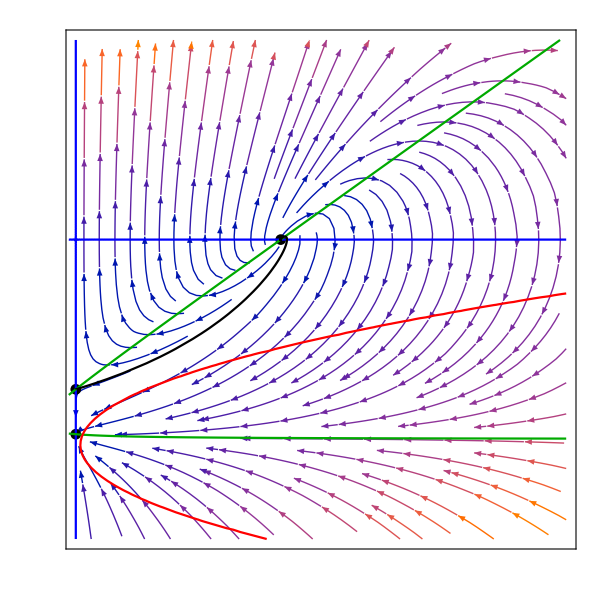

```mathematica
(*Show the plots of the phase space and its components together*)
Show[PhaseSpacexzSpiral,FPsxzSpiral,zLineSpiral,xLineSpiral,AccnxzSpiral,SeparatrixPlotSpiral,xzFormat,PlotRange->{{0,7},{-1,4}}]
```

### Non-Compact x - y - z Phase Space

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, dark matter, z, and the Hubble parameter, y*)
dex:=x'=-3*y*(x-ℛ)*(1+wx+ϵ*x)-q*x*y*z
dey:=y'=-y^2-(1/6)*(z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2) 
dez:=z'=-3*y*z + q*x*y*z
```

```mathematica
(*Find the fixed points of the system*)
FPsSpiral=Solve[{dex==0,dey==0,dez==0},{x,y,z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0.,z→0.025 (3.+14. x+120. x^2)},{x→0.05,y→-0.129099,z→0.},{x→0.05,y→0.129099,z→0.},{x→0.5,y→-0.408248,z→0.},{x→0.5,y→0.408248,z→0.},{x→2.,y→-1.28128,z→2.925},{x→2.,y→1.28128,z→2.925}}

```mathematica
(*Extract the values for the fixed points and put them into a common variable name*)
FPSpiral[1]={x,y/.FPsSpiral[[1,1]],z/.FPsSpiral[[1,2]]};
FPSpiral[2]={x/.FPsSpiral[[2,1]],y/.FPsSpiral[[2,2]],z/.FPsSpiral[[2,3]]};
FPSpiral[3]={x/.FPsSpiral[[3,1]],y/.FPsSpiral[[3,2]],z/.FPsSpiral[[3,3]]};
FPSpiral[4]={x/.FPsSpiral[[4,1]],y/.FPsSpiral[[4,2]],z/.FPsSpiral[[4,3]]};
FPSpiral[5]={x/.FPsSpiral[[5,1]],y/.FPsSpiral[[5,2]],z/.FPsSpiral[[5,3]]};
FPSpiral[6]={x/.FPsSpiral[[6,1]],y/.FPsSpiral[[6,2]],z/.FPsSpiral[[6,3]]};
FPSpiral[7]={x/.FPsSpiral[[7,1]],y/.FPsSpiral[[7,2]],z/.FPsSpiral[[7,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPsSpiral=Table[FPSpiral[i],{i,1,7}];
```

```mathematica
(*Find the 3D Jacobian matrix. D[] differentiates each expression*)
JxyzSpiral=Simplify[{{D[dex,x],D[dex,y],D[dex,z]}, {D[dey,x],D[dey,y],D[dey,z]},{D[dez,x],D[dez,y],D[dez,z]}}];
JxyzSpiral//MatrixForm
```

(y (-1.65+6. x-1.5 z) | 3. (0.025+x^2+x (-0.55-0.5 z)) | -1.5 x y
0.0583333+x | -2 y | -1/6
1.5 y z | (-3+1.5 x) z | (-3+1.5 x) y)

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableSpiral=Table[{FPsSpiral[[i]]//MatrixForm,Simplify[JxyzSpiral/.{x->FPsSpiral[[i,1]],y->FPsSpiral[[i,2]],z->FPsSpiral[[i,3]]}]//MatrixForm,Eigenvalues[JxyzSpiral/.{x->FPsSpiral[[i,1]],y->FPsSpiral[[i,2]],z->FPsSpiral[[i,3]]}]//MatrixForm,Eigenvectors[JxyzSpiral/.{x->FPsSpiral[[i,1]],y->FPsSpiral[[i,2]],z->FPsSpiral[[i,3]]}]//MatrixForm},{i,1,7}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTablexyzSpiral=TableForm[FPTableSpiral,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(x
0.
0.025 (3.+14. x+120. x^2)) | (0. | 0.075-1.7625 x+2.475 x^2-4.5 x^3 | 0.
0.0583333+x | 0. | -1/6
0. | -0.225-0.9375 x-8.475 x^2+4.5 x^3 | 0.) | (0
-√(0.041875+0.128438 x-0.205625 x^2+1.4625 x^3-4.5 x^4)
√(0.041875+0.128438 x-0.205625 x^2+1.4625 x^3-4.5 x^4)) | (0.166667/(0.0583333+x) | 0 | 1.
-(1. (-0.000972222+0.00618056 x+0.359583 x^2-0.491667 x^3+1. x^4))/((0.0583333+x) (-0.05-0.208333 x-1.88333 x^2+1. x^3)) | -(0.222222 √(0.041875+0.128437 x-0.205625 x^2+1.4625 x^3-4.5 x^4))/(-0.05-0.208333 x-1.88333 x^2+1. x^3) | 1.
-(1. (-0.000972222+0.00618056 x+0.359583 x^2-0.491667 x^3+1. x^4))/((0.0583333+x) (-0.05-0.208333 x-1.88333 x^2+1. x^3)) | (0.222222 √(0.041875+0.128437 x-0.205625 x^2+1.4625 x^3-4.5 x^4))/(-0.05-0.208333 x-1.88333 x^2+1. x^3) | 1.)
(0.05
-0.129099
0.) | (0.174284 | 2.08167×10^-17 | 0.00968246
0.108333 | 0.258199 | -1/6
0. | 0. | 0.377616) | (0.377616
0.258199
0.174284) | (0.0282994 | -0.803755 | 0.594287
-1.15126×10^-16 | -1. | 0.
-0.612372 | 0.790569 | 0.)
(0.05
0.129099
0.) | (-0.174284 | 2.08167×10^-17 | -0.00968246
0.108333 | -0.258199 | -1/6
0. | 0. | -0.377616) | (-0.377616
-0.258199
-0.174284) | (0.0282994 | 0.803755 | 0.594287
-1.15126×10^-16 | 1. | 0.
0.612372 | 0.790569 | 0.)
(0.5
-0.408248
0.) | (-0.551135 | 1.66533×10^-16 | 0.306186
0.558333 | 0.816497 | -1/6
0. | 0. | 0.918559) | (0.918559
0.816497
-0.551135) | (0.183659 | -0.434875 | 0.881563
-1.7255×10^-16 | -1. | 0.
-0.92582 | 0.377964 | 0.)
(0.5
0.408248
0.) | (0.551135 | 1.66533×10^-16 | -0.306186
0.558333 | -0.816497 | -1/6
0. | 0. | -0.918559) | (-0.918559
-0.816497
0.551135) | (0.183659 | 0.434875 | 0.881563
-1.7255×10^-16 | 1. | 0.
0.92582 | 0.377964 | 0.)
(2.
-1.28128
2.925) | (-7.6396 | 2.66454×10^-15 | 3.84383
2.05833 | 2.56255 | -1/6
-5.6216 | 0. | 0.) | (-3.8198+2.64907 ⅈ
-3.8198-2.64907 ⅈ
2.56255+0. ⅈ) | (0.515823-0.357728 ⅈ | -0.165845+0.0465328 ⅈ | 0.759136+0. ⅈ
0.515823+0.357728 ⅈ | -0.165845-0.0465328 ⅈ | 0.759136+0. ⅈ
2.16224×10^-16+0. ⅈ | 1.+0. ⅈ | -3.62854×10^-16+0. ⅈ)
(2.
1.28128
2.925) | (7.6396 | 2.66454×10^-15 | -3.84383
2.05833 | -2.56255 | -1/6
5.6216 | 0. | 0.) | (3.8198+2.64907 ⅈ
3.8198-2.64907 ⅈ
-2.56255+0. ⅈ) | (0.515823+0.357728 ⅈ | 0.165845+0.0465328 ⅈ | 0.759136+0. ⅈ
0.515823-0.357728 ⅈ | 0.165845-0.0465328 ⅈ | 0.759136+0. ⅈ
2.16224×10^-16+0. ⅈ | -1.+0. ⅈ | -3.62854×10^-16+0. ⅈ)

```mathematica
(*Plot the line of Einstein fixed points*)
EinsteinPointLineSpiral=ParametricPlot3D[{FPSpiral[1][[1]],FPSpiral[1][[2]],FPSpiral[1][[3]]},{x,0,4},PlotStyle->Red];
```

```mathematica
(*Plot the fixed points of the system*)
FPsxyzSpiral=ListPointPlot3D[Table[FPSpiral[i],{i,2,7}],PlotStyle->Black];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
AccnxyzSpiral=ContourPlot3D[z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2==0,{x,0,4},{y,-5,5},{z,0,7},ContourStyle->{Red,Opacity[0.25]},Mesh->None];
```

```mathematica
(*Plot the x-y-z phase space*)
PhaseSpacexyzSpiral=StreamPlot3D[{dex,dey,dez},{x,0,4},{y,-5,5},{z,0,7},AxesLabel->{"x","y","z"}];
```

```mathematica
(*Show the phase space and its components together*)
Show[PhaseSpacexyzSpiral,FPsxyzSpiral,EinsteinPointLineSpiral,AccnxyzSpiral,AxesLabel->{MaTeX["x",FontSize->20],MaTeX["y",FontSize->20],MaTeX["z",FontSize->20]},Ticks->{{0.,2.,4.,6.},{-5.,0.,1.,5.},{0.,2.,4.,6.}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->20}]
```

-Graphics3D-

## Constant x0 and z0 surfaces

Trajectories are plotted on a constant x0-z0 surface, where x0 is fixed for all cases and z0 is fixed for each phase space to give a different number of Einstein fixed points. k and y0 differ for each trajectory in each phase space.

### Set-up for the phase spaces

```mathematica
(*Define a format for the x-y-z phase spaces*)
xyzFormat={AxesLabel->{MaTeX["x",FontSize->20],MaTeX["y",FontSize->20],MaTeX["z",FontSize->20]},Ticks->{{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.},{-5.,-4.,-3.,-2.,-1.,0.,1.,2.,3.,4.,5.},{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->20}};
```

```mathematica
(*Define the system of differential equations for the dark energy, x, and dark matter, z, in terms of a time variable*)
dext:=x1'[t]==-3*y1[t]*(x1[t]-ℛ)*(1+wx+ϵ*x1[t])-q*x1[t]*y1[t]*z1[t]
deyt:=y1'[t]==-y1[t]^2-(1/6)*(z1[t]+x1[t]*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x1[t]^2) 
dezt:=z1'[t]==-3*y1[t]*z1[t] + q*x1[t]*y1[t]*z1[t]
```

```mathematica
(*Define Ωx0 and Ωm0 using data from Planck 2018*)
Ωx0=0.6889;
Ωm0=0.3111;
```

```mathematica
(*Set a value for α, which sets the value of the low energy cosmological constant*)
α=0.5;
```

```mathematica
(*Define the initial conditions, where a0 = 1 and K is defined as k/ρ* *)

x0=ℛ/α;
y0=Sqrt[x0/3+z0/3-K];
```

```mathematica
(*Define values of K using the range of Ωk0 allowed by Planck 2018*)
Ωk0Open=0.003;
Ωk0Closed=-0.001;

KDensityParametersOpen=-Ωk0Open*ℛ/(3*α*Ωx0)
KDensityParametersClosed=-Ωk0Closed*ℛ/(3*α*Ωx0)
```

-0.000145159

0.0000483863

### Plot the Flat Friedmann Separatrix (FFS)

```mathematica
(*Define the Friedmann equation when K = 0*)
yFFS=Sqrt[x/3+z/3];
```

```mathematica
(*Plot the FFS*)
FFSPlot=ParametricPlot3D[{{x,yFFS,z},{x,-yFFS,z}},{x,0,3},{z,0,3},PlotStyle->{Darker[Green]},Mesh->None];
```

```mathematica
(*Show the FFS*)
Show[FFSPlot,xyzFormat]
```

-Graphics3D-

### Limiting Case with 1 Einstein fixed point

#### Find the Einstein Fixed Point

```mathematica
(*Fix z0 so that there is one Einstein fixed point on the surface*)
z0LimitingSpiral=0.0085;
```

```mathematica
(*Substitute z0Limiting into y0 for this case*)
y0LimitingSpiral=y0/.z0->z0LimitingSpiral
```

√(0.0361667-K)

```mathematica
(*Numerically solve the system of equations using the initial conditions defined for the limiting case with one Einstein fixed point*)
trajLimitingSpiral[K_]=NDSolve[{dext,deyt,dezt,x1[0]==x0,y1[0]==y0LimitingSpiral,z1[0]==z0LimitingSpiral},{x1,y1,z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition √(0.0361667-1. K) is not a number or a rectangular array of numbers.

NDSolve[{x1'[t]==-3 (0.5-x1[t]) (-0.05+x1[t]) y1[t]-1.5 x1[t] y1[t] z1[t],y1'[t]==-y1[t]^2+1/6 (0.075+0.35 x1[t]+3 x1[t]^2-z1[t]),z1'[t]==-3 y1[t] z1[t]+1.5 x1[t] y1[t] z1[t],x1[0]==0.1,y1[0]==√(0.0361667-K),z1[0]==0.0085},{x1,y1,z1},{t,-100,100}]

```mathematica
(*Set-up tables of all x1 and z1 values to be used to find the x and z value of the Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
xTableSolLimitingSpiral=Table[x1[i]/.trajLimitingSpiral[0],{i,-100,100,.01}];
zTableSolLimitingSpiral=Table[z1[i]/.trajLimitingSpiral[0],{i,-100,100,.01}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSolLimitingSpiral=(zTableSolLimitingSpiral)+(xTableSolLimitingSpiral)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSolLimitingSpiral)^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSolLimiting that is closest to zero. When EinsteinPlotValuesSolLimiting = 0 (y = 0), there is an Einstein point*)
NearestToZeroLimitingSpiral=Flatten[Nearest[EinsteinPlotValuesSolLimitingSpiral,0]]
```

{-0.00223398}

```mathematica
(*Find the position of NearestToZeroLimiting in the EinsteinPlotValuesSolLimiting array*)
PositionNearestToZeroLimitingSpiral=Flatten[Position[EinsteinPlotValuesSolLimitingSpiral,NearestToZeroLimitingSpiral]]
```

{8154}

```mathematica
(*Find the Einstein point by finding the x and z values in xTableSolLimiting and zTableSolLimiting at PositionNearestToZeroLimiting*)
EinsteinPointLimitingSpiral=Flatten[{xTableSolLimitingSpiral[[PositionNearestToZeroLimitingSpiral]],0,zTableSolLimitingSpiral[[PositionNearestToZeroLimitingSpiral]]}]
```

{0.459079,0,0.865704}

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for the Einstein fixed point*)
EinsteinTableLimitingSpiral=Table[{EinsteinPointLimitingSpiral//MatrixForm,Simplify[JxyzSpiral/.{x->EinsteinPointLimitingSpiral[[1]],y->EinsteinPointLimitingSpiral[[2]],z->EinsteinPointLimitingSpiral[[3]]}]//MatrixForm,Eigenvalues[JxyzSpiral/.{x->EinsteinPointLimitingSpiral[[1]],y->EinsteinPointLimitingSpiral[[2]],z->EinsteinPointLimitingSpiral[[3]]}]//MatrixForm,Eigenvectors[JxyzSpiral/.{x->EinsteinPointLimitingSpiral[[1]],y->EinsteinPointLimitingSpiral[[2]],z->EinsteinPointLimitingSpiral[[3]]}]//MatrixForm},1];
```

```mathematica
(*Use TableForm to display the Einstein fixed point with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableEinsteinPointLimitingSpiral=TableForm[EinsteinTableLimitingSpiral,TableHeadings->{None,{"Einstein Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Einstein Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.459079
0
0.865704) | (0. | -0.64636 | 0.
0.517412 | 0 | -1/6
0. | -2.00097 | 0.) | (-1.23112×10^-14+0.0306424 ⅈ
-1.23112×10^-14-0.0306424 ⅈ
2.4201×10^-14+0. ⅈ) | (-0.307351-6.85042×10^-16 ⅈ | -5.79124×10^-15+0.0145708 ⅈ | -0.951485+0. ⅈ
-0.307351+6.85042×10^-16 ⅈ | -5.79124×10^-15-0.0145708 ⅈ | -0.951485+0. ⅈ
0.306602+0. ⅈ | -1.1575×10^-14+0. ⅈ | 0.951838+0. ⅈ)

```mathematica
(*Set-up tables of all x1 and z1 values with a bigger t increment*)
xTableSolLimitingFullSpiral=Table[x1[i]/.trajLimitingSpiral[0],{i,-100,100,.1}];
zTableSolLimitingFullSpiral=Table[z1[i]/.trajLimitingSpiral[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0*)
EinsteinPlotValuesSolLimitingFullSpiral=(zTableSolLimitingFullSpiral)+(xTableSolLimitingFullSpiral)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSolLimitingFullSpiral)^2;
```

```mathematica
(*Merge the xTableSolLimitingFull values and the EinsteinPlotValuesSolLimitingFull values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsLimitingSpiral=MapThread[h,{xTableSolLimitingFullSpiral,EinsteinPlotValuesSolLimitingFullSpiral}];
```

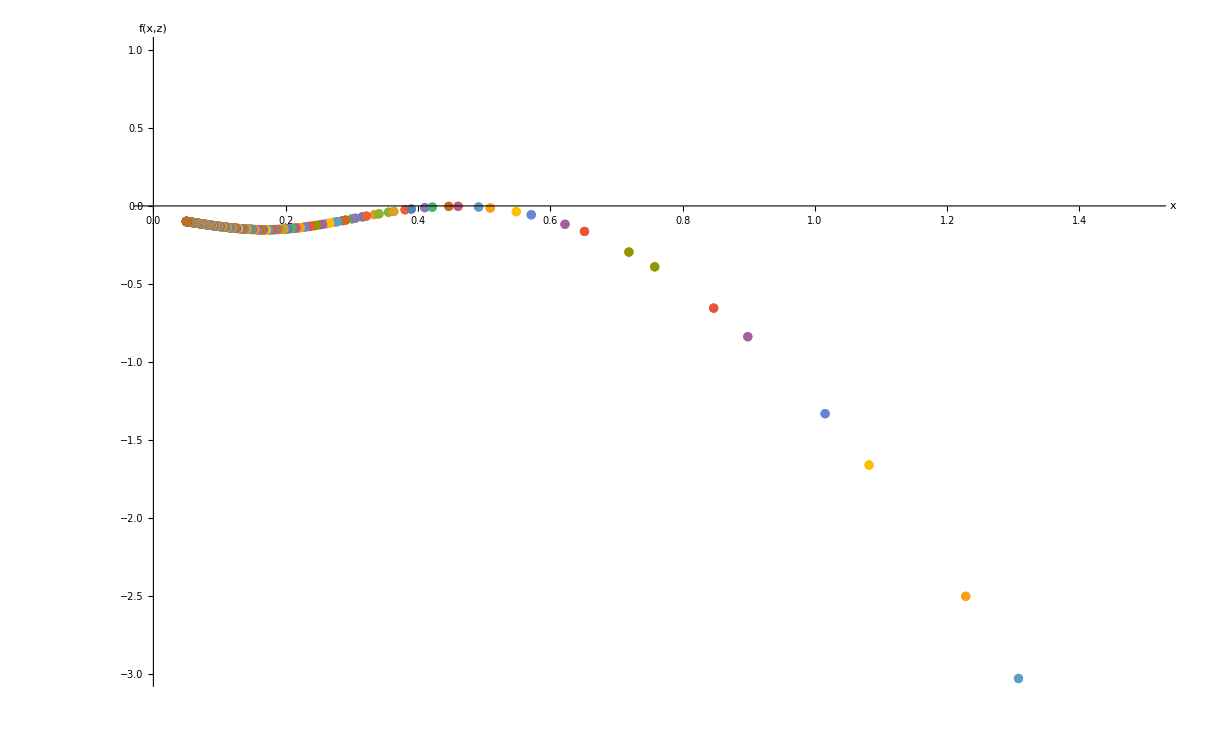

```mathematica
(*Plot x vs the remaining equation when y' = 0*)
(*When f(x,z) = 0, an Einstein point exists*)
EinsteinPlotLimitingSpiral=ListPlot[EinsteinPointSolutionsLimitingSpiral,PlotRange->{{0,1.5},{-3,1}},AxesLabel->{"x","f(x,z)"}]
```

#### Plot the x-y-z Phase Space

```mathematica
(*Find the maximum value of K for this combination of x0 and z0 such that y0 is not imaginary*)
KMaxLimitingSpiral=K/.Solve[y0LimitingSpiral==0,K][[1]]
```

0.0361667

```mathematica
(*Solve trajLimiting[K] for different values of K*)
```

```mathematica
solLimitingSpiral[1]=trajLimitingSpiral[0.01]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solLimitingSpiral[2]=trajLimitingSpiral[KDensityParametersClosed]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solLimitingSpiral[3]=trajLimitingSpiral[-.1]
```

NDSolve::ndsz: At t == -2.89319, step size is effectively zero; singularity or stiff system suspected.

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solLimitingSpiral[4]=trajLimitingSpiral[0.015]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solLimitingSpiral[5]=trajLimitingSpiral[-0.01]
```

NDSolve::ndsz: At t == -5.99158, step size is effectively zero; singularity or stiff system suspected.

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the trajectories for the different values of K given above*)
```

```mathematica
trajLimitingxyzSpiral[1]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimitingSpiral[1],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingxyzSpiral[2]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimitingSpiral[2],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingxyzSpiral[3]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimitingSpiral[3],{t,-2.88,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingxyzSpiral[4]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimitingSpiral[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
trajLimitingxyzSpiral[5]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimitingSpiral[5],{t,-5.98,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajLimitingCaseSpiral=Table[trajLimitingxyzSpiral[i],{i,1,5}];
```

```mathematica
(*Plot the Einstein fixed point*)
EinsteinFixedPointsLimitingSpiral=ListPointPlot3D[{EinsteinPointLimitingSpiral},PlotStyle->Black];
```

```mathematica
(*Solve the x-y-z system around the Einstein fixed point to plot the Closed Friedmann Separatrix (CFS)*)
CFSLimitingSolSpiral=NDSolve[{dext,deyt,dezt,x1[0]==EinsteinPointLimitingSpiral[[1]],y1[0]==0,z1[0]==EinsteinPointLimitingSpiral[[3]]},{x1,y1,z1},{t,-100,100}]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the CFS*)
CFSLimitingSpiral=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.CFSLimitingSolSpiral,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
(*Show the x-y-z phase space*)
Show[trajLimitingCaseSpiral,EinsteinFixedPointsLimitingSpiral,CFSLimitingSpiral,AccnxyzSpiral,FPsxyzSpiral,xyzFormat,PlotRange->{{0,3},{-5,5},{0,4}}]
```

-Graphics3D-

#### Plot the x-z Projection

```mathematica
(*Plot one solution on the x-z plane*)
trajLimitingxzSpiral=ParametricPlot[Evaluate[{{z1[t],x1[t]}}/.solLimitingSpiral[2],{t,-100,100},PlotStyle -> {{Black, Thick,Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,0,0,.03,.03,0},1]]],Arrow[x]};
```

```mathematica
(*Plot the Einstein fixed point on the x-z plane*)
EinsteinFixedPointsLimitingxzSpiral=ListPlot[{{EinsteinPointLimitingSpiral[[3]],EinsteinPointLimitingSpiral[[1]]}},PlotStyle->Black];
```

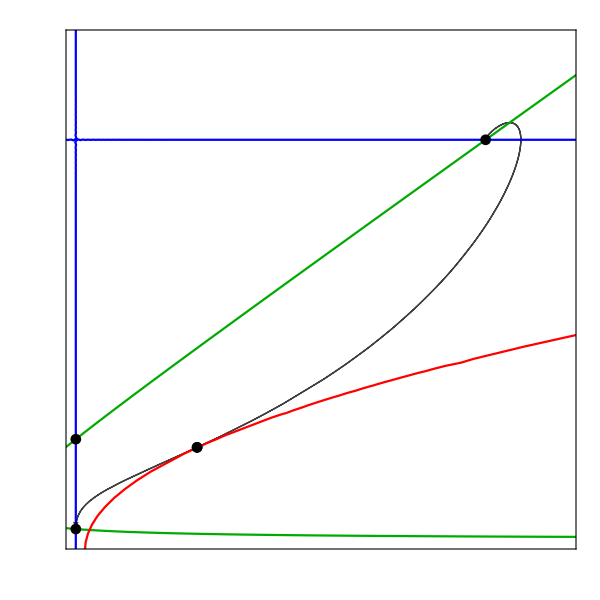

```mathematica
(*Show the x-z phase space with the a'' = 0 (red), x' = 0 (green) and z' = 0 (purple) curves*)
Show[trajLimitingxzSpiral,xLineSpiral,zLineSpiral,AccnxzSpiral,FPsxzSpiral,EinsteinFixedPointsLimitingxzSpiral,xzFormat,PlotRange->{{0,3.5},{0,2.5}}]
```

### Two Einstein Fixed Points

#### Find the Einstein Fixed Points

```mathematica
(*Fix z0 using the density parameters. In this case there are two Einstein fixed points*)
z0TwoEinsteinPointsSpiral=Ωm0*ℛ/(Ωx0*α)
```

0.0451589

```mathematica
(*Substitute z0TwoEinsteinPoints into y0 for this case*)
y0TwoEinsteinPointsSpiral=y0/.z0->z0TwoEinsteinPointsSpiral
```

√(0.0483863-K)

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajTwoEinsteinPointsSpiral[K_]=NDSolve[{dext,deyt,dezt,x1[0]==x0,y1[0]==y0TwoEinsteinPointsSpiral,z1[0]==z0TwoEinsteinPointsSpiral},{x1,y1,z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition √(0.0483863-1. K) is not a number or a rectangular array of numbers.

NDSolve[{x1'[t]==-3 (0.5-x1[t]) (-0.05+x1[t]) y1[t]-1.5 x1[t] y1[t] z1[t],y1'[t]==-y1[t]^2+1/6 (0.075+0.35 x1[t]+3 x1[t]^2-z1[t]),z1'[t]==-3 y1[t] z1[t]+1.5 x1[t] y1[t] z1[t],x1[0]==0.1,y1[0]==√(0.0483863-K),z1[0]==0.0451589},{x1,y1,z1},{t,-100,100}]

```mathematica
(*Set-up tables of x1 and z1 values to be used to find the x and z value of the first Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
xTableSol1TwoEinsteinPointsSpiral=Table[x1[i]/.trajTwoEinsteinPointsSpiral[0],{i,-2,100,.01}];
zTableSol1TwoEinsteinPointsSpiral=Table[z1[i]/.trajTwoEinsteinPointsSpiral[0],{i,-2,100,.01}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol1TwoEinsteinPointsSpiral=(zTableSol1TwoEinsteinPointsSpiral)+(xTableSol1TwoEinsteinPointsSpiral)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol1TwoEinsteinPointsSpiral)^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol1TwoEinsteinPoints that is closest to zero. When EinsteinPlotValuesSol1TwoEinsteinPoints = 0 (y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints1Spiral=Flatten[Nearest[EinsteinPlotValuesSol1TwoEinsteinPointsSpiral,0]]
```

{0.0000561404}

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints1 in the EinsteinPlotValuesSol1TwoEinsteinPoints*)
PositionNearestToZeroTwoEinsteinPoints1Spiral=Flatten[Position[EinsteinPlotValuesSol1TwoEinsteinPointsSpiral,NearestToZeroTwoEinsteinPoints1Spiral]]
```

{4}

```mathematica
(*Find the Einstein point by finding the x and z values in xTableSol1TwoEinsteinPoints and zTableSol1TwoEinsteinPoints at PositionNearestToZeroTwoEinsteinPoints1*)
EinsteinPoint1TwoEinsteinPointsSpiral=Flatten[{xTableSol1TwoEinsteinPointsSpiral[[PositionNearestToZeroTwoEinsteinPoints1Spiral]],0,zTableSol1TwoEinsteinPointsSpiral[[PositionNearestToZeroTwoEinsteinPoints1Spiral]]}]
```

{0.154329,0,0.200524}

```mathematica
(*Set-up tables of x1 and z1 values to be used to find the x and z value of the second Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
xTableSol2TwoEinsteinPointsSpiral=Table[x1[i]/.trajTwoEinsteinPointsSpiral[0],{i,-5.6,-3.2,.001}];
zTableSol2TwoEinsteinPointsSpiral=Table[z1[i]/.trajTwoEinsteinPointsSpiral[0],{i,-5.6,-3.2,.001}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol2TwoEinsteinPointsSpiral=(zTableSol2TwoEinsteinPointsSpiral)+(xTableSol2TwoEinsteinPointsSpiral)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol2TwoEinsteinPointsSpiral)^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol2TwoEinsteinPoints that is closest to zero. When EinsteinPlotValuesSol2TwoEinsteinPoints = 0 (y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints2Spiral=Flatten[Nearest[EinsteinPlotValuesSol2TwoEinsteinPointsSpiral,0]]
```

{-0.000640093}

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints2 in the EinsteinPlotValuesSol2TwoEinsteinPoints array*)
PositionNearestToZeroTwoEinsteinPoints2Spiral=Flatten[Position[EinsteinPlotValuesSol2TwoEinsteinPointsSpiral,NearestToZeroTwoEinsteinPoints2Spiral]]
```

{1901}

```mathematica
(*Find the Einstein point by finding the x and z values in xTableSol2TwoEinsteinPoints and zTableSol2TwoEinsteinPoints at PositionNearestToZeroTwoEinsteinPoints2*)
EinsteinPoint2TwoEinsteinPointsSpiral=Flatten[{xTableSol2TwoEinsteinPointsSpiral[[PositionNearestToZeroTwoEinsteinPoints2Spiral]],0,zTableSol2TwoEinsteinPointsSpiral[[PositionNearestToZeroTwoEinsteinPoints2Spiral]]}]
```

{0.784094,0,2.1932}

```mathematica
(*Put the Einstein fixed points into a common variable name*)
EinsteinPointTwoEPtsSpiral[1]=EinsteinPoint1TwoEinsteinPointsSpiral;
EinsteinPointTwoEPtsSpiral[2]=EinsteinPoint2TwoEinsteinPointsSpiral;
```

```mathematica
(*Put the Einstein fixed points into a table*)
EinsteinPointsTwoEPtsSpiral=Table[EinsteinPointTwoEPtsSpiral[i],{i,1,2}];
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each Einstein fixed point*)
EinsteinPointTableTwoEinsteinPointsSpiral=Table[{EinsteinPointsTwoEPtsSpiral[[i]]//MatrixForm,Simplify[JxyzSpiral/.{x->EinsteinPointsTwoEPtsSpiral[[i,1]],y->EinsteinPointsTwoEPtsSpiral[[i,2]],z->EinsteinPointsTwoEPtsSpiral[[i,3]]}]//MatrixForm,Eigenvalues[JxyzSpiral/.{x->EinsteinPointsTwoEPtsSpiral[[i,1]],y->EinsteinPointsTwoEPtsSpiral[[i,2]],z->EinsteinPointsTwoEPtsSpiral[[i,3]]}]//MatrixForm,Eigenvectors[JxyzSpiral/.{x->EinsteinPointsTwoEPtsSpiral[[i,1]],y->EinsteinPointsTwoEPtsSpiral[[i,2]],z->EinsteinPointsTwoEPtsSpiral[[i,3]]}]//MatrixForm},{i,1,2}];
```

```mathematica
(*Use TableForm to display the Einstein fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableTwoEinsteinPointsSpiral=TableForm[EinsteinPointTableTwoEinsteinPointsSpiral,TableHeadings->{None,{"Einstein Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Einstein Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.154329
0
0.200524) | (0. | -0.154611 | 0.
0.212662 | 0 | -1/6
0. | -0.555151 | 0.) | (0.244224
-0.244224
2.15523×10^-18) | (0.247024 | -0.390201 | 0.886974
-0.247024 | -0.390201 | -0.886974
0.616848 | -2.3491×10^-16 | 0.787082)
(0.784094
0
2.1932) | (0. | -1.95386 | 0.
0.842428 | 0 | -1/6
0. | -4.00009 | 0.) | (7.70398×10^-18+0.989599 ⅈ
7.70398×10^-18-0.989599 ⅈ
-1.74185×10^-16+0. ⅈ) | (0.428437-5.6752×10^-17 ⅈ | -3.93578×10^-17-0.216996 ⅈ | 0.877128+0. ⅈ
0.428437+5.6752×10^-17 ⅈ | -3.93578×10^-17+0.216996 ⅈ | 0.877128+0. ⅈ
0.194079+0. ⅈ | 7.34722×10^-17+0. ⅈ | 0.980986+0. ⅈ)

```mathematica
(*Set-up tables of all x1 and z1 values*)
xTableSolTwoEinsteinPointsFullSpiral=Table[x1[i]/.trajTwoEinsteinPointsSpiral[0],{i,-100,100,.1}];
zTableSolTwoEinsteinPointsFullSpiral=Table[z1[i]/.trajTwoEinsteinPointsSpiral[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0*)
EinsteinPlotValuesSolTwoEinsteinPointsFullSpiral=(zTableSolTwoEinsteinPointsFullSpiral)+(xTableSolTwoEinsteinPointsFullSpiral)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSolTwoEinsteinPointsFullSpiral)^2;
```

```mathematica
(*Merge the xTableSolTwoEinsteinPointsFull values and the EinsteinPlotValuesSolTwoEinsteinPointsFull values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsTwoEinsteinPointsSpiral=MapThread[h,{xTableSolTwoEinsteinPointsFullSpiral,EinsteinPlotValuesSolTwoEinsteinPointsFullSpiral}];
```

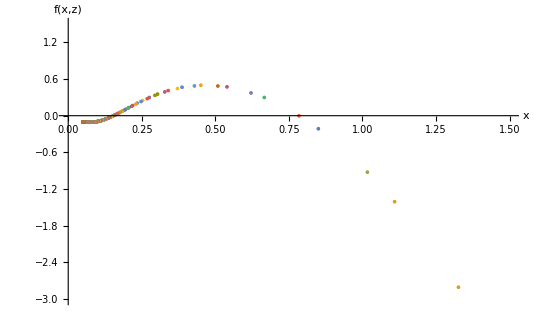

```mathematica
(*Plot x vs the remaining equation when y' = 0*)
(*When f(x,z) = 0, an Einstein point exists*)
EinsteinPlotTwoEinsteinPointsSpiral=ListPlot[EinsteinPointSolutionsTwoEinsteinPointsSpiral,PlotRange->{{0,1.5},{-3,1.5}},AxesLabel->{"x","f(x,z)"}]
```

#### Plot the x-y-z Phase Space

```mathematica
(*Find the maximum value of K for this combination of x0 and z0 so that y0 is not imaginary*)
KMaxTwoEinsteinPointsSpiral=K/.Flatten[Solve[y0TwoEinsteinPointsSpiral==0,K]]
```

0.0483863

```mathematica
(*Solve trajTwoEinsteinPoints[K] for different values of K*)
```

```mathematica
solTwoEinsteinPointsSpiral[1]=trajTwoEinsteinPointsSpiral[-.02]
```

NDSolve::ndsz: At t == -4.21647, step size is effectively zero; singularity or stiff system suspected.

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsSpiral[2]=trajTwoEinsteinPointsSpiral[0.005]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsSpiral[3]=trajTwoEinsteinPointsSpiral[-.1]
```

NDSolve::ndsz: At t == -2.68568, step size is effectively zero; singularity or stiff system suspected.

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsSpiral[4]=trajTwoEinsteinPointsSpiral[KMaxTwoEinsteinPointsSpiral]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsSpiral[5]=trajTwoEinsteinPointsSpiral[0.03]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the trajectories for the different values of K given above*)
```

```mathematica
trajTwoEinsteinPointsxyzSpiral[1]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsSpiral[1],{t,-4.21,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsxyzSpiral[2]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsSpiral[2],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsxyzSpiral[3]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsSpiral[3],{t,-2.65,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsxyzSpiral[4]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsSpiral[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75],Dashed}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
trajTwoEinsteinPointsxyzSpiral[5]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsSpiral[5],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
(*Solve the x-y-z system using the centre Einstein fixed point for x0 and z0 to plot a cyclic trajectory*)
CyclicTrajTwoEinsteinPointsSpiral=NDSolve[{dext,deyt,dezt,x1[0]==EinsteinPoint2TwoEinsteinPointsSpiral[[1]],y1[0]==0.3,z1[0]==EinsteinPoint2TwoEinsteinPointsSpiral[[3]]},{x1,y1,z1},{t,-100,100}];
```

```mathematica
(*Plot the cyclic trajectory*)
trajTwoEinsteinPointsxyzSpiral[6]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.CyclicTrajTwoEinsteinPointsSpiral,{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajTwoEinsteinPointsCaseSpiral=Table[trajTwoEinsteinPointsxyzSpiral[i],{i,1,6}];
```

```mathematica
(*Plot the Einstein fixed points*)
EinsteinFixedPointsTwoEinsteinPointsSpiral=ListPointPlot3D[{EinsteinPoint1TwoEinsteinPointsSpiral,EinsteinPoint2TwoEinsteinPointsSpiral},PlotStyle->Black];
```

```mathematica
(*Solve the x-y-z system around the Einstein fixed point to plot the Closed Friedmann Separatrix (CFS)*)
CFSTwoEinsteinPointsSolSpiral=NDSolve[{dext,deyt,dezt,x1[0]==EinsteinPoint1TwoEinsteinPointsSpiral[[1]],y1[0]==-0.0005,z1[0]==EinsteinPoint1TwoEinsteinPointsSpiral[[3]]},{x1,y1,z1},{t,-100,100}]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the CFS*)
CFSTwoEinsteinPointsSpiral=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.CFSTwoEinsteinPointsSolSpiral,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Show the x-y-z phase space*)
Show[trajTwoEinsteinPointsCaseSpiral,CFSTwoEinsteinPointsSpiral,EinsteinFixedPointsTwoEinsteinPointsSpiral,AccnxyzSpiral,FPsxyzSpiral,xyzFormat,PlotRange->{{0,3},{-5,5},{0,4}}]
```

-Graphics3D-

#### Plot the x-z Projection

```mathematica
(*Plot one solution on the x-z plane*)
trajTwoEinsteinPointsxzSpiral=ParametricPlot[Evaluate[{{z1[t],x1[t]}}/.solTwoEinsteinPointsSpiral[1],{t,-4.21,100},PlotStyle -> {{Black, Thick,Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.03,.03,0},1]]],Arrow[x]};;
```

```mathematica
(*Plot the Einstein fixed points on the x-z plane*)
EinsteinFixedPointsTwoEinsteinPointsxzSpiral=ListPlot[{{EinsteinPoint1TwoEinsteinPointsSpiral[[3]],EinsteinPoint1TwoEinsteinPointsSpiral[[1]]},{EinsteinPoint2TwoEinsteinPointsSpiral[[3]],EinsteinPoint2TwoEinsteinPointsSpiral[[1]]}},PlotStyle->Black];
```

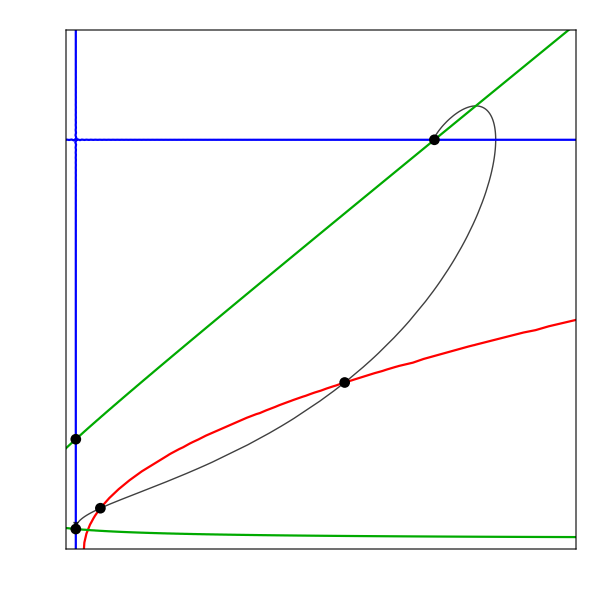

```mathematica
(*Show the x-z phase space with the a'' = 0 (red), x' = 0 (green) and z' = 0 (purple) curves*)
Show[trajTwoEinsteinPointsxzSpiral,AccnxzSpiral,xLineSpiral,zLineSpiral,FPsxzSpiral,EinsteinFixedPointsTwoEinsteinPointsxzSpiral,xzFormat,PlotRange->{{0,4},{0,2.5}}]
```

### No Einstein Fixed Points

#### Plot to show that there are no Einstein fixed points

```mathematica
(*Fix z0 such that there are no Einstein fixed points on the surface*)
z0NoEinsteinPointsSpiral=0.005;
```

```mathematica
(*Substitute z0NoEinsteinPoints into y0 for this case*)
y0NoEinsteinPointsSpiral=y0/.z0->z0NoEinsteinPointsSpiral
```

√(0.035-K)

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajNoEinsteinPointsSpiral[K_]=NDSolve[{dext,deyt,dezt,x1[0]==x0,y1[0]==y0NoEinsteinPointsSpiral,z1[0]==z0NoEinsteinPointsSpiral},{x1,y1,z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition √(0.035-1. K) is not a number or a rectangular array of numbers.

NDSolve[{x1'[t]==-3 (0.5-x1[t]) (-0.05+x1[t]) y1[t]-1.5 x1[t] y1[t] z1[t],y1'[t]==-y1[t]^2+1/6 (0.075+0.35 x1[t]+3 x1[t]^2-z1[t]),z1'[t]==-3 y1[t] z1[t]+1.5 x1[t] y1[t] z1[t],x1[0]==0.1,y1[0]==√(0.035-K),z1[0]==0.005},{x1,y1,z1},{t,-100,100}]

```mathematica
(*Set-up tables of all x1 and z1 values*)
xTableSolNoEinsteinPointsFullSpiral=Table[x1[i]/.trajNoEinsteinPointsSpiral[0],{i,-100,100,.1}];
zTableSolNoEinsteinPointsFullSpiral=Table[z1[i]/.trajNoEinsteinPointsSpiral[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0*)
EinsteinPlotValuesSolNoEinsteinPointsFullSpiral=(zTableSolNoEinsteinPointsFullSpiral)+(xTableSolNoEinsteinPointsFullSpiral)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSolNoEinsteinPointsFullSpiral)^2;
```

```mathematica
(*Merge the xTableSolNoEinsteinPointsFull values and the EinsteinPlotValuesSolNoEinsteinPointsFull values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsNoEinsteinPointsSpiral=MapThread[h,{xTableSolNoEinsteinPointsFullSpiral,EinsteinPlotValuesSolNoEinsteinPointsFullSpiral}];
```

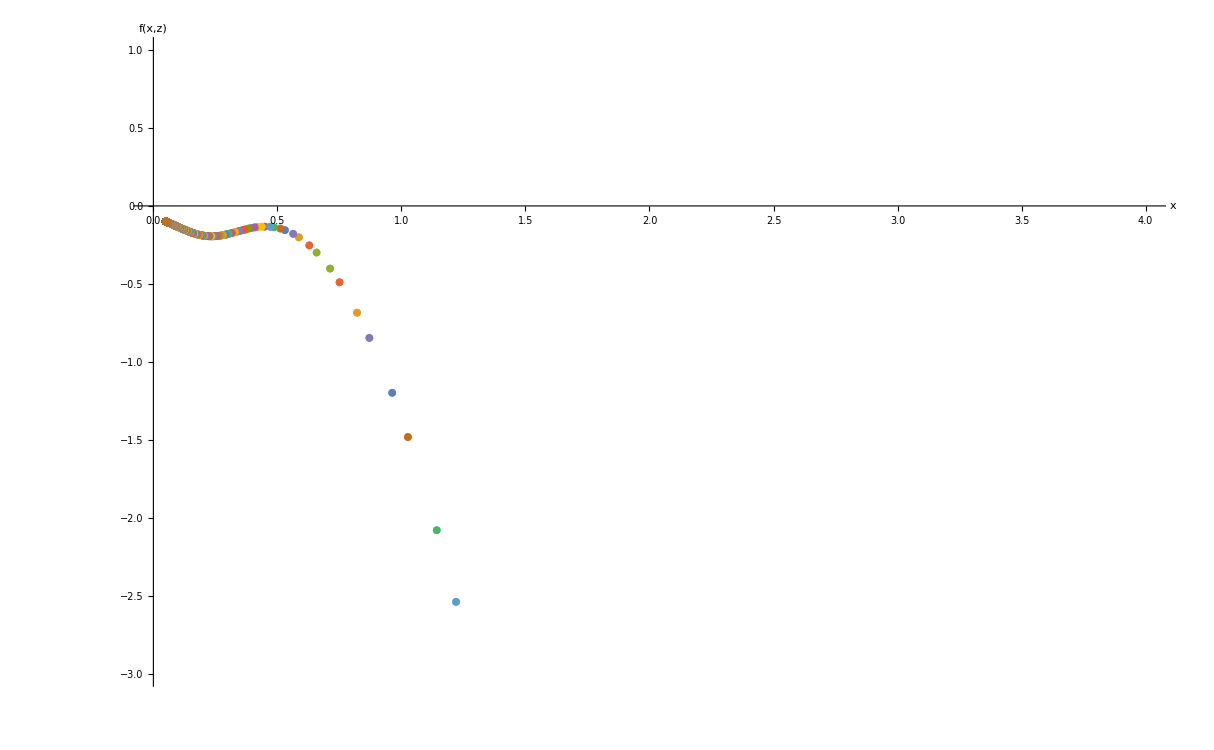

```mathematica
(*Plot x vs the remaining equation when y' = 0*)
(*Here, f(x,z) is never zero, so there are no Einstein fixed points*)
EinsteinPlotNoEinsteinPointsSpiral=ListPlot[EinsteinPointSolutionsNoEinsteinPointsSpiral,PlotRange->{{0,4},{-3,1}},AxesLabel->{"x","f(x,z)"}]
```

#### Plot the x-y-z Phase Space

```mathematica
(*Find the maximum value of K for this combination of x0 and z0 such that y0 is not imaginary*)
KMaxNoEinsteinPointsSpiral=K/.Solve[y0NoEinsteinPointsSpiral==0,K][[1]]
```

0.035

```mathematica
(*Solve trajNoEinsteinPoints[K] for different values of K*)
```

```mathematica
solNoEinsteinPointsSpiral[1]=trajNoEinsteinPointsSpiral[-0.01]
```

NDSolve::ndsz: At t == -6.26236, step size is effectively zero; singularity or stiff system suspected.

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solNoEinsteinPointsSpiral[2]=trajNoEinsteinPointsSpiral[KDensityParametersClosed]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solNoEinsteinPointsSpiral[3]=trajNoEinsteinPointsSpiral[-.08]
```

NDSolve::ndsz: At t == -3.20889, step size is effectively zero; singularity or stiff system suspected.

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solNoEinsteinPointsSpiral[4]=trajNoEinsteinPointsSpiral[0.0095]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solNoEinsteinPointsSpiral[5]=trajNoEinsteinPointsSpiral[0.007]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the trajectories for the different values of K given above.*)
```

```mathematica
trajNoEinsteinPointsxyzSpiral[1]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPointsSpiral[1],{t,-6.25,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsxyzSpiral[2]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPointsSpiral[2],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsxyzSpiral[3]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPointsSpiral[3],{t,-3.2,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsxyzSpiral[4]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPointsSpiral[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsxyzSpiral[5]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPointsSpiral[5],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajNoEinsteinPointsPlotsSpiral=Table[trajNoEinsteinPointsxyzSpiral[i],{i,1,5}];
```

```mathematica
(*Show the x-y-z phase space*)
Show[trajNoEinsteinPointsPlotsSpiral,AccnxyzSpiral,FPsxyzSpiral,xyzFormat,PlotRange->{{0,2.5},{-5,5},{0,4}}]
```

-Graphics3D-

#### Plot the x-z Projection

```mathematica
(*Plot one solution on the x-z plane*)
trajNoEinsteinPointsxzSpiral=ParametricPlot[Evaluate[{{z1[t],x1[t]}}/.solNoEinsteinPointsSpiral[2],{t,-100,100},PlotStyle -> {{Black,Thick, Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,0,0,.03,.03,0},1]]],Arrow[x]};
```

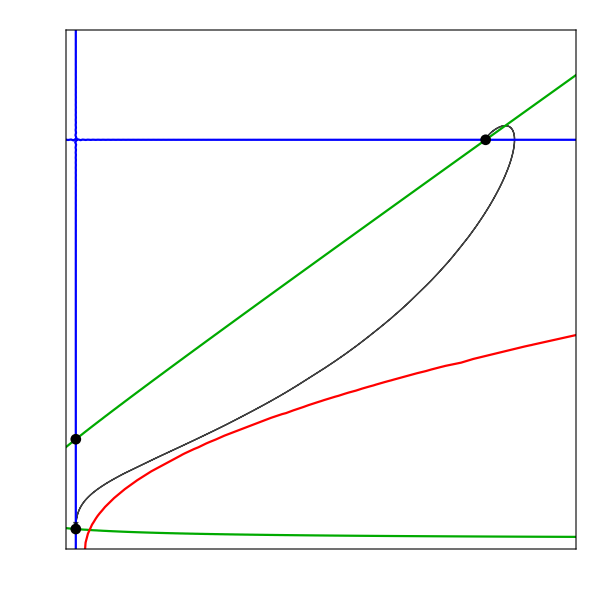

```mathematica
(*Show the x-z phase space with the a'' = 0 (red), x' = 0 (green) and z' = 0 (purple) curves*)
Show[trajNoEinsteinPointsxzSpiral,xLineSpiral,zLineSpiral,AccnxzSpiral,FPsxzSpiral,xzFormat,PlotRange->{{0,3.5},{0,2.5}}]
```

## Compact Phase Spaces: constant X0 and Z0 surfaces

Trajectories are plotted on a constant X0-Z0 surface, where X0 is fixed for all cases and Z0 is fixed for each phase space to give a different number of Einstein fixed points. k and Y0 differ for each trajectory in each phase space.

### Define parameter values and set-up initial conditions

```mathematica
(*Set parameter values*)
wx=-0.5;
q=1.5;
ϵ=-1;
ℛ=0.05;
```

```mathematica
(*Define Ωx0 and Ωm0 using data from Planck 2018*)
Ωx0=0.6889;
Ωm0=0.3111;
```

```mathematica
(*Set a value for α, which sets the value of the low energy cosmological constant*)
α=0.5;
```

```mathematica
(*Define the initial conditions, where a0 = 1 and K is defined as k/ρ* *)

x0=ℛ/α;
y0=Sqrt[x0/3+Z0/(3*(1-Z0))-K];
```

```mathematica
(*Compactify the initial conditions*)

X0=x0/(1+x0);
Y0=y0/Sqrt[1+y0^2];
```

```mathematica
(*Define values of K using the range of Ωk0 allowed by Planck 2018*)
Ωk0Open=0.003;
Ωk0Closed=-0.001;

KDensityParametersOpen=-Ωk0Open*ℛ/(3*α*Ωx0)
KDensityParametersClosed=-Ωk0Closed*ℛ/(3*α*Ωx0)
```

-0.000145159

0.0000483863

### Set-up for the compact X-Y-Z system

```mathematica
(*Load MaTeX to typeset axis labels using LaTeX*)
<<MaTeX`
```

```mathematica
(*Define a format style for the X-Y-Z phase spaces*)
XYZCompactFormat={AxesLabel->{MaTeX["X",FontSize->22],MaTeX["Y",FontSize->22],MaTeX["Z",FontSize->22]},Ticks->{{0.,0.5,1.0},{-1,-0.5,0.,0.5,1.0},{0.,0.5,1.0}},PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->22}};
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y*)
deX:=X'=-3*(Y/((1-Y^2)^(1/2)))*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))*(Y/((1-Y^2)^(1/2)))
deY:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(X/(1-X))^2)
deZ:=Z'=-3*Z*(1-Z)*(Y/((1-Y^2)^(1/2))) + q*(X/(1-X))*Z*(1-Z)*(Y/((1-Y^2)^(1/2)))
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y in terms of time, t*)
deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*(X1[t]-ℛ*(1-X1[t]))*((1+wx)*(1-X1[t])+ϵ*X1[t])-q*X1[t]*(1-X1[t])*(Z1[t]/(1-Z1[t]))*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((Z1[t]/(1-Z1[t]))+(X1[t]/(1-X1[t]))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X1[t]^2/((1-X1[t])^2))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2))) + q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
```

```mathematica
(*Find the fixed points of the system*)
FPsXYZSpiral=Solve[{deX==0,deY==0,deZ==0},{X,Y,Z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Y→0.,Z→(3.+8. X+109. X^2)/(43.-72. X+149. X^2)},{X→0.333333,Y→-0.377964,Z→0.},{X→0.047619,Y→-0.128037,Z→0.},{X→-0.0366972-0.161791 ⅈ,Y→0.,Z→0.},{X→-0.0366972+0.161791 ⅈ,Y→0.,Z→0.},{X→0.047619,Y→0.128037,Z→0.},{X→0.333333,Y→0.377964,Z→0.},{X→0.666667,Y→-0.788322,Z→0.745223},{X→0.666667,Y→0.788322,Z→0.745223},{X→0.666667,Y→0.,Z→0.927405}}

```mathematica
(*Extract the values of the fixed points and put them into a common variable name*)
FPXYZSpiral[1]={X,Y/.FPsXYZSpiral[[1,1]],Z/.FPsXYZSpiral[[1,2]]};
FPXYZSpiral[2]={X/.FPsXYZSpiral[[2,1]],Y/.FPsXYZSpiral[[2,2]],Z/.FPsXYZSpiral[[2,3]]};
FPXYZSpiral[3]={X/.FPsXYZSpiral[[3,1]],Y/.FPsXYZSpiral[[3,2]],Z/.FPsXYZSpiral[[3,3]]};
FPXYZSpiral[4]={X/.FPsXYZSpiral[[6,1]],Y/.FPsXYZSpiral[[6,2]],Z/.FPsXYZSpiral[[6,3]]};
FPXYZSpiral[5]={X/.FPsXYZSpiral[[7,1]],Y/.FPsXYZSpiral[[7,2]],Z/.FPsXYZSpiral[[7,3]]};
FPXYZSpiral[6]={X/.FPsXYZSpiral[[8,1]],Y/.FPsXYZSpiral[[8,2]],Z/.FPsXYZSpiral[[8,3]]};
FPXYZSpiral[7]={X/.FPsXYZSpiral[[9,1]],Y/.FPsXYZSpiral[[9,2]],Z/.FPsXYZSpiral[[9,3]]};
FPXYZSpiral[8]={X/.FPsXYZSpiral[[10,1]],Y/.FPsXYZSpiral[[10,2]],Z/.FPsXYZSpiral[[10,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPXYZTableSpiral=Table[FPXYZSpiral[i],{i,1,8}];
```

```mathematica
(*Find the 3D Jacobian matrix. D[] differentiates each expression*)
JCompactXYZSpiral=Simplify[{{D[deX,X],D[deX,Y],D[deX,Z]},{D[deY,X],D[deY,Y],D[deY,Z]},{D[deZ,X],D[deZ,Y],D[deZ,Z]}}];
JCompactXYZSpiral//MatrixForm
```

((Y (1.8-0.3 Z+X (-9.45+6.45 Z)))/(√(1-Y^2) (-1.+Z)) | (0.075+X^2 (4.725-3.225 Z)-0.075 Z+X (-1.8+(0.3-2.23779×10^-16 Y^2) Z))/(√(1-Y^2) (-1.+Y^2) (-1.+Z)) | (1.5 (-1.+X) X Y)/(√(1-Y^2) (-1.+Z)^2)
(0.941667 (0.0619469+1. X) √(1-Y^2) (-1.+Y^2))/(-1.+X)^3 | (Y (2.0375-2.5375 Z+Y^2 (-3.0375+3.5375 Z)+X (-3.9+Y^2 (5.9-6.9 Z)+4.9 Z)+X^2 (3.3625-3.8625 Z+Y^2 (-4.3625+4.8625 Z))))/((-1.+X)^2 √(1-Y^2) (-1.+Z)) | -((1-Y^2)^(3/2))/(6 (-1+Z)^2)
-(1.5 Y (-1.+Z) Z)/((-1.+X)^2 √(1-Y^2)) | (Z (-3.+X (4.5-4.5 Z)+3. Z))/((-1.+X) √(1-Y^2) (-1.+Y^2)) | (Y (3.-6. Z+X (-4.5+9. Z)))/((-1.+X) √(1-Y^2)))

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableCompactSpiral=Table[{FPXYZTableSpiral[[i]]//MatrixForm,Simplify[JCompactXYZSpiral/.{X->FPXYZTableSpiral[[i,1]],Y->FPXYZTableSpiral[[i,2]],Z->FPXYZTableSpiral[[i,3]]}]//MatrixForm,Eigenvalues[JCompactXYZSpiral/.{X->FPXYZTableSpiral[[i,1]],Y->FPXYZTableSpiral[[i,2]],Z->FPXYZTableSpiral[[i,3]]}]//MatrixForm,Eigenvectors[JCompactXYZSpiral/.{X->FPXYZTableSpiral[[i,1]],Y->FPXYZTableSpiral[[i,2]],Z->FPXYZTableSpiral[[i,3]]}]//MatrixForm},{i,1,8}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableXYZSpiral=TableForm[FPTableCompactSpiral,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(X
0.
(3.+8. X+109. X^2)/(43.-72. X+149. X^2)) | (0. | (0.075-2.0625 X+8.2125 X^2-15.0375 X^3+8.8125 X^4)/(1.-2. X+1. X^2) | 0.
(-0.0583333-0.941667 X)/(-1.+X)^3 | 0. | -(2.3126 (0.288591-0.483221 X+1. X^2)^2)/((1.-2. X+1. X^2)^2)
0. | (0.0162155-0.0135129 X+0.50268 X^2-1.91343 X^3+2.29179 X^4-0.883744 X^5)/((-1.+X) (0.288591-0.483221 X+1. X^2)^2) | 0.) | (0
-(√(14957.3-344837. X-1.90564×10^6 X^2+6.45857×10^7 X^3-6.22492×10^8 X^4+3.69692×10^9 X^5-1.58529×10^10 X^6+5.24507×10^10 X^7-1.38557×10^11 X^8+2.97622×10^11 X^9-5.24187×10^11 X^10+7.57627×10^11 X^11-8.93118×10^11 X^12+8.46882×10^11 X^13-6.30615×10^11 X^14+3.54511×10^11 X^15-1.40893×10^11 X^16+3.50827×10^10 X^17-4.09017×10^9 X^18+128205./(1.-2. X+1. X^2)-(1.86295×10^6 X)/(1.-2. X+1. X^2)+(1.80745×10^7 X^2)/(1.-2. X+1. X^2)-(1.41487×10^8 X^3)/(1.-2. X+1. X^2)+(8.89909×10^8 X^4)/(1.-2. X+1. X^2)-(4.45812×10^9 X^5)/(1.-2. X+1. X^2)+(1.79219×10^10 X^6)/(1.-2. X+1. X^2)-(5.8596×10^10 X^7)/(1.-2. X+1. X^2)+(1.57764×10^11 X^8)/(1.-2. X+1. X^2)-(3.52974×10^11 X^9)/(1.-2. X+1. X^2)+(6.59707×10^11 X^10)/(1.-2. X+1. X^2)-(1.03137×10^12 X^11)/(1.-2. X+1. X^2)+(1.34524×10^12 X^12)/(1.-2. X+1. X^2)-(1.45384×10^12 X^13)/(1.-2. X+1. X^2)+(1.28647×10^12 X^14)/(1.-2. X+1. X^2)-(9.15238×10^11 X^15)/(1.-2. X+1. X^2)+(5.09576×10^11 X^16)/(1.-2. X+1. X^2)-(2.13238×10^11 X^17)/(1.-2. X+1. X^2)+(6.28738×10^10 X^18)/(1.-2. X+1. X^2)-(1.16107×10^10 X^19)/(1.-2. X+1. X^2)+(1.00733×10^9 X^20)/(1.-2. X+1. X^2)))/((-1.+X)^4 √(1.-2. X+1. X^2) (43.-72. X+149. X^2)^2)
(√(14957.3-344837. X-1.90564×10^6 X^2+6.45857×10^7 X^3-6.22492×10^8 X^4+3.69692×10^9 X^5-1.58529×10^10 X^6+5.24507×10^10 X^7-1.38557×10^11 X^8+2.97622×10^11 X^9-5.24187×10^11 X^10+7.57627×10^11 X^11-8.93118×10^11 X^12+8.46882×10^11 X^13-6.30615×10^11 X^14+3.54511×10^11 X^15-1.40893×10^11 X^16+3.50827×10^10 X^17-4.09017×10^9 X^18+128205./(1.-2. X+1. X^2)-(1.86295×10^6 X)/(1.-2. X+1. X^2)+(1.80745×10^7 X^2)/(1.-2. X+1. X^2)-(1.41487×10^8 X^3)/(1.-2. X+1. X^2)+(8.89909×10^8 X^4)/(1.-2. X+1. X^2)-(4.45812×10^9 X^5)/(1.-2. X+1. X^2)+(1.79219×10^10 X^6)/(1.-2. X+1. X^2)-(5.8596×10^10 X^7)/(1.-2. X+1. X^2)+(1.57764×10^11 X^8)/(1.-2. X+1. X^2)-(3.52974×10^11 X^9)/(1.-2. X+1. X^2)+(6.59707×10^11 X^10)/(1.-2. X+1. X^2)-(1.03137×10^12 X^11)/(1.-2. X+1. X^2)+(1.34524×10^12 X^12)/(1.-2. X+1. X^2)-(1.45384×10^12 X^13)/(1.-2. X+1. X^2)+(1.28647×10^12 X^14)/(1.-2. X+1. X^2)-(9.15238×10^11 X^15)/(1.-2. X+1. X^2)+(5.09576×10^11 X^16)/(1.-2. X+1. X^2)-(2.13238×10^11 X^17)/(1.-2. X+1. X^2)+(6.28738×10^10 X^18)/(1.-2. X+1. X^2)-(1.16107×10^10 X^19)/(1.-2. X+1. X^2)+(1.00733×10^9 X^20)/(1.-2. X+1. X^2)))/((-1.+X)^4 √(1.-2. X+1. X^2) (43.-72. X+149. X^2)^2)) | (-(2.45586 (-1.+X)^3 (0.288591-0.483221 X+1. X^2)^2)/((0.0619469+1. X) (1.-2. X+1. X^2)^2) | 0 | 1.
-(9.97178 (-3.65688×10^-6+0.0000916224 X+0.000293632 X^2-0.016638 X^3+0.184239 X^4-1.22403 X^5+5.83576 X^6-21.4792 X^7+63.3986 X^8-153.34 X^9+307.564 X^10-514.312 X^11+716.977 X^12-828.998 X^13+786.642 X^14-602.084 X^15+361.973 X^16-164.145 X^17+52.6014 X^18-10.5773 X^19+1. X^20))/((-1.+X)^4 (0.0619469+1. X) (1.-2. X+1. X^2)^2 (0.288591-0.483221 X+1. X^2)^2 (0.0275229+0.0733945 X+1. X^2) (-0.666667+2.33333 X-2.66667 X^2+1. X^3)) | (0.0000509684 √(14957.3-344837. X-1.90564×10^6 X^2+6.45857×10^7 X^3-6.22492×10^8 X^4+3.69692×10^9 X^5-1.58529×10^10 X^6+5.24507×10^10 X^7-1.38557×10^11 X^8+2.97622×10^11 X^9-5.24187×10^11 X^10+7.57627×10^11 X^11-8.93118×10^11 X^12+8.46882×10^11 X^13-6.30615×10^11 X^14+3.54511×10^11 X^15-1.40893×10^11 X^16+3.50827×10^10 X^17-4.09017×10^9 X^18+128205./(1.-2. X+1. X^2)-(1.86295×10^6 X)/(1.-2. X+1. X^2)+(1.80745×10^7 X^2)/(1.-2. X+1. X^2)-(1.41487×10^8 X^3)/(1.-2. X+1. X^2)+(8.89909×10^8 X^4)/(1.-2. X+1. X^2)-(4.45812×10^9 X^5)/(1.-2. X+1. X^2)+(1.79219×10^10 X^6)/(1.-2. X+1. X^2)-(5.8596×10^10 X^7)/(1.-2. X+1. X^2)+(1.57764×10^11 X^8)/(1.-2. X+1. X^2)-(3.52974×10^11 X^9)/(1.-2. X+1. X^2)+(6.59707×10^11 X^10)/(1.-2. X+1. X^2)-(1.03137×10^12 X^11)/(1.-2. X+1. X^2)+(1.34524×10^12 X^12)/(1.-2. X+1. X^2)-(1.45384×10^12 X^13)/(1.-2. X+1. X^2)+(1.28647×10^12 X^14)/(1.-2. X+1. X^2)-(9.15238×10^11 X^15)/(1.-2. X+1. X^2)+(5.09576×10^11 X^16)/(1.-2. X+1. X^2)-(2.13238×10^11 X^17)/(1.-2. X+1. X^2)+(6.28738×10^10 X^18)/(1.-2. X+1. X^2)-(1.16107×10^10 X^19)/(1.-2. X+1. X^2)+(1.00733×10^9 X^20)/(1.-2. X+1. X^2)))/((-1.+X)^3 √(1.-2. X+1. X^2) (0.0275229+0.0733945 X+1. X^2) (-0.666667+2.33333 X-2.66667 X^2+1. X^3)) | 1.
-(9.97178 (-3.65688×10^-6+0.0000916224 X+0.000293632 X^2-0.016638 X^3+0.184239 X^4-1.22403 X^5+5.83576 X^6-21.4792 X^7+63.3986 X^8-153.34 X^9+307.564 X^10-514.312 X^11+716.977 X^12-828.998 X^13+786.642 X^14-602.084 X^15+361.973 X^16-164.145 X^17+52.6014 X^18-10.5773 X^19+1. X^20))/((-1.+X)^4 (0.0619469+1. X) (1.-2. X+1. X^2)^2 (0.288591-0.483221 X+1. X^2)^2 (0.0275229+0.0733945 X+1. X^2) (-0.666667+2.33333 X-2.66667 X^2+1. X^3)) | -(0.0000509684 √(14957.3-344837. X-1.90564×10^6 X^2+6.45857×10^7 X^3-6.22492×10^8 X^4+3.69692×10^9 X^5-1.58529×10^10 X^6+5.24507×10^10 X^7-1.38557×10^11 X^8+2.97622×10^11 X^9-5.24187×10^11 X^10+7.57627×10^11 X^11-8.93118×10^11 X^12+8.46882×10^11 X^13-6.30615×10^11 X^14+3.54511×10^11 X^15-1.40893×10^11 X^16+3.50827×10^10 X^17-4.09017×10^9 X^18+128205./(1.-2. X+1. X^2)-(1.86295×10^6 X)/(1.-2. X+1. X^2)+(1.80745×10^7 X^2)/(1.-2. X+1. X^2)-(1.41487×10^8 X^3)/(1.-2. X+1. X^2)+(8.89909×10^8 X^4)/(1.-2. X+1. X^2)-(4.45812×10^9 X^5)/(1.-2. X+1. X^2)+(1.79219×10^10 X^6)/(1.-2. X+1. X^2)-(5.8596×10^10 X^7)/(1.-2. X+1. X^2)+(1.57764×10^11 X^8)/(1.-2. X+1. X^2)-(3.52974×10^11 X^9)/(1.-2. X+1. X^2)+(6.59707×10^11 X^10)/(1.-2. X+1. X^2)-(1.03137×10^12 X^11)/(1.-2. X+1. X^2)+(1.34524×10^12 X^12)/(1.-2. X+1. X^2)-(1.45384×10^12 X^13)/(1.-2. X+1. X^2)+(1.28647×10^12 X^14)/(1.-2. X+1. X^2)-(9.15238×10^11 X^15)/(1.-2. X+1. X^2)+(5.09576×10^11 X^16)/(1.-2. X+1. X^2)-(2.13238×10^11 X^17)/(1.-2. X+1. X^2)+(6.28738×10^10 X^18)/(1.-2. X+1. X^2)-(1.16107×10^10 X^19)/(1.-2. X+1. X^2)+(1.00733×10^9 X^20)/(1.-2. X+1. X^2)))/((-1.+X)^3 √(1.-2. X+1. X^2) (0.0275229+0.0733945 X+1. X^2) (-0.666667+2.33333 X-2.66667 X^2+1. X^3)) | 1.)
(0.333333
-0.377964
0.) | (-0.551135 | 2.79808×10^-16 | 0.136083
0.99691 | 0.816497 | -0.13226
0. | 0. | 0.918559) | (0.918559
0.816497
-0.551135) | (0.0859028 | -0.36318 | 0.92775
-2.47907×10^-16 | -1. | 0.
-0.808098 | 0.589048 | 0.)
(0.047619
-0.128037
0.) | (0.174284 | 1.42262×10^-17 | 0.00878228
0.116513 | 0.258199 | -0.162585
0. | 0. | 0.377616) | (0.377616
0.258199
0.174284) | (0.026081 | -0.796678 | 0.603841
-4.77715×10^-17 | -1. | 0.
-0.584422 | 0.81145 | 0.)
(0.047619
0.128037
0.) | (-0.174284 | 1.42262×10^-17 | -0.00878228
0.116513 | -0.258199 | -0.162585
0. | 0. | -0.377616) | (-0.377616
-0.258199
-0.174284) | (0.026081 | 0.796678 | 0.603841
-4.77715×10^-17 | 1. | 0.
0.584422 | 0.81145 | 0.)
(0.333333
0.377964
0.) | (0.551135 | 2.79808×10^-16 | -0.136083
0.99691 | -0.816497 | -0.13226
0. | 0. | -0.918559) | (-0.918559
-0.816497
0.551135) | (0.0859028 | 0.36318 | 0.92775
-2.47907×10^-16 | 1. | 0.
0.808098 | 0.589048 | 0.)
(0.666667
-0.788322
0.745223) | (-7.6396 | 3.74194×10^-15 | 6.57962
4.31461 | 2.56255 | -0.598014
-3.28415 | -4.2628×10^-15 | 8.53501×10^-16) | (-3.8198+2.64907 ⅈ
-3.8198-2.64907 ⅈ
2.56255+0. ⅈ) | (-0.739224+0. ⅈ | 0.401864+0.138911 ⅈ | -0.429157-0.297624 ⅈ
-0.739224+0. ⅈ | 0.401864-0.138911 ⅈ | -0.429157+0.297624 ⅈ
-1.31115×10^-16+0. ⅈ | 1.+0. ⅈ | -5.81049×10^-16+0. ⅈ)
(0.666667
0.788322
0.745223) | (7.6396 | 3.74194×10^-15 | -6.57962
4.31461 | -2.56255 | -0.598014
3.28415 | -4.2628×10^-15 | -8.53501×10^-16) | (3.8198+2.64907 ⅈ
3.8198-2.64907 ⅈ
-2.56255+0. ⅈ) | (-0.739224+0. ⅈ | -0.401864+0.138911 ⅈ | -0.429157+0.297624 ⅈ
-0.739224+0. ⅈ | -0.401864-0.138911 ⅈ | -0.429157-0.297624 ⅈ
-1.31115×10^-16+0. ⅈ | -1.+0. ⅈ | -5.81049×10^-16+0. ⅈ)
(0.666667
0.
0.927405) | (0. | -3.28333 | 0.
18.525 | 0. | -31.6251
0. | 0. | 0.) | (0.+7.79896 ⅈ
0.-7.79896 ⅈ
0.+0. ⅈ) | (0.+0.388013 ⅈ | 0.921654+0. ⅈ | 0.+0. ⅈ
0.-0.388013 ⅈ | 0.921654+0. ⅈ | 0.+0. ⅈ
0.862863+0. ⅈ | 0.+0. ⅈ | 0.505438+0. ⅈ)

```mathematica
(*Plot the fixed points of the system*)
FPsXYZSpiral=ListPointPlot3D[Table[FPXYZSpiral[i],{i,2,7}], PlotStyle->{Black}];
```

```mathematica
(*Extra fixed points exist when the system is compactified*)
(*Find the de Sitter fixed points at Y = +-1*)
```

```mathematica
(*Solve X' = 0 when Y = +- 1 for Z*)
ZXPrimeZeroSpiral=Z/.Solve[-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))==0,Z]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{(1.-24. X+63. X^2)/(1.-4. X+43. X^2)}

```mathematica
(*Substitute Z = ZXPrimeZero into Z' at Y = +-1*)
ZPrimeSpiral=Flatten[-3*Z*(1-Z) + q*(X/(1-X))*Z*(1-Z)/.Z->ZXPrimeZeroSpiral][[1]]
```

-(3 (1.-24. X+63. X^2) (1-(1.-24. X+63. X^2)/(1.-4. X+43. X^2)))/(1.-4. X+43. X^2)+(1.5 X (1.-24. X+63. X^2) (1-(1.-24. X+63. X^2)/(1.-4. X+43. X^2)))/((1-X) (1.-4. X+43. X^2))

```mathematica
(*Solve ZPrime = 0 (Z' = 0) for X*)
XdSSolSpiral=X/.FindRoot[ZPrimeSpiral==0,{X,0.75}]
```

0.666667

```mathematica
(*Subsitute XdSSol into ZXPrimeZero to find the value of Z at the fixed point*)
ZdSSolSpiral=Flatten[ZXPrimeZeroSpiral/.X->XdSSolSpiral][[1]]
```

0.745223

```mathematica
(*Plot the fixed points from compactification*)
CompactFPShowXYZSpiral=ListPointPlot3D[{{XdSSolSpiral,1,ZdSSolSpiral},{XdSSolSpiral,-1,ZdSSolSpiral}}, PlotStyle->{Black}];
```

```mathematica
(*Define the acceleration equation*)
AccnCompactSpiral=((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(X/(1-X))^2)/Sqrt[1+((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(X/(1-X))^2)^2]
```

(-0.075-(0.35 X)/(1-X)-(3 X^2)/(1-X)^2+Z/(1-Z))/(√(1+(-0.075-(0.35 X)/(1-X)-(3 X^2)/(1-X)^2+Z/(1-Z))^2))

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
AccnXYZSpiral=ContourPlot3D[AccnCompactSpiral==0,{X,0,1},{Y,-1,1},{Z,0,1},ContourStyle->{Red,Opacity[0.25]},Mesh->None];
```

### Set-up for the compact X-Z system

```mathematica
(*Define a format style for the X-Z phase spaces*)
XZCompactFormat={Frame->True,FrameLabel->{MaTeX["Z",FontSize->24],Rotate[MaTeX["X",FontSize->24],300]},FrameTicks->{{Table[{X,MaTeX[X,"DisplayStyle"->False,FontSize->24]},{X,0.5Range[-1,2]}],None},{Table[{Z,MaTeX[Z,"DisplayStyle"->False,FontSize->24]},{Z,0.5Range[-1,2]}],None}},PlotRange->{{0,1},{0,1}},ImageSize->{600,600},PlotRangePadding->{0.01,0}};
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, and dark matter, Z*)
deX:=X'=-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))
deZ:=Z'=-3*Z*(1-Z)+ q*(X/(1-X))*Z*(1-Z)
```

```mathematica
(*Find the fixed points of the system*)
FPsXZSpiral=Solve[{deZ==0,deX==0},{Z,X}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Z→0.,X→0.047619},{Z→0.,X→0.333333},{Z→0.745223,X→0.666667}}

```mathematica
(*Extract the values of the fixed points and put them into a common variable name*)
FPXZSpiral[1]={Z/.FPsXZSpiral[[1,1]],X/.FPsXZSpiral[[1,2]]};
FPXZSpiral[2]={Z/.FPsXZSpiral[[2,1]],X/.FPsXZSpiral[[2,2]]};
FPXZSpiral[3]={Z/.FPsXZSpiral[[3,1]],X/.FPsXZSpiral[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPXZTableSpiral=Table[FPXZSpiral[i],{i,1,3}];
```

```mathematica
(*Find the 2D Jacobian matrix. D[] differentiates each expression*)
JCompactXZSpiral=Simplify[{{D[deZ,Z],D[deZ,X]},{D[deX,Z],D[deX,X]}}];
JCompactXZSpiral//MatrixForm
```

((3.-6. Z+X (-4.5+9. Z))/(-1.+X) | -(1.5 (-1.+Z) Z)/(-1.+X)^2
(1.5 (-1.+X) X)/(-1.+Z)^2 | (1.8-0.3 Z+X (-9.45+6.45 Z))/(-1.+Z))

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableCompactSpiral=Table[{FPXZTableSpiral[[i]]//MatrixForm,Simplify[JCompactXZSpiral/.{Z->FPXZTableSpiral[[i,1]],X->FPXZTableSpiral[[i,2]]}]//MatrixForm,Eigenvalues[JCompactXZSpiral/.{Z->FPXZTableSpiral[[i,1]],X->FPXZTableSpiral[[i,2]]}]//MatrixForm,Eigenvectors[JCompactXZSpiral/.{Z->FPXZTableSpiral[[i,1]],X->FPXZTableSpiral[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableXZSpiral=TableForm[FPTableCompactSpiral,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.
0.047619) | (-2.925 | 0.
-0.0680272 | -1.35) | (-2.925
-1.35) | (0.999069 | 0.0431516
0. | 1.)
(0.
0.333333) | (-2.25 | 0.
-0.333333 | 1.35) | (-2.25
1.35) | (0.995741 | 0.0921982
0. | 1.)
(0.745223
0.666667) | (-6.66134×10^-16 | 2.56319
-5.13521 | 5.9625) | (2.98125+2.06752 ⅈ
2.98125-2.06752 ⅈ) | (0.474154-0.32883 ⅈ | 0.816731+0. ⅈ
0.474154+0.32883 ⅈ | 0.816731+0. ⅈ)

```mathematica
(*Plot the fixed points of the system*)
FPsXZSpiral=ListPlot[FPXZTableSpiral, PlotStyle->{Black}];
```

```mathematica
(*Plot the fixed points from compactification*)
CompactFPShowXZSpiral=ListPlot[{{ZdSSolSpiral,XdSSolSpiral}}, PlotStyle->{Black}];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions on the X-Z plane*)
AccnXZSpiral=ContourPlot[AccnCompactSpiral==0,{Z,0,1},{X,0,1},ContourStyle->{Red},Mesh->None,PlotPoints->300];
```

```mathematica
(*Plot the curves where Z' = 0*)
ZLineSpiral=ContourPlot[-3*Z*(1-Z) + q*(X/(1-X))*Z*(1-Z)==0,{Z,-.1,1},{X,0,1},ContourStyle->Blue,PlotPoints->300];
```

```mathematica
(*Plot the curves where X' = 0*)
XLineSpiral=ContourPlot[-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))==0,{Z,0,1},{X,0,1},ContourStyle->Darker[Green],PlotPoints->300];
```

### Plot the Flat Friedmann Separatrix (FFS)

```mathematica
(*Define the Friedmann equation when K = 0 in terms of compact variables*)
yFFS=Sqrt[X/(3*(1-X))+Z/(3*(1-Z))];
```

```mathematica
(*Compactify yFFS*)
YFFS=yFFS/Sqrt[1+yFFS^2];
```

```mathematica
(*Plot the FFS*)
FFSCompactPlot=ParametricPlot3D[{{X,YFFS,Z},{X,-YFFS,Z}},{X,0,1},{Z,0,1},PlotStyle->{Darker[Green]},Mesh->None];
```

```mathematica
(*Show the FFS*)
Show[FFSCompactPlot,XYZCompactFormat]
```

-Graphics3D-

### Limiting Case

#### Find the Einstein Fixed Point

```mathematica
(*Fix z0 so that there is one Einstein fixed point on the surface*)
z0LimitingSpiral=0.0085;
```

```mathematica
(*Compactify z0*)
Z0LimitingSpiral=z0LimitingSpiral/(1+z0LimitingSpiral)
```

0.00842836

```mathematica
(*Substitute Z0Limiting into Y0 for this case*)
Y0LimitingSpiral=Y0/.Z0->Z0LimitingSpiral
```

(√(0.0361667-K))/(√(1.03617-K))

```mathematica
(*Numerically solve the system of compact equations using the initial conditions defined for the limiting case with one Einstein fixed point*)
trajLimitingCompactSpiral[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0LimitingSpiral,Z1[0]==Z0LimitingSpiral},{X1,Y1,Z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition (√(0.0361667-1. K))/(√(1.03617-1. K)) is not a number or a rectangular array of numbers.

NDSolve[{X1'[t]==-(3 (0.5 (1-X1[t])-X1[t]) (-0.05 (1-X1[t])+X1[t]) Y1[t])/(√(1-Y1[t]^2))-(1.5 (1-X1[t]) X1[t] Y1[t] Z1[t])/(√(1-Y1[t]^2) (1-Z1[t])),Y1'[t]==-Y1[t]^2 √(1-Y1[t]^2)-1/6 (1-Y1[t]^2)^(3/2) (-0.075-(0.35 X1[t])/(1-X1[t])-(3 X1[t]^2)/(1-X1[t])^2+Z1[t]/(1-Z1[t])),Z1'[t]==-(3 Y1[t] (1-Z1[t]) Z1[t])/(√(1-Y1[t]^2))+(1.5 X1[t] Y1[t] (1-Z1[t]) Z1[t])/((1-X1[t]) √(1-Y1[t]^2)),X1[0]==0.0909091,Y1[0]==(√(0.0361667-K))/(√(1.03617-K)),Z1[0]==0.00842836},{X1,Y1,Z1},{t,-100,100}]

```mathematica
(*Set-up tables of all X1 and Z1 values to be used to find the X and Z value of the Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
XTableSolLimitingCompactSpiral=Table[X1[i]/.trajLimitingCompactSpiral[0],{i,-100,100,.01}];
ZTableSolLimitingCompactSpiral=Table[Z1[i]/.trajLimitingCompactSpiral[0],{i,-100,100,.01}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSolLimitingCompactSpiral=(ZTableSolLimitingCompactSpiral/(1-ZTableSolLimitingCompactSpiral))+(XTableSolLimitingCompactSpiral/(1-XTableSolLimitingCompactSpiral))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSolLimitingCompactSpiral/(1-XTableSolLimitingCompactSpiral))^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSolLimitingCompact that is closest to zero. When EinsteinPlotValuesSolLimitingCompact = 0 (Y = 0), there is an Einstein point*)
NearestToZeroLimitingCompactSpiral=Flatten[Nearest[EinsteinPlotValuesSolLimitingCompactSpiral,0]]
```

{-0.00247611}

```mathematica
(*Find the position of NearestToZeroLimitingCompact in the EinsteinPlotValuesSolLimitingCompact array*)
PositionNearestToZeroLimitingCompactSpiral=Flatten[Position[EinsteinPlotValuesSolLimitingCompactSpiral,NearestToZeroLimitingCompactSpiral]]
```

{9432}

```mathematica
(*Find the Einstein point by finding the X and Z values in XTableSolLimitingCompact and ZTableSolLimitingCompact at PositionNearestToZeroLimitingCompact*)
EinsteinPointLimitingCompactSpiral=Flatten[{XTableSolLimitingCompactSpiral[[PositionNearestToZeroLimitingCompactSpiral]],0,ZTableSolLimitingCompactSpiral[[PositionNearestToZeroLimitingCompactSpiral]]}]
```

{0.313363,0,0.461521}

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for the Einstein fixed point*)
EinsteinTableLimitingCompactSpiral=Table[{EinsteinPointLimitingCompactSpiral//MatrixForm,Simplify[JCompactXYZSpiral/.{X->EinsteinPointLimitingCompactSpiral[[1]],Y->EinsteinPointLimitingCompactSpiral[[2]],Z->EinsteinPointLimitingCompactSpiral[[3]]}]//MatrixForm,Eigenvalues[JCompactXYZSpiral/.{X->EinsteinPointLimitingCompactSpiral[[1]],Y->EinsteinPointLimitingCompactSpiral[[2]],Z->EinsteinPointLimitingCompactSpiral[[3]]}]//MatrixForm,Eigenvectors[JCompactXYZSpiral/.{X->EinsteinPointLimitingCompactSpiral[[1]],Y->EinsteinPointLimitingCompactSpiral[[2]],Z->EinsteinPointLimitingCompactSpiral[[3]]}]//MatrixForm},1];
```

```mathematica
(*Use TableForm to display the Einstein fixed point with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableEinsteinPointLimitingCompactSpiral=TableForm[EinsteinTableLimitingCompactSpiral,TableHeadings->{None,{"Einstein Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Einstein Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.313363
0
0.461521) | (0. | -0.301699 | 0.
1.0917 | 0. | -0.574793
0. | -0.575432 | 0.) | (0.0372587
-0.0372587
-2.87621×10^-15) | (0.463586 | -0.0572512 | 0.8842
-0.463586 | -0.0572512 | -0.8842
0.465881 | 4.28987×10^-15 | 0.884847)

```mathematica
(*Set-up tables of all X1 and Z1 values with a bigger t increment*)
XTableSolLimitingFullCompactSpiral=Table[X1[i]/.trajLimitingCompactSpiral[0],{i,-100,100,.1}];
ZTableSolLimitingFullCompactSpiral=Table[Z1[i]/.trajLimitingCompactSpiral[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0*)
EinsteinPlotValuesSolLimitingFullXZSpiral=(ZTableSolLimitingFullCompactSpiral/(1-ZTableSolLimitingFullCompactSpiral))+(XTableSolLimitingFullCompactSpiral/(1-XTableSolLimitingFullCompactSpiral))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSolLimitingFullCompactSpiral/(1-XTableSolLimitingFullCompactSpiral))^2;
```

```mathematica
(*Compactify EinsteinPlotValuesSolLimitingFullXZ*)
EinsteinPlotValuesSolLimitingFullCompactSpiral=EinsteinPlotValuesSolLimitingFullXZSpiral/Sqrt[1+EinsteinPlotValuesSolLimitingFullXZSpiral^2];
```

```mathematica
(*Merge the XTableSolLimitingFullCompact values and the EinsteinPlotValuesSolLimitingFullCompact values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsLimitingCompactSpiral=MapThread[h,{XTableSolLimitingFullCompactSpiral,EinsteinPlotValuesSolLimitingFullCompactSpiral}];
```

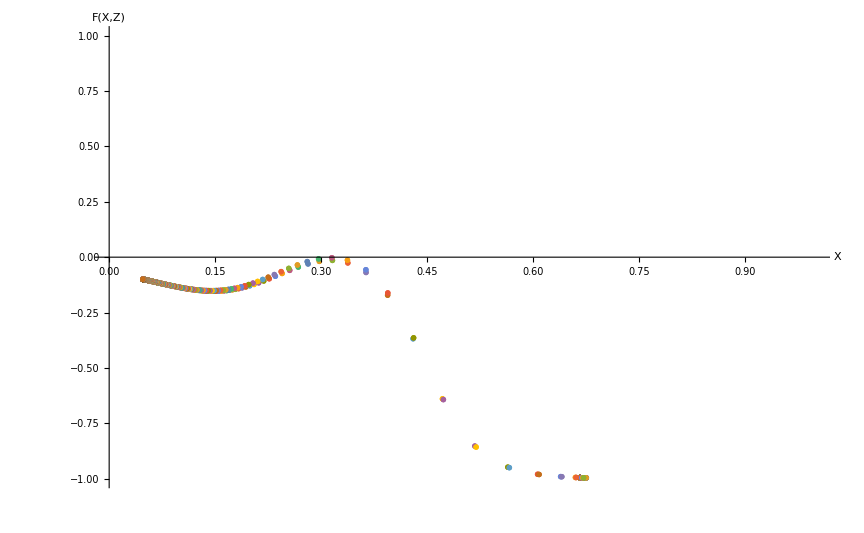

```mathematica
(*Plot X vs the remaining equation when Y' = 0*)
(*When F(X,Z) = 0, an Einstein point exists*)
EinsteinPlotLimitingCompactSpiral=ListPlot[EinsteinPointSolutionsLimitingCompactSpiral,PlotRange->{{0,1},{-1,1}},AxesLabel->{"X","F(X,Z)"}]
```

#### Plot the X-Y-Z Phase Space

```mathematica
(*Find the maximum value of K for this combination of X0 and Z0 such that Y0 is not imaginary*)
KMaxLimitingCompactSpiral=K/.Solve[Y0LimitingSpiral==0,K][[1]]
```

0.0361667

```mathematica
(*Solve trajLimitingCompact[K] for different values of K*)
```

```mathematica
solLimitingCompactSpiral[1]=trajLimitingCompactSpiral[0.01]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solLimitingCompactSpiral[2]=trajLimitingCompactSpiral[KDensityParametersClosed]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solLimitingCompactSpiral[3]=trajLimitingCompactSpiral[-.1]
```

NDSolve::mxst: Maximum number of 420165 steps reached at the point t == -2.89735.

{{X1→InterpolatingFunction[{{-2.89735, 100.}}, <>],Y1→InterpolatingFunction[{{-2.89735, 100.}}, <>],Z1→InterpolatingFunction[{{-2.89735, 100.}}, <>]}}

```mathematica
solLimitingCompactSpiral[4]=trajLimitingCompactSpiral[0.015]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solLimitingCompactSpiral[5]=trajLimitingCompactSpiral[-0.01]
```

NDSolve::mxst: Maximum number of 156680 steps reached at the point t == -6.00323.

{{X1→InterpolatingFunction[{{-6.00323, 100.}}, <>],Y1→InterpolatingFunction[{{-6.00323, 100.}}, <>],Z1→InterpolatingFunction[{{-6.00323, 100.}}, <>]}}

```mathematica
solLimitingCompactSpiral[6]=trajLimitingCompactSpiral[0.013]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the trajectories for the different values of K given above.*)
```

```mathematica
trajLimitingCompactXYZSpiral[1]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactSpiral[1],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCompactXYZSpiral[2]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactSpiral[2],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCompactXYZSpiral[3]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactSpiral[3],{t,-2.88,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCompactXYZSpiral[4]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactSpiral[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCompactXYZSpiral[5]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactSpiral[5],{t,-5.98,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCompactXYZSpiral[6]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactSpiral[6],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajLimitingCaseCompactSpiral=Table[trajLimitingCompactXYZSpiral[i],{i,1,6}];
```

```mathematica
(*Plot the Einstein fixed point*)
EinsteinFixedPointsLimitingCompactSpiral=ListPointPlot3D[{EinsteinPointLimitingCompactSpiral},PlotStyle->Black];
```

```mathematica
(*Solve theX-Y-Z system around the Einstein fixed point to plot the Closed Friedmann Separatrix (CFS)*)
CFSLimitingSolCompactSpiral=NDSolve[{deXt,deYt,deZt,X1[0]==EinsteinPointLimitingCompactSpiral[[1]],Y1[0]==0,Z1[0]==EinsteinPointLimitingCompactSpiral[[3]]},{X1,Y1,Z1},{t,-100,100}]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the CFS*)
CFSLimitingCompactSpiral=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.CFSLimitingSolCompactSpiral,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
(*Show the X-Y-Z phase space*)
Show[trajLimitingCaseCompactSpiral,EinsteinFixedPointsLimitingCompactSpiral,CFSLimitingCompactSpiral,AccnXYZSpiral,FPsXYZSpiral,CompactFPShowXYZSpiral,XYZCompactFormat]
```

-Graphics3D-

#### Plot the X-Z Projection

```mathematica
(*Plot one solution on the X-Z plane*)
trajLimitingCompactXZSpiral=ParametricPlot[Evaluate[{{Z1[t],X1[t]}}/.solLimitingCompactSpiral[3],{t,-2.89,100},PlotStyle -> {{Black, Thick,Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.03,0,.03,0},1]]],Arrow[x]};
```

```mathematica
(*Plot the Einstein fixed point on the X-Z plane*)
EinsteinFixedPointsLimitingCompactXZSpiral=ListPlot[{{EinsteinPointLimitingCompactSpiral[[3]],EinsteinPointLimitingCompactSpiral[[1]]}},PlotStyle->Black];
```

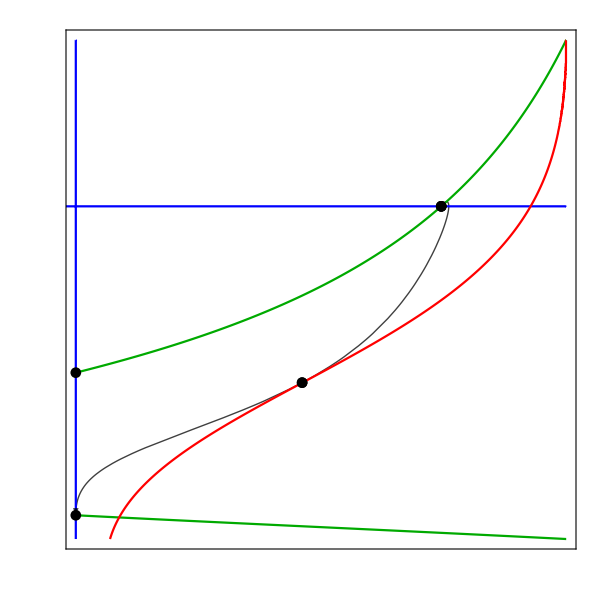

```mathematica
(*Show the X-Z phase space with the a'' = 0 (red), X' = 0 (green) and Z' = 0 (purple) curves*)
Show[trajLimitingCompactXZSpiral,XLineSpiral,ZLineSpiral,AccnXZSpiral,EinsteinFixedPointsLimitingCompactXZSpiral,FPsXZSpiral,CompactFPShowXZSpiral,XZCompactFormat]
```

### Two Einstein Fixed Points

#### Find the Einstein Fixed Points

```mathematica
(*Fix z0 using the density parameters*)
z0TwoEinsteinPointsSpiral=Ωm0*ℛ/(Ωx0*α);
```

```mathematica
(*Compactify z0*)
Z0TwoEinsteinPointsSpiral=z0TwoEinsteinPointsSpiral/(1+z0TwoEinsteinPointsSpiral)
```

0.0432077

```mathematica
(*Substitute Z0TwoEinsteinPoints into Y0 for this case*)
Y0TwoEinsteinPointsSpiral=Y0/.Z0->Z0TwoEinsteinPointsSpiral
```

(√(0.0483863-K))/(√(1.04839-K))

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajTwoEinsteinPointsCompactSpiral[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0TwoEinsteinPointsSpiral,Z1[0]==Z0TwoEinsteinPointsSpiral},{X1,Y1,Z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition (√(0.0483863-1. K))/(√(1.04839-1. K)) is not a number or a rectangular array of numbers.

NDSolve[{X1'[t]==-(3 (0.5 (1-X1[t])-X1[t]) (-0.05 (1-X1[t])+X1[t]) Y1[t])/(√(1-Y1[t]^2))-(1.5 (1-X1[t]) X1[t] Y1[t] Z1[t])/(√(1-Y1[t]^2) (1-Z1[t])),Y1'[t]==-Y1[t]^2 √(1-Y1[t]^2)-1/6 (1-Y1[t]^2)^(3/2) (-0.075-(0.35 X1[t])/(1-X1[t])-(3 X1[t]^2)/(1-X1[t])^2+Z1[t]/(1-Z1[t])),Z1'[t]==-(3 Y1[t] (1-Z1[t]) Z1[t])/(√(1-Y1[t]^2))+(1.5 X1[t] Y1[t] (1-Z1[t]) Z1[t])/((1-X1[t]) √(1-Y1[t]^2)),X1[0]==0.0909091,Y1[0]==(√(0.0483863-K))/(√(1.04839-K)),Z1[0]==0.0432077},{X1,Y1,Z1},{t,-100,100}]

```mathematica
(*Set-up tables of X1 and Z1 values to be used to find the X and Z value of the first Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
XTableSol1TwoEinsteinPointsCompactSpiral=Table[X1[i]/.trajTwoEinsteinPointsCompactSpiral[0],{i,-2,100,.01}];
ZTableSol1TwoEinsteinPointsCompactSpiral=Table[Z1[i]/.trajTwoEinsteinPointsCompactSpiral[0],{i,-2,100,.01}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol1TwoEinsteinPointsCompactSpiral=(ZTableSol1TwoEinsteinPointsCompactSpiral/(1-ZTableSol1TwoEinsteinPointsCompactSpiral))+(XTableSol1TwoEinsteinPointsCompactSpiral/(1-XTableSol1TwoEinsteinPointsCompactSpiral))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSol1TwoEinsteinPointsCompactSpiral/(1-XTableSol1TwoEinsteinPointsCompactSpiral))^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol1TwoEinsteinPointsCompact that is closest to zero. When EinsteinPlotValuesSol1TwoEinsteinPointsCompact = 0 (Y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints1CompactSpiral=Flatten[Nearest[EinsteinPlotValuesSol1TwoEinsteinPointsCompactSpiral,0]]
```

{0.0000558911}

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints1Compact in the EinsteinPlotValuesSol1TwoEinsteinPointsCompact*)
PositionNearestToZeroTwoEinsteinPoints1CompactSpiral=Flatten[Position[EinsteinPlotValuesSol1TwoEinsteinPointsCompactSpiral,NearestToZeroTwoEinsteinPoints1CompactSpiral]]
```

{4}

```mathematica
(*Find the Einstein point by finding the X and Z values in XTableSol1TwoEinsteinPointsCompact and ZTableSol1TwoEinsteinPointsCompact at PositionNearestToZeroTwoEinsteinPoints1Compact*)
EinsteinPoint1TwoEinsteinPointsCompactSpiral=Flatten[{XTableSol1TwoEinsteinPointsCompactSpiral[[PositionNearestToZeroTwoEinsteinPoints1CompactSpiral]],0,ZTableSol1TwoEinsteinPointsCompactSpiral[[PositionNearestToZeroTwoEinsteinPoints1CompactSpiral]]}]
```

{0.133696,0,0.16703}

```mathematica
(*Set-up tables of X1 and Z1 values to be used to find the X and Z value of the second Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
XTableSol2TwoEinsteinPointsCompactSpiral=Table[X1[i]/.trajTwoEinsteinPointsCompactSpiral[0],{i,-5.6,-3.2,.001}];
ZTableSol2TwoEinsteinPointsCompactSpiral=Table[Z1[i]/.trajTwoEinsteinPointsCompactSpiral[0],{i,-5.6,-3.2,.001}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol2TwoEinsteinPointsCompactSpiral=(ZTableSol2TwoEinsteinPointsCompactSpiral/(1-ZTableSol2TwoEinsteinPointsCompactSpiral))+(XTableSol2TwoEinsteinPointsCompactSpiral/(1-XTableSol2TwoEinsteinPointsCompactSpiral))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSol2TwoEinsteinPointsCompactSpiral/(1-XTableSol2TwoEinsteinPointsCompactSpiral))^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol2TwoEinsteinPointsCompact that is closest to zero. When EinsteinPlotValuesSol2TwoEinsteinPointsCompact = 0 (Y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints2CompactSpiral=Flatten[Nearest[EinsteinPlotValuesSol2TwoEinsteinPointsCompactSpiral,0]]
```

{-0.000631638}

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints2Compact in the EinsteinPlotValuesSol2TwoEinsteinPointsCompact array*)
PositionNearestToZeroTwoEinsteinPoints2CompactSpiral=Flatten[Position[EinsteinPlotValuesSol2TwoEinsteinPointsCompactSpiral,NearestToZeroTwoEinsteinPoints2CompactSpiral]]
```

{1901}

```mathematica
(*Find the Einstein point by finding the X and Z values in XTableSol2TwoEinsteinPointsCompact and ZTableSol2TwoEinsteinPointsCompact at PositionNearestToZeroTwoEinsteinPoints2Compact*)
EinsteinPoint2TwoEinsteinPointsCompactSpiral=Flatten[{XTableSol2TwoEinsteinPointsCompactSpiral[[PositionNearestToZeroTwoEinsteinPoints2CompactSpiral]],0,ZTableSol2TwoEinsteinPointsCompactSpiral[[PositionNearestToZeroTwoEinsteinPoints2CompactSpiral]]}]
```

{0.439491,0,0.686834}

```mathematica
(*Put the Einstein fixed points into a common variable name*)
EinsteinPointTwoEPtsCompactSpiral[1]=EinsteinPoint1TwoEinsteinPointsCompactSpiral;
EinsteinPointTwoEPtsCompactSpiral[2]=EinsteinPoint2TwoEinsteinPointsCompactSpiral;
```

```mathematica
(*Put the Einstein fixed points into a table*)
EinsteinPointsTwoEPtsCompactSpiral=Table[EinsteinPointTwoEPtsCompactSpiral[i],{i,1,2}];
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each Einstein fixed point*)
EinsteinPointTableTwoEinsteinPointsCompactSpiral=Table[{EinsteinPointsTwoEPtsCompactSpiral[[i]]//MatrixForm,Simplify[JCompactXYZSpiral/.{X->EinsteinPointsTwoEPtsCompactSpiral[[i,1]],Y->EinsteinPointsTwoEPtsCompactSpiral[[i,2]],Z->EinsteinPointsTwoEPtsCompactSpiral[[i,3]]}]//MatrixForm,Eigenvalues[JCompactXYZSpiral/.{X->EinsteinPointsTwoEPtsCompactSpiral[[i,1]],Y->EinsteinPointsTwoEPtsCompactSpiral[[i,2]],Z->EinsteinPointsTwoEPtsCompactSpiral[[i,3]]}]//MatrixForm,Eigenvectors[JCompactXYZSpiral/.{X->EinsteinPointsTwoEPtsCompactSpiral[[i,1]],Y->EinsteinPointsTwoEPtsCompactSpiral[[i,2]],Z->EinsteinPointsTwoEPtsCompactSpiral[[i,3]]}]//MatrixForm},{i,1,2}];
```

```mathematica
(*Use TableForm to display the Einstein fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableTwoEinsteinPointsCompactSpiral=TableForm[EinsteinPointTableTwoEinsteinPointsCompactSpiral,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.133696
0
0.16703) | (0. | -0.116032 | 0.
0.283367 | 0. | -0.240209
0. | -0.385185 | 0.) | (0.244224
-0.244224
8.09874×10^-18) | (0.246556 | -0.518949 | 0.818476
-0.246556 | -0.518949 | -0.818476
0.646628 | 1.42334×10^-16 | 0.762806)
(0.439491
0
0.686834) | (0. | -0.613844 | 0.
2.68142 | 0. | -1.69942
0. | -0.3923 | 0.) | (4.85106×10^-17+0.989593 ⅈ
4.85106×10^-17-0.989593 ⅈ
-7.80833×10^-17+0. ⅈ) | (2.11533×10^-16-0.49954 ⅈ | -0.80532+0. ⅈ | 1.41324×10^-16-0.319249 ⅈ
2.11533×10^-16+0.49954 ⅈ | -0.80532+0. ⅈ | 1.41324×10^-16+0.319249 ⅈ
0.535318+0. ⅈ | 1.21199×10^-16+0. ⅈ | 0.84465+0. ⅈ)

```mathematica
(*Set-up tables of all X1 and Z1 values*)

XTableSolTwoEinsteinPointsFullCompactSpiral=Table[X1[i]/.trajTwoEinsteinPointsCompactSpiral[0],{i,-100,100,.1}];
ZTableSolTwoEinsteinPointsFullCompactSpiral=Table[Z1[i]/.trajTwoEinsteinPointsCompactSpiral[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0*)
EinsteinPlotValuesSolTwoEinsteinPointsFullXZSpiral=(ZTableSolTwoEinsteinPointsFullCompactSpiral/(1-ZTableSolTwoEinsteinPointsFullCompactSpiral))+(XTableSolTwoEinsteinPointsFullCompactSpiral/(1-XTableSolTwoEinsteinPointsFullCompactSpiral))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSolTwoEinsteinPointsFullCompactSpiral/(1-XTableSolTwoEinsteinPointsFullCompactSpiral))^2;
```

```mathematica
(*Compactify EinsteinPlotValuesSolTwoEinsteinPointsFullXZ*)
EinsteinPlotValuesSolTwoEinsteinPointsFullCompactSpiral=EinsteinPlotValuesSolTwoEinsteinPointsFullXZSpiral/Sqrt[1+EinsteinPlotValuesSolTwoEinsteinPointsFullXZSpiral^2];
```

```mathematica
(*Merge the XTableSolTwoEinsteinPointsFullCompact values and the EinsteinPlotValuesSolTwoEinsteinPointsFullCompact values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsTwoEinsteinPointsCompactSpiral=MapThread[h,{XTableSolTwoEinsteinPointsFullCompactSpiral,EinsteinPlotValuesSolTwoEinsteinPointsFullCompactSpiral}];
```

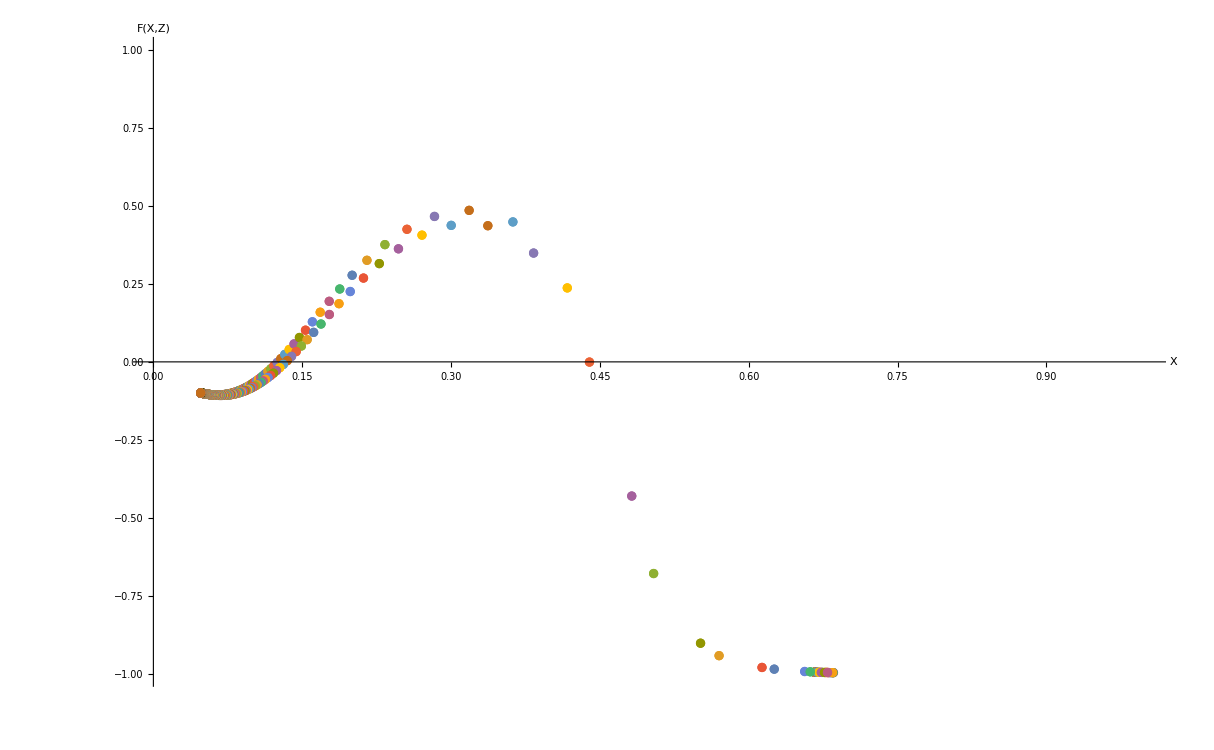

```mathematica
(*Plot X vs the remaining equation when Y' = 0*)
(*When F(X,Z) = 0, an Einstein point exists*)
EinsteinPlotTwoEinsteinPointsCompactSpiral=ListPlot[EinsteinPointSolutionsTwoEinsteinPointsCompactSpiral,PlotRange->{{0,1},{-1,1}},AxesLabel->{"X","F(X,Z)"}]
```

#### Plot the X-Y-Z Phase Space

```mathematica
(*Find the maximum value of K for this combination of X0 and Z0 so that Y0 is not imaginary*)
KMaxTwoEinsteinPointsCompactSpiral=K/.Flatten[Solve[Y0TwoEinsteinPointsSpiral==0,K]]
```

0.0483863

```mathematica
(*Solve trajTwoEinsteinPointsCompact[K] for different values of K*)
```

```mathematica
solTwoEinsteinPointsCompactSpiral[1]=trajTwoEinsteinPointsCompactSpiral[-0.02]
```

NDSolve::mxst: Maximum number of 297156 steps reached at the point t == -4.23303.

{{X1→InterpolatingFunction[{{-4.23303, 100.}}, <>],Y1→InterpolatingFunction[{{-4.23303, 100.}}, <>],Z1→InterpolatingFunction[{{-4.23303, 100.}}, <>]}}

```mathematica
solTwoEinsteinPointsCompactSpiral[2]=trajTwoEinsteinPointsCompactSpiral[0.005]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsCompactSpiral[3]=trajTwoEinsteinPointsCompactSpiral[-0.1]
```

NDSolve::mxst: Maximum number of 529197 steps reached at the point t == -2.71877.

{{X1→InterpolatingFunction[{{-2.71877, 100.}}, <>],Y1→InterpolatingFunction[{{-2.71877, 100.}}, <>],Z1→InterpolatingFunction[{{-2.71877, 100.}}, <>]}}

```mathematica
solTwoEinsteinPointsCompactSpiral[4]=trajTwoEinsteinPointsCompactSpiral[KMaxTwoEinsteinPointsCompactSpiral]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsCompactSpiral[5]=trajTwoEinsteinPointsCompactSpiral[0.03]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the trajectories for the different values of K given above*)
```

```mathematica
trajTwoEinsteinPointsCompactXYZSpiral[1]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactSpiral[1],{t,-4.21,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsCompactXYZSpiral[2]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactSpiral[2],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsCompactXYZSpiral[3]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactSpiral[3],{t,-2.68,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsCompactXYZSpiral[4]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactSpiral[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
trajTwoEinsteinPointsCompactXYZSpiral[5]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactSpiral[5],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
(*Solve the X-Y-Z system using the centre Einstein fixed point for X0 and Z0 to plot a cyclic trajectory*)
CyclicTrajTwoEinsteinPointsCompactSpiral=NDSolve[{deXt,deYt,deZt,X1[0]==EinsteinPoint2TwoEinsteinPointsCompactSpiral[[1]],Y1[0]==0.2,Z1[0]==EinsteinPoint2TwoEinsteinPointsCompactSpiral[[3]]},{X1,Y1,Z1},{t,-100,100}];
```

```mathematica
(*Plot the cyclic trajectory*)
trajTwoEinsteinPointsCompactXYZSpiral[6]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.CyclicTrajTwoEinsteinPointsCompactSpiral,{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajTwoEinsteinPointsCaseCompactSpiral=Table[trajTwoEinsteinPointsCompactXYZSpiral[i],{i,1,6}];
```

```mathematica
(*Plot the Einstein fixed points*)
EinsteinFixedPointsTwoEinsteinPointsCompactSpiral=ListPointPlot3D[{EinsteinPoint1TwoEinsteinPointsCompactSpiral,EinsteinPoint2TwoEinsteinPointsCompactSpiral},PlotStyle->Black];
```

```mathematica
(*Solve the X-Y-Z system around the Einstein fixed point to plot the Closed Friedmann Separatrix (CFS)*)
CFSTwoEinsteinPointsSolCompactSpiral=NDSolve[{deXt,deYt,deZt,X1[0]==EinsteinPoint1TwoEinsteinPointsCompactSpiral[[1]],Y1[0]==-0.0005,Z1[0]==EinsteinPoint1TwoEinsteinPointsCompactSpiral[[3]]},{X1,Y1,Z1},{t,-100,100}]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the CFS*)
CFSTwoEinsteinPointsCompactSpiral=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.CFSTwoEinsteinPointsSolCompactSpiral,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Show the X-Y-Z phase space*)
Show[trajTwoEinsteinPointsCaseCompactSpiral,CFSTwoEinsteinPointsCompactSpiral,EinsteinFixedPointsTwoEinsteinPointsCompactSpiral,AccnXYZSpiral,FPsXYZSpiral,CompactFPShowXYZSpiral,XYZCompactFormat]
```

-Graphics3D-

#### Plot the X-Z Projection

```mathematica
(*Plot one solution on the X-Z plane*)
trajTwoEinsteinPointsCompactXZSpiral=ParametricPlot[Evaluate[{{Z1[t],X1[t]}}/.solTwoEinsteinPointsCompactSpiral[1],{t,-4.22,100},PlotStyle -> {{Black,Thick, Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.03,.03,0},1]]],Arrow[x]};
```

```mathematica
(*Plot the Einstein fixed points on the X-Z plane*)
EinsteinFixedPointsTwoEinsteinPointsCompactXZSpiral=ListPlot[{{EinsteinPoint1TwoEinsteinPointsCompactSpiral[[3]],EinsteinPoint1TwoEinsteinPointsCompactSpiral[[1]]},{EinsteinPoint2TwoEinsteinPointsCompactSpiral[[3]],EinsteinPoint2TwoEinsteinPointsCompactSpiral[[1]]}},PlotStyle->Black];
```

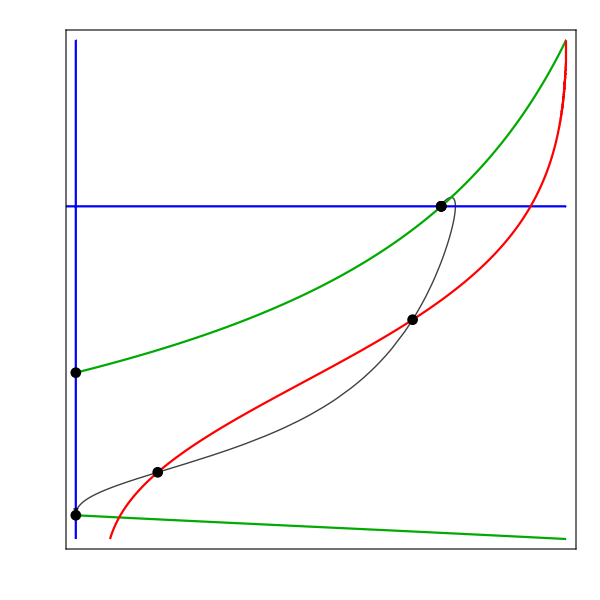

```mathematica
(*Show the X-Z phase space with the a'' = 0 (red), X' = 0 (green) and Z' = 0 (purple) curves*)
Show[trajTwoEinsteinPointsCompactXZSpiral,XLineSpiral,ZLineSpiral,AccnXZSpiral,EinsteinFixedPointsTwoEinsteinPointsCompactXZSpiral,FPsXZSpiral,CompactFPShowXZSpiral,XZCompactFormat]
```

### No Einstein Fixed Points

#### Plot to show there are no Einstein fixed points

```mathematica
(*Fix z0 such that there are no Einstein fixed points on the surface*)
z0NoEinsteinPointsSpiral=0.005;
```

```mathematica
(*Compactify z0*)
Z0NoEinsteinPointsSpiral=z0NoEinsteinPointsSpiral/(1+z0NoEinsteinPointsSpiral)
```

0.00497512

```mathematica
(*Substitute Z0NoEinsteinPoints into Y0 for this case*)
Y0NoEinsteinPointsSpiral=Y0/.Z0->Z0NoEinsteinPointsSpiral
```

(√(0.035-K))/(√(1.035-K))

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajNoEinsteinPointsCompactSpiral[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0NoEinsteinPointsSpiral,Z1[0]==Z0NoEinsteinPointsSpiral},{X1,Y1,Z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition (√(0.035-1. K))/(√(1.035-1. K)) is not a number or a rectangular array of numbers.

NDSolve[{X1'[t]==-(3 (0.5 (1-X1[t])-X1[t]) (-0.05 (1-X1[t])+X1[t]) Y1[t])/(√(1-Y1[t]^2))-(1.5 (1-X1[t]) X1[t] Y1[t] Z1[t])/(√(1-Y1[t]^2) (1-Z1[t])),Y1'[t]==-Y1[t]^2 √(1-Y1[t]^2)-1/6 (1-Y1[t]^2)^(3/2) (-0.075-(0.35 X1[t])/(1-X1[t])-(3 X1[t]^2)/(1-X1[t])^2+Z1[t]/(1-Z1[t])),Z1'[t]==-(3 Y1[t] (1-Z1[t]) Z1[t])/(√(1-Y1[t]^2))+(1.5 X1[t] Y1[t] (1-Z1[t]) Z1[t])/((1-X1[t]) √(1-Y1[t]^2)),X1[0]==0.0909091,Y1[0]==(√(0.035-K))/(√(1.035-K)),Z1[0]==0.00497512},{X1,Y1,Z1},{t,-100,100}]

```mathematica
(*Set-up tables of all X1 and Z1 values*)
XTableSolNoEinsteinPointsFullCompactSpiral=Table[X1[i]/.trajNoEinsteinPointsCompactSpiral[0],{i,-100,100,.1}];
ZTableSolNoEinsteinPointsFullCompactSpiral=Table[Z1[i]/.trajNoEinsteinPointsCompactSpiral[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0*)
EinsteinPlotValuesSolNoEinsteinPointsFullCompactSpiral=(ZTableSolNoEinsteinPointsFullCompactSpiral/(1-ZTableSolNoEinsteinPointsFullCompactSpiral))+(XTableSolNoEinsteinPointsFullCompactSpiral/(1-XTableSolNoEinsteinPointsFullCompactSpiral))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSolNoEinsteinPointsFullCompactSpiral/(1-XTableSolNoEinsteinPointsFullCompactSpiral))^2;
```

```mathematica
(*Compactify EinsteinPlotValuesSolNoEinsteinPointsFullCompact*)
EinsteinPlotValuesSolNoEinsteinPointsFullXZSpiral=EinsteinPlotValuesSolNoEinsteinPointsFullCompactSpiral/Sqrt[1+EinsteinPlotValuesSolNoEinsteinPointsFullCompactSpiral^2];
```

```mathematica
(*Merge the XTableSolNoEinsteinPointsFullCompact values and the EinsteinPlotValuesSolNoEinsteinPointsFullXZ values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsNoEinsteinPointsCompactSpiral=MapThread[h,{XTableSolNoEinsteinPointsFullCompactSpiral,EinsteinPlotValuesSolNoEinsteinPointsFullXZSpiral}];
```

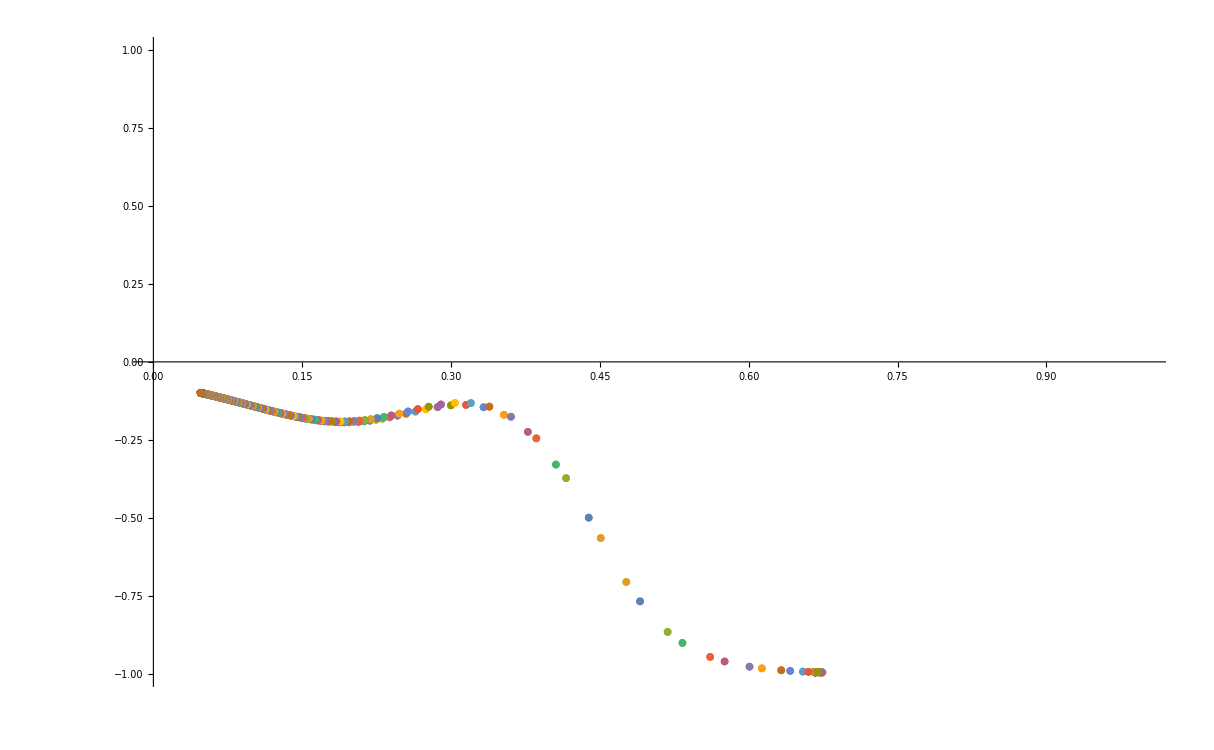

```mathematica
(*Plot X vs the remaining equation when Y' = 0*)
(*Here, F(X,Z) is never zero, so there are no Einstein fixed points*)
EinsteinPlotNoEinsteinPointsCompactSpiral=ListPlot[EinsteinPointSolutionsNoEinsteinPointsCompactSpiral,PlotRange->{{0,1},{-1,1}}]
```

#### Plot the X-Y-Z Phase Space

```mathematica
(*Find the maximum value of K for this combination of X0 and Z0 such that Y0 is not imaginary*)
KMaxNoEinsteinPointsCompactSpiral=K/.Solve[Y0NoEinsteinPointsSpiral==0,K][[1]]
```

0.035

```mathematica
(*Solve trajNoEinsteinPointsCompact[K] for different values of K*)
```

```mathematica
solNoEinsteinPointsCompactSpiral[1]=trajNoEinsteinPointsCompactSpiral[-.01]
```

NDSolve::mxst: Maximum number of 149705 steps reached at the point t == -6.26638.

{{X1→InterpolatingFunction[{{-6.26638, 100.}}, <>],Y1→InterpolatingFunction[{{-6.26638, 100.}}, <>],Z1→InterpolatingFunction[{{-6.26638, 100.}}, <>]}}

```mathematica
solNoEinsteinPointsCompactSpiral[2]=trajNoEinsteinPointsCompactSpiral[0.006]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solNoEinsteinPointsCompactSpiral[3]=trajNoEinsteinPointsCompactSpiral[-.1]
```

NDSolve::mxst: Maximum number of 413252 steps reached at the point t == -2.93878.

{{X1→InterpolatingFunction[{{-2.93878, 100.}}, <>],Y1→InterpolatingFunction[{{-2.93878, 100.}}, <>],Z1→InterpolatingFunction[{{-2.93878, 100.}}, <>]}}

```mathematica
solNoEinsteinPointsCompactSpiral[4]=trajNoEinsteinPointsCompactSpiral[0.001]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solNoEinsteinPointsCompactSpiral[5]=trajNoEinsteinPointsCompactSpiral[0.015]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solNoEinsteinPointsCompactSpiral[6]=trajNoEinsteinPointsCompactSpiral[0.009]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the trajectories for the different values of K given above.*)
```

```mathematica
trajNoEinsteinPointsCompactXYZSpiral[1]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactSpiral[1],{t,-6.26,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsCompactXYZSpiral[2]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactSpiral[2],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsCompactXYZSpiral[3]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactSpiral[3],{t,-2.89,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsCompactXYZSpiral[4]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactSpiral[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsCompactXYZSpiral[5]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactSpiral[5],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsCompactXYZSpiral[6]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactSpiral[6],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajNoEinsteinPointsPlotsCompactSpiral=Table[trajNoEinsteinPointsCompactXYZSpiral[i],{i,1,6}];
```

```mathematica
(*Show the X-Y-Z phase space*)
Show[trajNoEinsteinPointsPlotsCompactSpiral,AccnXYZSpiral,FPsXYZSpiral,CompactFPShowXYZSpiral,XYZCompactFormat]
```

-Graphics3D-

#### Plot the X-Z Projection

```mathematica
(*Plot one solution on the X-Z plane*)
trajNoEinsteinPointsCompactXZSpiral=ParametricPlot[Evaluate[{{Z1[t],X1[t]}}/.solNoEinsteinPointsCompactSpiral[1],{t,-6.26,100},PlotStyle -> {{Black,Thick, Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,0,.03,0,.03,0},1]]],Arrow[x]};
```

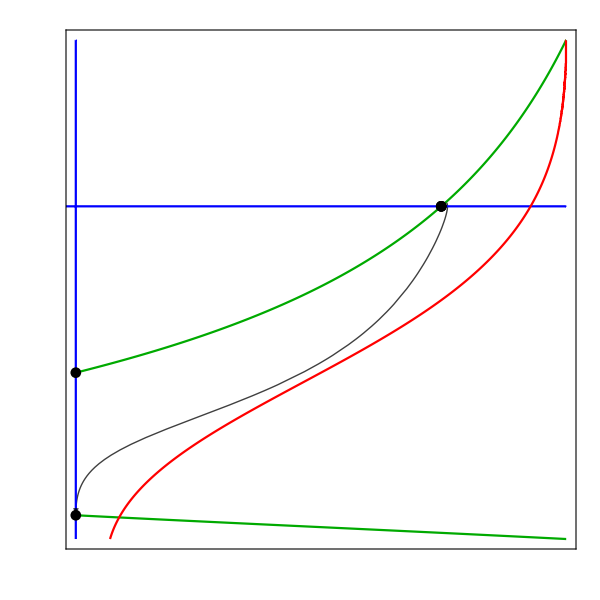

```mathematica
(*Show the X-Z phase space with the a'' = 0 (red), X' = 0 (green) and Z' = 0 (purple) curves*)
Show[trajNoEinsteinPointsCompactXZSpiral,XLineSpiral,ZLineSpiral,AccnXZSpiral,FPsXZSpiral,CompactFPShowXZSpiral,XZCompactFormat]
```

## Investigate system when ℛ = 10^(-120)

### Set-up

```mathematica
(*Clear variables*)
Clear[q,ϵ,ℛ,wx]
```

```mathematica
(*Set parameter values*)
q=1.5;
ϵ=-1;
ℛ=10^(-120);
wx=-1+2*ℛ;
```

```mathematica
(*Define Ωx0 and Ωm0 using data from Planck 2018*)
Ωx0=0.6889;
Ωm0=0.3111;
```

```mathematica
(*Set a value for α, which sets the value of the low energy cosmological constant*)
α=0.5;
```

```mathematica
(*Define the initial conditions, where a0 = 1 and K is defined as k/ρ* *)

x0=ℛ/α;
y0=Sqrt[x0/3+Z0/(3*(1-Z0))-K];
```

```mathematica
(*Compactify the initial conditions*)

X0=x0/(1+x0);
Y0=y0/Sqrt[1+y0^2];
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y in terms of time, t*)
deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*(X1[t]-ℛ*(1-X1[t]))*((1+wx)*(1-X1[t])+ϵ*X1[t])-q*X1[t]*(1-X1[t])*(Z1[t]/(1-Z1[t]))*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((Z1[t]/(1-Z1[t]))+(X1[t]/(1-X1[t]))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X1[t]^2/((1-X1[t])^2))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2))) + q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
```

### Find the value of z0 to give the limiting case

```mathematica
(*Fix z0 using the density parameters*)
z0RealisticℛSpiral=Ωm0*ℛ/(Ωx0*α)
```

9.03179×10^-121

```mathematica
(*Compactify z0*)
Z0RealisticℛSpiral=z0RealisticℛSpiral/(1+z0RealisticℛSpiral)
```

9.03179×10^-121

```mathematica
(*Substitute Z0Realisticℛ into Y0 for this case*)
Y0RealisticℛSpiral=Y0/.Z0->Z0RealisticℛSpiral
```

(√(9.67726×10^-121-K))/(√(1.-K))

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajRealisticℛSpiral[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0RealisticℛSpiral,Z1[0]==Z0RealisticℛSpiral},{X1,Y1,Z1},{t,-100,100}];
```

NDSolve::ndinnt: Initial condition (√(9.67726×10^-121-1. K))/(√(1.-1. K)) is not a number or a rectangular array of numbers.

```mathematica
(*Set-up tables of all X1 and Z1 values*)
XTableRealisticℛSpiral=Table[X1[i]/.trajRealisticℛSpiral[0],{i,-100,100,.1}];
ZTableRealisticℛSpiral=Table[Z1[i]/.trajRealisticℛSpiral[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0*)
EinsteinPlotValuesRealisticℛSpiral=(ZTableRealisticℛSpiral/(1-ZTableRealisticℛSpiral))+(XTableRealisticℛSpiral/(1-XTableRealisticℛSpiral))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableRealisticℛSpiral/(1-XTableRealisticℛSpiral))^2;
```

```mathematica
(*Compactify EinsteinPlotValuesRealisticℛ*)
EinsteinPlotRealisticℛCompactSpiral=EinsteinPlotValuesRealisticℛSpiral/Sqrt[1+EinsteinPlotValuesRealisticℛSpiral^2];
```

```mathematica
(*Find the maximum value of EinsteinPlotRealisticℛCompact*)
(*As EinsteinPlotRealisticℛCompact is always less than zero there are no Einstein points when z0 is defined using the density parameters*)
Max[EinsteinPlotRealisticℛCompactSpiral]
```

-3.09682×10^-120

## Non-spiral Repellor Case

This is the case where 0 < q ≤ 0.889947  and  5.18699 ≤ q < 6.

## Plot the full x-z and x-y-z phase spaces

### Non-Compact x - z Phase Space

```mathematica
(*Clear variables*)
Clear[q,ϵ,ℛ,wx]
```

```mathematica
(*Load MaTeX to typeset axis labels using LaTeX*)
<<MaTeX`
```

```mathematica
(*Define a format style for the x-z phase spaces*)
xzFormat={Frame->{True},FrameLabel->{MaTeX["z",FontSize->24],Rotate[MaTeX["x",FontSize->24],300]},FrameTicks->{{Table[{x,MaTeX[x,"DisplayStyle"->False,FontSize->24]},{x,1Range[-1,6]}],None},{Table[{z,MaTeX[z,"DisplayStyle"->False,FontSize->24]},{z,5Range[0,20]}],None}},ImageSize->{600,600},PlotRangePadding->{0.15,0}};
```

```mathematica
(*Set parameter values such that wx > -0.25 and only the repellor and attractor fixed points satisfy z >= 0*)
wx=-0.5;
q=0.8;
ϵ=-1;
ℛ=0.05;
```

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, and dark matter, z*)
dex:=x'=-3*(x-ℛ)*(1+wx+ϵ*x)-q*x*z
dez:=z'=-3*z + q*x*z
```

```mathematica
(*Define the system of differential equations for the dark energy, x, and dark matter, z, in terms of a time variable*)
dext:=x1'[t]==-3*(x1[t]-ℛ)*(1+wx+ϵ*x1[t])-q*x1[t]*z1[t]
dezt:=z1'[t]==-3*z1[t] + q*x1[t]*z1[t]
```

```mathematica
(*Find the fixed points of the system*)
FPsxzRepellor=Solve[{dez==0,dex==0},{z,x}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{z→0.,x→0.05},{z→0.,x→0.5},{z→12.025,x→3.75}}

```mathematica
(*Extract the values of the fixed points and put them into one variable name*)
FPxzRepellor[1]={z/.FPsxzRepellor[[1,1]],x/.FPsxzRepellor[[1,2]]};
FPxzRepellor[2]={z/.FPsxzRepellor[[2,1]],x/.FPsxzRepellor[[2,2]]};
FPxzRepellor[3]={z/.FPsxzRepellor[[3,1]],x/.FPsxzRepellor[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPxzTableRepellor=Table[FPxzRepellor[i],{i,1,3}];
```

```mathematica
(*Find the 2D Jacobian matrix. D[] differentiates each expression*)
JxzRepellor=Simplify[{{D[dez,z],D[dez,x]}, {D[dex,z],D[dex,x]}}];
JxzRepellor//MatrixForm
```

(-3+0.8 x | 0.8 z
-0.8 x | 6. (-0.275+x-0.133333 z))

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableRepellor=Table[{FPxzTableRepellor[[i]]//MatrixForm,Simplify[JxzRepellor/.{z->FPxzTableRepellor[[i,1]],x->FPxzTableRepellor[[i,2]]}]//MatrixForm,Eigenvalues[JxzRepellor/.{z->FPxzTableRepellor[[i,1]],x->FPxzTableRepellor[[i,2]]}]//MatrixForm,Eigenvectors[JxzRepellor/.{z->FPxzTableRepellor[[i,1]],x->FPxzTableRepellor[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTablexzRepellor=TableForm[FPTableRepellor,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.
0.05) | (-2.96 | 0.
-0.04 | -1.35) | (-2.96
-1.35) | (0.999692 | 0.0248371
0. | 1.)
(0.
0.5) | (-2.6 | 0.
-0.4 | 1.35) | (-2.6
1.35) | (0.994912 | 0.100751
0. | 1.)
(12.025
3.75) | (0. | 9.62
-3. | 11.23) | (7.24847
3.98153) | (-0.798664 | -0.601777
-0.923988 | -0.382421)

```mathematica
(*Plot the fixed points*)
FPsxzRepellor=ListPlot[FPxzTableRepellor,PlotStyle->Black];
```

```mathematica
(*Plot the phase space for the dark energy and dark matter*)
PhaseSpacexzRepellor=StreamPlot[{dez,dex},{z,0,20},{x,-1,6}];
```

```mathematica
(*Plot the curves where z' = 0*)
zLineRepellor=ContourPlot[-3*z + q*x*z==0,{z,-.1,20},{x,-1,6},ContourStyle->Blue,PlotPoints->300];
```

```mathematica
(*Plot the curves where x' = 0*)
xLineRepellor=ContourPlot[-3*(x-ℛ)*(1+wx+ϵ*x)-q*x*z==0,{z,-.1,20},{x,-1,6},ContourStyle->Darker[Green],PlotPoints->300];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
AccnxzRepellor=ContourPlot[z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2==0,{z,0,20},{x,-1,6},ContourStyle->Red,PlotPoints->300];
```

```mathematica
(*Solve the z-x system around the saddle fixed point to plot the separatrix between the repellor and saddel fixed point*)
SeparatrixRepellor=NDSolve[{dezt,dext,z1[0]==0.0001,x1[0]==0.5},{z1,x1},{t,-100,100}]
```

{{z1→InterpolatingFunction[…],x1→InterpolatingFunction[…]}}

```mathematica
(*Plot the separatrix*)
SeparatrixPlotRepellor=ParametricPlot[Evaluate[{{z1[t],x1[t]}}/.SeparatrixRepellor,{t,-100,2.84},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->{{0,7},{-1,4}}];
```

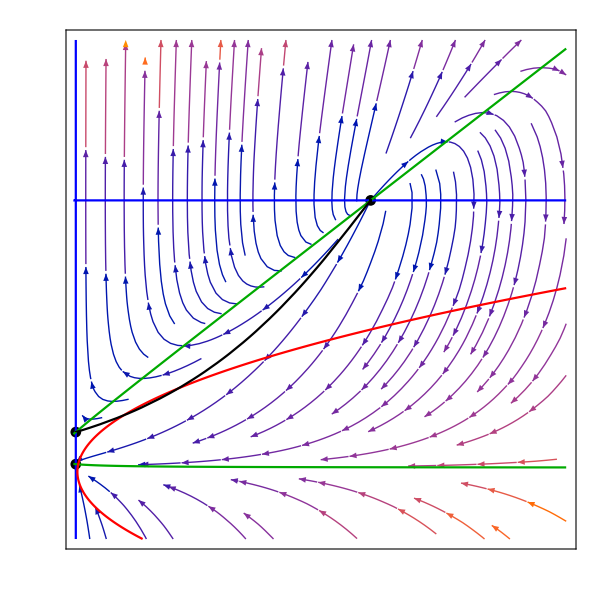

```mathematica
(*Show the plots of the phase space and its components together*)
Show[PhaseSpacexzRepellor,FPsxzRepellor,zLineRepellor,xLineRepellor,AccnxzRepellor,SeparatrixPlotRepellor,xzFormat,PlotRange->{{0,20},{-1,6}}]
```

### Non-Compact x - y - z Phase Space

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, dark matter, z, and the Hubble parameter, y*)
dex:=x'=-3*y*(x-ℛ)*(1+wx+ϵ*x)-q*x*y*z
dey:=y'=-y^2-(1/6)*(z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2) 
dez:=z'=-3*y*z + q*x*y*z
```

```mathematica
(*Find the fixed points of the system*)
FPsRepellor=Solve[{dex==0,dey==0,dez==0},{x,y,z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0.,z→0.025 (3.+14. x+120. x^2)},{x→0.05,y→-0.129099,z→0.},{x→0.05,y→0.129099,z→0.},{x→0.5,y→-0.408248,z→0.},{x→0.5,y→0.408248,z→0.},{x→3.75,y→-2.29311,z→12.025},{x→3.75,y→2.29311,z→12.025}}

```mathematica
(*Extract the values for the fixed points and put them into a common variable name*)
FPRepellor[1]={x,y/.FPsRepellor[[1,1]],z/.FPsRepellor[[1,2]]};
FPRepellor[2]={x/.FPsRepellor[[2,1]],y/.FPsRepellor[[2,2]],z/.FPsRepellor[[2,3]]};
FPRepellor[3]={x/.FPsRepellor[[3,1]],y/.FPsRepellor[[3,2]],z/.FPsRepellor[[3,3]]};
FPRepellor[4]={x/.FPsRepellor[[6,1]],y/.FPsRepellor[[6,2]],z/.FPsRepellor[[6,3]]};
FPRepellor[5]={x/.FPsRepellor[[7,1]],y/.FPsRepellor[[7,2]],z/.FPsRepellor[[7,3]]};
FPRepellor[6]={x/.FPsRepellor[[4,1]],y/.FPsRepellor[[4,2]],z/.FPsRepellor[[4,3]]};
FPRepellor[7]={x/.FPsRepellor[[5,1]],y/.FPsRepellor[[5,2]],z/.FPsRepellor[[5,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPsRepellor=Table[FPRepellor[i],{i,1,7}];
```

```mathematica
(*Find the 3D Jacobian matrix. D[] differentiates each expression*)
JxyzRepellor=Simplify[{{D[dex,x],D[dex,y],D[dex,z]}, {D[dey,x],D[dey,y],D[dey,z]},{D[dez,x],D[dez,y],D[dez,z]}}];
JxyzRepellor//MatrixForm
```

(y (-1.65+6. x-0.8 z) | 3. (0.025+x^2+x (-0.55-0.266667 z)) | -0.8 x y
0.0583333+x | -2 y | -1/6
0.8 y z | (-3+0.8 x) z | (-3+0.8 x) y)

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableRepellor=Table[{FPsRepellor[[i]]//MatrixForm,Simplify[JxyzRepellor/.{x->FPsRepellor[[i,1]],y->FPsRepellor[[i,2]],z->FPsRepellor[[i,3]]}]//MatrixForm,Eigenvalues[JxyzRepellor/.{x->FPsRepellor[[i,1]],y->FPsRepellor[[i,2]],z->FPsRepellor[[i,3]]}]//MatrixForm,Eigenvectors[JxyzRepellor/.{x->FPsRepellor[[i,1]],y->FPsRepellor[[i,2]],z->FPsRepellor[[i,3]]}]//MatrixForm},{i,1,7}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableRepellor=TableForm[FPTableRepellor,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(x
0.
0.025 (3.+14. x+120. x^2)) | (0. | 0.075-1.71 x+2.72 x^2-2.4 x^3 | 0.
0.0583333+x | 0. | -1/6
0. | -0.225-0.99 x-8.72 x^2+2.4 x^3 | 0.) | (0
-√(0.041875+0.14025 x-0.098 x^2+2.18 x^3-2.4 x^4)
√(0.041875+0.14025 x-0.098 x^2+2.18 x^3-2.4 x^4)) | (0.166667/(0.0583333+x) | 0 | 1.
-(1. (-0.00182292+0.0103125 x+0.646389 x^2-1.075 x^3+1. x^4))/((0.0583333+x) (-0.09375-0.4125 x-3.63333 x^2+1. x^3)) | -(0.416667 √(0.041875+0.14025 x-0.098 x^2+2.18 x^3-2.4 x^4))/(-0.09375-0.4125 x-3.63333 x^2+1. x^3) | 1.
-(1. (-0.00182292+0.0103125 x+0.646389 x^2-1.075 x^3+1. x^4))/((0.0583333+x) (-0.09375-0.4125 x-3.63333 x^2+1. x^3)) | (0.416667 √(0.041875+0.14025 x-0.098 x^2+2.18 x^3-2.4 x^4))/(-0.09375-0.4125 x-3.63333 x^2+1. x^3) | 1.)
(0.05
-0.129099
0.) | (0.174284 | 2.08167×10^-17 | 0.00516398
0.108333 | 0.258199 | -1/6
0. | 0. | 0.382134) | (0.382134
0.258199
0.174284) | (0.0149789 | -0.797677 | 0.602899
-1.15126×10^-16 | -1. | 0.
-0.612372 | 0.790569 | 0.)
(0.05
0.129099
0.) | (-0.174284 | 2.08167×10^-17 | -0.00516398
0.108333 | -0.258199 | -1/6
0. | 0. | -0.382134) | (-0.382134
-0.258199
-0.174284) | (0.0149789 | 0.797677 | 0.602899
-1.15126×10^-16 | 1. | 0.
0.612372 | 0.790569 | 0.)
(3.75
-2.29311
12.025) | (-25.7516 | 5.32907×10^-15 | 6.87932
3.80833 | 4.58621 | -1/6
-22.0597 | 0. | 0.) | (-16.6215
-9.13007
4.58621) | (0.598684 | -0.101263 | 0.794559
0.380708 | -0.0945268 | 0.919851
-2.2305×10^-17 | 1. | -7.59785×10^-16)
(3.75
2.29311
12.025) | (25.7516 | 5.32907×10^-15 | -6.87932
3.80833 | -4.58621 | -1/6
22.0597 | 0. | 0.) | (16.6215
9.13007
-4.58621) | (-0.598684 | -0.101263 | -0.794559
0.380708 | 0.0945268 | 0.919851
-2.2305×10^-17 | -1. | -7.59785×10^-16)
(0.5
-0.408248
0.) | (-0.551135 | 1.66533×10^-16 | 0.163299
0.558333 | 0.816497 | -1/6
0. | 0. | 1.06145) | (1.06145
0.816497
-0.551135) | (0.0919692 | -0.408316 | 0.908196
-1.7255×10^-16 | -1. | 0.
-0.92582 | 0.377964 | 0.)
(0.5
0.408248
0.) | (0.551135 | 1.66533×10^-16 | -0.163299
0.558333 | -0.816497 | -1/6
0. | 0. | -1.06145) | (-1.06145
-0.816497
0.551135) | (0.0919692 | 0.408316 | 0.908196
-1.7255×10^-16 | 1. | 0.
0.92582 | 0.377964 | 0.)

```mathematica
(*Plot the line of Einstein fixed points*)
EinsteinPointLineRepellor=ParametricPlot3D[{FPRepellor[1][[1]],FPRepellor[1][[2]],FPRepellor[1][[3]]},{x,0,15},PlotStyle->Red];
```

```mathematica
(*Plot the fixed points of the system*)
FPsxyzRepellor=ListPointPlot3D[Table[FPRepellor[i],{i,2,5}],PlotStyle->Black];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
AccnxyzRepellor=ContourPlot3D[z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2==0,{x,0,6},{y,-10,10},{z,0,20},ContourStyle->{Red,Opacity[0.25]},Mesh->None];
```

```mathematica
(*Plot the x-y-z phase space*)
PhaseSpacexyzRepellor=StreamPlot3D[{dex,dey,dez},{x,0,6},{y,-5,5},{z,0,20},AxesLabel->{"x","y","z"}];
```

```mathematica
(*Show the phase space and its components together*)
Show[PhaseSpacexyzRepellor,FPsxyzRepellor,EinsteinPointLineRepellor,AccnxyzRepellor,AxesLabel->{MaTeX["x",FontSize->20],MaTeX["y",FontSize->20],MaTeX["z",FontSize->20]},Ticks->{{0.,5.},{-5.,0.,1.,5.},{0.,5.,10.,15.,20.}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->20}]
```

-Graphics3D-

## Plot the constant x0 and z0 surfaces

Trajectories are plotted on a constant x0-z0 surface, where x0 is fixed for all cases and z0 is fixed for each phase space to give a different number of Einstein fixed points. k and y0 differ for each trajectory in each phase space.

### Set-up for the phase spaces

```mathematica
(*Define a format for the x-y-z phase spaces*)
xyzFormat={AxesLabel->{MaTeX["x",FontSize->20],MaTeX["y",FontSize->20],MaTeX["z",FontSize->20]},Ticks->{{0.,5.,10.},{-5.,0.,5.},{0.,5.,10.,15.,20.}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->20}};
```

```mathematica
(*Define the system of differential equations for the dark energy, x, dark matter, z, and Hubble parameter, y, in terms of a time variable*)
dext:=x1'[t]==-3*y1[t]*(x1[t]-ℛ)*(1+wx+ϵ*x1[t])-q*x1[t]*y1[t]*z1[t]
deyt:=y1'[t]==-y1[t]^2-(1/6)*(z1[t]+x1[t]*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x1[t]^2) 
dezt:=z1'[t]==-3*y1[t]*z1[t] + q*x1[t]*y1[t]*z1[t]
```

```mathematica
(*Define Ωx0 and Ωm0 using data from Planck 2018*)
Ωx0=0.6889;
Ωm0=0.3111;
```

```mathematica
(*Set a value for α, which sets the value of the low energy cosmological constant*)
α=0.5;
```

```mathematica
(*Define the initial conditions, where a0 = 1 and K is defined as k/ρ* *)

x0=ℛ/α;
y0=Sqrt[x0/3+z0/3-K];
```

```mathematica
(*Define values of K using the range of Ωk0 allowed by Planck 2018*)
Ωk0Open=0.003;
Ωk0Closed=-0.001;

KDensityParametersOpen=-Ωk0Open*ℛ/(3*α*Ωx0)
KDensityParametersClosed=-Ωk0Closed*ℛ/(3*α*Ωx0)
```

-0.000145159

0.0000483863

### Two Einstein Fixed Points

#### Find the Einstein Fixed Points

```mathematica
(*Fix z0 using the density parameters. In this case there are two Einstein fixed points*)
z0TwoEinsteinPointsRepellor=Ωm0*ℛ/(Ωx0*α)
```

0.0451589

```mathematica
(*Substitute z0TwoEinsteinPoints into y0 for this case*)
y0TwoEinsteinPointsRepellor=y0/.z0->z0TwoEinsteinPointsRepellor
```

√(0.0483863-K)

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajTwoEinsteinPointsRepellor[K_]=NDSolve[{dext,deyt,dezt,x1[0]==x0,y1[0]==y0TwoEinsteinPointsRepellor,z1[0]==z0TwoEinsteinPointsRepellor},{x1,y1,z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition √(0.0483863-1. K) is not a number or a rectangular array of numbers.

NDSolve[{x1'[t]==-3 (0.5-x1[t]) (-0.05+x1[t]) y1[t]-0.8 x1[t] y1[t] z1[t],y1'[t]==-y1[t]^2+1/6 (0.075+0.35 x1[t]+3 x1[t]^2-z1[t]),z1'[t]==-3 y1[t] z1[t]+0.8 x1[t] y1[t] z1[t],x1[0]==0.1,y1[0]==√(0.0483863-K),z1[0]==0.0451589},{x1,y1,z1},{t,-100,100}]

```mathematica
(*Set-up tables of x1 and z1 values to be used to find the x and z value of the first Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
xTableSol1TwoEinsteinPointsRepellor=Table[x1[i]/.trajTwoEinsteinPointsRepellor[0],{i,-2,100,.01}];
zTableSol1TwoEinsteinPointsRepellor=Table[z1[i]/.trajTwoEinsteinPointsRepellor[0],{i,-2,100,.01}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol1TwoEinsteinPointsRepellor=(zTableSol1TwoEinsteinPointsRepellor)+(xTableSol1TwoEinsteinPointsRepellor)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol1TwoEinsteinPointsRepellor)^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol1TwoEinsteinPoints that is closest to zero. When EinsteinPlotValuesSol1TwoEinsteinPoints = 0 (y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints1Repellor=Flatten[Nearest[EinsteinPlotValuesSol1TwoEinsteinPointsRepellor,0]]
```

{0.000370857}

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints1 in the EinsteinPlotValuesSol1TwoEinsteinPoints*)
PositionNearestToZeroTwoEinsteinPoints1Repellor=Flatten[Position[EinsteinPlotValuesSol1TwoEinsteinPointsRepellor,NearestToZeroTwoEinsteinPoints1Repellor]]
```

{16}

```mathematica
(*Find the Einstein point by finding the x and z values in xTableSol1TwoEinsteinPoints and zTableSol1TwoEinsteinPoints at PositionNearestToZeroTwoEinsteinPoints1*)
EinsteinPoint1TwoEinsteinPointsRepellor=Flatten[{xTableSol1TwoEinsteinPointsRepellor[[PositionNearestToZeroTwoEinsteinPoints1Repellor]],0,zTableSol1TwoEinsteinPointsRepellor[[PositionNearestToZeroTwoEinsteinPoints1Repellor]]}]
```

{0.143471,0,0.187337}

```mathematica
(*Set-up tables of x1 and z1 values to be used to find the x and z value of the second Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
xTableSol2TwoEinsteinPointsRepellor=Table[x1[i]/.trajTwoEinsteinPointsRepellor[0],{i,-5.6,-3.2,.001}];
zTableSol2TwoEinsteinPointsRepellor=Table[z1[i]/.trajTwoEinsteinPointsRepellor[0],{i,-5.6,-3.2,.001}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol2TwoEinsteinPointsRepellor=(zTableSol2TwoEinsteinPointsRepellor)+(xTableSol2TwoEinsteinPointsRepellor)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol2TwoEinsteinPointsRepellor)^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol2TwoEinsteinPoints that is closest to zero. When EinsteinPlotValuesSol2TwoEinsteinPoints = 0 (y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints2Repellor=Flatten[Nearest[EinsteinPlotValuesSol2TwoEinsteinPointsRepellor,0]]
```

{0.00428234}

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints2 in the EinsteinPlotValuesSol2TwoEinsteinPoints array*)
PositionNearestToZeroTwoEinsteinPoints2Repellor=Flatten[Position[EinsteinPlotValuesSol2TwoEinsteinPointsRepellor,NearestToZeroTwoEinsteinPoints2Repellor]]
```

{1682}

```mathematica
(*Find the Einstein point by finding the x and z values in xTableSol2TwoEinsteinPoints and zTableSol2TwoEinsteinPoints at PositionNearestToZeroTwoEinsteinPoints2*)
EinsteinPoint2TwoEinsteinPointsRepellor=Flatten[{xTableSol2TwoEinsteinPointsRepellor[[PositionNearestToZeroTwoEinsteinPoints2Repellor]],0,zTableSol2TwoEinsteinPointsRepellor[[PositionNearestToZeroTwoEinsteinPoints2Repellor]]}]
```

{1.44885,0,6.88384}

```mathematica
(*Put the Einstein fixed points into a common variable name*)
EinsteinPointTwoEPtsRepellor[1]=EinsteinPoint1TwoEinsteinPointsRepellor;
EinsteinPointTwoEPtsRepellor[2]=EinsteinPoint2TwoEinsteinPointsRepellor;
```

```mathematica
(*Put the Einstein fixed points into a table*)
EinsteinPointsTwoEPtsRepellor=Table[EinsteinPointTwoEPtsRepellor[i],{i,1,2}];
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each Einstein fixed point*)
EinsteinPointTableTwoEinsteinPointsRepellor=Table[{EinsteinPointsTwoEPtsRepellor[[i]]//MatrixForm,Simplify[JxyzRepellor/.{x->EinsteinPointsTwoEPtsRepellor[[i,1]],y->EinsteinPointsTwoEPtsRepellor[[i,2]],z->EinsteinPointsTwoEPtsRepellor[[i,3]]}]//MatrixForm,Eigenvalues[JxyzRepellor/.{x->EinsteinPointsTwoEPtsRepellor[[i,1]],y->EinsteinPointsTwoEPtsRepellor[[i,2]],z->EinsteinPointsTwoEPtsRepellor[[i,3]]}]//MatrixForm,Eigenvectors[JxyzRepellor/.{x->EinsteinPointsTwoEPtsRepellor[[i,1]],y->EinsteinPointsTwoEPtsRepellor[[i,2]],z->EinsteinPointsTwoEPtsRepellor[[i,3]]}]//MatrixForm},{i,1,2}];
```

```mathematica
(*Use TableForm to display the Einstein fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableTwoEinsteinPointsRepellor=TableForm[EinsteinPointTableTwoEinsteinPointsRepellor,TableHeadings->{None,{"Einstein Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Einstein Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.143471
0
0.187337) | (0. | -0.121477 | 0.
0.201804 | 0 | -1/6
0. | -0.54051 | 0.) | (0.256067
-0.256067
-4.58015×10^-17) | (0.199042 | -0.419569 | 0.885632
-0.199042 | -0.419569 | -0.885632
0.636788 | 1.45896×10^-16 | 0.771039)
(1.44885
0
6.88384) | (0. | -3.99703 | 0.
1.50718 | 0 | -1/6
0. | -12.6726 | 0.) | (5.23174×10^-17+1.97791 ⅈ
5.23174×10^-17-1.97791 ⅈ
1.486×10^-16+0. ⅈ) | (0.297522+6.55551×10^-17 ⅈ | 2.23232×10^-17-0.147227 ⅈ | 0.943295+0. ⅈ
0.297522-6.55551×10^-17 ⅈ | 2.23232×10^-17+0.147227 ⅈ | 0.943295+0. ⅈ
0.109912+0. ⅈ | 7.73754×10^-18+0. ⅈ | 0.993941+0. ⅈ)

```mathematica
(*Set-up tables of all x1 and z1 values*)
xTableSolTwoEinsteinPointsFullRepellor=Table[x1[i]/.trajTwoEinsteinPointsRepellor[0],{i,-6,100,.1}];
zTableSolTwoEinsteinPointsFullRepellor=Table[z1[i]/.trajTwoEinsteinPointsRepellor[0],{i,-6,100,.1}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0*)
EinsteinPlotValuesSolTwoEinsteinPointsFullRepellor=(zTableSolTwoEinsteinPointsFullRepellor)+(xTableSolTwoEinsteinPointsFullRepellor)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSolTwoEinsteinPointsFullRepellor)^2;
```

```mathematica
(*Merge the xTableSolTwoEinsteinPointsFull values and the EinsteinPlotValuesSolTwoEinsteinPointsFull values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsTwoEinsteinPointsRepellor=MapThread[h,{xTableSolTwoEinsteinPointsFullRepellor,EinsteinPlotValuesSolTwoEinsteinPointsFullRepellor}];
```

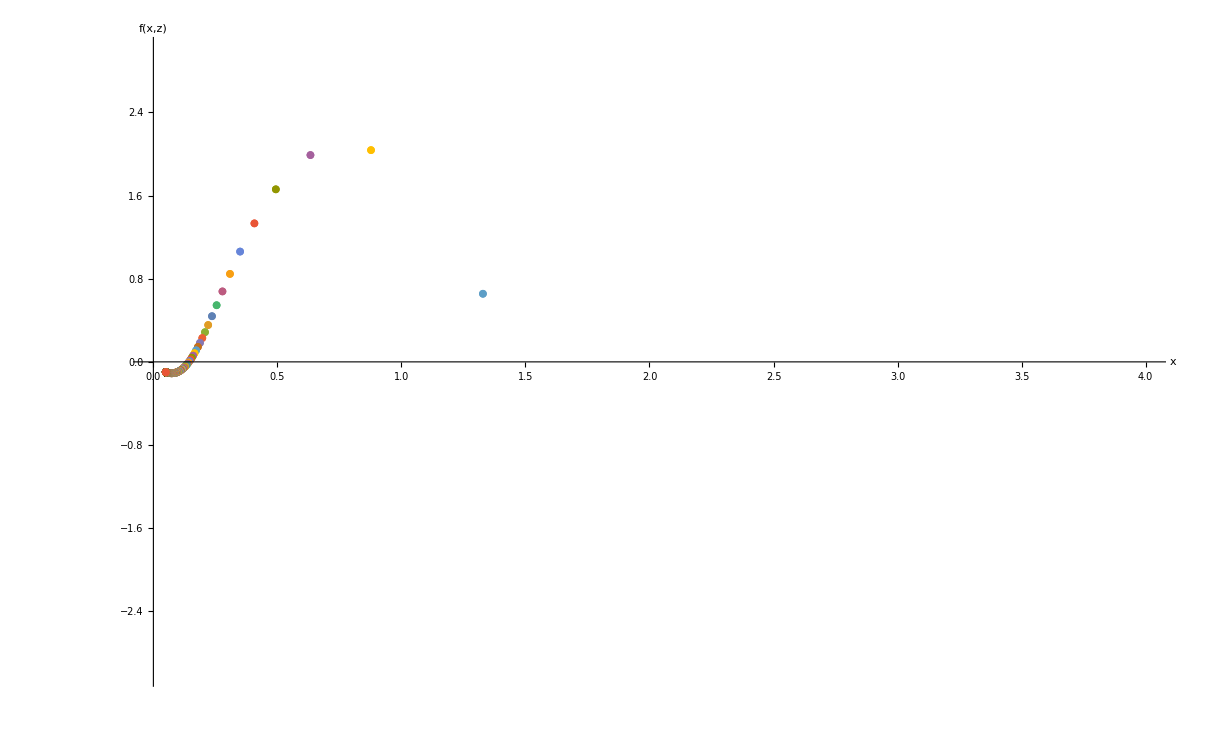

```mathematica
(*Plot x vs the remaining equation when y' = 0*)
(*When f(x,z) = 0, an Einstein point exists*)
EinsteinPlotTwoEinsteinPointsRepellor=ListPlot[EinsteinPointSolutionsTwoEinsteinPointsRepellor,PlotRange->{{0,4},{-3,3}},AxesLabel->{"x","f(x,z)"}]
```

### Plot the x-y-z Phase Space

```mathematica
(*Find the maximum value of K for this combination of x0 and z0 so that y0 is not imaginary*)
KMaxTwoEinsteinPointsRepellor=K/.Flatten[Solve[y0TwoEinsteinPointsRepellor==0,K]]
```

0.0483863

```mathematica
(*Solve trajTwoEinsteinPoints[K] for different values of K*)
```

```mathematica
solTwoEinsteinPointsRepellor[1]=trajTwoEinsteinPointsRepellor[-0.01]
```

NDSolve::ndsz: At t == -4.45005, step size is effectively zero; singularity or stiff system suspected.

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsRepellor[2]=trajTwoEinsteinPointsRepellor[0.01]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsRepellor[3]=trajTwoEinsteinPointsRepellor[-.1]
```

NDSolve::ndsz: At t == -2.63691, step size is effectively zero; singularity or stiff system suspected.

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsRepellor[4]=trajTwoEinsteinPointsRepellor[KMaxTwoEinsteinPointsRepellor]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the trajectories for the different values of K given above*)
```

```mathematica
trajTwoEinsteinPointsxyzRepellor[1]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsRepellor[1],{t,-4.44,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsxyzRepellor[2]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsRepellor[2],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsxyzRepellor[3]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsRepellor[3],{t,-2.61,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsxyzRepellor[4]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsRepellor[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75],Dashed}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
(*Solve the x-y-z system using the centre Einstein fixed point for x0 and z0 to plot a cyclic trajectory*)
CyclicTrajTwoEinsteinPointsRepellor=NDSolve[{dext,deyt,dezt,x1[0]==EinsteinPoint2TwoEinsteinPointsRepellor[[1]],y1[0]==0.436,z1[0]==EinsteinPoint2TwoEinsteinPointsRepellor[[3]]},{x1,y1,z1},{t,-100,100}];
```

```mathematica
(*Plot the cyclic trajectory*)
trajTwoEinsteinPointsxyzRepellor[5]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.CyclicTrajTwoEinsteinPointsRepellor,{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajTwoEinsteinPointsCaseRepellor=Table[trajTwoEinsteinPointsxyzRepellor[i],{i,1,5}];
```

```mathematica
(*Plot the Einstein fixed points*)
EinsteinFixedPointsTwoEinsteinPointsRepellor=ListPointPlot3D[{EinsteinPoint1TwoEinsteinPointsRepellor,EinsteinPoint2TwoEinsteinPointsRepellor},PlotStyle->Black];
```

```mathematica
(*Solve the x-y-z system around the Einstein fixed point to plot the Closed Friedmann Separatrix (CFS)*)
CFSTwoEinsteinPointsSolRepellor=NDSolve[{dext,deyt,dezt,x1[0]==EinsteinPoint1TwoEinsteinPointsRepellor[[1]],y1[0]==-0.0005,z1[0]==EinsteinPoint1TwoEinsteinPointsRepellor[[3]]},{x1,y1,z1},{t,-100,100}]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the CFS*)
CFSTwoEinsteinPointsRepellor=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.CFSTwoEinsteinPointsSolRepellor,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Show the x-y-z phase space*)
Show[trajTwoEinsteinPointsCaseRepellor,CFSTwoEinsteinPointsRepellor,EinsteinFixedPointsTwoEinsteinPointsRepellor,AccnxyzRepellor,FPsxyzRepellor,xyzFormat,PlotRange->{{0,5},{-5,5},{0,15}}]
```

-Graphics3D-

#### Plot the x-z Projection

```mathematica
(*Plot one solution on the x-z plane*)
trajTwoEinsteinPointsxzRepellor=ParametricPlot[Evaluate[{{z1[t],x1[t]}}/.solTwoEinsteinPointsRepellor[1],{t,-4.44,100},PlotStyle -> {{Black, Thick,Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.03,.03,0},1]]],Arrow[x]};;
```

```mathematica
(*Plot the Einstein fixed points on the x-z plane*)
EinsteinFixedPointsTwoEinsteinPointsxzRepellor=ListPlot[{{EinsteinPoint1TwoEinsteinPointsRepellor[[3]],EinsteinPoint1TwoEinsteinPointsRepellor[[1]]},{EinsteinPoint2TwoEinsteinPointsRepellor[[3]],EinsteinPoint2TwoEinsteinPointsRepellor[[1]]}},PlotStyle->Black];
```

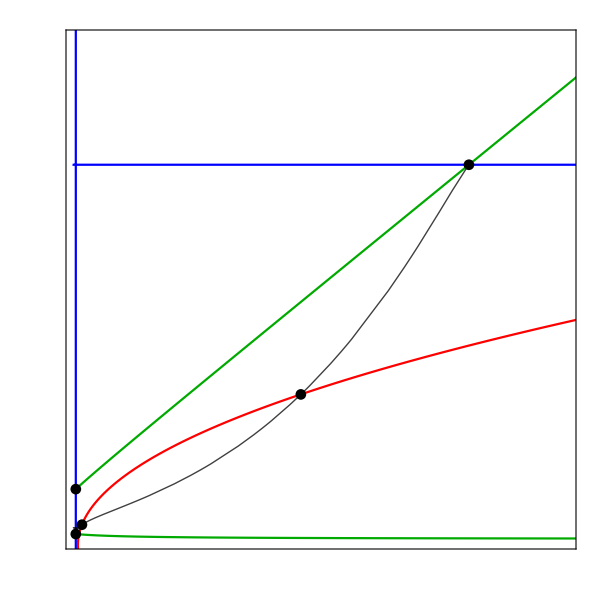

```mathematica
(*Show the x-z phase space with the a'' = 0 (red), x' = 0 (green) and z' = 0 (purple) curves*)
Show[trajTwoEinsteinPointsxzRepellor,AccnxzRepellor,xLineRepellor,zLineRepellor,FPsxzRepellor,EinsteinFixedPointsTwoEinsteinPointsxzRepellor,xzFormat,PlotRange->{{0,15},{0,5}}]
```

## Compact Phase Spaces: constant X0 and Z0 surfaces

Trajectories are plotted on a constant X0-Z0 surface, where X0 is fixed for all cases and Z0 is fixed for each phase space to give a different number of Einstein fixed points. k and Y0 differ for each trajectory in each phase space.

### Define parameter values and set-up initial conditions

```mathematica
(*Set parameter values*)
wx=-0.5;
q=0.8;
ϵ=-1;
ℛ=0.05;
```

```mathematica
(*Define Ωx0 and Ωm0 using data from Planck 2018*)
Ωx0=0.6889;
Ωm0=0.3111;
```

```mathematica
(*Set a value for α, which sets the value of the low energy cosmological constant*)
α=0.5;
```

```mathematica
(*Define the initial conditions, where a0 = 1 and K is defined as k/ρ* *)

x0=ℛ/α;
y0=Sqrt[x0/3+Z0/(3*(1-Z0))-K];
```

```mathematica
(*Compactify the initial conditions*)

X0=x0/(1+x0);
Y0=y0/Sqrt[1+y0^2];
```

```mathematica
(*Define values of K using the range of Ωk0 allowed by Planck 2018*)
Ωk0Open=0.003;
Ωk0Closed=-0.001;

KDensityParametersOpen=-Ωk0Open*ℛ/(3*α*Ωx0)
KDensityParametersClosed=-Ωk0Closed*ℛ/(3*α*Ωx0)
```

-0.000145159

0.0000483863

### Set-up for the compact X-Y-Z system

```mathematica
(*Load MaTeX to typeset axis labels using LaTeX*)
<<MaTeX`
```

```mathematica
(*Define a format style for the X-Y-Z phase spaces*)
XYZCompactFormat={AxesLabel->{MaTeX["X",FontSize->22],MaTeX["Y",FontSize->22],MaTeX["Z",FontSize->22]},Ticks->{{0.,0.5,1.0},{-1,-0.5,0.,0.5,1.0},{0.,0.5,1.0}},PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->22}};
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y*)
deX:=X'=-3*(Y/((1-Y^2)^(1/2)))*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))*(Y/((1-Y^2)^(1/2)))
deY:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(X/(1-X))^2)
deZ:=Z'=-3*Z*(1-Z)*(Y/((1-Y^2)^(1/2))) + q*(X/(1-X))*Z*(1-Z)*(Y/((1-Y^2)^(1/2)))
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y in terms of time, t*)
deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*(X1[t]-ℛ*(1-X1[t]))*((1+wx)*(1-X1[t])+ϵ*X1[t])-q*X1[t]*(1-X1[t])*(Z1[t]/(1-Z1[t]))*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((Z1[t]/(1-Z1[t]))+(X1[t]/(1-X1[t]))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X1[t]^2/((1-X1[t])^2))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2))) + q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
```

```mathematica
(*Find the fixed points of the system*)
FPsXYZRepellor=Solve[{deX==0,deY==0,deZ==0},{X,Y,Z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Y→0.,Z→(3.+8. X+109. X^2)/(43.-72. X+149. X^2)},{X→0.333333,Y→-0.377964,Z→0.},{X→0.047619,Y→-0.128037,Z→0.},{X→-0.0366972-0.161791 ⅈ,Y→0.,Z→0.},{X→-0.0366972+0.161791 ⅈ,Y→0.,Z→0.},{X→0.047619,Y→0.128037,Z→0.},{X→0.333333,Y→0.377964,Z→0.},{X→0.789474,Y→-0.916631,Z→0.923225},{X→0.789474,Y→0.916631,Z→0.923225},{X→0.789474,Y→0.,Z→0.977566}}

```mathematica
(*Extract the values of the fixed points and put them into a common variable name*)
FPXYZRepellor[1]={X,Y/.FPsXYZRepellor[[1,1]],Z/.FPsXYZRepellor[[1,2]]};
FPXYZRepellor[2]={X/.FPsXYZRepellor[[4,1]],Y/.FPsXYZRepellor[[4,2]],Z/.FPsXYZRepellor[[4,3]]};
FPXYZRepellor[3]={X/.FPsXYZRepellor[[9,1]],Y/.FPsXYZRepellor[[9,2]],Z/.FPsXYZRepellor[[9,3]]};
FPXYZRepellor[4]={X/.FPsXYZRepellor[[8,1]],Y/.FPsXYZRepellor[[8,2]],Z/.FPsXYZRepellor[[8,3]]};FPXYZRepellor[5]={X/.FPsXYZRepellor[[5,1]],Y/.FPsXYZRepellor[[5,2]],Z/.FPsXYZRepellor[[5,3]]};
FPXYZRepellor[6]={X/.FPsXYZRepellor[[10,1]],Y/.FPsXYZRepellor[[10,2]],Z/.FPsXYZRepellor[[10,3]]};
FPXYZRepellor[7]={X/.FPsXYZRepellor[[2,1]],Y/.FPsXYZRepellor[[2,2]],Z/.FPsXYZRepellor[[2,3]]};
FPXYZRepellor[8]={X/.FPsXYZRepellor[[3,1]],Y/.FPsXYZRepellor[[3,2]],Z/.FPsXYZRepellor[[3,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPXYZTableRepellor=Table[FPXYZRepellor[i],{i,1,8}];
```

```mathematica
(*Find the 3D Jacobian matrix. D[] differentiates each expression*)
JCompactXYZRepellor=Simplify[{{D[deX,X],D[deX,Y],D[deX,Z]},{D[deY,X],D[deY,Y],D[deY,Z]},{D[deZ,X],D[deZ,Y],D[deZ,Z]}}];
JCompactXYZRepellor//MatrixForm
```

((Y (1.8-1. Z+X (-9.45+7.85 Z)))/(√(1-Y^2) (-1.+Z)) | (0.075+X^2 (4.725-3.925 Z)-0.075 Z+X (-1.8+1. Z))/(√(1-Y^2) (-1.+Y^2) (-1.+Z)) | (0.8 (-1.+X) X Y)/(√(1-Y^2) (-1.+Z)^2)
(0.941667 (0.0619469+1. X) √(1-Y^2) (-1.+Y^2))/(-1.+X)^3 | (Y (2.0375-2.5375 Z+Y^2 (-3.0375+3.5375 Z)+X (-3.9+Y^2 (5.9-6.9 Z)+4.9 Z)+X^2 (3.3625-3.8625 Z+Y^2 (-4.3625+4.8625 Z))))/((-1.+X)^2 √(1-Y^2) (-1.+Z)) | -((1-Y^2)^(3/2))/(6 (-1+Z)^2)
-(0.8 Y (-1.+Z) Z)/((-1.+X)^2 √(1-Y^2)) | (Z (-3.+X (3.8-3.8 Z)+3. Z))/((-1.+X) √(1-Y^2) (-1.+Y^2)) | (Y (3.-6. Z+X (-3.8+7.6 Z)))/((-1.+X) √(1-Y^2)))

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableCompactRepellor=Table[{FPXYZTableRepellor[[i]]//MatrixForm,Simplify[JCompactXYZRepellor/.{X->FPXYZTableRepellor[[i,1]],Y->FPXYZTableRepellor[[i,2]],Z->FPXYZTableRepellor[[i,3]]}]//MatrixForm,Eigenvalues[JCompactXYZRepellor/.{X->FPXYZTableRepellor[[i,1]],Y->FPXYZTableRepellor[[i,2]],Z->FPXYZTableRepellor[[i,3]]}]//MatrixForm,Eigenvectors[JCompactXYZRepellor/.{X->FPXYZTableRepellor[[i,1]],Y->FPXYZTableRepellor[[i,2]],Z->FPXYZTableRepellor[[i,3]]}]//MatrixForm},{i,1,8}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableXYZRepellor=TableForm[FPTableCompactRepellor,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(X
0.
(3.+8. X+109. X^2)/(43.-72. X+149. X^2)) | (0. | (0.075-2.01 X+8.3 X^2-13.27 X^3+6.905 X^4)/(1.-2. X+1. X^2) | 0.
(-0.0583333-0.941667 X)/(-1.+X)^3 | 0. | -(2.3126 (0.288591-0.483221 X+1. X^2)^2)/((1.-2. X+1. X^2)^2)
0. | (0.0162155-0.00972929 X+0.505202 X^2-1.79235 X^3+2.02694 X^4-0.746273 X^5)/((-1.+X) (0.288591-0.483221 X+1. X^2)^2) | 0.) | (0
-(√(14957.3-334367. X-1.84165×10^6 X^2+6.38152×10^7 X^3-6.14108×10^8 X^4+3.62691×10^9 X^5-1.54261×10^10 X^6+5.05303×10^10 X^7-1.31956×10^11 X^8+2.79816×10^11 X^9-4.85864×10^11 X^10+6.91349×10^11 X^11-8.01139×10^11 X^12+7.45525×10^11 X^13-5.43828×10^11 X^14+2.9895×10^11 X^15-1.16005×10^11 X^16+2.81793×10^10 X^17-3.20484×10^9 X^18+128205./(1.-2. X+1. X^2)-(1.83303×10^6 X)/(1.-2. X+1. X^2)+(1.76847×10^7 X^2)/(1.-2. X+1. X^2)-(1.37854×10^8 X^3)/(1.-2. X+1. X^2)+(8.62344×10^8 X^4)/(1.-2. X+1. X^2)-(4.29183×10^9 X^5)/(1.-2. X+1. X^2)+(1.71311×10^10 X^6)/(1.-2. X+1. X^2)-(5.56004×10^10 X^7)/(1.-2. X+1. X^2)+(1.48584×10^11 X^8)/(1.-2. X+1. X^2)-(3.29931×10^11 X^9)/(1.-2. X+1. X^2)+(6.11911×10^11 X^10)/(1.-2. X+1. X^2)-(9.49134×10^11 X^11)/(1.-2. X+1. X^2)+(1.22794×10^12 X^12)/(1.-2. X+1. X^2)-(1.31589×10^12 X^13)/(1.-2. X+1. X^2)+(1.15416×10^12 X^14)/(1.-2. X+1. X^2)-(8.13532×10^11 X^15)/(1.-2. X+1. X^2)+(4.4858×10^11 X^16)/(1.-2. X+1. X^2)-(1.85832×10^11 X^17)/(1.-2. X+1. X^2)+(5.42278×10^10 X^18)/(1.-2. X+1. X^2)-(9.90903×10^9 X^19)/(1.-2. X+1. X^2)+(8.50636×10^8 X^20)/(1.-2. X+1. X^2)))/((-1.+X)^4 √(1.-2. X+1. X^2) (43.-72. X+149. X^2)^2)
(√(14957.3-334367. X-1.84165×10^6 X^2+6.38152×10^7 X^3-6.14108×10^8 X^4+3.62691×10^9 X^5-1.54261×10^10 X^6+5.05303×10^10 X^7-1.31956×10^11 X^8+2.79816×10^11 X^9-4.85864×10^11 X^10+6.91349×10^11 X^11-8.01139×10^11 X^12+7.45525×10^11 X^13-5.43828×10^11 X^14+2.9895×10^11 X^15-1.16005×10^11 X^16+2.81793×10^10 X^17-3.20484×10^9 X^18+128205./(1.-2. X+1. X^2)-(1.83303×10^6 X)/(1.-2. X+1. X^2)+(1.76847×10^7 X^2)/(1.-2. X+1. X^2)-(1.37854×10^8 X^3)/(1.-2. X+1. X^2)+(8.62344×10^8 X^4)/(1.-2. X+1. X^2)-(4.29183×10^9 X^5)/(1.-2. X+1. X^2)+(1.71311×10^10 X^6)/(1.-2. X+1. X^2)-(5.56004×10^10 X^7)/(1.-2. X+1. X^2)+(1.48584×10^11 X^8)/(1.-2. X+1. X^2)-(3.29931×10^11 X^9)/(1.-2. X+1. X^2)+(6.11911×10^11 X^10)/(1.-2. X+1. X^2)-(9.49134×10^11 X^11)/(1.-2. X+1. X^2)+(1.22794×10^12 X^12)/(1.-2. X+1. X^2)-(1.31589×10^12 X^13)/(1.-2. X+1. X^2)+(1.15416×10^12 X^14)/(1.-2. X+1. X^2)-(8.13532×10^11 X^15)/(1.-2. X+1. X^2)+(4.4858×10^11 X^16)/(1.-2. X+1. X^2)-(1.85832×10^11 X^17)/(1.-2. X+1. X^2)+(5.42278×10^10 X^18)/(1.-2. X+1. X^2)-(9.90903×10^9 X^19)/(1.-2. X+1. X^2)+(8.50636×10^8 X^20)/(1.-2. X+1. X^2)))/((-1.+X)^4 √(1.-2. X+1. X^2) (43.-72. X+149. X^2)^2)) | (-(2.45586 (-1.+X)^3 (0.288591-0.483221 X+1. X^2)^2)/((0.0619469+1. X) (1.-2. X+1. X^2)^2) | 0 | 1.
-(9.25265 (-4.66709×10^-6+0.000113666 X+0.000361315 X^2-0.0209571 X^3+0.232018 X^4-1.53485 X^5+7.26839 X^6-26.5253 X^7+77.5212 X^8-185.425 X^9+367.398 X^10-606.238 X^11+833.022 X^12-948.302 X^13+884.918 X^14-665.285 X^15+392.448 X^16-174.467 X^17+54.7824 X^18-10.7927 X^19+1. X^20))/((-1.+X)^4 (0.0619469+1. X) (1.-2. X+1. X^2)^2 (0.288591-0.483221 X+1. X^2)^2 (0.0275229+0.0733945 X+1. X^2) (-0.789474+2.57895 X-2.78947 X^2+1. X^3)) | (0.0000603573 √(14957.3-334367. X-1.84165×10^6 X^2+6.38152×10^7 X^3-6.14108×10^8 X^4+3.62691×10^9 X^5-1.54261×10^10 X^6+5.05303×10^10 X^7-1.31956×10^11 X^8+2.79816×10^11 X^9-4.85864×10^11 X^10+6.91349×10^11 X^11-8.01139×10^11 X^12+7.45525×10^11 X^13-5.43828×10^11 X^14+2.9895×10^11 X^15-1.16005×10^11 X^16+2.81793×10^10 X^17-3.20484×10^9 X^18+128205./(1.-2. X+1. X^2)-(1.83303×10^6 X)/(1.-2. X+1. X^2)+(1.76847×10^7 X^2)/(1.-2. X+1. X^2)-(1.37854×10^8 X^3)/(1.-2. X+1. X^2)+(8.62344×10^8 X^4)/(1.-2. X+1. X^2)-(4.29183×10^9 X^5)/(1.-2. X+1. X^2)+(1.71311×10^10 X^6)/(1.-2. X+1. X^2)-(5.56004×10^10 X^7)/(1.-2. X+1. X^2)+(1.48584×10^11 X^8)/(1.-2. X+1. X^2)-(3.29931×10^11 X^9)/(1.-2. X+1. X^2)+(6.11911×10^11 X^10)/(1.-2. X+1. X^2)-(9.49134×10^11 X^11)/(1.-2. X+1. X^2)+(1.22794×10^12 X^12)/(1.-2. X+1. X^2)-(1.31589×10^12 X^13)/(1.-2. X+1. X^2)+(1.15416×10^12 X^14)/(1.-2. X+1. X^2)-(8.13532×10^11 X^15)/(1.-2. X+1. X^2)+(4.4858×10^11 X^16)/(1.-2. X+1. X^2)-(1.85832×10^11 X^17)/(1.-2. X+1. X^2)+(5.42278×10^10 X^18)/(1.-2. X+1. X^2)-(9.90903×10^9 X^19)/(1.-2. X+1. X^2)+(8.50636×10^8 X^20)/(1.-2. X+1. X^2)))/((-1.+X)^3 √(1.-2. X+1. X^2) (0.0275229+0.0733945 X+1. X^2) (-0.789474+2.57895 X-2.78947 X^2+1. X^3)) | 1.
-(9.25265 (-4.66709×10^-6+0.000113666 X+0.000361315 X^2-0.0209571 X^3+0.232018 X^4-1.53485 X^5+7.26839 X^6-26.5253 X^7+77.5212 X^8-185.425 X^9+367.398 X^10-606.238 X^11+833.022 X^12-948.302 X^13+884.918 X^14-665.285 X^15+392.448 X^16-174.467 X^17+54.7824 X^18-10.7927 X^19+1. X^20))/((-1.+X)^4 (0.0619469+1. X) (1.-2. X+1. X^2)^2 (0.288591-0.483221 X+1. X^2)^2 (0.0275229+0.0733945 X+1. X^2) (-0.789474+2.57895 X-2.78947 X^2+1. X^3)) | -(0.0000603573 √(14957.3-334367. X-1.84165×10^6 X^2+6.38152×10^7 X^3-6.14108×10^8 X^4+3.62691×10^9 X^5-1.54261×10^10 X^6+5.05303×10^10 X^7-1.31956×10^11 X^8+2.79816×10^11 X^9-4.85864×10^11 X^10+6.91349×10^11 X^11-8.01139×10^11 X^12+7.45525×10^11 X^13-5.43828×10^11 X^14+2.9895×10^11 X^15-1.16005×10^11 X^16+2.81793×10^10 X^17-3.20484×10^9 X^18+128205./(1.-2. X+1. X^2)-(1.83303×10^6 X)/(1.-2. X+1. X^2)+(1.76847×10^7 X^2)/(1.-2. X+1. X^2)-(1.37854×10^8 X^3)/(1.-2. X+1. X^2)+(8.62344×10^8 X^4)/(1.-2. X+1. X^2)-(4.29183×10^9 X^5)/(1.-2. X+1. X^2)+(1.71311×10^10 X^6)/(1.-2. X+1. X^2)-(5.56004×10^10 X^7)/(1.-2. X+1. X^2)+(1.48584×10^11 X^8)/(1.-2. X+1. X^2)-(3.29931×10^11 X^9)/(1.-2. X+1. X^2)+(6.11911×10^11 X^10)/(1.-2. X+1. X^2)-(9.49134×10^11 X^11)/(1.-2. X+1. X^2)+(1.22794×10^12 X^12)/(1.-2. X+1. X^2)-(1.31589×10^12 X^13)/(1.-2. X+1. X^2)+(1.15416×10^12 X^14)/(1.-2. X+1. X^2)-(8.13532×10^11 X^15)/(1.-2. X+1. X^2)+(4.4858×10^11 X^16)/(1.-2. X+1. X^2)-(1.85832×10^11 X^17)/(1.-2. X+1. X^2)+(5.42278×10^10 X^18)/(1.-2. X+1. X^2)-(9.90903×10^9 X^19)/(1.-2. X+1. X^2)+(8.50636×10^8 X^20)/(1.-2. X+1. X^2)))/((-1.+X)^3 √(1.-2. X+1. X^2) (0.0275229+0.0733945 X+1. X^2) (-0.789474+2.57895 X-2.78947 X^2+1. X^3)) | 1.)
(-0.0366972-0.161791 ⅈ
0.
0.) | (0.+0. ⅈ | 0.0237354+0.347331 ⅈ | 0.+0. ⅈ
-0.0406748-0.127141 ⅈ | 0.+0. ⅈ | -0.166667
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ) | (0.21174-0.0404868 ⅈ
-0.21174+0.0404868 ⅈ
0.) | (0.8502+0. ⅈ | -0.0633894-0.52263 ⅈ | 0.+0. ⅈ
0.8502+0. ⅈ | 0.0633894+0.52263 ⅈ | 0.+0. ⅈ
0.780514+0. ⅈ | -8.26298×10^-18+2.64349×10^-18 ⅈ | -0.190483-0.595411 ⅈ)
(0.789474
0.916631
0.923225) | (25.7516 | 0. | -51.7266
5.48825 | -4.58621 | -1.80599
2.9338 | 0. | 0.) | (16.6215
9.13007
-4.58621) | (0.957576 | 0.233414 | 0.169018
0.901198 | 0.322464 | 0.289586
0. | 1. | 0.)
(0.789474
-0.916631
0.923225) | (-25.7516 | 0. | 51.7266
5.48825 | 4.58621 | -1.80599
-2.9338 | 0. | 0.) | (-16.6215
-9.13007
4.58621) | (-0.957576 | 0.233414 | -0.169018
-0.901198 | 0.322464 | -0.289586
0. | 1. | 0.)
(-0.0366972+0.161791 ⅈ
0.
0.) | (0.+0. ⅈ | 0.0237354-0.347331 ⅈ | 0.+0. ⅈ
-0.0406748+0.127141 ⅈ | 0.+0. ⅈ | -0.166667
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ) | (0.21174+0.0404868 ⅈ
-0.21174-0.0404868 ⅈ
0.) | (0.8502+0. ⅈ | -0.0633894+0.52263 ⅈ | 0.+0. ⅈ
0.8502+0. ⅈ | 0.0633894-0.52263 ⅈ | 0.+0. ⅈ
0.780514+0. ⅈ | -8.26298×10^-18-2.64349×10^-18 ⅈ | -0.190483+0.595411 ⅈ)
(0.789474
0.
0.977566) | (0. | -4.19501 | 0.
85.9255 | 0. | -331.155
0. | 0. | 0.) | (0.+18.9858 ⅈ
0.-18.9858 ⅈ
0.+0. ⅈ) | (0.+0.215752 ⅈ | 0.976448+0. ⅈ | 0.+0. ⅈ
0.-0.215752 ⅈ | 0.976448+0. ⅈ | 0.+0. ⅈ
0.967947+0. ⅈ | 0.+0. ⅈ | 0.251155+0. ⅈ)
(0.333333
-0.377964
0.) | (-0.551135 | 1.39904×10^-16 | 0.0725775
0.99691 | 0.816497 | -0.13226
0. | 0. | 1.06145) | (1.06145
0.816497
-0.551135) | (0.0423519 | -0.335729 | 0.941006
-3.04065×10^-17 | -1. | 0.
-0.808098 | 0.589048 | 0.)
(0.047619
-0.128037
0.) | (0.174284 | 0. | 0.00468388
0.116513 | 0.258199 | -0.162585
0. | 0. | 0.382134) | (0.382134
0.258199
0.174284) | (0.0138006 | -0.790419 | 0.612411
0. | 1. | 0.
0.584422 | -0.81145 | 0.)

```mathematica
(*Plot the fixed points of the system*)
FPsXYZRepellor=ListPointPlot3D[Table[FPXYZRepellor[i],{i,2,5}], PlotStyle->{Black}];
```

```mathematica
(*Extra fixed points exist when the system is compactified*)
(*Find the de Sitter fixed points at Y = +-1*)
```

```mathematica
(*Solve X' = 0 when Y = +- 1 for Z*)
ZXPrimeZeroRepellor=Z/.Solve[-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))==0,Z]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{(3. (1.-24. X+63. X^2))/(3.-40. X+157. X^2)}

```mathematica
(*Substitute Z = ZXPrimeZero into Z' at Y = +-1*)
ZPrimeRepellor=Flatten[-3*Z*(1-Z) + q*(X/(1-X))*Z*(1-Z)/.Z->ZXPrimeZeroRepellor][[1]]
```

-(9. (1.-24. X+63. X^2) (1-(3. (1.-24. X+63. X^2))/(3.-40. X+157. X^2)))/(3.-40. X+157. X^2)+(2.4 X (1.-24. X+63. X^2) (1-(3. (1.-24. X+63. X^2))/(3.-40. X+157. X^2)))/((1-X) (3.-40. X+157. X^2))

```mathematica
(*Solve ZPrime = 0 (Z' = 0) for X*)
XdSSolRepellor=X/.FindRoot[ZPrimeRepellor==0,{X,0.8}]
```

0.789474

```mathematica
(*Subsitute XdSSol into ZXPrimeZero to find the value of Z at the fixed point*)
ZdSSolRepellor=Flatten[ZXPrimeZeroRepellor/.X->XdSSolRepellor][[1]]
```

0.923225

```mathematica
(*Plot the fixed points from compactification*)
CompactFPShowXYZRepellor=ListPointPlot3D[{{XdSSolRepellor,1,ZdSSolRepellor},{XdSSolRepellor,-1,ZdSSolRepellor}}, PlotStyle->{Black}];
```

```mathematica
(*Define the acceleration equation*)
AccnCompactRepellor=((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(X/(1-X))^2)/Sqrt[1+((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(X/(1-X))^2)^2]
```

(-0.075-(0.35 X)/(1-X)-(3 X^2)/(1-X)^2+Z/(1-Z))/(√(1+(-0.075-(0.35 X)/(1-X)-(3 X^2)/(1-X)^2+Z/(1-Z))^2))

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
AccnXYZRepellor=ContourPlot3D[AccnCompactRepellor==0,{X,0,1},{Y,-1,1},{Z,0,1},ContourStyle->{Red,Opacity[0.25]},Mesh->None];
```

### Set-up for the compact X-Z system

```mathematica
(*Define a format style for the X-Z phase spaces*)
XZCompactFormat={Frame->True,FrameLabel->{MaTeX["Z",FontSize->24],Rotate[MaTeX["X",FontSize->24],300]},FrameTicks->{{Table[{X,MaTeX[X,"DisplayStyle"->False,FontSize->24]},{X,0.5Range[-1,2]}],None},{Table[{Z,MaTeX[Z,"DisplayStyle"->False,FontSize->24]},{Z,0.5Range[-1,2]}],None}},PlotRange->{{0,1},{0,1}},ImageSize->{600,600},PlotRangePadding->{0.01,0}};
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, and dark matter, Z*)
deX:=X'=-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))
deZ:=Z'=-3*Z*(1-Z)+ q*(X/(1-X))*Z*(1-Z)
```

```mathematica
(*Find the fixed points of the system*)
FPsXZRepellor=Solve[{deZ==0,deX==0},{Z,X}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Z→0.,X→0.047619},{Z→0.,X→0.333333},{Z→0.923225,X→0.789474}}

```mathematica
(*Extract the values of the fixed points and put them into a common variable name*)
FPXZRepellor[1]={Z/.FPsXZRepellor[[1,1]],X/.FPsXZRepellor[[1,2]]};
FPXZRepellor[2]={Z/.FPsXZRepellor[[2,1]],X/.FPsXZRepellor[[2,2]]};
FPXZRepellor[3]={Z/.FPsXZRepellor[[3,1]],X/.FPsXZRepellor[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPXZTableRepellor=Table[FPXZRepellor[i],{i,1,3}];
```

```mathematica
(*Find the 2D Jacobian matrix. D[] differentiates each expression*)
JCompactXZRepellor=Simplify[{{D[deZ,Z],D[deZ,X]},{D[deX,Z],D[deX,X]}}];
JCompactXZRepellor//MatrixForm
```

((3.-6. Z+X (-3.8+7.6 Z))/(-1.+X) | -(0.8 (-1.+Z) Z)/(-1.+X)^2
(0.8 (-1.+X) X)/(-1.+Z)^2 | (1.8-1. Z+X (-9.45+7.85 Z))/(-1.+Z))

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableCompact=Table[{FPXZTableRepellor[[i]]//MatrixForm,Simplify[JCompactXZRepellor/.{Z->FPXZTableRepellor[[i,1]],X->FPXZTableRepellor[[i,2]]}]//MatrixForm,Eigenvalues[JCompactXZRepellor/.{Z->FPXZTableRepellor[[i,1]],X->FPXZTableRepellor[[i,2]]}]//MatrixForm,Eigenvectors[JCompactXZRepellor/.{Z->FPXZTableRepellor[[i,1]],X->FPXZTableRepellor[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableXZRepellor=TableForm[FPTableCompactRepellor,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(X
0.
(3.+8. X+109. X^2)/(43.-72. X+149. X^2)) | (0. | (0.075-2.01 X+8.3 X^2-13.27 X^3+6.905 X^4)/(1.-2. X+1. X^2) | 0.
(-0.0583333-0.941667 X)/(-1.+X)^3 | 0. | -(2.3126 (0.288591-0.483221 X+1. X^2)^2)/((1.-2. X+1. X^2)^2)
0. | (0.0162155-0.00972929 X+0.505202 X^2-1.79235 X^3+2.02694 X^4-0.746273 X^5)/((-1.+X) (0.288591-0.483221 X+1. X^2)^2) | 0.) | (0
-(√(14957.3-334367. X-1.84165×10^6 X^2+6.38152×10^7 X^3-6.14108×10^8 X^4+3.62691×10^9 X^5-1.54261×10^10 X^6+5.05303×10^10 X^7-1.31956×10^11 X^8+2.79816×10^11 X^9-4.85864×10^11 X^10+6.91349×10^11 X^11-8.01139×10^11 X^12+7.45525×10^11 X^13-5.43828×10^11 X^14+2.9895×10^11 X^15-1.16005×10^11 X^16+2.81793×10^10 X^17-3.20484×10^9 X^18+128205./(1.-2. X+1. X^2)-(1.83303×10^6 X)/(1.-2. X+1. X^2)+(1.76847×10^7 X^2)/(1.-2. X+1. X^2)-(1.37854×10^8 X^3)/(1.-2. X+1. X^2)+(8.62344×10^8 X^4)/(1.-2. X+1. X^2)-(4.29183×10^9 X^5)/(1.-2. X+1. X^2)+(1.71311×10^10 X^6)/(1.-2. X+1. X^2)-(5.56004×10^10 X^7)/(1.-2. X+1. X^2)+(1.48584×10^11 X^8)/(1.-2. X+1. X^2)-(3.29931×10^11 X^9)/(1.-2. X+1. X^2)+(6.11911×10^11 X^10)/(1.-2. X+1. X^2)-(9.49134×10^11 X^11)/(1.-2. X+1. X^2)+(1.22794×10^12 X^12)/(1.-2. X+1. X^2)-(1.31589×10^12 X^13)/(1.-2. X+1. X^2)+(1.15416×10^12 X^14)/(1.-2. X+1. X^2)-(8.13532×10^11 X^15)/(1.-2. X+1. X^2)+(4.4858×10^11 X^16)/(1.-2. X+1. X^2)-(1.85832×10^11 X^17)/(1.-2. X+1. X^2)+(5.42278×10^10 X^18)/(1.-2. X+1. X^2)-(9.90903×10^9 X^19)/(1.-2. X+1. X^2)+(8.50636×10^8 X^20)/(1.-2. X+1. X^2)))/((-1.+X)^4 √(1.-2. X+1. X^2) (43.-72. X+149. X^2)^2)
(√(14957.3-334367. X-1.84165×10^6 X^2+6.38152×10^7 X^3-6.14108×10^8 X^4+3.62691×10^9 X^5-1.54261×10^10 X^6+5.05303×10^10 X^7-1.31956×10^11 X^8+2.79816×10^11 X^9-4.85864×10^11 X^10+6.91349×10^11 X^11-8.01139×10^11 X^12+7.45525×10^11 X^13-5.43828×10^11 X^14+2.9895×10^11 X^15-1.16005×10^11 X^16+2.81793×10^10 X^17-3.20484×10^9 X^18+128205./(1.-2. X+1. X^2)-(1.83303×10^6 X)/(1.-2. X+1. X^2)+(1.76847×10^7 X^2)/(1.-2. X+1. X^2)-(1.37854×10^8 X^3)/(1.-2. X+1. X^2)+(8.62344×10^8 X^4)/(1.-2. X+1. X^2)-(4.29183×10^9 X^5)/(1.-2. X+1. X^2)+(1.71311×10^10 X^6)/(1.-2. X+1. X^2)-(5.56004×10^10 X^7)/(1.-2. X+1. X^2)+(1.48584×10^11 X^8)/(1.-2. X+1. X^2)-(3.29931×10^11 X^9)/(1.-2. X+1. X^2)+(6.11911×10^11 X^10)/(1.-2. X+1. X^2)-(9.49134×10^11 X^11)/(1.-2. X+1. X^2)+(1.22794×10^12 X^12)/(1.-2. X+1. X^2)-(1.31589×10^12 X^13)/(1.-2. X+1. X^2)+(1.15416×10^12 X^14)/(1.-2. X+1. X^2)-(8.13532×10^11 X^15)/(1.-2. X+1. X^2)+(4.4858×10^11 X^16)/(1.-2. X+1. X^2)-(1.85832×10^11 X^17)/(1.-2. X+1. X^2)+(5.42278×10^10 X^18)/(1.-2. X+1. X^2)-(9.90903×10^9 X^19)/(1.-2. X+1. X^2)+(8.50636×10^8 X^20)/(1.-2. X+1. X^2)))/((-1.+X)^4 √(1.-2. X+1. X^2) (43.-72. X+149. X^2)^2)) | (-(2.45586 (-1.+X)^3 (0.288591-0.483221 X+1. X^2)^2)/((0.0619469+1. X) (1.-2. X+1. X^2)^2) | 0 | 1.
-(9.25265 (-4.66709×10^-6+0.000113666 X+0.000361315 X^2-0.0209571 X^3+0.232018 X^4-1.53485 X^5+7.26839 X^6-26.5253 X^7+77.5212 X^8-185.425 X^9+367.398 X^10-606.238 X^11+833.022 X^12-948.302 X^13+884.918 X^14-665.285 X^15+392.448 X^16-174.467 X^17+54.7824 X^18-10.7927 X^19+1. X^20))/((-1.+X)^4 (0.0619469+1. X) (1.-2. X+1. X^2)^2 (0.288591-0.483221 X+1. X^2)^2 (0.0275229+0.0733945 X+1. X^2) (-0.789474+2.57895 X-2.78947 X^2+1. X^3)) | (0.0000603573 √(14957.3-334367. X-1.84165×10^6 X^2+6.38152×10^7 X^3-6.14108×10^8 X^4+3.62691×10^9 X^5-1.54261×10^10 X^6+5.05303×10^10 X^7-1.31956×10^11 X^8+2.79816×10^11 X^9-4.85864×10^11 X^10+6.91349×10^11 X^11-8.01139×10^11 X^12+7.45525×10^11 X^13-5.43828×10^11 X^14+2.9895×10^11 X^15-1.16005×10^11 X^16+2.81793×10^10 X^17-3.20484×10^9 X^18+128205./(1.-2. X+1. X^2)-(1.83303×10^6 X)/(1.-2. X+1. X^2)+(1.76847×10^7 X^2)/(1.-2. X+1. X^2)-(1.37854×10^8 X^3)/(1.-2. X+1. X^2)+(8.62344×10^8 X^4)/(1.-2. X+1. X^2)-(4.29183×10^9 X^5)/(1.-2. X+1. X^2)+(1.71311×10^10 X^6)/(1.-2. X+1. X^2)-(5.56004×10^10 X^7)/(1.-2. X+1. X^2)+(1.48584×10^11 X^8)/(1.-2. X+1. X^2)-(3.29931×10^11 X^9)/(1.-2. X+1. X^2)+(6.11911×10^11 X^10)/(1.-2. X+1. X^2)-(9.49134×10^11 X^11)/(1.-2. X+1. X^2)+(1.22794×10^12 X^12)/(1.-2. X+1. X^2)-(1.31589×10^12 X^13)/(1.-2. X+1. X^2)+(1.15416×10^12 X^14)/(1.-2. X+1. X^2)-(8.13532×10^11 X^15)/(1.-2. X+1. X^2)+(4.4858×10^11 X^16)/(1.-2. X+1. X^2)-(1.85832×10^11 X^17)/(1.-2. X+1. X^2)+(5.42278×10^10 X^18)/(1.-2. X+1. X^2)-(9.90903×10^9 X^19)/(1.-2. X+1. X^2)+(8.50636×10^8 X^20)/(1.-2. X+1. X^2)))/((-1.+X)^3 √(1.-2. X+1. X^2) (0.0275229+0.0733945 X+1. X^2) (-0.789474+2.57895 X-2.78947 X^2+1. X^3)) | 1.
-(9.25265 (-4.66709×10^-6+0.000113666 X+0.000361315 X^2-0.0209571 X^3+0.232018 X^4-1.53485 X^5+7.26839 X^6-26.5253 X^7+77.5212 X^8-185.425 X^9+367.398 X^10-606.238 X^11+833.022 X^12-948.302 X^13+884.918 X^14-665.285 X^15+392.448 X^16-174.467 X^17+54.7824 X^18-10.7927 X^19+1. X^20))/((-1.+X)^4 (0.0619469+1. X) (1.-2. X+1. X^2)^2 (0.288591-0.483221 X+1. X^2)^2 (0.0275229+0.0733945 X+1. X^2) (-0.789474+2.57895 X-2.78947 X^2+1. X^3)) | -(0.0000603573 √(14957.3-334367. X-1.84165×10^6 X^2+6.38152×10^7 X^3-6.14108×10^8 X^4+3.62691×10^9 X^5-1.54261×10^10 X^6+5.05303×10^10 X^7-1.31956×10^11 X^8+2.79816×10^11 X^9-4.85864×10^11 X^10+6.91349×10^11 X^11-8.01139×10^11 X^12+7.45525×10^11 X^13-5.43828×10^11 X^14+2.9895×10^11 X^15-1.16005×10^11 X^16+2.81793×10^10 X^17-3.20484×10^9 X^18+128205./(1.-2. X+1. X^2)-(1.83303×10^6 X)/(1.-2. X+1. X^2)+(1.76847×10^7 X^2)/(1.-2. X+1. X^2)-(1.37854×10^8 X^3)/(1.-2. X+1. X^2)+(8.62344×10^8 X^4)/(1.-2. X+1. X^2)-(4.29183×10^9 X^5)/(1.-2. X+1. X^2)+(1.71311×10^10 X^6)/(1.-2. X+1. X^2)-(5.56004×10^10 X^7)/(1.-2. X+1. X^2)+(1.48584×10^11 X^8)/(1.-2. X+1. X^2)-(3.29931×10^11 X^9)/(1.-2. X+1. X^2)+(6.11911×10^11 X^10)/(1.-2. X+1. X^2)-(9.49134×10^11 X^11)/(1.-2. X+1. X^2)+(1.22794×10^12 X^12)/(1.-2. X+1. X^2)-(1.31589×10^12 X^13)/(1.-2. X+1. X^2)+(1.15416×10^12 X^14)/(1.-2. X+1. X^2)-(8.13532×10^11 X^15)/(1.-2. X+1. X^2)+(4.4858×10^11 X^16)/(1.-2. X+1. X^2)-(1.85832×10^11 X^17)/(1.-2. X+1. X^2)+(5.42278×10^10 X^18)/(1.-2. X+1. X^2)-(9.90903×10^9 X^19)/(1.-2. X+1. X^2)+(8.50636×10^8 X^20)/(1.-2. X+1. X^2)))/((-1.+X)^3 √(1.-2. X+1. X^2) (0.0275229+0.0733945 X+1. X^2) (-0.789474+2.57895 X-2.78947 X^2+1. X^3)) | 1.)
(-0.0366972-0.161791 ⅈ
0.
0.) | (0.+0. ⅈ | 0.0237354+0.347331 ⅈ | 0.+0. ⅈ
-0.0406748-0.127141 ⅈ | 0.+0. ⅈ | -0.166667
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ) | (0.21174-0.0404868 ⅈ
-0.21174+0.0404868 ⅈ
0.) | (0.8502+0. ⅈ | -0.0633894-0.52263 ⅈ | 0.+0. ⅈ
0.8502+0. ⅈ | 0.0633894+0.52263 ⅈ | 0.+0. ⅈ
0.780514+0. ⅈ | -8.26298×10^-18+2.64349×10^-18 ⅈ | -0.190483-0.595411 ⅈ)
(0.789474
0.916631
0.923225) | (25.7516 | 0. | -51.7266
5.48825 | -4.58621 | -1.80599
2.9338 | 0. | 0.) | (16.6215
9.13007
-4.58621) | (0.957576 | 0.233414 | 0.169018
0.901198 | 0.322464 | 0.289586
0. | 1. | 0.)
(0.789474
-0.916631
0.923225) | (-25.7516 | 0. | 51.7266
5.48825 | 4.58621 | -1.80599
-2.9338 | 0. | 0.) | (-16.6215
-9.13007
4.58621) | (-0.957576 | 0.233414 | -0.169018
-0.901198 | 0.322464 | -0.289586
0. | 1. | 0.)
(-0.0366972+0.161791 ⅈ
0.
0.) | (0.+0. ⅈ | 0.0237354-0.347331 ⅈ | 0.+0. ⅈ
-0.0406748+0.127141 ⅈ | 0.+0. ⅈ | -0.166667
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ) | (0.21174+0.0404868 ⅈ
-0.21174-0.0404868 ⅈ
0.) | (0.8502+0. ⅈ | -0.0633894+0.52263 ⅈ | 0.+0. ⅈ
0.8502+0. ⅈ | 0.0633894-0.52263 ⅈ | 0.+0. ⅈ
0.780514+0. ⅈ | -8.26298×10^-18-2.64349×10^-18 ⅈ | -0.190483+0.595411 ⅈ)
(0.789474
0.
0.977566) | (0. | -4.19501 | 0.
85.9255 | 0. | -331.155
0. | 0. | 0.) | (0.+18.9858 ⅈ
0.-18.9858 ⅈ
0.+0. ⅈ) | (0.+0.215752 ⅈ | 0.976448+0. ⅈ | 0.+0. ⅈ
0.-0.215752 ⅈ | 0.976448+0. ⅈ | 0.+0. ⅈ
0.967947+0. ⅈ | 0.+0. ⅈ | 0.251155+0. ⅈ)
(0.333333
-0.377964
0.) | (-0.551135 | 1.39904×10^-16 | 0.0725775
0.99691 | 0.816497 | -0.13226
0. | 0. | 1.06145) | (1.06145
0.816497
-0.551135) | (0.0423519 | -0.335729 | 0.941006
-3.04065×10^-17 | -1. | 0.
-0.808098 | 0.589048 | 0.)
(0.047619
-0.128037
0.) | (0.174284 | 0. | 0.00468388
0.116513 | 0.258199 | -0.162585
0. | 0. | 0.382134) | (0.382134
0.258199
0.174284) | (0.0138006 | -0.790419 | 0.612411
0. | 1. | 0.
0.584422 | -0.81145 | 0.)

```mathematica
(*Plot the fixed points of the system*)
FPsXZRepellor=ListPlot[FPXZTableRepellor, PlotStyle->{Black}];
```

```mathematica
(*Plot the fixed points from compactification*)
CompactFPShowXZRepellor=ListPlot[{{ZdSSolRepellor,XdSSolRepellor}}, PlotStyle->{Black}];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions on the X-Z plane*)
AccnXZRepellor=ContourPlot[AccnCompactRepellor==0,{Z,0,1},{X,0,1},ContourStyle->Red,Mesh->None,PlotPoints->300];
```

```mathematica
(*Plot the curves where Z' = 0*)
ZLineRepellor=ContourPlot[-3*Z*(1-Z) + q*(X/(1-X))*Z*(1-Z)==0,{Z,-.1,1},{X,0,1},ContourStyle->Blue,PlotPoints->300];
```

```mathematica
(*Plot the curves where X' = 0*)
XLineRepellor=ContourPlot[-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))==0,{Z,0,1},{X,0,1},ContourStyle->Darker[Green],PlotPoints->300];
```

### Two Einstein Fixed Points

#### Find the Einstein Fixed Points

```mathematica
(*Fix z0 using the density parameters*)
z0TwoEinsteinPointsRepellor=Ωm0*ℛ/(Ωx0*α);
```

```mathematica
(*Compactify z0*)
Z0TwoEinsteinPointsRepellor=z0TwoEinsteinPointsRepellor/(1+z0TwoEinsteinPointsRepellor)
```

0.0432077

```mathematica
(*Substitute Z0TwoEinsteinPoints into Y0 for this case*)
Y0TwoEinsteinPointsRepellor=Y0/.Z0->Z0TwoEinsteinPointsRepellor
```

(√(0.0483863-K))/(√(1.04839-K))

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajTwoEinsteinPointsCompactRepellor[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0TwoEinsteinPointsRepellor,Z1[0]==Z0TwoEinsteinPointsRepellor},{X1,Y1,Z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition (√(0.0483863-1. K))/(√(1.04839-1. K)) is not a number or a rectangular array of numbers.

NDSolve[{X1'[t]==-(3 (0.5 (1-X1[t])-X1[t]) (-0.05 (1-X1[t])+X1[t]) Y1[t])/(√(1-Y1[t]^2))-(0.8 (1-X1[t]) X1[t] Y1[t] Z1[t])/(√(1-Y1[t]^2) (1-Z1[t])),Y1'[t]==-Y1[t]^2 √(1-Y1[t]^2)-1/6 (1-Y1[t]^2)^(3/2) (-0.075-(0.35 X1[t])/(1-X1[t])-(3 X1[t]^2)/(1-X1[t])^2+Z1[t]/(1-Z1[t])),Z1'[t]==-(3 Y1[t] (1-Z1[t]) Z1[t])/(√(1-Y1[t]^2))+(0.8 X1[t] Y1[t] (1-Z1[t]) Z1[t])/((1-X1[t]) √(1-Y1[t]^2)),X1[0]==0.0909091,Y1[0]==(√(0.0483863-K))/(√(1.04839-K)),Z1[0]==0.0432077},{X1,Y1,Z1},{t,-100,100}]

```mathematica
(*Set-up tables of X1 and Z1 values to be used to find the X and Z value of the first Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
XTableSol1TwoEinsteinPointsCompactRepellor=Table[X1[i]/.trajTwoEinsteinPointsCompactRepellor[0],{i,-2,100,.01}];
ZTableSol1TwoEinsteinPointsCompactRepellor=Table[Z1[i]/.trajTwoEinsteinPointsCompactRepellor[0],{i,-2,100,.01}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol1TwoEinsteinPointsCompactRepellor=(ZTableSol1TwoEinsteinPointsCompactRepellor/(1-ZTableSol1TwoEinsteinPointsCompactRepellor))+(XTableSol1TwoEinsteinPointsCompactRepellor/(1-XTableSol1TwoEinsteinPointsCompactRepellor))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSol1TwoEinsteinPointsCompactRepellor/(1-XTableSol1TwoEinsteinPointsCompactRepellor))^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol1TwoEinsteinPointsCompact that is closest to zero. When EinsteinPlotValuesSol1TwoEinsteinPointsCompact = 0 (Y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints1CompactRepellor=Flatten[Nearest[EinsteinPlotValuesSol1TwoEinsteinPointsCompactRepellor,0]]
```

{0.00037064}

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints1Compact in the EinsteinPlotValuesSol1TwoEinsteinPointsCompact*)
PositionNearestToZeroTwoEinsteinPoints1CompactRepellor=Flatten[Position[EinsteinPlotValuesSol1TwoEinsteinPointsCompactRepellor,NearestToZeroTwoEinsteinPoints1CompactRepellor]]
```

{16}

```mathematica
(*Find the Einstein point by finding the X and Z values in XTableSol1TwoEinsteinPointsCompact and ZTableSol1TwoEinsteinPointsCompact at PositionNearestToZeroTwoEinsteinPoints1Compact*)
EinsteinPoint1TwoEinsteinPointsCompactRepellor=Flatten[{XTableSol1TwoEinsteinPointsCompactRepellor[[PositionNearestToZeroTwoEinsteinPoints1CompactRepellor]],0,ZTableSol1TwoEinsteinPointsCompactRepellor[[PositionNearestToZeroTwoEinsteinPoints1CompactRepellor]]}]
```

{0.12547,0,0.157779}

```mathematica
(*Set-up tables of X1 and Z1 values to be used to find the X and Z value of the second Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
XTableSol2TwoEinsteinPointsCompactRepellor=Table[X1[i]/.trajTwoEinsteinPointsCompactRepellor[0],{i,-5.6,-3.2,.001}];
ZTableSol2TwoEinsteinPointsCompactRepellor=Table[Z1[i]/.trajTwoEinsteinPointsCompactRepellor[0],{i,-5.6,-3.2,.001}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol2TwoEinsteinPointsCompactRepellor=(ZTableSol2TwoEinsteinPointsCompactRepellor/(1-ZTableSol2TwoEinsteinPointsCompactRepellor))+(XTableSol2TwoEinsteinPointsCompactRepellor/(1-XTableSol2TwoEinsteinPointsCompactRepellor))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSol2TwoEinsteinPointsCompactRepellor/(1-XTableSol2TwoEinsteinPointsCompactRepellor))^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol2TwoEinsteinPointsCompact that is closest to zero. When EinsteinPlotValuesSol2TwoEinsteinPointsCompact = 0 (Y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints2CompactRepellor=Flatten[Nearest[EinsteinPlotValuesSol2TwoEinsteinPointsCompactRepellor,0]]
```

{0.00433383}

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints2Compact in the EinsteinPlotValuesSol2TwoEinsteinPointsCompact array*)
PositionNearestToZeroTwoEinsteinPoints2CompactRepellor=Flatten[Position[EinsteinPlotValuesSol2TwoEinsteinPointsCompactRepellor,NearestToZeroTwoEinsteinPoints2CompactRepellor]]
```

{1682}

```mathematica
(*Find the Einstein point by finding the X and Z values in XTableSol2TwoEinsteinPointsCompact and ZTableSol2TwoEinsteinPointsCompact at PositionNearestToZeroTwoEinsteinPoints2Compact*)
EinsteinPoint2TwoEinsteinPointsCompactRepellor=Flatten[{XTableSol2TwoEinsteinPointsCompactRepellor[[PositionNearestToZeroTwoEinsteinPoints2CompactRepellor]],0,ZTableSol2TwoEinsteinPointsCompactRepellor[[PositionNearestToZeroTwoEinsteinPoints2CompactRepellor]]}]
```

{0.591643,0,0.873158}

```mathematica
(*Put the Einstein fixed points into a common variable name*)
EinsteinPointTwoEPtsCompactRepellor[1]=EinsteinPoint1TwoEinsteinPointsCompactRepellor;
EinsteinPointTwoEPtsCompactRepellor[2]=EinsteinPoint2TwoEinsteinPointsCompactRepellor;
```

```mathematica
(*Put the Einstein fixed points into a table*)
EinsteinPointsTwoEPtsCompactRepellor=Table[EinsteinPointTwoEPtsCompactRepellor[i],{i,1,2}];
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each Einstein fixed point*)
EinsteinPointTableTwoEinsteinPointsCompactRepellor=Table[{EinsteinPointsTwoEPtsCompactRepellor[[i]]//MatrixForm,Simplify[JCompactXYZRepellor/.{X->EinsteinPointsTwoEPtsCompactRepellor[[i,1]],Y->EinsteinPointsTwoEPtsCompactRepellor[[i,2]],Z->EinsteinPointsTwoEPtsCompactRepellor[[i,3]]}]//MatrixForm,Eigenvalues[JCompactXYZRepellor/.{X->EinsteinPointsTwoEPtsCompactRepellor[[i,1]],Y->EinsteinPointsTwoEPtsCompactRepellor[[i,2]],Z->EinsteinPointsTwoEPtsCompactRepellor[[i,3]]}]//MatrixForm,Eigenvectors[JCompactXYZRepellor/.{X->EinsteinPointsTwoEPtsCompactRepellor[[i,1]],Y->EinsteinPointsTwoEPtsCompactRepellor[[i,2]],Z->EinsteinPointsTwoEPtsCompactRepellor[[i,3]]}]//MatrixForm},{i,1,2}];
```

```mathematica
(*Use TableForm to display the Einstein fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableTwoEinsteinPointsCompactRepellor=TableForm[EinsteinPointTableTwoEinsteinPointsCompactRepellor,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.12547
0
0.157779) | (0. | -0.0929062 | 0.
0.263864 | 0. | -0.234962
0. | -0.383403 | 0.) | (0.256067
-0.256067
2.59012×10^-17) | (0.197539 | -0.544454 | 0.815198
-0.197539 | -0.544454 | -0.815198
0.665021 | 1.89485×10^-17 | 0.746825)
(0.591643
0
0.873158) | (0. | -0.666524 | 0.
9.0382 | 0. | -10.3591
0. | -0.203889 | 0.) | (-4.0066×10^-16+1.9779 ⅈ
-4.0066×10^-16-1.9779 ⅈ
-7.64927×10^-17+0. ⅈ) | (1.08949×10^-16-0.317829 ⅈ | -0.94315+0. ⅈ | 1.09555×10^-17-0.0972235 ⅈ
1.08949×10^-16+0.317829 ⅈ | -0.94315+0. ⅈ | 1.09555×10^-17+0.0972235 ⅈ
0.753513+0. ⅈ | -1.53738×10^-15+0. ⅈ | 0.657433+0. ⅈ)

```mathematica
(*Set-up tables of all X1 and Z1 values*)
XTableSolTwoEinsteinPointsFullCompactRepellor=Table[X1[i]/.trajTwoEinsteinPointsCompactRepellor[0],{i,-5,100,.1}];
ZTableSolTwoEinsteinPointsFullCompactRepellor=Table[Z1[i]/.trajTwoEinsteinPointsCompactRepellor[0],{i,-5,100,.1}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0*)
EinsteinPlotValuesSolTwoEinsteinPointsFullXZRepellor=(ZTableSolTwoEinsteinPointsFullCompactRepellor/(1-ZTableSolTwoEinsteinPointsFullCompactRepellor))+(XTableSolTwoEinsteinPointsFullCompactRepellor/(1-XTableSolTwoEinsteinPointsFullCompactRepellor))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSolTwoEinsteinPointsFullCompactRepellor/(1-XTableSolTwoEinsteinPointsFullCompactRepellor))^2;
```

```mathematica
(*Compactify EinsteinPlotValuesSolTwoEinsteinPointsFullXZ*)
EinsteinPlotValuesSolTwoEinsteinPointsFullCompactRepellor=EinsteinPlotValuesSolTwoEinsteinPointsFullXZRepellor/Sqrt[1+EinsteinPlotValuesSolTwoEinsteinPointsFullXZRepellor^2];
```

```mathematica
(*Merge the XTableSolTwoEinsteinPointsFullCompact values and the EinsteinPlotValuesSolTwoEinsteinPointsFullCompact values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsTwoEinsteinPointsCompactRepellor=MapThread[h,{XTableSolTwoEinsteinPointsFullCompactRepellor,EinsteinPlotValuesSolTwoEinsteinPointsFullCompactRepellor}];
```

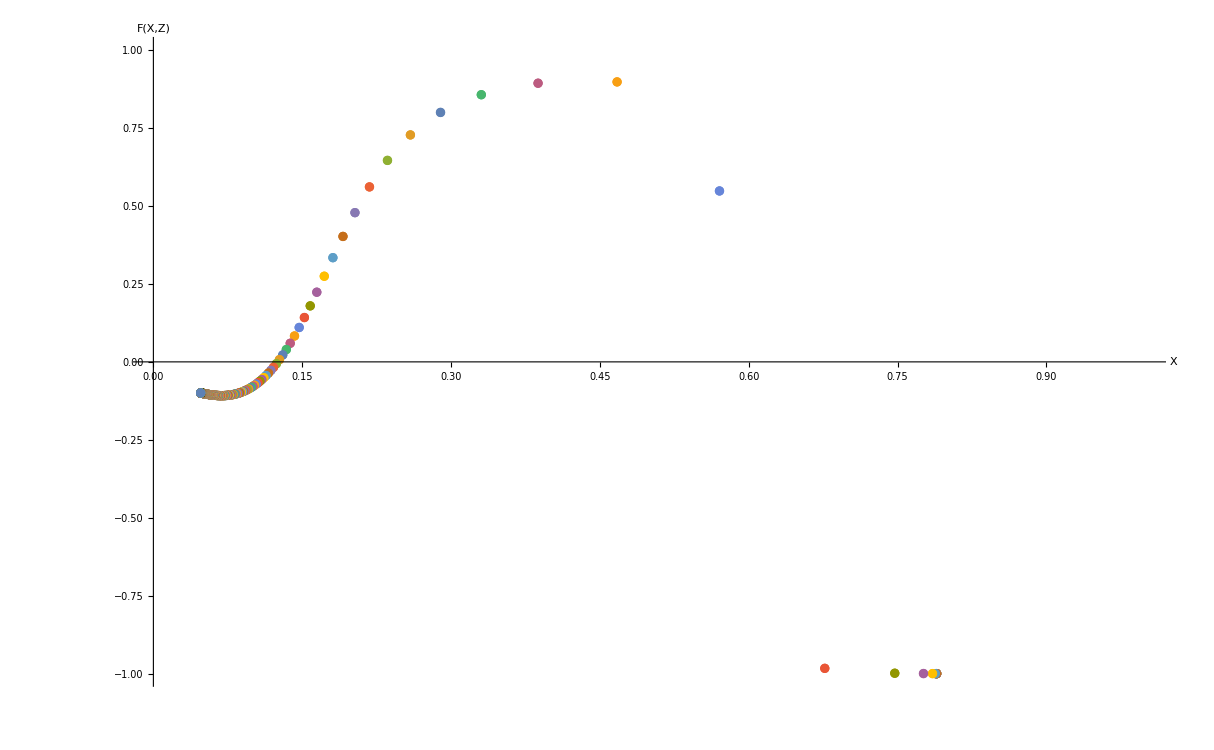

```mathematica
(*Plot X vs the remaining equation when Y' = 0*)
(*When F(X,Z) = 0, an Einstein point exists*)
EinsteinPlotTwoEinsteinPointsCompactRepellor=ListPlot[EinsteinPointSolutionsTwoEinsteinPointsCompactRepellor,PlotRange->{{0,1},{-1,1}},AxesLabel->{"X","F(X,Z)"}]
```

#### Plot the X-Y-Z Phase Space

```mathematica
(*Find the maximum value of K for this combination of X0 and Z0 so that Y0 is not imaginary*)
KMaxTwoEinsteinPointsCompactRepellor=K/.Flatten[Solve[Y0TwoEinsteinPointsRepellor==0,K]]
```

0.0483863

```mathematica
(*Solve trajTwoEinsteinPointsCompact[K] for different values of K*)
```

```mathematica
solTwoEinsteinPointsCompactRepellor[1]=trajTwoEinsteinPointsCompactRepellor[-.1]
```

NDSolve::mxst: Maximum number of 530958 steps reached at the point t == -2.63761.

{{X1→InterpolatingFunction[{{-2.63761, 100.}}, <>],Y1→InterpolatingFunction[{{-2.63761, 100.}}, <>],Z1→InterpolatingFunction[{{-2.63761, 100.}}, <>]}}

```mathematica
solTwoEinsteinPointsCompactRepellor[2]=trajTwoEinsteinPointsCompactRepellor[KMaxTwoEinsteinPointsCompactRepellor]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsCompactRepellor[3]=trajTwoEinsteinPointsCompactRepellor[0.02]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the trajectories for the different values of K given above*)
```

```mathematica
trajTwoEinsteinPointsCompactXYZRepellor[1]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactRepellor[1],{t,-2.63,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsCompactXYZRepellor[2]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactRepellor[2],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
trajTwoEinsteinPointsCompactXYZRepellor[3]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactRepellor[3],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
(*Solve the X-Y-Z system using the centre Einstein fixed point for X0 and Z0 to plot a cyclic trajectory*)
CyclicTrajTwoEinsteinPointsCompactRepellor=NDSolve[{deXt,deYt,deZt,X1[0]==EinsteinPoint2TwoEinsteinPointsCompactRepellor[[1]],Y1[0]==0.5,Z1[0]==EinsteinPoint2TwoEinsteinPointsCompactRepellor[[3]]},{X1,Y1,Z1},{t,-100,100}];
```

```mathematica
(*Plot the cyclic trajectory*)
trajTwoEinsteinPointsCompactXYZRepellor[4]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.CyclicTrajTwoEinsteinPointsCompactRepellor,{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajTwoEinsteinPointsCaseCompactRepellor=Table[trajTwoEinsteinPointsCompactXYZRepellor[i],{i,1,4}];
```

```mathematica
(*Plot the Einstein fixed points*)
EinsteinFixedPointsTwoEinsteinPointsCompactRepellor=ListPointPlot3D[{EinsteinPoint1TwoEinsteinPointsCompactRepellor,EinsteinPoint2TwoEinsteinPointsCompactRepellor},PlotStyle->Black];
```

```mathematica
(*Solve the X-Y-Z system around the Einstein fixed point to plot the Closed Friedmann Separatrix (CFS)*)
CFSTwoEinsteinPointsSolCompactRepellor=NDSolve[{deXt,deYt,deZt,X1[0]==EinsteinPoint1TwoEinsteinPointsCompactRepellor[[1]],Y1[0]==-0.0005,Z1[0]==EinsteinPoint1TwoEinsteinPointsCompactRepellor[[3]]},{X1,Y1,Z1},{t,-100,100}]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the CFS*)
CFSTwoEinsteinPointsCompactRepellor=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.CFSTwoEinsteinPointsSolCompactRepellor,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Show the X-Y-Z phase space*)
Show[trajTwoEinsteinPointsCaseCompactRepellor,CFSTwoEinsteinPointsCompactRepellor,EinsteinFixedPointsTwoEinsteinPointsCompactRepellor,AccnXYZRepellor,FPsXYZRepellor,CompactFPShowXYZRepellor,XYZCompactFormat]
```

-Graphics3D-

#### Plot the X-Z Projection

```mathematica
(*Plot one solution on the X-Z plane*)
trajTwoEinsteinPointsCompactXZRepellor=ParametricPlot[Evaluate[{{Z1[t],X1[t]}}/.solTwoEinsteinPointsCompactRepellor[1],{t,-2.63,100},PlotStyle -> {{Black,Thick, Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.03,0,.03,0},1]]],Arrow[x]};
```

```mathematica
(*Plot the Einstein fixed points on the X-Z plane*)
EinsteinFixedPointsTwoEinsteinPointsCompactXZRepellor=ListPlot[{{EinsteinPoint1TwoEinsteinPointsCompactRepellor[[3]],EinsteinPoint1TwoEinsteinPointsCompactRepellor[[1]]},{EinsteinPoint2TwoEinsteinPointsCompactRepellor[[3]],EinsteinPoint2TwoEinsteinPointsCompactRepellor[[1]]}},PlotStyle->Black];
```

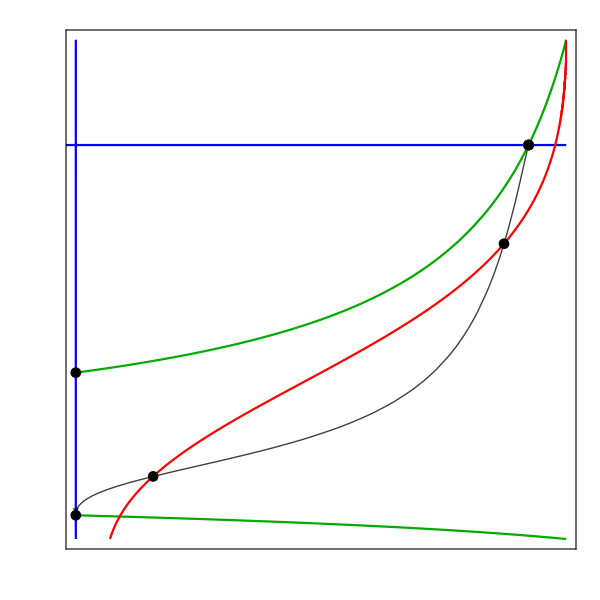

```mathematica
(*Show the X-Z phase space with the a'' = 0 (red), X' = 0 (green) and Z' = 0 (purple) curves*)
Show[trajTwoEinsteinPointsCompactXZRepellor,XLineRepellor,ZLineRepellor,AccnXZRepellor,EinsteinFixedPointsTwoEinsteinPointsCompactXZRepellor,FPsXZRepellor,CompactFPShowXZRepellor,XZCompactFormat]
```

## Investigate system when ℛ = 10^(-120)

### Set-up

```mathematica
(*Clear variables*)
Clear[q,ϵ,ℛ,wx]
```

```mathematica
(*Set parameter values*)
q=0.8;
ϵ=-1;
ℛ=10^(-120);
wx=-1+2*ℛ;
```

```mathematica
(*Define Ωx0 and Ωm0 using data from Planck 2018*)
Ωx0=0.6889;
Ωm0=0.3111;
```

```mathematica
(*Set a value for α, which sets the value of the low energy cosmological constant*)
α=0.5;
```

```mathematica
(*Define the initial conditions, where a0 = 1 and K is defined as k/ρ* *)

x0=ℛ/α;
y0=Sqrt[x0/3+Z0/(3*(1-Z0))-K];
```

```mathematica
(*Compactify the initial conditions*)

X0=x0/(1+x0);
Y0=y0/Sqrt[1+y0^2];
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y in terms of time, t*)
deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*(X1[t]-ℛ*(1-X1[t]))*((1+wx)*(1-X1[t])+ϵ*X1[t])-q*X1[t]*(1-X1[t])*(Z1[t]/(1-Z1[t]))*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((Z1[t]/(1-Z1[t]))+(X1[t]/(1-X1[t]))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X1[t]^2/((1-X1[t])^2))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2))) + q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
```

### Find the value of z0 to give the limiting case

```mathematica
(*Fix z0 using the density parameters*)
z0RealisticℛRepellor=Ωm0*ℛ/(Ωx0*α)
```

9.03179×10^-121

```mathematica
(*Compactify z0*)
Z0RealisticℛRepellor=z0RealisticℛRepellor/(1+z0RealisticℛRepellor)
```

9.03179×10^-121

```mathematica
(*Substitute Z0Realisticℛ into Y0 for this case*)
Y0RealisticℛRepellor=Y0/.Z0->Z0RealisticℛRepellor
```

(√(9.67726×10^-121-K))/(√(1.-K))

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajRealisticℛRepellor[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0RealisticℛRepellor,Z1[0]==Z0RealisticℛRepellor},{X1,Y1,Z1},{t,-100,100}];
```

NDSolve::ndinnt: Initial condition (√(9.67726×10^-121-1. K))/(√(1.-1. K)) is not a number or a rectangular array of numbers.

```mathematica
(*Set-up tables of all X1 and Z1 values*)
XTableRealisticℛRepellor=Table[X1[i]/.trajRealisticℛRepellor[0],{i,-100,100,.1}];
ZTableRealisticℛRepellor=Table[Z1[i]/.trajRealisticℛRepellor[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0*)
EinsteinPlotValuesRealisticℛRepellor=(ZTableRealisticℛRepellor/(1-ZTableRealisticℛRepellor))+(XTableRealisticℛRepellor/(1-XTableRealisticℛRepellor))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableRealisticℛRepellor/(1-XTableRealisticℛRepellor))^2;
```

```mathematica
(*Compactify EinsteinPlotValuesRealisticℛ*)
EinsteinPlotRealisticℛCompactRepellor=EinsteinPlotValuesRealisticℛRepellor/Sqrt[1+EinsteinPlotValuesRealisticℛRepellor^2];
```

```mathematica
(*Find the maximum value of EinsteinPlotRealisticℛCompact*)
(*As EinsteinPlotRealisticℛCompact is always less than zero there are no Einstein points when z0 is defined using the density parameters*)
Max[EinsteinPlotRealisticℛCompactRepellor]
```

-3.09682×10^-120

## Improper Node

In this case, the two eigenvalues of the repellor fixed point are the same. This occurs when q = 0.889947 or when q= 5.18699. We choose to plot the  q = 0.889947 case as the phase space is more readable.

## Plot the full x-z and x-y-z phase spaces

### Non-Compact x - z Phase Space

```mathematica
(*Clear variables*)
Clear[q,ϵ,ℛ,wx]
```

```mathematica
(*Load MaTeX to typeset axis labels using LaTeX*)
<<MaTeX`
```

```mathematica
(*Define a format style for the x-z phase spaces*)
xzFormat={Frame->{True},FrameLabel->{MaTeX["z",FontSize->24],Rotate[MaTeX["x",FontSize->24],300]},FrameTicks->{{Table[{x,MaTeX[x,"DisplayStyle"->False,FontSize->24]},{x,1Range[-1,6]}],None},{Table[{z,MaTeX[z,"DisplayStyle"->False,FontSize->24]},{z,5Range[0,20]}],None}},ImageSize->{600,600},PlotRangePadding->{0.15,0}};
```

```mathematica
(*Set parameter values such that wx > -0.25 and only the repellor and attractor fixed points satisfy z >= 0*)
wx=-0.5;
q=0.8899466324480608;
ϵ=-1;
ℛ=0.05;
```

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, and dark matter, z*)
dex:=x'=-3*(x-ℛ)*(1+wx+ϵ*x)-q*x*z
dez:=z'=-3*z + q*x*z
```

```mathematica
(*Define the system of differential equations for the dark energy, x, and dark matter, z, in terms of a time variable*)
dext:=x1'[t]==-3*(x1[t]-ℛ)*(1+wx+ϵ*x1[t])-q*x1[t]*z1[t]
dezt:=z1'[t]==-3*z1[t] + q*x1[t]*z1[t]
```

```mathematica
(*Find the fixed points of the system*)
FPsxzNode=Solve[{dez==0,dex==0},{z,x}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{z→0.,x→0.05},{z→0.,x→0.5},{z→9.53452,x→3.37099}}

```mathematica
(*Extract the values of the fixed points and put them into one variable name*)
FPxzNode[1]={z/.FPsxzNode[[1,1]],x/.FPsxzNode[[1,2]]};
FPxzNode[2]={z/.FPsxzNode[[2,1]],x/.FPsxzNode[[2,2]]};
FPxzNode[3]={z/.FPsxzNode[[3,1]],x/.FPsxzNode[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPxzTableNode=Table[FPxzNode[i],{i,1,3}];
```

```mathematica
(*Find the 2D Jacobian matrix. D[] differentiates each expression*)
JxzNode=Simplify[{{D[dez,z],D[dez,x]}, {D[dex,z],D[dex,x]}}];
JxzNode//MatrixForm
```

(-3+0.889947 x | 0.889947 z
-0.889947 x | 6. (-0.275+x-0.148324 z))

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableNode=Table[{FPxzTableNode[[i]]//MatrixForm,Simplify[JxzNode/.{z->FPxzTableNode[[i,1]],x->FPxzTableNode[[i,2]]}]//MatrixForm,Eigenvalues[JxzNode/.{z->FPxzTableNode[[i,1]],x->FPxzTableNode[[i,2]]}]//MatrixForm,Eigenvectors[JxzNode/.{z->FPxzTableNode[[i,1]],x->FPxzTableNode[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTablexzNode=TableForm[FPTableNode,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.
0.05) | (-2.9555 | 0.
-0.0444973 | -1.35) | (-2.9555
-1.35) | (0.999616 | 0.0277049
0. | 1.)
(0.
0.5) | (-2.55503 | 0.
-0.444973 | 1.35) | (-2.55503
1.35) | (0.99357 | 0.113216
0. | 1.)
(9.53452
3.37099) | (0. | 8.48521
-3. | 10.0907) | (5.04536
5.04536) | (-0.859532 | -0.511083
-0.859532 | -0.511083)

```mathematica
(*Plot the fixed points*)
FPsxzNode=ListPlot[FPxzTableNode,PlotStyle->Black];
```

```mathematica
(*Plot the phase space for the dark energy and dark matter*)
PhaseSpacexzNode=StreamPlot[{dez,dex},{z,0,20},{x,-1,6}];
```

```mathematica
(*Plot the curves where z' = 0*)
zLineNode=ContourPlot[-3*z + q*x*z==0,{z,-.1,20},{x,-1,6},ContourStyle->Blue,PlotPoints->300];
```

```mathematica
(*Plot the curves where x' = 0*)
xLineNode=ContourPlot[-3*(x-ℛ)*(1+wx+ϵ*x)-q*x*z==0,{z,-.1,20},{x,-1,6},ContourStyle->Darker[Green],PlotPoints->300];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
AccnxzNode=ContourPlot[z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2==0,{z,0,20},{x,-1,6},ContourStyle->Red,PlotPoints->300];
```

```mathematica
(*Solve the z-x system around the saddle fixed point to plot the separatrix betweent he repellor and the saddle fixed points*)
SeparatrixNode=NDSolve[{dezt,dext,z1[0]==0.0001,x1[0]==0.5},{z1,x1},{t,-100,100}]
```

{{z1→InterpolatingFunction[…],x1→InterpolatingFunction[…]}}

```mathematica
(*Plot the separatrix*)
SeparatrixPlotNode=ParametricPlot[Evaluate[{{z1[t],x1[t]}}/.SeparatrixNode,{t,-100,2.84},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->{{0,7},{-1,4}}];
```

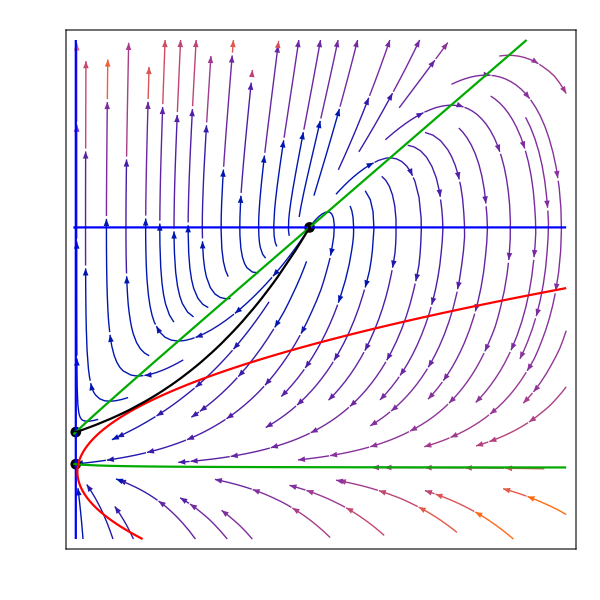

```mathematica
(*Show the plots of the phase space and its components together*)
Show[PhaseSpacexzNode,FPsxzNode,zLineNode,xLineNode,AccnxzNode,SeparatrixPlotNode,xzFormat,PlotRange->{{0,20},{-1,6}}]
```

### Non-Compact x - y - z Phase Space

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, dark matter, z, and the Hubble parameter, y*)
dex:=x'=-3*y*(x-ℛ)*(1+wx+ϵ*x)-q*x*y*z
dey:=y'=-y^2-(1/6)*(z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2) 
dez:=z'=-3*y*z + q*x*y*z
```

```mathematica
(*Find the fixed points of the system*)
FPsNode=Solve[{dex==0,dey==0,dez==0},{x,y,z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0.,z→0.025 (3.+14. x+120. x^2)},{x→0.05,y→-0.129099,z→0.},{x→0.05,y→0.129099,z→0.},{x→0.5,y→-0.408248,z→0.},{x→0.5,y→0.408248,z→0.},{x→3.37099,y→-2.07409,z→9.53452},{x→3.37099,y→2.07409,z→9.53452}}

```mathematica
(*Extract the values for the fixed points and put them into a common variable name*)
FPNode[1]={x,y/.FPsNode[[1,1]],z/.FPsNode[[1,2]]};
FPNode[2]={x/.FPsNode[[2,1]],y/.FPsNode[[2,2]],z/.FPsNode[[2,3]]};
FPNode[3]={x/.FPsNode[[3,1]],y/.FPsNode[[3,2]],z/.FPsNode[[3,3]]};
FPNode[4]={x/.FPsNode[[6,1]],y/.FPsNode[[6,2]],z/.FPsNode[[6,3]]};
FPNode[5]={x/.FPsNode[[7,1]],y/.FPsNode[[7,2]],z/.FPsNode[[7,3]]};
FPNode[6]={x/.FPsNode[[4,1]],y/.FPsNode[[4,2]],z/.FPsNode[[4,3]]};
FPNode[7]={x/.FPsNode[[5,1]],y/.FPsNode[[5,2]],z/.FPsNode[[5,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPsNode=Table[FPNode[i],{i,1,7}];
```

```mathematica
(*Find the 3D Jacobian matrix. D[] differentiates each expression*)
JxyzNode=Simplify[{{D[dex,x],D[dex,y],D[dex,z]}, {D[dey,x],D[dey,y],D[dey,z]},{D[dez,x],D[dez,y],D[dez,z]}}];
JxyzNode//MatrixForm
```

(y (-1.65+6. x-0.889947 z) | 3. (0.025+x^2+x (-0.55-0.296649 z)) | -0.889947 x y
0.0583333+x | -2 y | -1/6
0.889947 y z | (-3+0.889947 x) z | (-3+0.889947 x) y)

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableNode=Table[{FPsNode[[i]]//MatrixForm,Simplify[JxyzNode/.{x->FPsNode[[i,1]],y->FPsNode[[i,2]],z->FPsNode[[i,3]]}]//MatrixForm,Eigenvalues[JxyzNode/.{x->FPsNode[[i,1]],y->FPsNode[[i,2]],z->FPsNode[[i,3]]}]//MatrixForm,Eigenvectors[JxyzNode/.{x->FPsNode[[i,1]],y->FPsNode[[i,2]],z->FPsNode[[i,3]]}]//MatrixForm},{i,1,7}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableNode=TableForm[FPTableNode,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(x
0.
0.025 (3.+14. x+120. x^2)) | (0. | 0.075-1.71675 x+2.68852 x^2-2.66984 x^3 | 0.
0.0583333+x | 0. | -1/6
0. | -0.225-0.983254 x-8.68852 x^2+2.66984 x^3 | 0.) | (0
-√(0.041875+0.138732 x-0.111829 x^2+2.0878 x^3-2.66984 x^4)
√(0.041875+0.138732 x-0.111829 x^2+2.0878 x^3-2.66984 x^4)) | (0.166667/(0.0583333+x) | 0 | 1.
-(1. (-0.00163868+0.00941761 x+0.584273 x^2-0.948663 x^3+1. x^4))/((0.0583333+x) (-0.0842747-0.368282 x-3.25432 x^2+1. x^3)) | -(0.374554 √(0.041875+0.138732 x-0.111829 x^2+2.0878 x^3-2.66984 x^4))/(-0.0842747-0.368282 x-3.25432 x^2+1. x^3) | 1.
-(1. (-0.00163868+0.00941761 x+0.584273 x^2-0.948663 x^3+1. x^4))/((0.0583333+x) (-0.0842747-0.368282 x-3.25432 x^2+1. x^3)) | (0.374554 √(0.041875+0.138732 x-0.111829 x^2+2.0878 x^3-2.66984 x^4))/(-0.0842747-0.368282 x-3.25432 x^2+1. x^3) | 1.)
(0.05
-0.129099
0.) | (0.174284 | 2.08167×10^-17 | 0.00574458
0.108333 | 0.258199 | -1/6
0. | 0. | 0.381554) | (0.381554
0.258199
0.174284) | (0.0166795 | -0.798466 | 0.601809
-1.15126×10^-16 | -1. | 0.
-0.612372 | 0.790569 | 0.)
(0.05
0.129099
0.) | (-0.174284 | 2.08167×10^-17 | -0.00574458
0.108333 | -0.258199 | -1/6
0. | 0. | -0.381554) | (-0.381554
-0.258199
-0.174284) | (0.0166795 | 0.798466 | 0.601809
-1.15126×10^-16 | 1. | 0.
0.612372 | 0.790569 | 0.)
(3.37099
-2.07409
9.53452) | (-20.929 | 5.32907×10^-15 | 6.22226
3.42932 | 4.14817 | -1/6
-17.5991 | 0. | 0.) | (-10.4645
-10.4645
4.14817) | (-0.508011 | 0.109476 | -0.854365
-0.508011 | 0.109476 | -0.854365
2.99679×10^-17 | 1. | -9.09151×10^-16)
(3.37099
2.07409
9.53452) | (20.929 | 5.32907×10^-15 | -6.22226
3.42932 | -4.14817 | -1/6
17.5991 | 0. | 0.) | (10.4645
10.4645
-4.14817) | (0.508011 | 0.109476 | 0.854365
-0.508011 | -0.109476 | -0.854365
2.99679×10^-17 | -1. | -9.09151×10^-16)
(0.5
-0.408248
0.) | (-0.551135 | 1.66533×10^-16 | 0.18166
0.558333 | 0.816497 | -1/6
0. | 0. | 1.04309) | (1.04309
0.816497
-0.551135) | (0.103173 | -0.411761 | 0.905432
-1.7255×10^-16 | -1. | 0.
-0.92582 | 0.377964 | 0.)
(0.5
0.408248
0.) | (0.551135 | 1.66533×10^-16 | -0.18166
0.558333 | -0.816497 | -1/6
0. | 0. | -1.04309) | (-1.04309
-0.816497
0.551135) | (0.103173 | 0.411761 | 0.905432
-1.7255×10^-16 | 1. | 0.
0.92582 | 0.377964 | 0.)

```mathematica
(*Plot the line of Einstein fixed points*)
EinsteinPointLineNode=ParametricPlot3D[{FPNode[1][[1]],FPNode[1][[2]],FPNode[1][[3]]},{x,0,15},PlotStyle->Red];
```

```mathematica
(*Plot the fixed points of the system*)
FPsxyzNode=ListPointPlot3D[Table[FPNode[i],{i,2,5}],PlotStyle->Black];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
AccnxyzNode=ContourPlot3D[z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2==0,{x,0,6},{y,-10,10},{z,0,20},ContourStyle->{Red,Opacity[0.25]},Mesh->None];
```

```mathematica
(*Plot the x-y-z phase space*)
PhaseSpacexyzNode=StreamPlot3D[{dex,dey,dez},{x,0,6},{y,-5,5},{z,0,20},AxesLabel->{"x","y","z"}];
```

```mathematica
(*Show the phase space and its components together*)
Show[PhaseSpacexyzNode,FPsxyzNode,EinsteinPointLineNode,AccnxyzNode,AxesLabel->{MaTeX["x",FontSize->20],MaTeX["y",FontSize->20],MaTeX["z",FontSize->20]},Ticks->{{0.,5.},{-5.,0.,1.,5.},{0.,5.,10.,15.,20.}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->20}]
```

-Graphics3D-

## Plot the constant x0 and z0 surfaces

Trajectories are plotted on a constant x0-z0 surface, where x0 is fixed for all cases and z0 is fixed for each phase space to give a different number of Einstein fixed points. k and y0 differ for each trajectory in each phase space.

### Set-up for the phase spaces

```mathematica
(*Define a format for the x-y-z phase spaces*)
xyzFormat={AxesLabel->{MaTeX["x",FontSize->20],MaTeX["y",FontSize->20],MaTeX["z",FontSize->20]},Ticks->{{0.,5.,10.},{-5.,0.,5.},{0.,5.,10.,15.,20.}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->20}};
```

```mathematica
(*Define the system of differential equations for the dark energy, x, dark matter, z, and Hubble parameter, y, in terms of a time variable*)
dext:=x1'[t]==-3*y1[t]*(x1[t]-ℛ)*(1+wx+ϵ*x1[t])-q*x1[t]*y1[t]*z1[t]
deyt:=y1'[t]==-y1[t]^2-(1/6)*(z1[t]+x1[t]*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x1[t]^2) 
dezt:=z1'[t]==-3*y1[t]*z1[t] + q*x1[t]*y1[t]*z1[t]
```

```mathematica
(*Define Ωx0 and Ωm0 using data from Planck 2018*)
Ωx0=0.6889;
Ωm0=0.3111;
```

```mathematica
(*Set a value for α, which sets the value of the low energy cosmological constant*)
α=0.5;
```

```mathematica
(*Define the initial conditions, where a0 = 1 and K is defined as k/ρ* *)

x0=ℛ/α;
y0=Sqrt[x0/3+z0/3-K];
```

```mathematica
(*Define values of K using the range of Ωk0 allowed by Planck 2018*)
Ωk0Open=0.003;
Ωk0Closed=-0.001;

KDensityParametersOpen=-Ωk0Open*ℛ/(3*α*Ωx0)
KDensityParametersClosed=-Ωk0Closed*ℛ/(3*α*Ωx0)
```

-0.000145159

0.0000483863

### Two Einstein Fixed Points

#### Find the Einstein Fixed Points

```mathematica
(*Fix z0 using the density parameters. In this case there are two Einstein fixed points*)
z0TwoEinsteinPointsNode=Ωm0*ℛ/(Ωx0*α)
```

0.0451589

```mathematica
(*Substitute z0TwoEinsteinPoints into y0 for this case*)
y0TwoEinsteinPointsNode=y0/.z0->z0TwoEinsteinPointsNode
```

√(0.0483863-K)

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajTwoEinsteinPointsNode[K_]=NDSolve[{dext,deyt,dezt,x1[0]==x0,y1[0]==y0TwoEinsteinPointsNode,z1[0]==z0TwoEinsteinPointsNode},{x1,y1,z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition √(0.0483863-1. K) is not a number or a rectangular array of numbers.

NDSolve[{x1'[t]==-3 (0.5-x1[t]) (-0.05+x1[t]) y1[t]-0.889947 x1[t] y1[t] z1[t],y1'[t]==-y1[t]^2+1/6 (0.075+0.35 x1[t]+3 x1[t]^2-z1[t]),z1'[t]==-3 y1[t] z1[t]+0.889947 x1[t] y1[t] z1[t],x1[0]==0.1,y1[0]==√(0.0483863-K),z1[0]==0.0451589},{x1,y1,z1},{t,-100,100}]

```mathematica
(*Set-up tables of x1 and z1 values to be used to find the x and z value of the first Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
xTableSol1TwoEinsteinPointsNode=Table[x1[i]/.trajTwoEinsteinPointsNode[0],{i,-2,100,.01}];
zTableSol1TwoEinsteinPointsNode=Table[z1[i]/.trajTwoEinsteinPointsNode[0],{i,-2,100,.01}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol1TwoEinsteinPointsNode=(zTableSol1TwoEinsteinPointsNode)+(xTableSol1TwoEinsteinPointsNode)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol1TwoEinsteinPointsNode)^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol1TwoEinsteinPoints that is closest to zero. When EinsteinPlotValuesSol1TwoEinsteinPoints = 0 (y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints1Node=Flatten[Nearest[EinsteinPlotValuesSol1TwoEinsteinPointsNode,0]]
```

{-0.000156718}

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints1 in the EinsteinPlotValuesSol1TwoEinsteinPoints*)
PositionNearestToZeroTwoEinsteinPoints1Node=Flatten[Position[EinsteinPlotValuesSol1TwoEinsteinPointsNode,NearestToZeroTwoEinsteinPoints1Node]]
```

{15}

```mathematica
(*Find the Einstein point by finding the x and z values in xTableSol1TwoEinsteinPoints and zTableSol1TwoEinsteinPoints at PositionNearestToZeroTwoEinsteinPoints1*)
EinsteinPoint1TwoEinsteinPointsNode=Flatten[{xTableSol1TwoEinsteinPointsNode[[PositionNearestToZeroTwoEinsteinPoints1Node]],0,zTableSol1TwoEinsteinPointsNode[[PositionNearestToZeroTwoEinsteinPoints1Node]]}]
```

{0.144513,0,0.188075}

```mathematica
(*Set-up tables of x1 and z1 values to be used to find the x and z value of the second Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
xTableSol2TwoEinsteinPointsNode=Table[x1[i]/.trajTwoEinsteinPointsNode[0],{i,-5.6,-3.2,.001}];
zTableSol2TwoEinsteinPointsNode=Table[z1[i]/.trajTwoEinsteinPointsNode[0],{i,-5.6,-3.2,.001}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol2TwoEinsteinPointsNode=(zTableSol2TwoEinsteinPointsNode)+(xTableSol2TwoEinsteinPointsNode)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol2TwoEinsteinPointsNode)^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol2TwoEinsteinPoints that is closest to zero. When EinsteinPlotValuesSol2TwoEinsteinPoints = 0 (y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints2Node=Flatten[Nearest[EinsteinPlotValuesSol2TwoEinsteinPointsNode,0]]
```

{-0.0104668}

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints2 in the EinsteinPlotValuesSol2TwoEinsteinPoints array*)
PositionNearestToZeroTwoEinsteinPoints2Node=Flatten[Position[EinsteinPlotValuesSol2TwoEinsteinPointsNode,NearestToZeroTwoEinsteinPoints2Node]]
```

{1708}

```mathematica
(*Find the Einstein point by finding the x and z values in xTableSol2TwoEinsteinPoints and zTableSol2TwoEinsteinPoints at PositionNearestToZeroTwoEinsteinPoints2*)
EinsteinPoint2TwoEinsteinPointsNode=Flatten[{xTableSol2TwoEinsteinPointsNode[[PositionNearestToZeroTwoEinsteinPoints2Node]],0,zTableSol2TwoEinsteinPointsNode[[PositionNearestToZeroTwoEinsteinPoints2Node]]}]
```

{1.31462,0,5.70934}

```mathematica
(*Put the Einstein fixed points into a common variable name*)
EinsteinPointTwoEPtsNode[1]=EinsteinPoint1TwoEinsteinPointsNode;
EinsteinPointTwoEPtsNode[2]=EinsteinPoint2TwoEinsteinPointsNode;
```

```mathematica
(*Put the Einstein fixed points into a table*)
EinsteinPointsTwoEPtsNode=Table[EinsteinPointTwoEPtsNode[i],{i,1,2}];
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each Einstein fixed point*)
EinsteinPointTableTwoEinsteinPointsNode=Table[{EinsteinPointsTwoEPtsNode[[i]]//MatrixForm,Simplify[JxyzNode/.{x->EinsteinPointsTwoEPtsNode[[i,1]],y->EinsteinPointsTwoEPtsNode[[i,2]],z->EinsteinPointsTwoEPtsNode[[i,3]]}]//MatrixForm,Eigenvalues[JxyzNode/.{x->EinsteinPointsTwoEPtsNode[[i,1]],y->EinsteinPointsTwoEPtsNode[[i,2]],z->EinsteinPointsTwoEPtsNode[[i,3]]}]//MatrixForm,Eigenvectors[JxyzNode/.{x->EinsteinPointsTwoEPtsNode[[i,1]],y->EinsteinPointsTwoEPtsNode[[i,2]],z->EinsteinPointsTwoEPtsNode[[i,3]]}]//MatrixForm},{i,1,2}];
```

```mathematica
(*Use TableForm to display the Einstein fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableTwoEinsteinPointsNode=TableForm[EinsteinPointTableTwoEinsteinPointsNode,TableHeadings->{None,{"Einstein Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Einstein Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.144513
0
0.188075) | (0. | -0.124983 | 0.
0.202846 | 0 | -1/6
0. | -0.540037 | 0.) | (0.254271
-0.254271
-4.9311×10^-18) | (0.204941 | -0.416942 | 0.885527
-0.204941 | -0.416942 | -0.885527
0.634837 | 4.73413×10^-18 | 0.772646)
(1.31462
0
5.70934) | (0. | -3.58904 | 0.
1.37295 | 0 | -1/6
0. | -10.4484 | 0.) | (-2.82119×10^-16+1.78499 ⅈ
-2.82119×10^-16-1.78499 ⅈ
2.30343×10^-16+0. ⅈ) | (0.32071+6.26888×10^-17 ⅈ | 5.30369×10^-17-0.159503 ⅈ | 0.933651+0. ⅈ
0.32071-6.26888×10^-17 ⅈ | 5.30369×10^-17+0.159503 ⅈ | 0.933651+0. ⅈ
0.120508+0. ⅈ | -2.48329×10^-17+0. ⅈ | 0.992712+0. ⅈ)

```mathematica
(*Set-up tables of all x1 and z1 values*)
xTableSolTwoEinsteinPointsFullNode=Table[x1[i]/.trajTwoEinsteinPointsNode[0],{i,-6,100,.1}];
zTableSolTwoEinsteinPointsFullNode=Table[z1[i]/.trajTwoEinsteinPointsNode[0],{i,-6,100,.1}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0*)
EinsteinPlotValuesSolTwoEinsteinPointsFullNode=(zTableSolTwoEinsteinPointsFullNode)+(xTableSolTwoEinsteinPointsFullNode)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSolTwoEinsteinPointsFullNode)^2;
```

```mathematica
(*Merge the xTableSolTwoEinsteinPointsFull values and the EinsteinPlotValuesSolTwoEinsteinPointsFull values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsTwoEinsteinPointsNode=MapThread[h,{xTableSolTwoEinsteinPointsFullNode,EinsteinPlotValuesSolTwoEinsteinPointsFullNode}];
```

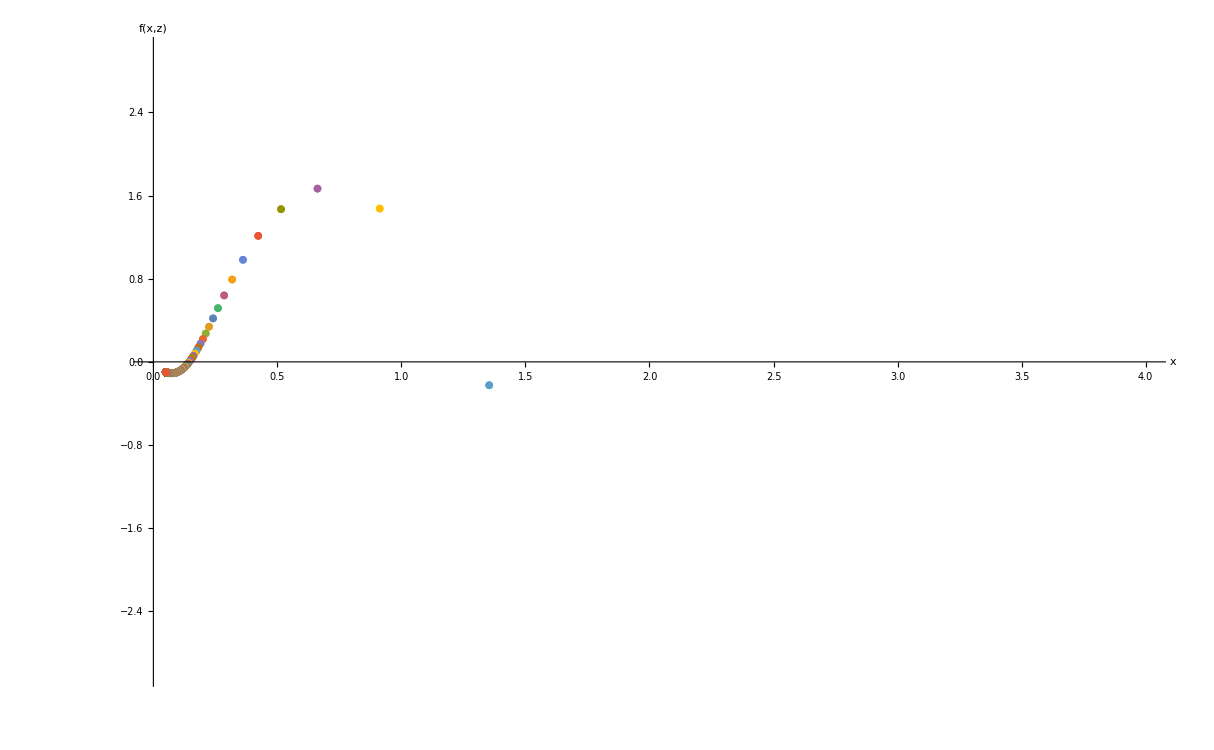

```mathematica
(*Plot x vs the remaining equation when y' = 0*)
(*When f(x,z) = 0, an Einstein point exists*)
EinsteinPlotTwoEinsteinPointsNode=ListPlot[EinsteinPointSolutionsTwoEinsteinPointsNode,PlotRange->{{0,4},{-3,3}},AxesLabel->{"x","f(x,z)"}]
```

### Plot the x-y-z Phase Space

```mathematica
(*Find the maximum value of K for this combination of x0 and z0 so that y0 is not imaginary*)
KMaxTwoEinsteinPointsNode=K/.Flatten[Solve[y0TwoEinsteinPointsNode==0,K]]
```

0.0483863

```mathematica
(*Solve trajTwoEinsteinPoints[K] for different values of K*)
```

```mathematica
solTwoEinsteinPointsNode[1]=trajTwoEinsteinPointsNode[-0.01]
```

NDSolve::ndsz: At t == -4.49423, step size is effectively zero; singularity or stiff system suspected.

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsNode[2]=trajTwoEinsteinPointsNode[0.01]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsNode[3]=trajTwoEinsteinPointsNode[-.1]
```

NDSolve::ndsz: At t == -2.64502, step size is effectively zero; singularity or stiff system suspected.

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsNode[4]=trajTwoEinsteinPointsNode[KMaxTwoEinsteinPointsNode]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the trajectories for the different values of K given above*)
```

```mathematica
trajTwoEinsteinPointsxyzNode[1]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsNode[1],{t,-4.44,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsxyzNode[2]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsNode[2],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsxyzNode[3]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsNode[3],{t,-2.61,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsxyzNode[4]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsNode[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75],Dashed}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
(*Solve the x-y-z system using the centre Einstein fixed point for x0 and z0 to plot a cyclic trajectory*)
CyclicTrajTwoEinsteinPointsNode=NDSolve[{dext,deyt,dezt,x1[0]==EinsteinPoint2TwoEinsteinPointsNode[[1]],y1[0]==0.436,z1[0]==EinsteinPoint2TwoEinsteinPointsNode[[3]]},{x1,y1,z1},{t,-100,100}];
```

```mathematica
(*Plot the cyclic trajectory*)
trajTwoEinsteinPointsxyzNode[5]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.CyclicTrajTwoEinsteinPointsNode,{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajTwoEinsteinPointsCaseNode=Table[trajTwoEinsteinPointsxyzNode[i],{i,1,5}];
```

```mathematica
(*Plot the Einstein fixed points*)
EinsteinFixedPointsTwoEinsteinPointsNode=ListPointPlot3D[{EinsteinPoint1TwoEinsteinPointsNode,EinsteinPoint2TwoEinsteinPointsNode},PlotStyle->Black];
```

```mathematica
(*Solve the x-y-z system around the Einstein fixed point to plot the Closed Friedmann Separatrix (CFS)*)
CFSTwoEinsteinPointsSolNode=NDSolve[{dext,deyt,dezt,x1[0]==EinsteinPoint1TwoEinsteinPointsNode[[1]],y1[0]==-0.0005,z1[0]==EinsteinPoint1TwoEinsteinPointsNode[[3]]},{x1,y1,z1},{t,-100,100}]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the CFS*)
CFSTwoEinsteinPointsNode=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.CFSTwoEinsteinPointsSolNode,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Show the x-y-z phase space*)
Show[trajTwoEinsteinPointsCaseNode,CFSTwoEinsteinPointsNode,EinsteinFixedPointsTwoEinsteinPointsNode,AccnxyzNode,FPsxyzNode,xyzFormat,PlotRange->{{0,5},{-5,5},{0,10}}]
```

-Graphics3D-

#### Plot the x-z Projection

```mathematica
(*Plot one solution on the x-z plane*)
trajTwoEinsteinPointsxzNode=ParametricPlot[Evaluate[{{z1[t],x1[t]}}/.solTwoEinsteinPointsNode[1],{t,-4.44,100},PlotStyle -> {{Black, Thick,Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.03,.03,0},1]]],Arrow[x]};;
```

```mathematica
(*Plot the Einstein fixed points on the x-z plane*)
EinsteinFixedPointsTwoEinsteinPointsxzNode=ListPlot[{{EinsteinPoint1TwoEinsteinPointsNode[[3]],EinsteinPoint1TwoEinsteinPointsNode[[1]]},{EinsteinPoint2TwoEinsteinPointsNode[[3]],EinsteinPoint2TwoEinsteinPointsNode[[1]]}},PlotStyle->Black];
```

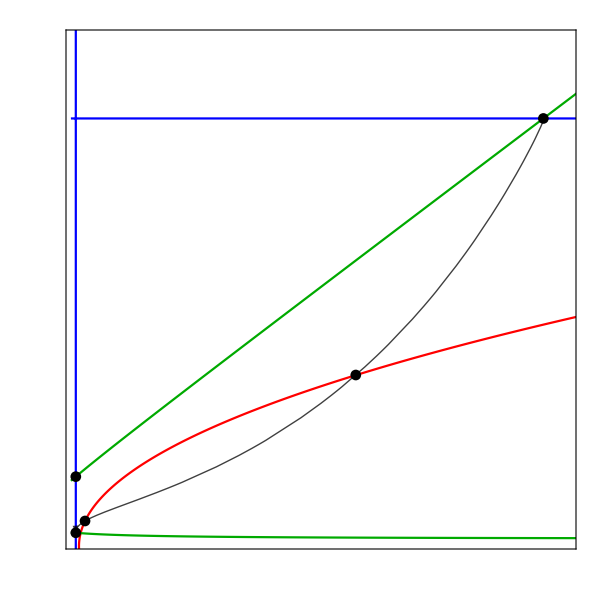

```mathematica
(*Show the x-z phase space with the a'' = 0 (red), x' = 0 (green) and z' = 0 (purple) curves*)
Show[trajTwoEinsteinPointsxzNode,AccnxzNode,xLineNode,zLineNode,FPsxzNode,EinsteinFixedPointsTwoEinsteinPointsxzNode,xzFormat,PlotRange->{{0,10},{0,4}}]
```

## Compact Phase Spaces: constant X0 and Z0 surfaces

Trajectories are plotted on a constant X0-Z0 surface, where X0 is fixed for all cases and Z0 is fixed for each phase space to give a different number of Einstein fixed points. k and Y0 differ for each trajectory in each phase space.

### Define parameter values and set-up initial conditions

```mathematica
(*Set parameter values*)
wx=-0.5;
q=0.8899466324480608;
ϵ=-1;
ℛ=0.05;
```

```mathematica
(*Define Ωx0 and Ωm0 using data from Planck 2018*)
Ωx0=0.6889;
Ωm0=0.3111;
```

```mathematica
(*Set a value for α, which sets the value of the low energy cosmological constant*)
α=0.5;
```

```mathematica
(*Define the initial conditions, where a0 = 1 and K is defined as k/ρ* *)

x0=ℛ/α;
y0=Sqrt[x0/3+Z0/(3*(1-Z0))-K];
```

```mathematica
(*Compactify the initial conditions*)

X0=x0/(1+x0);
Y0=y0/Sqrt[1+y0^2];
```

```mathematica
(*Define values of K using the range of Ωk0 allowed by Planck 2018*)
Ωk0Open=0.003;
Ωk0Closed=-0.001;

KDensityParametersOpen=-Ωk0Open*ℛ/(3*α*Ωx0)
KDensityParametersClosed=-Ωk0Closed*ℛ/(3*α*Ωx0)
```

-0.000145159

0.0000483863

### Set-up for the compact X-Y-Z system

```mathematica
(*Load MaTeX to typeset axis labels using LaTeX*)
<<MaTeX`
```

```mathematica
(*Define a format style for the X-Y-Z phase spaces*)
XYZCompactFormat={AxesLabel->{MaTeX["X",FontSize->22],MaTeX["Y",FontSize->22],MaTeX["Z",FontSize->22]},Ticks->{{0.,0.5,1.0},{-1,-0.5,0.,0.5,1.0},{0.,0.5,1.0}},PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->22}};
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y*)
deX:=X'=-3*(Y/((1-Y^2)^(1/2)))*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))*(Y/((1-Y^2)^(1/2)))
deY:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(X/(1-X))^2)
deZ:=Z'=-3*Z*(1-Z)*(Y/((1-Y^2)^(1/2))) + q*(X/(1-X))*Z*(1-Z)*(Y/((1-Y^2)^(1/2)))
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y in terms of time, t*)
deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*(X1[t]-ℛ*(1-X1[t]))*((1+wx)*(1-X1[t])+ϵ*X1[t])-q*X1[t]*(1-X1[t])*(Z1[t]/(1-Z1[t]))*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((Z1[t]/(1-Z1[t]))+(X1[t]/(1-X1[t]))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X1[t]^2/((1-X1[t])^2))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2))) + q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
```

```mathematica
(*Find the fixed points of the system*)
FPsXYZNode=Solve[{deX==0,deY==0,deZ==0},{X,Y,Z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Y→0.,Z→(3.+8. X+109. X^2)/(43.-72. X+149. X^2)},{X→0.333333,Y→-0.377964,Z→0.},{X→0.047619,Y→-0.128037,Z→0.},{X→-0.0366972-0.161791 ⅈ,Y→0.,Z→0.},{X→-0.0366972+0.161791 ⅈ,Y→0.,Z→0.},{X→0.047619,Y→0.128037,Z→0.},{X→0.333333,Y→0.377964,Z→0.},{X→0.771219,Y→-0.90077,Z→0.905074},{X→0.771219,Y→0.90077,Z→0.905074},{X→0.771219,Y→0.,Z→0.972486}}

```mathematica
(*Extract the values of the fixed points and put them into a common variable name*)
FPXYZNode[1]={X,Y/.FPsXYZNode[[1,1]],Z/.FPsXYZNode[[1,2]]};
FPXYZNode[2]={X/.FPsXYZNode[[4,1]],Y/.FPsXYZNode[[4,2]],Z/.FPsXYZNode[[4,3]]};
FPXYZNode[3]={X/.FPsXYZNode[[9,1]],Y/.FPsXYZNode[[9,2]],Z/.FPsXYZNode[[9,3]]};
FPXYZNode[4]={X/.FPsXYZNode[[8,1]],Y/.FPsXYZNode[[8,2]],Z/.FPsXYZNode[[8,3]]};FPXYZNode[5]={X/.FPsXYZNode[[5,1]],Y/.FPsXYZNode[[5,2]],Z/.FPsXYZNode[[5,3]]};
FPXYZNode[6]={X/.FPsXYZNode[[10,1]],Y/.FPsXYZNode[[10,2]],Z/.FPsXYZNode[[10,3]]};
FPXYZNode[7]={X/.FPsXYZNode[[2,1]],Y/.FPsXYZNode[[2,2]],Z/.FPsXYZNode[[2,3]]};
FPXYZNode[8]={X/.FPsXYZNode[[3,1]],Y/.FPsXYZNode[[3,2]],Z/.FPsXYZNode[[3,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPXYZTableNode=Table[FPXYZNode[i],{i,1,8}];
```

```mathematica
(*Find the 3D Jacobian matrix. D[] differentiates each expression*)
JCompactXYZNode=Simplify[{{D[deX,X],D[deX,Y],D[deX,Z]},{D[deY,X],D[deY,Y],D[deY,Z]},{D[deZ,X],D[deZ,Y],D[deZ,Z]}}];
JCompactXYZNode//MatrixForm
```

((Y (1.8-0.910053 Z+X (-9.45+7.67011 Z)))/(√(1-Y^2) (-1.+Z)) | (0.075+X^2 (4.725-3.83505 Z)+X (-1.8+0.910053 Z)-0.075 Z)/(√(1-Y^2) (-1.+Y^2) (-1.+Z)) | (0.889947 (-1.+X) X Y)/(√(1-Y^2) (-1.+Z)^2)
(0.941667 (0.0619469+1. X) √(1-Y^2) (-1.+Y^2))/(-1.+X)^3 | (Y (2.0375-2.5375 Z+Y^2 (-3.0375+3.5375 Z)+X (-3.9+Y^2 (5.9-6.9 Z)+4.9 Z)+X^2 (3.3625-3.8625 Z+Y^2 (-4.3625+4.8625 Z))))/((-1.+X)^2 √(1-Y^2) (-1.+Z)) | -((1-Y^2)^(3/2))/(6 (-1+Z)^2)
-(0.889947 Y (-1.+Z) Z)/((-1.+X)^2 √(1-Y^2)) | (Z (-3.+X (3.88995-3.88995 Z)+3. Z))/((-1.+X) √(1-Y^2) (-1.+Y^2)) | (Y (3.-6. Z+X (-3.88995+7.77989 Z)))/((-1.+X) √(1-Y^2)))

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableCompactNode=Table[{FPXYZTableNode[[i]]//MatrixForm,Simplify[JCompactXYZNode/.{X->FPXYZTableNode[[i,1]],Y->FPXYZTableNode[[i,2]],Z->FPXYZTableNode[[i,3]]}]//MatrixForm,Eigenvalues[JCompactXYZNode/.{X->FPXYZTableNode[[i,1]],Y->FPXYZTableNode[[i,2]],Z->FPXYZTableNode[[i,3]]}]//MatrixForm,Eigenvectors[JCompactXYZNode/.{X->FPXYZTableNode[[i,1]],Y->FPXYZTableNode[[i,2]],Z->FPXYZTableNode[[i,3]]}]//MatrixForm},{i,1,8}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableXYZNode=TableForm[FPTableCompactNode,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(X
0.
(3.+8. X+109. X^2)/(43.-72. X+149. X^2)) | (0. | (0.075-2.01675 X+8.28876 X^2-13.4971 X^3+7.1501 X^4)/(1.-2. X+1. X^2) | 0.
(-0.0583333-0.941667 X)/(-1.+X)^3 | 0. | -(2.3126 (0.288591-0.483221 X+1. X^2)^2)/((1.-2. X+1. X^2)^2)
0. | (0.0162155-0.0102155 X+0.504878 X^2-1.80791 X^3+2.06097 X^4-0.763937 X^5)/((-1.+X) (0.288591-0.483221 X+1. X^2)^2) | 0.) | (0
-(√(14957.3-335712. X-1.84987×10^6 X^2+6.39142×10^7 X^3-6.15185×10^8 X^4+3.6359×10^9 X^5-1.54809×10^10 X^6+5.0777×10^10 X^7-1.32804×10^11 X^8+2.82104×10^11 X^9-4.90788×10^11 X^10+6.99865×10^11 X^11-8.12958×10^11 X^12+7.58549×10^11 X^13-5.5498×10^11 X^14+3.06089×10^11 X^15-1.19203×10^11 X^16+2.90663×10^10 X^17-3.3186×10^9 X^18+128205./(1.-2. X+1. X^2)-(1.83688×10^6 X)/(1.-2. X+1. X^2)+(1.77347×10^7 X^2)/(1.-2. X+1. X^2)-(1.38321×10^8 X^3)/(1.-2. X+1. X^2)+(8.65886×10^8 X^4)/(1.-2. X+1. X^2)-(4.31319×10^9 X^5)/(1.-2. X+1. X^2)+(1.72327×10^10 X^6)/(1.-2. X+1. X^2)-(5.59853×10^10 X^7)/(1.-2. X+1. X^2)+(1.49764×10^11 X^8)/(1.-2. X+1. X^2)-(3.32892×10^11 X^9)/(1.-2. X+1. X^2)+(6.18052×10^11 X^10)/(1.-2. X+1. X^2)-(9.59701×10^11 X^11)/(1.-2. X+1. X^2)+(1.24302×10^12 X^12)/(1.-2. X+1. X^2)-(1.33362×10^12 X^13)/(1.-2. X+1. X^2)+(1.17116×10^12 X^14)/(1.-2. X+1. X^2)-(8.26601×10^11 X^15)/(1.-2. X+1. X^2)+(4.56417×10^11 X^16)/(1.-2. X+1. X^2)-(1.89353×10^11 X^17)/(1.-2. X+1. X^2)+(5.53388×10^10 X^18)/(1.-2. X+1. X^2)-(1.01277×10^10 X^19)/(1.-2. X+1. X^2)+(8.70771×10^8 X^20)/(1.-2. X+1. X^2)))/((-1.+X)^4 √(1.-2. X+1. X^2) (43.-72. X+149. X^2)^2)
(√(14957.3-335712. X-1.84987×10^6 X^2+6.39142×10^7 X^3-6.15185×10^8 X^4+3.6359×10^9 X^5-1.54809×10^10 X^6+5.0777×10^10 X^7-1.32804×10^11 X^8+2.82104×10^11 X^9-4.90788×10^11 X^10+6.99865×10^11 X^11-8.12958×10^11 X^12+7.58549×10^11 X^13-5.5498×10^11 X^14+3.06089×10^11 X^15-1.19203×10^11 X^16+2.90663×10^10 X^17-3.3186×10^9 X^18+128205./(1.-2. X+1. X^2)-(1.83688×10^6 X)/(1.-2. X+1. X^2)+(1.77347×10^7 X^2)/(1.-2. X+1. X^2)-(1.38321×10^8 X^3)/(1.-2. X+1. X^2)+(8.65886×10^8 X^4)/(1.-2. X+1. X^2)-(4.31319×10^9 X^5)/(1.-2. X+1. X^2)+(1.72327×10^10 X^6)/(1.-2. X+1. X^2)-(5.59853×10^10 X^7)/(1.-2. X+1. X^2)+(1.49764×10^11 X^8)/(1.-2. X+1. X^2)-(3.32892×10^11 X^9)/(1.-2. X+1. X^2)+(6.18052×10^11 X^10)/(1.-2. X+1. X^2)-(9.59701×10^11 X^11)/(1.-2. X+1. X^2)+(1.24302×10^12 X^12)/(1.-2. X+1. X^2)-(1.33362×10^12 X^13)/(1.-2. X+1. X^2)+(1.17116×10^12 X^14)/(1.-2. X+1. X^2)-(8.26601×10^11 X^15)/(1.-2. X+1. X^2)+(4.56417×10^11 X^16)/(1.-2. X+1. X^2)-(1.89353×10^11 X^17)/(1.-2. X+1. X^2)+(5.53388×10^10 X^18)/(1.-2. X+1. X^2)-(1.01277×10^10 X^19)/(1.-2. X+1. X^2)+(8.70771×10^8 X^20)/(1.-2. X+1. X^2)))/((-1.+X)^4 √(1.-2. X+1. X^2) (43.-72. X+149. X^2)^2)) | (-(2.45586 (-1.+X)^3 (0.288591-0.483221 X+1. X^2)^2)/((0.0619469+1. X) (1.-2. X+1. X^2)^2) | 0 | 1.
-(9.35955 (-4.5071×10^-6+0.000110175 X+0.000350596 X^2-0.0202731 X^3+0.224451 X^4-1.48562 X^5+7.0415 X^6-25.7262 X^7+75.2846 X^8-180.344 X^9+357.922 X^10-591.679 X^11+814.644 X^12-929.408 X^13+869.354 X^14-655.276 X^15+387.622 X^16-172.833 X^17+54.437 X^18-10.7586 X^19+1. X^20))/((-1.+X)^4 (0.0619469+1. X) (1.-2. X+1. X^2)^2 (0.288591-0.483221 X+1. X^2)^2 (0.0275229+0.0733945 X+1. X^2) (-0.771219+2.54244 X-2.77122 X^2+1. X^3)) | (0.0000589617 √(14957.3-335712. X-1.84987×10^6 X^2+6.39142×10^7 X^3-6.15185×10^8 X^4+3.6359×10^9 X^5-1.54809×10^10 X^6+5.0777×10^10 X^7-1.32804×10^11 X^8+2.82104×10^11 X^9-4.90788×10^11 X^10+6.99865×10^11 X^11-8.12958×10^11 X^12+7.58549×10^11 X^13-5.5498×10^11 X^14+3.06089×10^11 X^15-1.19203×10^11 X^16+2.90663×10^10 X^17-3.3186×10^9 X^18+128205./(1.-2. X+1. X^2)-(1.83688×10^6 X)/(1.-2. X+1. X^2)+(1.77347×10^7 X^2)/(1.-2. X+1. X^2)-(1.38321×10^8 X^3)/(1.-2. X+1. X^2)+(8.65886×10^8 X^4)/(1.-2. X+1. X^2)-(4.31319×10^9 X^5)/(1.-2. X+1. X^2)+(1.72327×10^10 X^6)/(1.-2. X+1. X^2)-(5.59853×10^10 X^7)/(1.-2. X+1. X^2)+(1.49764×10^11 X^8)/(1.-2. X+1. X^2)-(3.32892×10^11 X^9)/(1.-2. X+1. X^2)+(6.18052×10^11 X^10)/(1.-2. X+1. X^2)-(9.59701×10^11 X^11)/(1.-2. X+1. X^2)+(1.24302×10^12 X^12)/(1.-2. X+1. X^2)-(1.33362×10^12 X^13)/(1.-2. X+1. X^2)+(1.17116×10^12 X^14)/(1.-2. X+1. X^2)-(8.26601×10^11 X^15)/(1.-2. X+1. X^2)+(4.56417×10^11 X^16)/(1.-2. X+1. X^2)-(1.89353×10^11 X^17)/(1.-2. X+1. X^2)+(5.53388×10^10 X^18)/(1.-2. X+1. X^2)-(1.01277×10^10 X^19)/(1.-2. X+1. X^2)+(8.70771×10^8 X^20)/(1.-2. X+1. X^2)))/((-1.+X)^3 √(1.-2. X+1. X^2) (0.0275229+0.0733945 X+1. X^2) (-0.771219+2.54244 X-2.77122 X^2+1. X^3)) | 1.
-(9.35955 (-4.5071×10^-6+0.000110175 X+0.000350596 X^2-0.0202731 X^3+0.224451 X^4-1.48562 X^5+7.0415 X^6-25.7262 X^7+75.2846 X^8-180.344 X^9+357.922 X^10-591.679 X^11+814.644 X^12-929.408 X^13+869.354 X^14-655.276 X^15+387.622 X^16-172.833 X^17+54.437 X^18-10.7586 X^19+1. X^20))/((-1.+X)^4 (0.0619469+1. X) (1.-2. X+1. X^2)^2 (0.288591-0.483221 X+1. X^2)^2 (0.0275229+0.0733945 X+1. X^2) (-0.771219+2.54244 X-2.77122 X^2+1. X^3)) | -(0.0000589617 √(14957.3-335712. X-1.84987×10^6 X^2+6.39142×10^7 X^3-6.15185×10^8 X^4+3.6359×10^9 X^5-1.54809×10^10 X^6+5.0777×10^10 X^7-1.32804×10^11 X^8+2.82104×10^11 X^9-4.90788×10^11 X^10+6.99865×10^11 X^11-8.12958×10^11 X^12+7.58549×10^11 X^13-5.5498×10^11 X^14+3.06089×10^11 X^15-1.19203×10^11 X^16+2.90663×10^10 X^17-3.3186×10^9 X^18+128205./(1.-2. X+1. X^2)-(1.83688×10^6 X)/(1.-2. X+1. X^2)+(1.77347×10^7 X^2)/(1.-2. X+1. X^2)-(1.38321×10^8 X^3)/(1.-2. X+1. X^2)+(8.65886×10^8 X^4)/(1.-2. X+1. X^2)-(4.31319×10^9 X^5)/(1.-2. X+1. X^2)+(1.72327×10^10 X^6)/(1.-2. X+1. X^2)-(5.59853×10^10 X^7)/(1.-2. X+1. X^2)+(1.49764×10^11 X^8)/(1.-2. X+1. X^2)-(3.32892×10^11 X^9)/(1.-2. X+1. X^2)+(6.18052×10^11 X^10)/(1.-2. X+1. X^2)-(9.59701×10^11 X^11)/(1.-2. X+1. X^2)+(1.24302×10^12 X^12)/(1.-2. X+1. X^2)-(1.33362×10^12 X^13)/(1.-2. X+1. X^2)+(1.17116×10^12 X^14)/(1.-2. X+1. X^2)-(8.26601×10^11 X^15)/(1.-2. X+1. X^2)+(4.56417×10^11 X^16)/(1.-2. X+1. X^2)-(1.89353×10^11 X^17)/(1.-2. X+1. X^2)+(5.53388×10^10 X^18)/(1.-2. X+1. X^2)-(1.01277×10^10 X^19)/(1.-2. X+1. X^2)+(8.70771×10^8 X^20)/(1.-2. X+1. X^2)))/((-1.+X)^3 √(1.-2. X+1. X^2) (0.0275229+0.0733945 X+1. X^2) (-0.771219+2.54244 X-2.77122 X^2+1. X^3)) | 1.)
(-0.0366972-0.161791 ⅈ
0.
0.) | (0.+0. ⅈ | 0.0237354+0.347331 ⅈ | 0.+0. ⅈ
-0.0406748-0.127141 ⅈ | 0.+0. ⅈ | -0.166667
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ) | (0.21174-0.0404868 ⅈ
-0.21174+0.0404868 ⅈ
0.) | (0.8502+0. ⅈ | -0.0633894-0.52263 ⅈ | 0.+0. ⅈ
0.8502+0. ⅈ | 0.0633894+0.52263 ⅈ | 0.+0. ⅈ
0.780514+0. ⅈ | -8.26298×10^-18+2.64349×10^-18 ⅈ | -0.190483-0.595411 ⅈ)
(0.771219
0.90077
0.905074) | (20.929 | 1.42779×10^-14 | -36.1425
5.36696 | -4.14817 | -1.51509
3.02984 | 0. | -4.02603×10^-15) | (10.4645+2.72384×10^-7 ⅈ
10.4645-2.72384×10^-7 ⅈ
-4.14817+0. ⅈ) | (0.913795+0. ⅈ | 0.308187-5.03064×10^-9 ⅈ | 0.264575-6.8867×10^-9 ⅈ
0.913795+0. ⅈ | 0.308187+5.03064×10^-9 ⅈ | 0.264575+6.8867×10^-9 ⅈ
3.02885×10^-16+0. ⅈ | -1.+0. ⅈ | -1.82085×10^-16+0. ⅈ)
(0.771219
-0.90077
0.905074) | (-20.929 | 1.42779×10^-14 | 36.1425
5.36696 | 4.14817 | -1.51509
-3.02984 | 0. | 4.02603×10^-15) | (-10.4645+2.72384×10^-7 ⅈ
-10.4645-2.72384×10^-7 ⅈ
4.14817+0. ⅈ) | (0.913795+0. ⅈ | -0.308187-5.03064×10^-9 ⅈ | 0.264575+6.8867×10^-9 ⅈ
0.913795+0. ⅈ | -0.308187+5.03064×10^-9 ⅈ | 0.264575-6.8867×10^-9 ⅈ
3.02885×10^-16+0. ⅈ | 1.+0. ⅈ | -1.82085×10^-16+0. ⅈ)
(-0.0366972+0.161791 ⅈ
0.
0.) | (0.+0. ⅈ | 0.0237354-0.347331 ⅈ | 0.+0. ⅈ
-0.0406748+0.127141 ⅈ | 0.+0. ⅈ | -0.166667
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ) | (0.21174+0.0404868 ⅈ
-0.21174-0.0404868 ⅈ
0.) | (0.8502+0. ⅈ | -0.0633894+0.52263 ⅈ | 0.+0. ⅈ
0.8502+0. ⅈ | 0.0633894-0.52263 ⅈ | 0.+0. ⅈ
0.780514+0. ⅈ | -8.26298×10^-18-2.64349×10^-18 ⅈ | -0.190483+0.595411 ⅈ)
(0.771219
0.
0.972486) | (0. | -4.05291 | 0.
65.5191 | 0. | -220.166
0. | 0. | 0.) | (0.+16.2955 ⅈ
0.-16.2955 ⅈ
0.+0. ⅈ) | (0.+0.241361 ⅈ | 0.970435+0. ⅈ | 0.+0. ⅈ
0.-0.241361 ⅈ | 0.970435+0. ⅈ | 0.+0. ⅈ
0.95846+0. ⅈ | 0.+0. ⅈ | 0.285227+0. ⅈ)
(0.333333
-0.377964
0.) | (-0.551135 | 1.39904×10^-16 | 0.0807376
0.99691 | 0.816497 | -0.13226
0. | 0. | 1.04309) | (1.04309
0.816497
-0.551135) | (0.0475828 | -0.339072 | 0.939556
-3.04065×10^-17 | -1. | 0.
-0.808098 | 0.589048 | 0.)
(0.047619
-0.128037
0.) | (0.174284 | 0. | 0.0052105
0.116513 | 0.258199 | -0.162585
0. | 0. | 0.381554) | (0.381554
0.258199
0.174284) | (0.015368 | -0.791229 | 0.611326
0. | 1. | 0.
0.584422 | -0.81145 | 0.)

```mathematica
(*Plot the fixed points of the system*)
FPsXYZNode=ListPointPlot3D[Table[FPXYZNode[i],{i,2,5}], PlotStyle->{Black}];
```

```mathematica
(*Extra fixed points exist when the system is compactified*)
(*Find the de Sitter fixed points at Y = +-1*)
```

```mathematica
(*Solve X' = 0 when Y = +- 1 for Z*)
ZXPrimeZeroNode=Z/.Solve[-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))==0,Z]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{(2.81005×10^7 (1.-24. X+63. X^2))/(2.81005×10^7-3.40973×10^8 X+1.43689×10^9 X^2)}

```mathematica
(*Substitute Z = ZXPrimeZero into Z' at Y = +-1*)
ZPrimeNode=Flatten[-3*Z*(1-Z) + q*(X/(1-X))*Z*(1-Z)/.Z->ZXPrimeZeroNode][[1]]
```

-(8.43015×10^7 (1.-24. X+63. X^2) (1-(2.81005×10^7 (1.-24. X+63. X^2))/(2.81005×10^7-3.40973×10^8 X+1.43689×10^9 X^2)))/(2.81005×10^7-3.40973×10^8 X+1.43689×10^9 X^2)+(2.50079×10^7 X (1.-24. X+63. X^2) (1-(2.81005×10^7 (1.-24. X+63. X^2))/(2.81005×10^7-3.40973×10^8 X+1.43689×10^9 X^2)))/((1-X) (2.81005×10^7-3.40973×10^8 X+1.43689×10^9 X^2))

```mathematica
(*Solve ZPrime = 0 (Z' = 0) for X*)
XdSSolNode=X/.FindRoot[ZPrimeNode==0,{X,0.8}]
```

0.771219

```mathematica
(*Subsitute XdSSol into ZXPrimeZero to find the value of Z at the fixed point*)
ZdSSolNode=Flatten[ZXPrimeZeroNode/.X->XdSSolNode][[1]]
```

0.905074

```mathematica
(*Plot the fixed points from compactification*)
CompactFPShowXYZNode=ListPointPlot3D[{{XdSSolNode,1,ZdSSolNode},{XdSSolNode,-1,ZdSSolNode}}, PlotStyle->{Black}];
```

```mathematica
(*Define the acceleration equation*)
AccnCompactNode=((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(X/(1-X))^2)/Sqrt[1+((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(X/(1-X))^2)^2]
```

(-0.075-(0.35 X)/(1-X)-(3 X^2)/(1-X)^2+Z/(1-Z))/(√(1+(-0.075-(0.35 X)/(1-X)-(3 X^2)/(1-X)^2+Z/(1-Z))^2))

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
AccnXYZNode=ContourPlot3D[AccnCompactNode==0,{X,0,1},{Y,-1,1},{Z,0,1},ContourStyle->{Red,Opacity[0.25]},Mesh->None];
```

### Set-up for the compact X-Z system

```mathematica
(*Define a format style for the X-Z phase spaces*)
XZCompactFormat={Frame->True,FrameLabel->{MaTeX["Z",FontSize->24],Rotate[MaTeX["X",FontSize->24],300]},FrameTicks->{{Table[{X,MaTeX[X,"DisplayStyle"->False,FontSize->24]},{X,0.5Range[-1,2]}],None},{Table[{Z,MaTeX[Z,"DisplayStyle"->False,FontSize->24]},{Z,0.5Range[-1,2]}],None}},PlotRange->{{0,1},{0,1}},ImageSize->{600,600},PlotRangePadding->{0.01,0}};
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, and dark matter, Z*)
deX:=X'=-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))
deZ:=Z'=-3*Z*(1-Z)+ q*(X/(1-X))*Z*(1-Z)
```

```mathematica
(*Find the fixed points of the system*)
FPsXZNode=Solve[{deZ==0,deX==0},{Z,X}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Z→0.,X→0.047619},{Z→0.,X→0.333333},{Z→0.905074,X→0.771219}}

```mathematica
(*Extract the values of the fixed points and put them into a common variable name*)
FPXZNode[1]={Z/.FPsXZNode[[1,1]],X/.FPsXZNode[[1,2]]};
FPXZNode[2]={Z/.FPsXZNode[[2,1]],X/.FPsXZNode[[2,2]]};
FPXZNode[3]={Z/.FPsXZNode[[3,1]],X/.FPsXZNode[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPXZTableNode=Table[FPXZNode[i],{i,1,3}];
```

```mathematica
(*Find the 2D Jacobian matrix. D[] differentiates each expression*)
JCompactXZNode=Simplify[{{D[deZ,Z],D[deZ,X]},{D[deX,Z],D[deX,X]}}];
JCompactXZNode//MatrixForm
```

((3.-6. Z+X (-3.88995+7.77989 Z))/(-1.+X) | -(0.889947 (-1.+Z) Z)/(-1.+X)^2
(0.889947 (-1.+X) X)/(-1.+Z)^2 | (1.8-0.910053 Z+X (-9.45+7.67011 Z))/(-1.+Z))

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableCompact=Table[{FPXZTableNode[[i]]//MatrixForm,Simplify[JCompactXZNode/.{Z->FPXZTableNode[[i,1]],X->FPXZTableNode[[i,2]]}]//MatrixForm,Eigenvalues[JCompactXZNode/.{Z->FPXZTableNode[[i,1]],X->FPXZTableNode[[i,2]]}]//MatrixForm,Eigenvectors[JCompactXZNode/.{Z->FPXZTableNode[[i,1]],X->FPXZTableNode[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableXZNode=TableForm[FPTableCompactNode,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(X
0.
(3.+8. X+109. X^2)/(43.-72. X+149. X^2)) | (0. | (0.075-2.01675 X+8.28876 X^2-13.4971 X^3+7.1501 X^4)/(1.-2. X+1. X^2) | 0.
(-0.0583333-0.941667 X)/(-1.+X)^3 | 0. | -(2.3126 (0.288591-0.483221 X+1. X^2)^2)/((1.-2. X+1. X^2)^2)
0. | (0.0162155-0.0102155 X+0.504878 X^2-1.80791 X^3+2.06097 X^4-0.763937 X^5)/((-1.+X) (0.288591-0.483221 X+1. X^2)^2) | 0.) | (0
-(√(14957.3-335712. X-1.84987×10^6 X^2+6.39142×10^7 X^3-6.15185×10^8 X^4+3.6359×10^9 X^5-1.54809×10^10 X^6+5.0777×10^10 X^7-1.32804×10^11 X^8+2.82104×10^11 X^9-4.90788×10^11 X^10+6.99865×10^11 X^11-8.12958×10^11 X^12+7.58549×10^11 X^13-5.5498×10^11 X^14+3.06089×10^11 X^15-1.19203×10^11 X^16+2.90663×10^10 X^17-3.3186×10^9 X^18+128205./(1.-2. X+1. X^2)-(1.83688×10^6 X)/(1.-2. X+1. X^2)+(1.77347×10^7 X^2)/(1.-2. X+1. X^2)-(1.38321×10^8 X^3)/(1.-2. X+1. X^2)+(8.65886×10^8 X^4)/(1.-2. X+1. X^2)-(4.31319×10^9 X^5)/(1.-2. X+1. X^2)+(1.72327×10^10 X^6)/(1.-2. X+1. X^2)-(5.59853×10^10 X^7)/(1.-2. X+1. X^2)+(1.49764×10^11 X^8)/(1.-2. X+1. X^2)-(3.32892×10^11 X^9)/(1.-2. X+1. X^2)+(6.18052×10^11 X^10)/(1.-2. X+1. X^2)-(9.59701×10^11 X^11)/(1.-2. X+1. X^2)+(1.24302×10^12 X^12)/(1.-2. X+1. X^2)-(1.33362×10^12 X^13)/(1.-2. X+1. X^2)+(1.17116×10^12 X^14)/(1.-2. X+1. X^2)-(8.26601×10^11 X^15)/(1.-2. X+1. X^2)+(4.56417×10^11 X^16)/(1.-2. X+1. X^2)-(1.89353×10^11 X^17)/(1.-2. X+1. X^2)+(5.53388×10^10 X^18)/(1.-2. X+1. X^2)-(1.01277×10^10 X^19)/(1.-2. X+1. X^2)+(8.70771×10^8 X^20)/(1.-2. X+1. X^2)))/((-1.+X)^4 √(1.-2. X+1. X^2) (43.-72. X+149. X^2)^2)
(√(14957.3-335712. X-1.84987×10^6 X^2+6.39142×10^7 X^3-6.15185×10^8 X^4+3.6359×10^9 X^5-1.54809×10^10 X^6+5.0777×10^10 X^7-1.32804×10^11 X^8+2.82104×10^11 X^9-4.90788×10^11 X^10+6.99865×10^11 X^11-8.12958×10^11 X^12+7.58549×10^11 X^13-5.5498×10^11 X^14+3.06089×10^11 X^15-1.19203×10^11 X^16+2.90663×10^10 X^17-3.3186×10^9 X^18+128205./(1.-2. X+1. X^2)-(1.83688×10^6 X)/(1.-2. X+1. X^2)+(1.77347×10^7 X^2)/(1.-2. X+1. X^2)-(1.38321×10^8 X^3)/(1.-2. X+1. X^2)+(8.65886×10^8 X^4)/(1.-2. X+1. X^2)-(4.31319×10^9 X^5)/(1.-2. X+1. X^2)+(1.72327×10^10 X^6)/(1.-2. X+1. X^2)-(5.59853×10^10 X^7)/(1.-2. X+1. X^2)+(1.49764×10^11 X^8)/(1.-2. X+1. X^2)-(3.32892×10^11 X^9)/(1.-2. X+1. X^2)+(6.18052×10^11 X^10)/(1.-2. X+1. X^2)-(9.59701×10^11 X^11)/(1.-2. X+1. X^2)+(1.24302×10^12 X^12)/(1.-2. X+1. X^2)-(1.33362×10^12 X^13)/(1.-2. X+1. X^2)+(1.17116×10^12 X^14)/(1.-2. X+1. X^2)-(8.26601×10^11 X^15)/(1.-2. X+1. X^2)+(4.56417×10^11 X^16)/(1.-2. X+1. X^2)-(1.89353×10^11 X^17)/(1.-2. X+1. X^2)+(5.53388×10^10 X^18)/(1.-2. X+1. X^2)-(1.01277×10^10 X^19)/(1.-2. X+1. X^2)+(8.70771×10^8 X^20)/(1.-2. X+1. X^2)))/((-1.+X)^4 √(1.-2. X+1. X^2) (43.-72. X+149. X^2)^2)) | (-(2.45586 (-1.+X)^3 (0.288591-0.483221 X+1. X^2)^2)/((0.0619469+1. X) (1.-2. X+1. X^2)^2) | 0 | 1.
-(9.35955 (-4.5071×10^-6+0.000110175 X+0.000350596 X^2-0.0202731 X^3+0.224451 X^4-1.48562 X^5+7.0415 X^6-25.7262 X^7+75.2846 X^8-180.344 X^9+357.922 X^10-591.679 X^11+814.644 X^12-929.408 X^13+869.354 X^14-655.276 X^15+387.622 X^16-172.833 X^17+54.437 X^18-10.7586 X^19+1. X^20))/((-1.+X)^4 (0.0619469+1. X) (1.-2. X+1. X^2)^2 (0.288591-0.483221 X+1. X^2)^2 (0.0275229+0.0733945 X+1. X^2) (-0.771219+2.54244 X-2.77122 X^2+1. X^3)) | (0.0000589617 √(14957.3-335712. X-1.84987×10^6 X^2+6.39142×10^7 X^3-6.15185×10^8 X^4+3.6359×10^9 X^5-1.54809×10^10 X^6+5.0777×10^10 X^7-1.32804×10^11 X^8+2.82104×10^11 X^9-4.90788×10^11 X^10+6.99865×10^11 X^11-8.12958×10^11 X^12+7.58549×10^11 X^13-5.5498×10^11 X^14+3.06089×10^11 X^15-1.19203×10^11 X^16+2.90663×10^10 X^17-3.3186×10^9 X^18+128205./(1.-2. X+1. X^2)-(1.83688×10^6 X)/(1.-2. X+1. X^2)+(1.77347×10^7 X^2)/(1.-2. X+1. X^2)-(1.38321×10^8 X^3)/(1.-2. X+1. X^2)+(8.65886×10^8 X^4)/(1.-2. X+1. X^2)-(4.31319×10^9 X^5)/(1.-2. X+1. X^2)+(1.72327×10^10 X^6)/(1.-2. X+1. X^2)-(5.59853×10^10 X^7)/(1.-2. X+1. X^2)+(1.49764×10^11 X^8)/(1.-2. X+1. X^2)-(3.32892×10^11 X^9)/(1.-2. X+1. X^2)+(6.18052×10^11 X^10)/(1.-2. X+1. X^2)-(9.59701×10^11 X^11)/(1.-2. X+1. X^2)+(1.24302×10^12 X^12)/(1.-2. X+1. X^2)-(1.33362×10^12 X^13)/(1.-2. X+1. X^2)+(1.17116×10^12 X^14)/(1.-2. X+1. X^2)-(8.26601×10^11 X^15)/(1.-2. X+1. X^2)+(4.56417×10^11 X^16)/(1.-2. X+1. X^2)-(1.89353×10^11 X^17)/(1.-2. X+1. X^2)+(5.53388×10^10 X^18)/(1.-2. X+1. X^2)-(1.01277×10^10 X^19)/(1.-2. X+1. X^2)+(8.70771×10^8 X^20)/(1.-2. X+1. X^2)))/((-1.+X)^3 √(1.-2. X+1. X^2) (0.0275229+0.0733945 X+1. X^2) (-0.771219+2.54244 X-2.77122 X^2+1. X^3)) | 1.
-(9.35955 (-4.5071×10^-6+0.000110175 X+0.000350596 X^2-0.0202731 X^3+0.224451 X^4-1.48562 X^5+7.0415 X^6-25.7262 X^7+75.2846 X^8-180.344 X^9+357.922 X^10-591.679 X^11+814.644 X^12-929.408 X^13+869.354 X^14-655.276 X^15+387.622 X^16-172.833 X^17+54.437 X^18-10.7586 X^19+1. X^20))/((-1.+X)^4 (0.0619469+1. X) (1.-2. X+1. X^2)^2 (0.288591-0.483221 X+1. X^2)^2 (0.0275229+0.0733945 X+1. X^2) (-0.771219+2.54244 X-2.77122 X^2+1. X^3)) | -(0.0000589617 √(14957.3-335712. X-1.84987×10^6 X^2+6.39142×10^7 X^3-6.15185×10^8 X^4+3.6359×10^9 X^5-1.54809×10^10 X^6+5.0777×10^10 X^7-1.32804×10^11 X^8+2.82104×10^11 X^9-4.90788×10^11 X^10+6.99865×10^11 X^11-8.12958×10^11 X^12+7.58549×10^11 X^13-5.5498×10^11 X^14+3.06089×10^11 X^15-1.19203×10^11 X^16+2.90663×10^10 X^17-3.3186×10^9 X^18+128205./(1.-2. X+1. X^2)-(1.83688×10^6 X)/(1.-2. X+1. X^2)+(1.77347×10^7 X^2)/(1.-2. X+1. X^2)-(1.38321×10^8 X^3)/(1.-2. X+1. X^2)+(8.65886×10^8 X^4)/(1.-2. X+1. X^2)-(4.31319×10^9 X^5)/(1.-2. X+1. X^2)+(1.72327×10^10 X^6)/(1.-2. X+1. X^2)-(5.59853×10^10 X^7)/(1.-2. X+1. X^2)+(1.49764×10^11 X^8)/(1.-2. X+1. X^2)-(3.32892×10^11 X^9)/(1.-2. X+1. X^2)+(6.18052×10^11 X^10)/(1.-2. X+1. X^2)-(9.59701×10^11 X^11)/(1.-2. X+1. X^2)+(1.24302×10^12 X^12)/(1.-2. X+1. X^2)-(1.33362×10^12 X^13)/(1.-2. X+1. X^2)+(1.17116×10^12 X^14)/(1.-2. X+1. X^2)-(8.26601×10^11 X^15)/(1.-2. X+1. X^2)+(4.56417×10^11 X^16)/(1.-2. X+1. X^2)-(1.89353×10^11 X^17)/(1.-2. X+1. X^2)+(5.53388×10^10 X^18)/(1.-2. X+1. X^2)-(1.01277×10^10 X^19)/(1.-2. X+1. X^2)+(8.70771×10^8 X^20)/(1.-2. X+1. X^2)))/((-1.+X)^3 √(1.-2. X+1. X^2) (0.0275229+0.0733945 X+1. X^2) (-0.771219+2.54244 X-2.77122 X^2+1. X^3)) | 1.)
(-0.0366972-0.161791 ⅈ
0.
0.) | (0.+0. ⅈ | 0.0237354+0.347331 ⅈ | 0.+0. ⅈ
-0.0406748-0.127141 ⅈ | 0.+0. ⅈ | -0.166667
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ) | (0.21174-0.0404868 ⅈ
-0.21174+0.0404868 ⅈ
0.) | (0.8502+0. ⅈ | -0.0633894-0.52263 ⅈ | 0.+0. ⅈ
0.8502+0. ⅈ | 0.0633894+0.52263 ⅈ | 0.+0. ⅈ
0.780514+0. ⅈ | -8.26298×10^-18+2.64349×10^-18 ⅈ | -0.190483-0.595411 ⅈ)
(0.771219
0.90077
0.905074) | (20.929 | 1.42779×10^-14 | -36.1425
5.36696 | -4.14817 | -1.51509
3.02984 | 0. | -4.02603×10^-15) | (10.4645+2.72384×10^-7 ⅈ
10.4645-2.72384×10^-7 ⅈ
-4.14817+0. ⅈ) | (0.913795+0. ⅈ | 0.308187-5.03064×10^-9 ⅈ | 0.264575-6.8867×10^-9 ⅈ
0.913795+0. ⅈ | 0.308187+5.03064×10^-9 ⅈ | 0.264575+6.8867×10^-9 ⅈ
3.02885×10^-16+0. ⅈ | -1.+0. ⅈ | -1.82085×10^-16+0. ⅈ)
(0.771219
-0.90077
0.905074) | (-20.929 | 1.42779×10^-14 | 36.1425
5.36696 | 4.14817 | -1.51509
-3.02984 | 0. | 4.02603×10^-15) | (-10.4645+2.72384×10^-7 ⅈ
-10.4645-2.72384×10^-7 ⅈ
4.14817+0. ⅈ) | (0.913795+0. ⅈ | -0.308187-5.03064×10^-9 ⅈ | 0.264575+6.8867×10^-9 ⅈ
0.913795+0. ⅈ | -0.308187+5.03064×10^-9 ⅈ | 0.264575-6.8867×10^-9 ⅈ
3.02885×10^-16+0. ⅈ | 1.+0. ⅈ | -1.82085×10^-16+0. ⅈ)
(-0.0366972+0.161791 ⅈ
0.
0.) | (0.+0. ⅈ | 0.0237354-0.347331 ⅈ | 0.+0. ⅈ
-0.0406748+0.127141 ⅈ | 0.+0. ⅈ | -0.166667
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ) | (0.21174+0.0404868 ⅈ
-0.21174-0.0404868 ⅈ
0.) | (0.8502+0. ⅈ | -0.0633894+0.52263 ⅈ | 0.+0. ⅈ
0.8502+0. ⅈ | 0.0633894-0.52263 ⅈ | 0.+0. ⅈ
0.780514+0. ⅈ | -8.26298×10^-18-2.64349×10^-18 ⅈ | -0.190483+0.595411 ⅈ)
(0.771219
0.
0.972486) | (0. | -4.05291 | 0.
65.5191 | 0. | -220.166
0. | 0. | 0.) | (0.+16.2955 ⅈ
0.-16.2955 ⅈ
0.+0. ⅈ) | (0.+0.241361 ⅈ | 0.970435+0. ⅈ | 0.+0. ⅈ
0.-0.241361 ⅈ | 0.970435+0. ⅈ | 0.+0. ⅈ
0.95846+0. ⅈ | 0.+0. ⅈ | 0.285227+0. ⅈ)
(0.333333
-0.377964
0.) | (-0.551135 | 1.39904×10^-16 | 0.0807376
0.99691 | 0.816497 | -0.13226
0. | 0. | 1.04309) | (1.04309
0.816497
-0.551135) | (0.0475828 | -0.339072 | 0.939556
-3.04065×10^-17 | -1. | 0.
-0.808098 | 0.589048 | 0.)
(0.047619
-0.128037
0.) | (0.174284 | 0. | 0.0052105
0.116513 | 0.258199 | -0.162585
0. | 0. | 0.381554) | (0.381554
0.258199
0.174284) | (0.015368 | -0.791229 | 0.611326
0. | 1. | 0.
0.584422 | -0.81145 | 0.)

```mathematica
(*Plot the fixed points of the system*)
FPsXZNode=ListPlot[FPXZTableNode, PlotStyle->{Black}];
```

```mathematica
(*Plot the fixed points from compactification*)
CompactFPShowXZNode=ListPlot[{{ZdSSolNode,XdSSolNode}}, PlotStyle->{Black}];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions on the X-Z plane*)
AccnXZNode=ContourPlot[AccnCompactNode==0,{Z,0,1},{X,0,1},ContourStyle->Red,Mesh->None,PlotPoints->300];
```

```mathematica
(*Plot the curves where Z' = 0*)
ZLineNode=ContourPlot[-3*Z*(1-Z) + q*(X/(1-X))*Z*(1-Z)==0,{Z,-.1,1},{X,0,1},ContourStyle->Blue,PlotPoints->300];
```

```mathematica
(*Plot the curves where X' = 0*)
XLineNode=ContourPlot[-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))==0,{Z,0,1},{X,0,1},ContourStyle->Darker[Green],PlotPoints->300];
```

### Two Einstein Fixed Points

#### Find the Einstein Fixed Points

```mathematica
(*Fix z0 using the density parameters*)
z0TwoEinsteinPointsNode=Ωm0*ℛ/(Ωx0*α);
```

```mathematica
(*Compactify z0*)
Z0TwoEinsteinPointsNode=z0TwoEinsteinPointsNode/(1+z0TwoEinsteinPointsNode)
```

0.0432077

```mathematica
(*Substitute Z0TwoEinsteinPoints into Y0 for this case*)
Y0TwoEinsteinPointsNode=Y0/.Z0->Z0TwoEinsteinPointsNode
```

(√(0.0483863-K))/(√(1.04839-K))

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajTwoEinsteinPointsCompactNode[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0TwoEinsteinPointsNode,Z1[0]==Z0TwoEinsteinPointsNode},{X1,Y1,Z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition (√(0.0483863-1. K))/(√(1.04839-1. K)) is not a number or a rectangular array of numbers.

NDSolve[{X1'[t]==-(3 (0.5 (1-X1[t])-X1[t]) (-0.05 (1-X1[t])+X1[t]) Y1[t])/(√(1-Y1[t]^2))-(0.889947 (1-X1[t]) X1[t] Y1[t] Z1[t])/(√(1-Y1[t]^2) (1-Z1[t])),Y1'[t]==-Y1[t]^2 √(1-Y1[t]^2)-1/6 (1-Y1[t]^2)^(3/2) (-0.075-(0.35 X1[t])/(1-X1[t])-(3 X1[t]^2)/(1-X1[t])^2+Z1[t]/(1-Z1[t])),Z1'[t]==-(3 Y1[t] (1-Z1[t]) Z1[t])/(√(1-Y1[t]^2))+(0.889947 X1[t] Y1[t] (1-Z1[t]) Z1[t])/((1-X1[t]) √(1-Y1[t]^2)),X1[0]==0.0909091,Y1[0]==(√(0.0483863-K))/(√(1.04839-K)),Z1[0]==0.0432077},{X1,Y1,Z1},{t,-100,100}]

```mathematica
(*Set-up tables of X1 and Z1 values to be used to find the X and Z value of the first Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
XTableSol1TwoEinsteinPointsCompactNode=Table[X1[i]/.trajTwoEinsteinPointsCompactNode[0],{i,-2,100,.01}];
ZTableSol1TwoEinsteinPointsCompactNode=Table[Z1[i]/.trajTwoEinsteinPointsCompactNode[0],{i,-2,100,.01}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol1TwoEinsteinPointsCompactNode=(ZTableSol1TwoEinsteinPointsCompactNode/(1-ZTableSol1TwoEinsteinPointsCompactNode))+(XTableSol1TwoEinsteinPointsCompactNode/(1-XTableSol1TwoEinsteinPointsCompactNode))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSol1TwoEinsteinPointsCompactNode/(1-XTableSol1TwoEinsteinPointsCompactNode))^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol1TwoEinsteinPointsCompact that is closest to zero. When EinsteinPlotValuesSol1TwoEinsteinPointsCompact = 0 (Y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints1CompactNode=Flatten[Nearest[EinsteinPlotValuesSol1TwoEinsteinPointsCompactNode,0]]
```

{-0.000156945}

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints1Compact in the EinsteinPlotValuesSol1TwoEinsteinPointsCompact*)
PositionNearestToZeroTwoEinsteinPoints1CompactNode=Flatten[Position[EinsteinPlotValuesSol1TwoEinsteinPointsCompactNode,NearestToZeroTwoEinsteinPoints1CompactNode]]
```

{15}

```mathematica
(*Find the Einstein point by finding the X and Z values in XTableSol1TwoEinsteinPointsCompact and ZTableSol1TwoEinsteinPointsCompact at PositionNearestToZeroTwoEinsteinPoints1Compact*)
EinsteinPoint1TwoEinsteinPointsCompactNode=Flatten[{XTableSol1TwoEinsteinPointsCompactNode[[PositionNearestToZeroTwoEinsteinPoints1CompactNode]],0,ZTableSol1TwoEinsteinPointsCompactNode[[PositionNearestToZeroTwoEinsteinPoints1CompactNode]]}]
```

{0.126266,0,0.158302}

```mathematica
(*Set-up tables of X1 and Z1 values to be used to find the X and Z value of the second Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
XTableSol2TwoEinsteinPointsCompactNode=Table[X1[i]/.trajTwoEinsteinPointsCompactNode[0],{i,-5.6,-3.2,.001}];
ZTableSol2TwoEinsteinPointsCompactNode=Table[Z1[i]/.trajTwoEinsteinPointsCompactNode[0],{i,-5.6,-3.2,.001}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol2TwoEinsteinPointsCompactNode=(ZTableSol2TwoEinsteinPointsCompactNode/(1-ZTableSol2TwoEinsteinPointsCompactNode))+(XTableSol2TwoEinsteinPointsCompactNode/(1-XTableSol2TwoEinsteinPointsCompactNode))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSol2TwoEinsteinPointsCompactNode/(1-XTableSol2TwoEinsteinPointsCompactNode))^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol2TwoEinsteinPointsCompact that is closest to zero. When EinsteinPlotValuesSol2TwoEinsteinPointsCompact = 0 (Y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints2CompactNode=Flatten[Nearest[EinsteinPlotValuesSol2TwoEinsteinPointsCompactNode,0]]
```

{-0.0104273}

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints2Compact in the EinsteinPlotValuesSol2TwoEinsteinPointsCompact array*)
PositionNearestToZeroTwoEinsteinPoints2CompactNode=Flatten[Position[EinsteinPlotValuesSol2TwoEinsteinPointsCompactNode,NearestToZeroTwoEinsteinPoints2CompactNode]]
```

{1708}

```mathematica
(*Find the Einstein point by finding the X and Z values in XTableSol2TwoEinsteinPointsCompact and ZTableSol2TwoEinsteinPointsCompact at PositionNearestToZeroTwoEinsteinPoints2Compact*)
EinsteinPoint2TwoEinsteinPointsCompactNode=Flatten[{XTableSol2TwoEinsteinPointsCompactNode[[PositionNearestToZeroTwoEinsteinPoints2CompactNode]],0,ZTableSol2TwoEinsteinPointsCompactNode[[PositionNearestToZeroTwoEinsteinPoints2CompactNode]]}]
```

{0.567962,0,0.850953}

```mathematica
(*Put the Einstein fixed points into a common variable name*)
EinsteinPointTwoEPtsCompactNode[1]=EinsteinPoint1TwoEinsteinPointsCompactNode;
EinsteinPointTwoEPtsCompactNode[2]=EinsteinPoint2TwoEinsteinPointsCompactNode;
```

```mathematica
(*Put the Einstein fixed points into a table*)
EinsteinPointsTwoEPtsCompactNode=Table[EinsteinPointTwoEPtsCompactNode[i],{i,1,2}];
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each Einstein fixed point*)
EinsteinPointTableTwoEinsteinPointsCompactNode=Table[{EinsteinPointsTwoEPtsCompactNode[[i]]//MatrixForm,Simplify[JCompactXYZNode/.{X->EinsteinPointsTwoEPtsCompactNode[[i,1]],Y->EinsteinPointsTwoEPtsCompactNode[[i,2]],Z->EinsteinPointsTwoEPtsCompactNode[[i,3]]}]//MatrixForm,Eigenvalues[JCompactXYZNode/.{X->EinsteinPointsTwoEPtsCompactNode[[i,1]],Y->EinsteinPointsTwoEPtsCompactNode[[i,2]],Z->EinsteinPointsTwoEPtsCompactNode[[i,3]]}]//MatrixForm,Eigenvectors[JCompactXYZNode/.{X->EinsteinPointsTwoEPtsCompactNode[[i,1]],Y->EinsteinPointsTwoEPtsCompactNode[[i,2]],Z->EinsteinPointsTwoEPtsCompactNode[[i,3]]}]//MatrixForm},{i,1,2}];
```

```mathematica
(*Use TableForm to display the Einstein fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableTwoEinsteinPointsCompactNode=TableForm[EinsteinPointTableTwoEinsteinPointsCompactNode,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.126266
0
0.158302) | (0. | -0.0954131 | 0.
0.265711 | 0. | -0.235254
0. | -0.382592 | 0.) | (-0.254271
0.254271
5.11482×10^-17) | (-0.20336 | -0.541943 | -0.81544
0.20336 | -0.541943 | 0.81544
0.662893 | -3.11888×10^-17 | 0.748714)
(0.567962
0
0.850953) | (0. | -0.669913 | 0.
7.35548 | 0. | -7.50248
0. | -0.23211 | 0.) | (-2.25727×10^-16+1.78497 ⅈ
-2.25727×10^-16-1.78497 ⅈ
5.12856×10^-19+0. ⅈ) | (3.37739×10^-17-0.3488 ⅈ | -0.929373+0. ⅈ | -2.48578×10^-17-0.120852 ⅈ
3.37739×10^-17+0.3488 ⅈ | -0.929373+0. ⅈ | -2.48578×10^-17+0.120852 ⅈ
0.714068+0. ⅈ | -2.05943×10^-15+0. ⅈ | 0.700076+0. ⅈ)

```mathematica
(*Set-up tables of all X1 and Z1 values*)
XTableSolTwoEinsteinPointsFullCompactNode=Table[X1[i]/.trajTwoEinsteinPointsCompactNode[0],{i,-5,100,.1}];
ZTableSolTwoEinsteinPointsFullCompactNode=Table[Z1[i]/.trajTwoEinsteinPointsCompactNode[0],{i,-5,100,.1}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0*)
EinsteinPlotValuesSolTwoEinsteinPointsFullXZNode=(ZTableSolTwoEinsteinPointsFullCompactNode/(1-ZTableSolTwoEinsteinPointsFullCompactNode))+(XTableSolTwoEinsteinPointsFullCompactNode/(1-XTableSolTwoEinsteinPointsFullCompactNode))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSolTwoEinsteinPointsFullCompactNode/(1-XTableSolTwoEinsteinPointsFullCompactNode))^2;
```

```mathematica
(*Compactify EinsteinPlotValuesSolTwoEinsteinPointsFullXZ*)
EinsteinPlotValuesSolTwoEinsteinPointsFullCompactNode=EinsteinPlotValuesSolTwoEinsteinPointsFullXZNode/Sqrt[1+EinsteinPlotValuesSolTwoEinsteinPointsFullXZNode^2];
```

```mathematica
(*Merge the XTableSolTwoEinsteinPointsFullCompact values and the EinsteinPlotValuesSolTwoEinsteinPointsFullCompact values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsTwoEinsteinPointsCompactNode=MapThread[h,{XTableSolTwoEinsteinPointsFullCompactNode,EinsteinPlotValuesSolTwoEinsteinPointsFullCompactNode}];
```

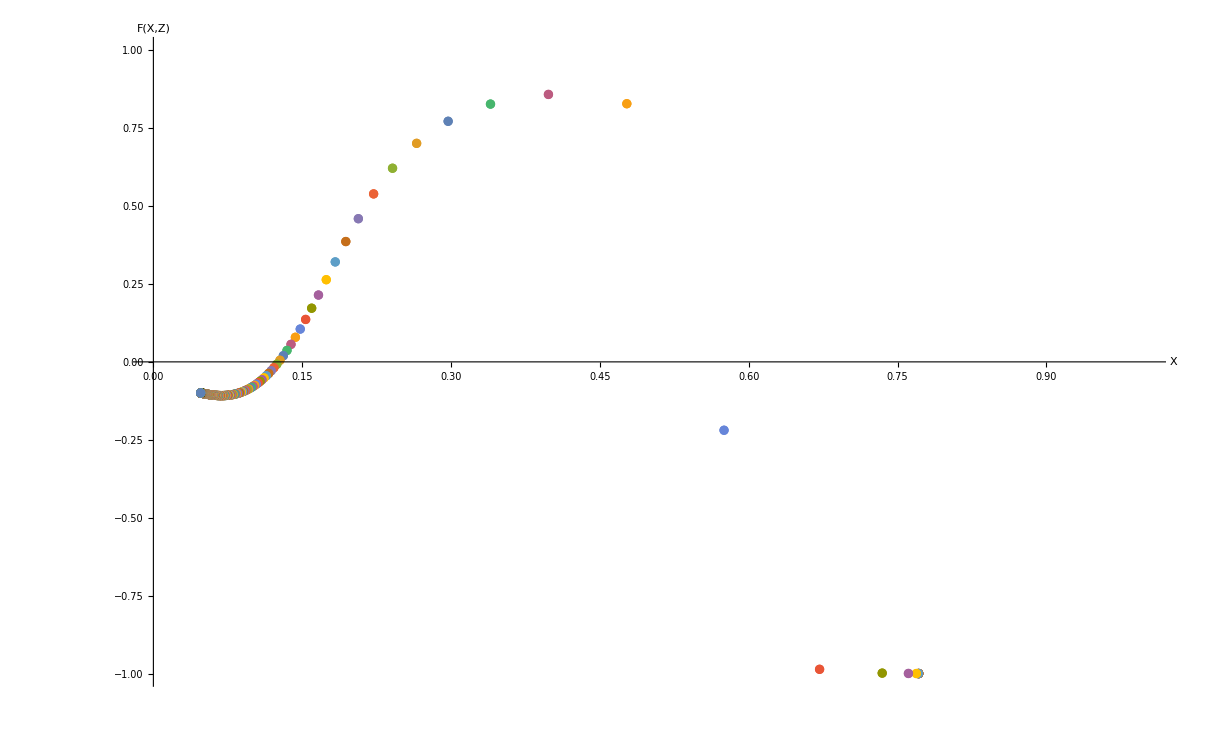

```mathematica
(*Plot X vs the remaining equation when Y' = 0*)
(*When F(X,Z) = 0, an Einstein point exists*)
EinsteinPlotTwoEinsteinPointsCompactNode=ListPlot[EinsteinPointSolutionsTwoEinsteinPointsCompactNode,PlotRange->{{0,1},{-1,1}},AxesLabel->{"X","F(X,Z)"}]
```

#### Plot the X-Y-Z Phase Space

```mathematica
(*Find the maximum value of K for this combination of X0 and Z0 so that Y0 is not imaginary*)
KMaxTwoEinsteinPointsCompactNode=K/.Flatten[Solve[Y0TwoEinsteinPointsNode==0,K]]
```

0.0483863

```mathematica
(*Solve trajTwoEinsteinPointsCompact[K] for different values of K*)
```

```mathematica
solTwoEinsteinPointsCompactNode[1]=trajTwoEinsteinPointsCompactNode[-.1]
```

NDSolve::mxst: Maximum number of 530726 steps reached at the point t == -2.79558.

{{X1→InterpolatingFunction[{{-2.79558, 100.}}, <>],Y1→InterpolatingFunction[{{-2.79558, 100.}}, <>],Z1→InterpolatingFunction[{{-2.79558, 100.}}, <>]}}

```mathematica
solTwoEinsteinPointsCompactNode[2]=trajTwoEinsteinPointsCompactNode[KMaxTwoEinsteinPointsCompactNode]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsCompactNode[3]=trajTwoEinsteinPointsCompactNode[0.02]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the trajectories for the different values of K given above*)
```

```mathematica
trajTwoEinsteinPointsCompactXYZNode[1]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactNode[1],{t,-2.79,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsCompactXYZNode[2]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactNode[2],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
trajTwoEinsteinPointsCompactXYZNode[3]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactNode[3],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
(*Solve the X-Y-Z system using the centre Einstein fixed point for X0 and Z0 to plot a cyclic trajectory*)
CyclicTrajTwoEinsteinPointsCompactNode=NDSolve[{deXt,deYt,deZt,X1[0]==EinsteinPoint2TwoEinsteinPointsCompactNode[[1]],Y1[0]==0.5,Z1[0]==EinsteinPoint2TwoEinsteinPointsCompactNode[[3]]},{X1,Y1,Z1},{t,-100,100}];
```

```mathematica
(*Plot the cyclic trajectory*)
trajTwoEinsteinPointsCompactXYZNode[4]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.CyclicTrajTwoEinsteinPointsCompactNode,{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajTwoEinsteinPointsCaseCompactNode=Table[trajTwoEinsteinPointsCompactXYZNode[i],{i,1,4}];
```

```mathematica
(*Plot the Einstein fixed points*)
EinsteinFixedPointsTwoEinsteinPointsCompactNode=ListPointPlot3D[{EinsteinPoint1TwoEinsteinPointsCompactNode,EinsteinPoint2TwoEinsteinPointsCompactNode},PlotStyle->Black];
```

```mathematica
(*Solve the X-Y-Z system around the Einstein fixed point to plot the Closed Friedmann Separatrix (CFS)*)
CFSTwoEinsteinPointsSolCompactNode=NDSolve[{deXt,deYt,deZt,X1[0]==EinsteinPoint1TwoEinsteinPointsCompactNode[[1]],Y1[0]==-0.0005,Z1[0]==EinsteinPoint1TwoEinsteinPointsCompactNode[[3]]},{X1,Y1,Z1},{t,-100,100}]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the CFS*)
CFSTwoEinsteinPointsCompactNode=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.CFSTwoEinsteinPointsSolCompactNode,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Show the X-Y-Z phase space*)
Show[trajTwoEinsteinPointsCaseCompactNode,CFSTwoEinsteinPointsCompactNode,EinsteinFixedPointsTwoEinsteinPointsCompactNode,AccnXYZNode,FPsXYZNode,CompactFPShowXYZNode,XYZCompactFormat]
```

-Graphics3D-

#### Plot the X-Z Projection

```mathematica
(*Plot one solution on the X-Z plane*)
trajTwoEinsteinPointsCompactXZNode=ParametricPlot[Evaluate[{{Z1[t],X1[t]}}/.solTwoEinsteinPointsCompactNode[1],{t,-2.63,100},PlotStyle -> {{Black,Thick, Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.03,0,.03,0},1]]],Arrow[x]};
```

```mathematica
(*Plot the Einstein fixed points on the X-Z plane*)
EinsteinFixedPointsTwoEinsteinPointsCompactXZNode=ListPlot[{{EinsteinPoint1TwoEinsteinPointsCompactNode[[3]],EinsteinPoint1TwoEinsteinPointsCompactNode[[1]]},{EinsteinPoint2TwoEinsteinPointsCompactNode[[3]],EinsteinPoint2TwoEinsteinPointsCompactNode[[1]]}},PlotStyle->Black];
```

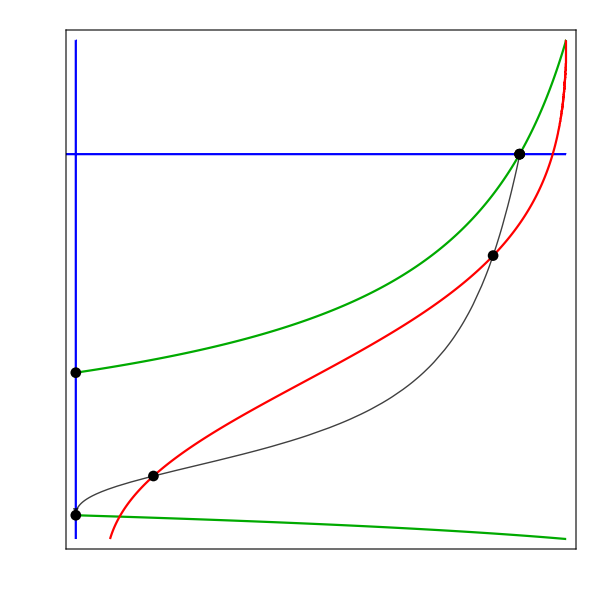

```mathematica
(*Show the X-Z phase space with the a'' = 0 (red), X' = 0 (green) and Z' = 0 (purple) curves*)
Show[trajTwoEinsteinPointsCompactXZNode,XLineNode,ZLineNode,AccnXZNode,EinsteinFixedPointsTwoEinsteinPointsCompactXZNode,FPsXZNode,CompactFPShowXZNode,XZCompactFormat]
```

## Investigate system when ℛ = 10^(-120)

### Set-up

```mathematica
(*Clear variables*)
Clear[q,ϵ,ℛ,wx]
```

```mathematica
(*Set parameter values*)
q=0.8;
ϵ=-1;
ℛ=10^(-120);
wx=-1+2*ℛ;
```

```mathematica
(*Define Ωx0 and Ωm0 using data from Planck 2018*)
Ωx0=0.6889;
Ωm0=0.3111;
```

```mathematica
(*Set a value for α, which sets the value of the low energy cosmological constant*)
α=0.5;
```

```mathematica
(*Define the initial conditions, where a0 = 1 and K is defined as k/ρ* *)

x0=ℛ/α;
y0=Sqrt[x0/3+Z0/(3*(1-Z0))-K];
```

```mathematica
(*Compactify the initial conditions*)

X0=x0/(1+x0);
Y0=y0/Sqrt[1+y0^2];
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y in terms of time, t*)
deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*(X1[t]-ℛ*(1-X1[t]))*((1+wx)*(1-X1[t])+ϵ*X1[t])-q*X1[t]*(1-X1[t])*(Z1[t]/(1-Z1[t]))*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((Z1[t]/(1-Z1[t]))+(X1[t]/(1-X1[t]))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X1[t]^2/((1-X1[t])^2))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2))) + q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
```

### Find the value of z0 to give the limiting case

```mathematica
(*Fix z0 using the density parameters*)
z0RealisticℛNode=Ωm0*ℛ/(Ωx0*α)
```

9.03179×10^-121

```mathematica
(*Compactify z0*)
Z0RealisticℛNode=z0RealisticℛNode/(1+z0RealisticℛNode)
```

9.03179×10^-121

```mathematica
(*Substitute Z0Realisticℛ into Y0 for this case*)
Y0RealisticℛNode=Y0/.Z0->Z0RealisticℛNode
```

(√(9.67726×10^-121-K))/(√(1.-K))

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajRealisticℛNode[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0RealisticℛNode,Z1[0]==Z0RealisticℛNode},{X1,Y1,Z1},{t,-100,100}];
```

NDSolve::ndinnt: Initial condition (√(9.67726×10^-121-1. K))/(√(1.-1. K)) is not a number or a rectangular array of numbers.

```mathematica
(*Set-up tables of all X1 and Z1 values*)
XTableRealisticℛNode=Table[X1[i]/.trajRealisticℛNode[0],{i,-100,100,.1}];
ZTableRealisticℛNode=Table[Z1[i]/.trajRealisticℛNode[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0*)
EinsteinPlotValuesRealisticℛNode=(ZTableRealisticℛNode/(1-ZTableRealisticℛNode))+(XTableRealisticℛNode/(1-XTableRealisticℛNode))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableRealisticℛNode/(1-XTableRealisticℛNode))^2;
```

```mathematica
(*Compactify EinsteinPlotValuesRealisticℛ*)
EinsteinPlotRealisticℛCompactNode=EinsteinPlotValuesRealisticℛNode/Sqrt[1+EinsteinPlotValuesRealisticℛNode^2];
```

```mathematica
(*Find the maximum value of EinsteinPlotRealisticℛCompact*)
(*As EinsteinPlotRealisticℛCompact is always less than zero there are no Einstein points when z0 is defined using the density parameters*)
Max[EinsteinPlotRealisticℛCompactNode]
```

-3.09682×10^-120

## Two Fixed Points Case

This is the case where 6 < q < 60.

## Full 2D and 3D phase spaces

### Non-Compact x - z Phase Space

```mathematica
(*Load MaTeX to typeset axis labels using LaTeX*)
<<MaTeX`
```

```mathematica
(*Define a format style for the x-z phase spaces*)
xzFormat={Frame->{True},FrameLabel->{MaTeX["z",FontSize->24],Rotate[MaTeX["x",FontSize->24],300]},FrameTicks->{{Table[{x,MaTeX[x,"DisplayStyle"->False,FontSize->24]},{x,1Range[-1,7]}],None},{Table[{z,MaTeX[z,"DisplayStyle"->False,FontSize->24]},{z,1Range[0,10]}],None}},ImageSize->{600,600},PlotRangePadding->{0.02,0}};
```

```mathematica
(*Set parameter values*)
wx=-0.5;
ϵ=-1;
ℛ=0.05;
q=7;
```

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, and dark matter, z*)
dex:=x'=-3*(x-ℛ)*(1+wx+ϵ*x)-q*x*z
dez:=z'=-3*z + q*x*z
```

```mathematica
(*Find the fixed points of the system*)
(*In this case one fixed point is at z < 0, therefore we don't consider this fixed point*)
FPsxzTwoFPs=Solve[{dez==0,dex==0},{z,x}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{z→0.,x→0.05},{z→-0.0270408,x→0.428571},{z→0.,x→0.5}}

```mathematica
(*Extract the values of the fixed points and put them into one variable name*)
FPxzTwoFPs[1]={z/.FPsxzTwoFPs[[1,1]],x/.FPsxzTwoFPs[[1,2]]};
FPxzTwoFPs[2]={z/.FPsxzTwoFPs[[3,1]],x/.FPsxzTwoFPs[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPxzTableTwoFPs=Table[FPxzTwoFPs[i],{i,1,2}];
```

```mathematica
(*Find the 2D Jacobian matrix. D[] differentiates each expression*)
JxzTwoFPs=Simplify[{{D[dez,z],D[dez,x]}, {D[dex,z],D[dex,x]}}];
JxzTwoFPs//MatrixForm
```

(-3+7 x | 7 z
-7 x | 6. (-0.275+x-1.16667 z))

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableTwoFPs=Table[{FPxzTableTwoFPs[[i]]//MatrixForm,Simplify[JxzTwoFPs/.{z->FPxzTableTwoFPs[[i,1]],x->FPxzTableTwoFPs[[i,2]]}]//MatrixForm,Eigenvalues[JxzTwoFPs/.{z->FPxzTableTwoFPs[[i,1]],x->FPxzTableTwoFPs[[i,2]]}]//MatrixForm,Eigenvectors[JxzTwoFPs/.{z->FPxzTableTwoFPs[[i,1]],x->FPxzTableTwoFPs[[i,2]]}]//MatrixForm},{i,1,2}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTablexzTwoFPs=TableForm[FPTableTwoFPs,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.
0.05) | (-2.65 | 0.
-0.35 | -1.35) | (-2.65
-1.35) | (0.965616 | 0.259973
0. | 1.)
(0.
0.5) | (0.5 | 0.
-3.5 | 1.35) | (1.35
0.5) | (0. | 1.
0.235997 | 0.971754)

```mathematica
(*Plot the fixed points*)
FPsxzTwoFPs=ListPlot[FPxzTableTwoFPs,PlotStyle->Black];
```

```mathematica
(*Plot the phase space for the dark energy and dark matter*)
PhaseSpacexzTwoFPs=StreamPlot[{dez,dex},{z,0,2.5},{x,-1,2.5}];
```

```mathematica
(*Plot the curves where z' = 0*)
zLineTwoFPs=ContourPlot[-3*z + q*x*z==0,{z,-.1,2.5},{x,-1,2.5},ContourStyle->Blue,PlotPoints->100];
```

```mathematica
(*Plot the curves where x' = 0*)
xLineTwoFPs=ContourPlot[-3*(x-ℛ)*(1+wx+ϵ*x)-q*x*z==0,{z,-.1,2.5},{x,-1,2.5},ContourStyle->Darker[Green],PlotPoints->100];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
AccnxzTwoFPs=ContourPlot[z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2==0,{z,0,2.5},{x,-1,2.5},ContourStyle->Red];
```

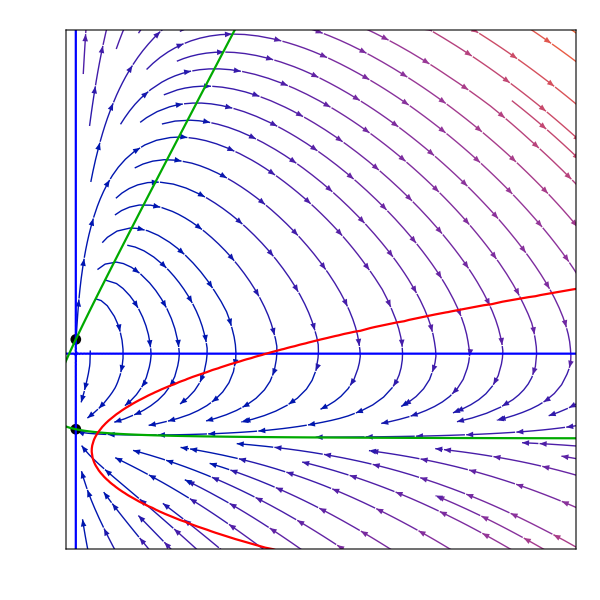

```mathematica
(*Show the plots of the phase space and its components together*)
Show[PhaseSpacexzTwoFPs,FPsxzTwoFPs,zLineTwoFPs,xLineTwoFPs,AccnxzTwoFPs,xzFormat,PlotRange->{{0,2},{-0.5,2}}]
```

### Non-Compact x - y - z Phase Space

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, dark matter, z, and the Hubble parameter, y*)
dex:=x'=-3*y*(x-ℛ)*(1+wx+ϵ*x)-q*x*y*z
dey:=y'=-y^2-(1/6)*(z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2) 
dez:=z'=-3*y*z + q*x*y*z
```

```mathematica
(*Find the fixed points of the system*)
FPsTwoFPs=Solve[{dex==0,dey==0,dez==0},{x,y,z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0.,z→0.025 (3.+14. x+120. x^2)},{x→0.05,y→-0.129099,z→0.},{x→0.05,y→0.129099,z→0.},{x→0.428571,y→-0.365846,z→-0.0270408},{x→0.428571,y→0.365846,z→-0.0270408},{x→0.5,y→-0.408248,z→0.},{x→0.5,y→0.408248,z→0.}}

```mathematica
(*Extract the values for the fixed points and put them into a common variable name*)
FPTwoFPs[1]={x,y/.FPsTwoFPs[[1,1]],z/.FPsTwoFPs[[1,2]]};
FPTwoFPs[2]={x/.FPsTwoFPs[[2,1]],y/.FPsTwoFPs[[2,2]],z/.FPsTwoFPs[[2,3]]};
FPTwoFPs[3]={x/.FPsTwoFPs[[3,1]],y/.FPsTwoFPs[[3,2]],z/.FPsTwoFPs[[3,3]]};
FPTwoFPs[4]={x/.FPsTwoFPs[[6,1]],y/.FPsTwoFPs[[6,2]],z/.FPsTwoFPs[[6,3]]};
FPTwoFPs[5]={x/.FPsTwoFPs[[7,1]],y/.FPsTwoFPs[[7,2]],z/.FPsTwoFPs[[7,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPsTwoFPs=Table[FPTwoFPs[i],{i,1,5}];
```

```mathematica
(*Find the 3D Jacobian matrix. D[] differentiates each expression*)
JxyzTwoFPs=Simplify[{{D[dex,x],D[dex,y],D[dex,z]}, {D[dey,x],D[dey,y],D[dey,z]},{D[dez,x],D[dez,y],D[dez,z]}}];
JxyzTwoFPs//MatrixForm
```

(y (-1.65+6. x-7. z) | 3. (0.025+x^2+x (-0.55-2.33333 z)) | -7 x y
0.0583333+x | -2 y | -1/6
7 y z | (-3+7 x) z | (-3+7 x) y)

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableTwoFPs=Table[{FPsTwoFPs[[i]]//MatrixForm,Simplify[JxyzTwoFPs/.{x->FPsTwoFPs[[i,1]],y->FPsTwoFPs[[i,2]],z->FPsTwoFPs[[i,3]]}]//MatrixForm,Eigenvalues[JxyzTwoFPs/.{x->FPsTwoFPs[[i,1]],y->FPsTwoFPs[[i,2]],z->FPsTwoFPs[[i,3]]}]//MatrixForm,Eigenvectors[JxyzTwoFPs/.{x->FPsTwoFPs[[i,1]],y->FPsTwoFPs[[i,2]],z->FPsTwoFPs[[i,3]]}]//MatrixForm},{i,1,5}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTablexyzTwoFPs=TableForm[FPTableTwoFPs,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(x
0.
0.025 (3.+14. x+120. x^2)) | (0. | 0.075-2.175 x+0.55 x^2-21. x^3 | 0.
0.0583333+x | 0. | -1/6
0. | -0.225-0.525 x-6.55 x^2+21. x^3 | 0.) | (0
-√(0.041875+0.035625 x-1.05125 x^2-4.175 x^3-21. x^4)
√(0.041875+0.035625 x-1.05125 x^2-4.175 x^3-21. x^4)) | (0.166667/(0.0583333+x) | 0 | 1.
-(1. (-0.000208333+0.00247024 x+0.102044 x^2+0.0321429 x^3+1. x^4))/((0.0583333+x) (-0.0107143-0.025 x-0.311905 x^2+1. x^3)) | -(0.047619 √(0.041875+0.035625 x-1.05125 x^2-4.175 x^3-21. x^4))/(-0.0107143-0.025 x-0.311905 x^2+1. x^3) | 1.
-(1. (-0.000208333+0.00247024 x+0.102044 x^2+0.0321429 x^3+1. x^4))/((0.0583333+x) (-0.0107143-0.025 x-0.311905 x^2+1. x^3)) | (0.047619 √(0.041875+0.035625 x-1.05125 x^2-4.175 x^3-21. x^4))/(-0.0107143-0.025 x-0.311905 x^2+1. x^3) | 1.)
(0.05
-0.129099
0.) | (0.174284 | 2.08167×10^-17 | 0.0451848
0.108333 | 0.258199 | -1/6
0. | 0. | 0.342114) | (0.342114
0.258199
0.174284) | (0.138893 | -0.845321 | 0.515889
-1.15126×10^-16 | -1. | 0.
-0.612372 | 0.790569 | 0.)
(0.05
0.129099
0.) | (-0.174284 | 2.08167×10^-17 | -0.0451848
0.108333 | -0.258199 | -1/6
0. | 0. | -0.342114) | (-0.342114
-0.258199
-0.174284) | (0.138893 | 0.845321 | 0.515889
-1.15126×10^-16 | 1. | 0.
0.612372 | 0.790569 | 0.)
(0.5
-0.408248
0.) | (-0.551135 | 1.66533×10^-16 | 1.42887
0.558333 | 0.816497 | -1/6
0. | 0. | -0.204124) | (0.816497
-0.551135
-0.204124) | (-1.7255×10^-16 | -1. | 0.
-0.92582 | 0.377964 | 0.
0.871568 | -0.442229 | 0.211667)
(0.5
0.408248
0.) | (0.551135 | 1.66533×10^-16 | -1.42887
0.558333 | -0.816497 | -1/6
0. | 0. | 0.204124) | (-0.816497
0.551135
0.204124) | (-1.7255×10^-16 | 1. | 0.
0.92582 | 0.377964 | 0.
0.871568 | 0.442229 | 0.211667)

```mathematica
(*Plot the line of Einstein fixed points*)
EinsteinPointLineTwoFPs=ParametricPlot3D[{FPTwoFPs[1][[1]],FPTwoFPs[1][[2]],FPTwoFPs[1][[3]]},{x,0,4},PlotStyle->Red];
```

```mathematica
(*Plot the fixed points of the system*)
FPsxyzTwoFPs=ListPointPlot3D[Table[FPTwoFPs[i],{i,2,5}],PlotStyle->Black];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
AccnxyzTwoFPs=ContourPlot3D[z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2==0,{x,0,3},{y,-5,5},{z,0,3},ContourStyle->{Red,Opacity[0.25]},Mesh->None];
```

```mathematica
(*Plot the x-y-z phase space*)
PhaseSpacexyzTwoFPs=StreamPlot3D[{dex,dey,dez},{x,0,3},{y,-5,5},{z,0,3},AxesLabel->{"x","y","z"}];
```

```mathematica
(*Show the phase space and its components together*)
Show[PhaseSpacexyzTwoFPs,FPsxyzTwoFPs,EinsteinPointLineTwoFPs,AccnxyzTwoFPs,AxesLabel->{MaTeX["x",FontSize->20],MaTeX["y",FontSize->20],MaTeX["z",FontSize->20]},Ticks->{{0.,1.,2.,3.},{-5.,0.,1.,5.},{0.,1.,2.,3.}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->20}]
```

-Graphics3D-

## Constant x0 and z0 surfaces

Trajectories are plotted on a constant x0-z0 surface, where x0 is fixed for all cases and z0 is fixed for each phase space to give a different number of Einstein fixed points. k and y0 differ for each trajectory in each phase space.

### Set-up for the phase spaces

```mathematica
(*Define a format for the x-y-z phase spaces*)
xyzFormat={AxesLabel->{MaTeX["x",FontSize->20],MaTeX["y",FontSize->20],MaTeX["z",FontSize->20]},Ticks->{{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.},{-5.,-4.,-3.,-2.,-1.,0.,1.,2.,3.,4.,5.},{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->20}};
```

```mathematica
(*Define the system of differential equations for the dark energy, x, dark matter, z, and Hubble parameter, y, in terms of a time variable*)
dext:=x1'[t]==-3*y1[t]*(x1[t]-ℛ)*(1+wx+ϵ*x1[t])-q*x1[t]*y1[t]*z1[t]
deyt:=y1'[t]==-y1[t]^2-(1/6)*(z1[t]+x1[t]*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x1[t]^2) 
dezt:=z1'[t]==-3*y1[t]*z1[t] + q*x1[t]*y1[t]*z1[t]
```

```mathematica
(*Define Ωx0 and Ωm0 using data from Planck 2018*)
Ωx0=0.6889;
Ωm0=0.3111;
```

```mathematica
(*Set a value for α, which sets the value of the low energy cosmological constant*)
α=0.5;
```

```mathematica
(*Define the initial conditions, where a0 = 1 and K is defined as k/ρ* *)

x0=ℛ/α;
y0=Sqrt[x0/3+z0/3-K];
```

```mathematica
(*Define values of K using the range of Ωk0 allowed by Planck 2018*)
Ωk0Open=0.003;
Ωk0Closed=-0.001;

KDensityParametersOpen=-Ωk0Open*ℛ/(3*α*Ωx0)
KDensityParametersClosed=-Ωk0Closed*ℛ/(3*α*Ωx0)
```

-0.000145159

0.0000483863

### Limiting Case with 1 Einstein fixed point

#### Find the Einstein Fixed Point

```mathematica
(*Fix z0 so that there is one Einstein fixed point on the surface*)
z0LimitingTwoFPs=0.115;
```

```mathematica
(*Substitute z0Limiting into y0 for this case*)
y0LimitingTwoFPs=y0/.z0->z0LimitingTwoFPs
```

√(0.0716667-K)

```mathematica
(*Numerically solve the system of equations using the initial conditions defined for the limiting case with one Einstein fixed point*)
trajLimitingTwoFPs[K_]=NDSolve[{dext,deyt,dezt,x1[0]==x0,y1[0]==y0LimitingTwoFPs,z1[0]==z0LimitingTwoFPs},{x1,y1,z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition √(0.0716667-1. K) is not a number or a rectangular array of numbers.

NDSolve[{x1'[t]==-3 (0.5-x1[t]) (-0.05+x1[t]) y1[t]-7 x1[t] y1[t] z1[t],y1'[t]==-y1[t]^2+1/6 (0.075+0.35 x1[t]+3 x1[t]^2-z1[t]),z1'[t]==-3 y1[t] z1[t]+7 x1[t] y1[t] z1[t],x1[0]==0.1,y1[0]==√(0.0716667-K),z1[0]==0.115},{x1,y1,z1},{t,-100,100}]

```mathematica
(*Set-up tables of all x1 and z1 values to be used to find the x and z value of the Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
xTableSolLimitingTwoFPs=Table[x1[i]/.trajLimitingTwoFPs[0],{i,-100,100,.01}];
zTableSolLimitingTwoFPs=Table[z1[i]/.trajLimitingTwoFPs[0],{i,-100,100,.01}];
```

NDSolve::ndsz: At t == -22.1058, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-100.} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == -22.1058, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-99.99} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == -22.1058, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-99.98} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == -22.1058, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-100.} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == -22.1058, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-99.99} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == -22.1058, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-99.98} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSolLimitingTwoFPs=(zTableSolLimitingTwoFPs)+(xTableSolLimitingTwoFPs)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSolLimitingTwoFPs)^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSolLimiting that is closest to zero. When EinsteinPlotValuesSolLimiting = 0 (y = 0), there is an Einstein point*)
NearestToZeroLimitingTwoFPs=Flatten[Nearest[EinsteinPlotValuesSolLimitingTwoFPs,0]]
```

{-0.00396263}

```mathematica
(*Find the position of NearestToZeroLimiting in the EinsteinPlotValuesSolLimiting array*)
PositionNearestToZeroLimitingTwoFPs=Flatten[Position[EinsteinPlotValuesSolLimitingTwoFPs,NearestToZeroLimitingTwoFPs]]
```

{9924}

```mathematica
(*Find the Einstein point by finding the x and z values in xTableSolLimiting and zTableSolLimiting at PositionNearestToZeroLimiting*)
EinsteinPointLimitingTwoFPs=Flatten[{xTableSolLimitingTwoFPs[[PositionNearestToZeroLimitingTwoFPs]],0,zTableSolLimitingTwoFPs[[PositionNearestToZeroLimitingTwoFPs]]}]
```

{0.148069,0,0.188635}

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for the Einstein fixed point*)
EinsteinTableLimitingTwoFPs=Table[{EinsteinPointLimitingTwoFPs//MatrixForm,Simplify[JxyzTwoFPs/.{x->EinsteinPointLimitingTwoFPs[[1]],y->EinsteinPointLimitingTwoFPs[[2]],z->EinsteinPointLimitingTwoFPs[[3]]}]//MatrixForm,Eigenvalues[JxyzTwoFPs/.{x->EinsteinPointLimitingTwoFPs[[1]],y->EinsteinPointLimitingTwoFPs[[2]],z->EinsteinPointLimitingTwoFPs[[3]]}]//MatrixForm,Eigenvectors[JxyzTwoFPs/.{x->EinsteinPointLimitingTwoFPs[[1]],y->EinsteinPointLimitingTwoFPs[[2]],z->EinsteinPointLimitingTwoFPs[[3]]}]//MatrixForm},1];
```

```mathematica
(*Use TableForm to display the Einstein fixed point with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableEinsteinPointLimitingTwoFPs=TableForm[EinsteinTableLimitingTwoFPs,TableHeadings->{None,{"Einstein Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Einstein Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.148069
0
0.188635) | (0. | -0.299058 | 0.
0.206403 | 0 | -1/6
0. | -0.370388 | 0.) | (-0.00223145
0.00223145
2.60271×10^-13) | (0.628201 | 0.00468739 | 0.778037
0.628201 | -0.00468739 | 0.778037
-0.628239 | 5.46652×10^-13 | -0.778021)

```mathematica
(*Set-up tables of all x1 and z1 values with a bigger t increment*)
xTableSolLimitingFullTwoFPs=Table[x1[i]/.trajLimitingTwoFPs[0],{i,-100,100,.1}];
zTableSolLimitingFullTwoFPs=Table[z1[i]/.trajLimitingTwoFPs[0],{i,-100,100,.1}];
```

NDSolve::ndsz: At t == -22.1058, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-100.} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == -22.1058, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-99.9} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == -22.1058, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-99.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == -22.1058, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-100.} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == -22.1058, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-99.9} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == -22.1058, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-99.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0*)
EinsteinPlotValuesSolLimitingFullTwoFPs=(zTableSolLimitingFullTwoFPs)+(xTableSolLimitingFullTwoFPs)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSolLimitingFullTwoFPs)^2;
```

```mathematica
(*Merge the xTableSolLimitingFull values and the EinsteinPlotValuesSolLimitingFull values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsLimitingTwoFPs=MapThread[h,{xTableSolLimitingFullTwoFPs,EinsteinPlotValuesSolLimitingFullTwoFPs}];
```

```mathematica
(*Plot x vs the remaining equation when y' = 0*)
(*When f(x,z) = 0, an Einstein point exists*)
EinsteinPlotLimitingTwoFPs=ListPlot[EinsteinPointSolutionsLimitingTwoFPs,PlotRange->{{0,1.5},{-3,1}},AxesLabel->{"x","f(x,z)"}]
```

-Graphics-

#### Plot the x-y-z Phase Space

```mathematica
(*Find the maximum value of K for this combination of x0 and z0 such that y0 is not imaginary*)
KMaxLimitingTwoFPs=K/.Solve[y0LimitingTwoFPs==0,K][[1]]
```

0.0716667

```mathematica
(*Solve trajLimiting[K] for different values of K*)
```

```mathematica
solLimitingTwoFPs[1]=trajLimitingTwoFPs[KMaxLimitingTwoFPs]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solLimitingTwoFPs[2]=trajLimitingTwoFPs[KDensityParametersClosed]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solLimitingTwoFPs[3]=trajLimitingTwoFPs[-.1]
```

NDSolve::ndsz: At t == -2.64605, step size is effectively zero; singularity or stiff system suspected.

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solLimitingTwoFPs[4]=trajLimitingTwoFPs[0.025]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solLimitingTwoFPs[5]=trajLimitingTwoFPs[-0.01]
```

NDSolve::ndsz: At t == -4.98288, step size is effectively zero; singularity or stiff system suspected.

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solLimitingTwoFPs[6]=trajLimitingTwoFPs[0.055]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the trajectories for the different values of K given above*)
```

```mathematica
trajLimitingxyzTwoFPs[1]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimitingTwoFPs[1],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingxyzTwoFPs[2]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimitingTwoFPs[2],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingxyzTwoFPs[3]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimitingTwoFPs[3],{t,-2.64,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingxyzTwoFPs[4]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimitingTwoFPs[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
trajLimitingxyzTwoFPs[5]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimitingTwoFPs[5],{t,-4.97,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingxyzTwoFPs[6]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimitingTwoFPs[6],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajLimitingCaseTwoFPs=Table[trajLimitingxyzTwoFPs[i],{i,1,6}];
```

```mathematica
(*Plot the Einstein fixed point*)
EinsteinFixedPointsLimitingTwoFPs=ListPointPlot3D[{EinsteinPointLimitingTwoFPs},PlotStyle->Black];
```

```mathematica
(*Solve the x-y-z system around the Einstein fixed point to plot the Closed Friedmann Separatrix (CFS)*)
CFSLimitingSolTwoFPs=NDSolve[{dext,deyt,dezt,x1[0]==EinsteinPointLimitingTwoFPs[[1]],y1[0]==0,z1[0]==EinsteinPointLimitingTwoFPs[[3]]},{x1,y1,z1},{t,-100,100}]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the CFS*)
CFSLimitingTwoFPs=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.CFSLimitingSolTwoFPs,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
(*Show the x-y-z phase space*)
Show[trajLimitingCaseTwoFPs,EinsteinFixedPointsLimitingTwoFPs,CFSLimitingTwoFPs,AccnxyzTwoFPs,FPsxyzTwoFPs,xyzFormat,PlotRange->{{0,1},{-1.5,1.5},{0,1}}]
```

-Graphics3D-

#### Plot the x-z Projection

```mathematica
(*Plot one solution on the x-z plane*)
trajLimitingxzTwoFPs=ParametricPlot[Evaluate[{{z1[t],x1[t]}}/.solLimitingTwoFPs[5],{t,-4.97,100},PlotStyle -> {{Black, Thick,Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.03,.03,0},1]]],Arrow[x]};
```

```mathematica
(*Plot the Einstein fixed point on the x-z plane*)
EinsteinFixedPointsLimitingxzTwoFPs=ListPlot[{{EinsteinPointLimitingTwoFPs[[3]],EinsteinPointLimitingTwoFPs[[1]]}},PlotStyle->Black];
```

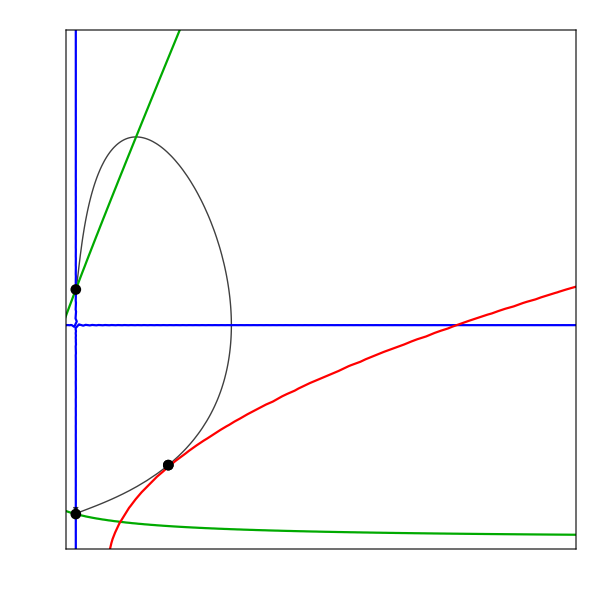

```mathematica
(*Show the x-z phase space with the a'' = 0 (red), x' = 0 (green) and z' = 0 (purple) curves*)
Show[trajLimitingxzTwoFPs,xLineTwoFPs,zLineTwoFPs,AccnxzTwoFPs,FPsxzTwoFPs,EinsteinFixedPointsLimitingxzTwoFPs,xzFormat,PlotRange->{{0,1},{0,1}}]
```

### Two Einstein Fixed Points

#### Find the Einstein Fixed Points

```mathematica
(*Fix z0 such that there are two Einstein fixed points*)
z0TwoEinsteinPointsTwoFPs=0.3;
```

```mathematica
(*Substitute z0TwoEinsteinPoints into y0 for this case*)
y0TwoEinsteinPointsTwoFPs=y0/.z0->z0TwoEinsteinPointsTwoFPs
```

√(0.133333-K)

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajTwoEinsteinPointsTwoFPs[K_]=NDSolve[{dext,deyt,dezt,x1[0]==x0,y1[0]==y0TwoEinsteinPointsTwoFPs,z1[0]==z0TwoEinsteinPointsTwoFPs},{x1,y1,z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition √(0.133333-1. K) is not a number or a rectangular array of numbers.

NDSolve[{x1'[t]==-3 (0.5-x1[t]) (-0.05+x1[t]) y1[t]-7 x1[t] y1[t] z1[t],y1'[t]==-y1[t]^2+1/6 (0.075+0.35 x1[t]+3 x1[t]^2-z1[t]),z1'[t]==-3 y1[t] z1[t]+7 x1[t] y1[t] z1[t],x1[0]==0.1,y1[0]==√(0.133333-K),z1[0]==0.3},{x1,y1,z1},{t,-100,100}]

```mathematica
(*Set-up tables of x1 and z1 values to be used to find the x and z value of the first Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
xTableSol1TwoEinsteinPointsTwoFPs=Table[x1[i]/.trajTwoEinsteinPointsTwoFPs[0],{i,1,100,.01}];
zTableSol1TwoEinsteinPointsTwoFPs=Table[z1[i]/.trajTwoEinsteinPointsTwoFPs[0],{i,1,100,.01}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol1TwoEinsteinPointsTwoFPs=(zTableSol1TwoEinsteinPointsTwoFPs)+(xTableSol1TwoEinsteinPointsTwoFPs)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol1TwoEinsteinPointsTwoFPs)^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol1TwoEinsteinPoints that is closest to zero. When EinsteinPlotValuesSol1TwoEinsteinPoints = 0 (y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints1TwoFPs=Flatten[Nearest[EinsteinPlotValuesSol1TwoEinsteinPointsTwoFPs,0]]
```

{0.000109303}

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints1 in the EinsteinPlotValuesSol1TwoEinsteinPoints*)
PositionNearestToZeroTwoEinsteinPoints1TwoFPs=Flatten[Position[EinsteinPlotValuesSol1TwoEinsteinPointsTwoFPs,NearestToZeroTwoEinsteinPoints1TwoFPs]]
```

{55}

```mathematica
(*Find the Einstein point by finding the x and z values in xTableSol1TwoEinsteinPoints and zTableSol1TwoEinsteinPoints at PositionNearestToZeroTwoEinsteinPoints1*)
EinsteinPoint1TwoEinsteinPointsTwoFPs=Flatten[{xTableSol1TwoEinsteinPointsTwoFPs[[PositionNearestToZeroTwoEinsteinPoints1TwoFPs]],0,zTableSol1TwoEinsteinPointsTwoFPs[[PositionNearestToZeroTwoEinsteinPoints1TwoFPs]]}]
```

{0.0503966,0,0.100368}

```mathematica
(*Set-up tables of x1 and z1 values to be used to find the x and z value of the second Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
xTableSol2TwoEinsteinPointsTwoFPs=Table[x1[i]/.trajTwoEinsteinPointsTwoFPs[0],{i,-5.6,0,.001}];
zTableSol2TwoEinsteinPointsTwoFPs=Table[z1[i]/.trajTwoEinsteinPointsTwoFPs[0],{i,-5.6,0,.001}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol2TwoEinsteinPointsTwoFPs=(zTableSol2TwoEinsteinPointsTwoFPs)+(xTableSol2TwoEinsteinPointsTwoFPs)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol2TwoEinsteinPointsTwoFPs)^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol2TwoEinsteinPoints that is closest to zero. When EinsteinPlotValuesSol2TwoEinsteinPoints = 0 (y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints2TwoFPs=Flatten[Nearest[EinsteinPlotValuesSol2TwoEinsteinPointsTwoFPs,0]]
```

{-0.0000160763}

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints2 in the EinsteinPlotValuesSol2TwoEinsteinPoints array*)
PositionNearestToZeroTwoEinsteinPoints2TwoFPs=Flatten[Position[EinsteinPlotValuesSol2TwoEinsteinPointsTwoFPs,NearestToZeroTwoEinsteinPoints2TwoFPs]]
```

{4840}

```mathematica
(*Find the Einstein point by finding the x and z values in xTableSol2TwoEinsteinPoints and zTableSol2TwoEinsteinPoints at PositionNearestToZeroTwoEinsteinPoints2*)
EinsteinPoint2TwoEinsteinPointsTwoFPs=Flatten[{xTableSol2TwoEinsteinPointsTwoFPs[[PositionNearestToZeroTwoEinsteinPoints2TwoFPs]],0,zTableSol2TwoEinsteinPointsTwoFPs[[PositionNearestToZeroTwoEinsteinPoints2TwoFPs]]}]
```

{0.335623,0,0.53038}

```mathematica
(*Put the Einstein fixed points into a common variable name*)
EinsteinPointTwoEPtsTwoFPs[1]=EinsteinPoint1TwoEinsteinPointsTwoFPs;
EinsteinPointTwoEPtsTwoFPs[2]=EinsteinPoint2TwoEinsteinPointsTwoFPs;
```

```mathematica
(*Put the Einstein fixed points into a table*)
EinsteinPointsTwoEPtsTwoFPs=Table[EinsteinPointTwoEPtsTwoFPs[i],{i,1,2}];
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each Einstein fixed point*)
EinsteinPointTableTwoEinsteinPointsTwoFPs=Table[{EinsteinPointsTwoEPtsTwoFPs[[i]]//MatrixForm,Simplify[JxyzTwoFPs/.{x->EinsteinPointsTwoEPtsTwoFPs[[i,1]],y->EinsteinPointsTwoEPtsTwoFPs[[i,2]],z->EinsteinPointsTwoEPtsTwoFPs[[i,3]]}]//MatrixForm,Eigenvalues[JxyzTwoFPs/.{x->EinsteinPointsTwoEPtsTwoFPs[[i,1]],y->EinsteinPointsTwoEPtsTwoFPs[[i,2]],z->EinsteinPointsTwoEPtsTwoFPs[[i,3]]}]//MatrixForm,Eigenvectors[JxyzTwoFPs/.{x->EinsteinPointsTwoEPtsTwoFPs[[i,1]],y->EinsteinPointsTwoEPtsTwoFPs[[i,2]],z->EinsteinPointsTwoEPtsTwoFPs[[i,3]]}]//MatrixForm},{i,1,2}];
```

```mathematica
(*Use TableForm to display the Einstein fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableTwoEinsteinPointsTwoFPs=TableForm[EinsteinPointTableTwoEinsteinPointsTwoFPs,TableHeadings->{None,{"Einstein Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Einstein Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.0503966
0
0.100368) | (0. | -0.0359422 | 0.
0.10873 | 0 | -1/6
0. | -0.265695 | 0.) | (-0.200934
0.200934
-5.09491×10^-18) | (-0.107273 | -0.599709 | -0.792995
0.107273 | -0.599709 | 0.792995
0.837532 | -1.0382×10^-16 | 0.546389)
(0.335623
0
0.53038) | (0. | -1.3869 | 0.
0.393956 | 0 | -1/6
0. | -0.345087 | 0.) | (-7.94808×10^-17+0.699188 ⅈ
-7.94808×10^-17-0.699188 ⅈ
-7.32534×10^-18+0. ⅈ) | (-0.871689+0. ⅈ | 9.91514×10^-17+0.43945 ⅈ | -0.216892+8.08545×10^-19 ⅈ
-0.871689+0. ⅈ | 9.91514×10^-17-0.43945 ⅈ | -0.216892-8.08545×10^-19 ⅈ
0.389626+0. ⅈ | -1.7611×10^-17+0. ⅈ | 0.920973+0. ⅈ)

```mathematica
(*Set-up tables of all x1 and z1 values*)
xTableSolTwoEinsteinPointsFullTwoFPs=Table[x1[i]/.trajTwoEinsteinPointsTwoFPs[0],{i,-100,100,.1}];
zTableSolTwoEinsteinPointsFullTwoFPs=Table[z1[i]/.trajTwoEinsteinPointsTwoFPs[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0*)
EinsteinPlotValuesSolTwoEinsteinPointsFullTwoFPs=(zTableSolTwoEinsteinPointsFullTwoFPs)+(xTableSolTwoEinsteinPointsFullTwoFPs)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSolTwoEinsteinPointsFullTwoFPs)^2;
```

```mathematica
(*Merge the xTableSolTwoEinsteinPointsFull values and the EinsteinPlotValuesSolTwoEinsteinPointsFull values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsTwoEinsteinPointsTwoFPs=MapThread[h,{xTableSolTwoEinsteinPointsFullTwoFPs,EinsteinPlotValuesSolTwoEinsteinPointsFullTwoFPs}];
```

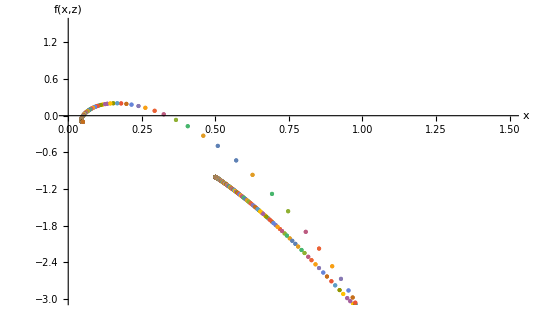

```mathematica
(*Plot x vs the remaining equation when y' = 0*)
(*When f(x,z) = 0, an Einstein point exists*)
EinsteinPlotTwoEinsteinPointsTwoFPs=ListPlot[EinsteinPointSolutionsTwoEinsteinPointsTwoFPs,PlotRange->{{0,1.5},{-3,1.5}},AxesLabel->{"x","f(x,z)"}]
```

#### Plot the x-y-z Phase Space

```mathematica
(*Find the maximum value of K for this combination of x0 and z0 so that y0 is not imaginary*)
KMaxTwoEinsteinPointsTwoFPs=K/.Flatten[Solve[y0TwoEinsteinPointsTwoFPs==0,K]]
```

0.133333

```mathematica
(*Solve trajTwoEinsteinPoints[K] for different values of K*)
```

```mathematica
solTwoEinsteinPointsTwoFPs[1]=trajTwoEinsteinPointsTwoFPs[-.02]
```

NDSolve::ndsz: At t == -3.84064, step size is effectively zero; singularity or stiff system suspected.

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsTwoFPs[2]=trajTwoEinsteinPointsTwoFPs[0.005]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsTwoFPs[3]=trajTwoEinsteinPointsTwoFPs[-.1]
```

NDSolve::ndsz: At t == -2.44494, step size is effectively zero; singularity or stiff system suspected.

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsTwoFPs[4]=trajTwoEinsteinPointsTwoFPs[KMaxTwoEinsteinPointsTwoFPs]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsTwoFPs[5]=trajTwoEinsteinPointsTwoFPs[0.05]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the trajectories for the different values of K given above*)
```

```mathematica
trajTwoEinsteinPointsxyzTwoFPs[1]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsTwoFPs[1],{t,-3.83,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsxyzTwoFPs[2]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsTwoFPs[2],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsxyzTwoFPs[3]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsTwoFPs[3],{t,-2.43,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsxyzTwoFPs[4]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsTwoFPs[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75],Dashed}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
trajTwoEinsteinPointsxyzTwoFPs[5]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPointsTwoFPs[5],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajTwoEinsteinPointsCaseTwoFPs=Table[trajTwoEinsteinPointsxyzTwoFPs[i],{i,1,5}];
```

```mathematica
(*Plot the Einstein fixed points*)
EinsteinFixedPointsTwoEinsteinPointsTwoFPs=ListPointPlot3D[{EinsteinPoint1TwoEinsteinPointsTwoFPs,EinsteinPoint2TwoEinsteinPointsTwoFPs},PlotStyle->Black];
```

```mathematica
(*Solve the x-y-z system around the Einstein fixed point to plot the Closed Friedmann Separatrix (CFS)*)
CFSTwoEinsteinPointsSolTwoFPs=NDSolve[{dext,deyt,dezt,x1[0]==EinsteinPoint1TwoEinsteinPointsTwoFPs[[1]],y1[0]==-0.0005,z1[0]==EinsteinPoint1TwoEinsteinPointsTwoFPs[[3]]},{x1,y1,z1},{t,-100,100}]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the CFS*)
CFSTwoEinsteinPointsTwoFPs=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.CFSTwoEinsteinPointsSolTwoFPs,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Show the x-y-z phase space*)
Show[trajTwoEinsteinPointsCaseTwoFPs,CFSTwoEinsteinPointsTwoFPs,EinsteinFixedPointsTwoEinsteinPointsTwoFPs,AccnxyzTwoFPs,FPsxyzTwoFPs,xyzFormat,PlotRange->{{0,1},{-1.5,1.5},{0,1}}]
```

-Graphics3D-

#### Plot the x-z Projection

```mathematica
(*Plot one solution on the x-z plane*)
trajTwoEinsteinPointsxzTwoFPs=ParametricPlot[Evaluate[{{z1[t],x1[t]}}/.solTwoEinsteinPointsTwoFPs[1],{t,-3.83,100},PlotStyle -> {{Black, Thick,Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,0,.03,0,.03,0},1]]],Arrow[x]};;
```

```mathematica
(*Plot the Einstein fixed points on the x-z plane*)
EinsteinFixedPointsTwoEinsteinPointsxzTwoFPs=ListPlot[{{EinsteinPoint1TwoEinsteinPointsTwoFPs[[3]],EinsteinPoint1TwoEinsteinPointsTwoFPs[[1]]},{EinsteinPoint2TwoEinsteinPointsTwoFPs[[3]],EinsteinPoint2TwoEinsteinPointsTwoFPs[[1]]}},PlotStyle->Black];
```

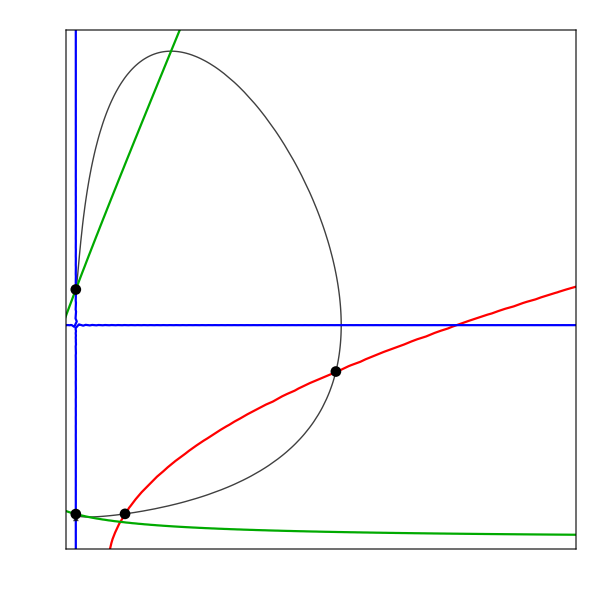

```mathematica
(*Show the x-z phase space with the a'' = 0 (red), x' = 0 (green) and z' = 0 (purple) curves*)
Show[trajTwoEinsteinPointsxzTwoFPs,AccnxzTwoFPs,xLineTwoFPs,zLineTwoFPs,FPsxzTwoFPs,EinsteinFixedPointsTwoEinsteinPointsxzTwoFPs,xzFormat,PlotRange->{{0,1},{0,1}}]
```

### No Einstein Fixed Points

#### Plot to show that there are no Einstein fixed points

```mathematica
(*Fix z0 such that there are no Einstein fixed points on the surface*)
z0NoEinsteinPointsTwoFPs=Ωm0*ℛ/(Ωx0*α);
```

```mathematica
(*Substitute z0NoEinsteinPoints into y0 for this case*)
y0NoEinsteinPointsTwoFPs=y0/.z0->z0NoEinsteinPointsTwoFPs
```

√(0.0483863-K)

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajNoEinsteinPointsTwoFPs[K_]=NDSolve[{dext,deyt,dezt,x1[0]==x0,y1[0]==y0NoEinsteinPointsTwoFPs,z1[0]==z0NoEinsteinPointsTwoFPs},{x1,y1,z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition √(0.0483863-1. K) is not a number or a rectangular array of numbers.

NDSolve[{x1'[t]==-3 (0.5-x1[t]) (-0.05+x1[t]) y1[t]-7 x1[t] y1[t] z1[t],y1'[t]==-y1[t]^2+1/6 (0.075+0.35 x1[t]+3 x1[t]^2-z1[t]),z1'[t]==-3 y1[t] z1[t]+7 x1[t] y1[t] z1[t],x1[0]==0.1,y1[0]==√(0.0483863-K),z1[0]==0.0451589},{x1,y1,z1},{t,-100,100}]

```mathematica
(*Set-up tables of all x1 and z1 values*)
xTableSolNoEinsteinPointsFullTwoFPs=Table[x1[i]/.trajNoEinsteinPointsTwoFPs[0],{i,-100,100,.1}];
zTableSolNoEinsteinPointsFullTwoFPs=Table[z1[i]/.trajNoEinsteinPointsTwoFPs[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of x and z found numerically, solve the remaining equation when y' = 0*)
EinsteinPlotValuesSolNoEinsteinPointsFullTwoFPs=(zTableSolNoEinsteinPointsFullTwoFPs)+(xTableSolNoEinsteinPointsFullTwoFPs)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSolNoEinsteinPointsFullTwoFPs)^2;
```

```mathematica
(*Merge the xTableSolNoEinsteinPointsFull values and the EinsteinPlotValuesSolNoEinsteinPointsFull values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsNoEinsteinPointsTwoFPs=MapThread[h,{xTableSolNoEinsteinPointsFullTwoFPs,EinsteinPlotValuesSolNoEinsteinPointsFullTwoFPs}];
```

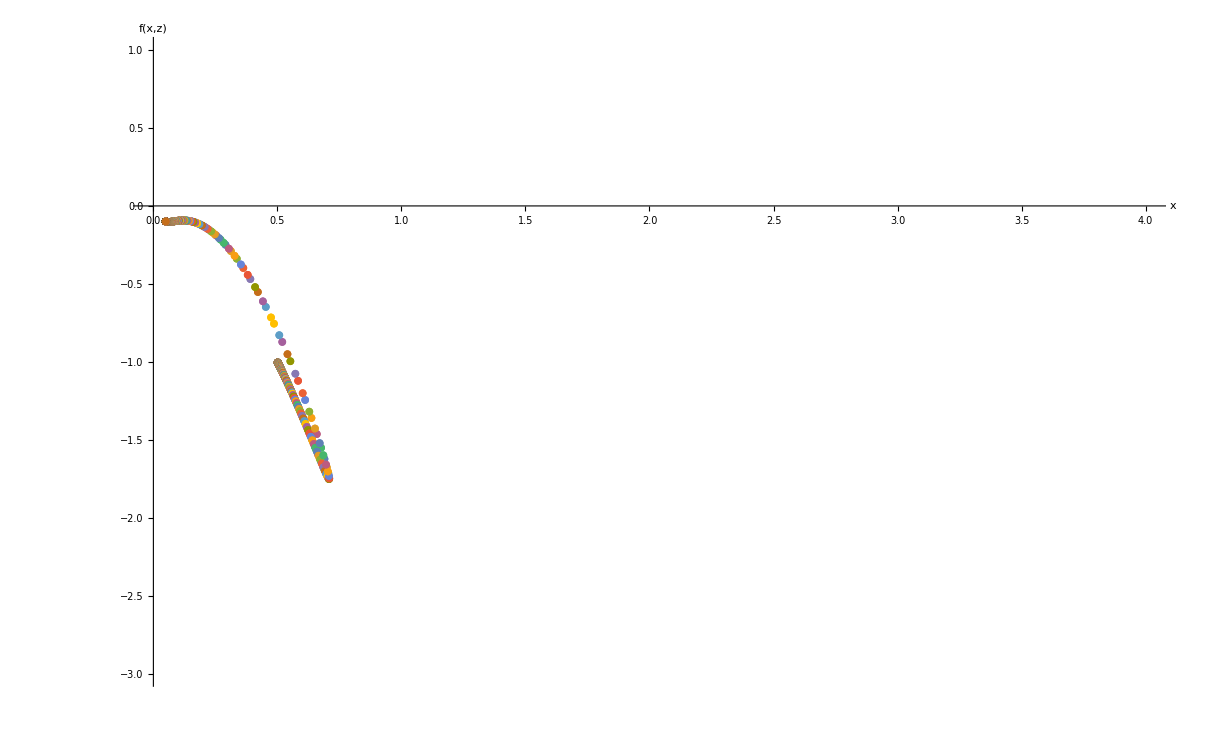

```mathematica
(*Plot x vs the remaining equation when y' = 0*)
(*Here, f(x,z) is never zero, so there are no Einstein fixed points*)
EinsteinPlotNoEinsteinPointsTwoFPs=ListPlot[EinsteinPointSolutionsNoEinsteinPointsTwoFPs,PlotRange->{{0,4},{-3,1}},AxesLabel->{"x","f(x,z)"}]
```

#### Plot the x-y-z Phase Space

```mathematica
(*Find the maximum value of K for this combination of x0 and z0 such that y0 is not imaginary*)
KMaxNoEinsteinPointsTwoFPs=K/.Solve[y0NoEinsteinPointsTwoFPs==0,K][[1]]
```

0.0483863

```mathematica
(*Solve trajNoEinsteinPoints[K] for different values of K*)
```

```mathematica
solNoEinsteinPointsTwoFPs[1]=trajNoEinsteinPointsTwoFPs[-0.01]
```

NDSolve::ndsz: At t == -5.58576, step size is effectively zero; singularity or stiff system suspected.

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solNoEinsteinPointsTwoFPs[2]=trajNoEinsteinPointsTwoFPs[KDensityParametersClosed]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solNoEinsteinPointsTwoFPs[3]=trajNoEinsteinPointsTwoFPs[-.08]
```

NDSolve::ndsz: At t == -3.051, step size is effectively zero; singularity or stiff system suspected.

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solNoEinsteinPointsTwoFPs[4]=trajNoEinsteinPointsTwoFPs[0.025]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solNoEinsteinPointsTwoFPs[5]=trajNoEinsteinPointsTwoFPs[0.01]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solNoEinsteinPointsTwoFPs[6]=trajNoEinsteinPointsTwoFPs[0.04]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the trajectories for the different values of K given above.*)
```

```mathematica
trajNoEinsteinPointsxyzTwoFPs[1]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPointsTwoFPs[1],{t,-5.58,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsxyzTwoFPs[2]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPointsTwoFPs[2],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsxyzTwoFPs[3]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPointsTwoFPs[3],{t,-3.04,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsxyzTwoFPs[4]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPointsTwoFPs[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsxyzTwoFPs[5]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPointsTwoFPs[5],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
trajNoEinsteinPointsxyzTwoFPs[6]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPointsTwoFPs[6],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajNoEinsteinPointsPlotsTwoFPs=Table[trajNoEinsteinPointsxyzTwoFPs[i],{i,1,6}];
```

```mathematica
(*Show the x-y-z phase space*)
Show[trajNoEinsteinPointsPlotsTwoFPs,AccnxyzTwoFPs,FPsxyzTwoFPs,xyzFormat,PlotRange->{{0,1},{-1.5,1.5},{0,1}}]
```

-Graphics3D-

#### Plot the x-z Projection

```mathematica
(*Plot one solution on the x-z plane*)
trajNoEinsteinPointsxzTwoFPs=ParametricPlot[Evaluate[{{z1[t],x1[t]}}/.solNoEinsteinPointsTwoFPs[3],{t,-3.04,100},PlotStyle -> {{Black,Thick, Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.03,.03,0},1]]],Arrow[x]};
```

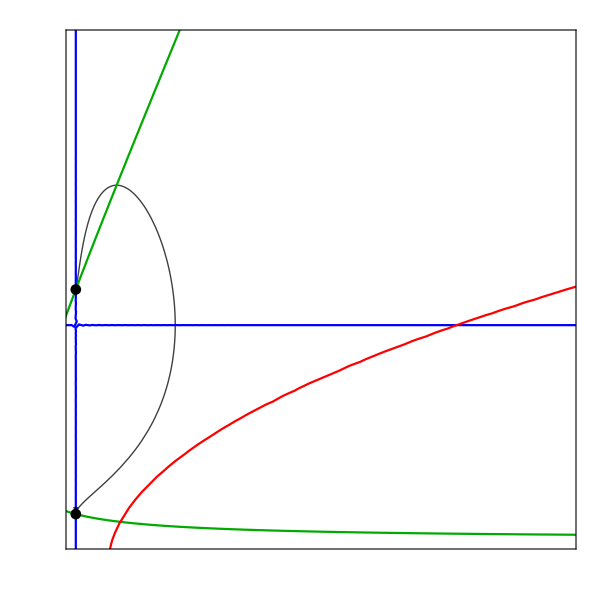

```mathematica
(*Show the x-z phase space with the a'' = 0 (red), x' = 0 (green) and z' = 0 (purple) curves*)
Show[trajNoEinsteinPointsxzTwoFPs,xLineTwoFPs,zLineTwoFPs,AccnxzTwoFPs,FPsxzTwoFPs,xzFormat,PlotRange->{{0,1},{0,1}}]
```

## Compact Phase Spaces: constant X0 and Z0 surfaces

Trajectories are plotted on a constant X0-Z0 surface, where X0 is fixed for all cases and Z0 is fixed for each phase space to give a different number of Einstein fixed points. k and Y0 differ for each trajectory in each phase space.

### Define parameter values and set-up initial conditions

```mathematica
(*Set parameter values*)
wx=-0.5;
q=7;
ϵ=-1;
ℛ=0.05;
```

```mathematica
(*Define Ωx0 and Ωm0 using data from Planck 2018*)
Ωx0=0.6889;
Ωm0=0.3111;
```

```mathematica
(*Set a value for α, which sets the value of the low energy cosmological constant*)
α=0.5;
```

```mathematica
(*Define the initial conditions, where a0 = 1 and K is defined as k/ρ* *)

x0=ℛ/α;
y0=Sqrt[x0/3+Z0/(3*(1-Z0))-K];
```

```mathematica
(*Compactify the initial conditions*)
(*Trajectories are plotted on a constant X0-Z0 surface, where X0 is fixed for all cases and Z0 is fixed for each phase space*)
(*K and Y0 differ for each trajectory in each phase space*)

X0=x0/(1+x0);
Y0=y0/Sqrt[1+y0^2];
```

```mathematica
(*Define values of K using the range of Ωk0 allowed by Planck 2018*)
Ωk0Open=0.003;
Ωk0Closed=-0.001;

KDensityParametersOpen=-Ωk0Open*ℛ/(3*α*Ωx0)
KDensityParametersClosed=-Ωk0Closed*ℛ/(3*α*Ωx0)
```

-0.000145159

0.0000483863

### Set-up for the compact X-Y-Z system

```mathematica
(*Load MaTeX to typeset axis labels using LaTeX*)
<<MaTeX`
```

```mathematica
(*Define a format style for the X-Y-Z phase spaces*)
XYZCompactFormat={AxesLabel->{MaTeX["X",FontSize->22],MaTeX["Y",FontSize->22],MaTeX["Z",FontSize->22]},Ticks->{{0.,0.5,1.0},{-1,-0.5,0.,0.5,1.0},{0.,0.5,1.0}},PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->22}};
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y*)
deX:=X'=-3*(Y/((1-Y^2)^(1/2)))*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))*(Y/((1-Y^2)^(1/2)))
deY:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(X/(1-X))^2)
deZ:=Z'=-3*Z*(1-Z)*(Y/((1-Y^2)^(1/2))) + q*(X/(1-X))*Z*(1-Z)*(Y/((1-Y^2)^(1/2)))
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y in terms of time, t*)
deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*(X1[t]-ℛ*(1-X1[t]))*((1+wx)*(1-X1[t])+ϵ*X1[t])-q*X1[t]*(1-X1[t])*(Z1[t]/(1-Z1[t]))*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((Z1[t]/(1-Z1[t]))+(X1[t]/(1-X1[t]))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X1[t]^2/((1-X1[t])^2))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2))) + q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
```

```mathematica
(*Find the fixed points of the system*)
FPsXYZTwoFPs=Solve[{deX==0,deY==0,deZ==0},{X,Y,Z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Y→0.,Z→(3.+8. X+109. X^2)/(43.-72. X+149. X^2)},{X→0.3,Y→-0.343575,Z→-0.0277923},{X→0.3,Y→0.343575,Z→-0.0277923},{X→0.333333,Y→-0.377964,Z→0.},{X→0.047619,Y→-0.128037,Z→0.},{X→-0.0366972-0.161791 ⅈ,Y→0.,Z→0.},{X→-0.0366972+0.161791 ⅈ,Y→0.,Z→0.},{X→0.047619,Y→0.128037,Z→0.},{X→0.333333,Y→0.377964,Z→0.},{X→0.3,Y→0.,Z→0.436943}}

```mathematica
(*Extract the values of the fixed points and put them into a common variable name*)
FPXYZTwoFPs[1]={X,Y/.FPsXYZTwoFPs[[1,1]],Z/.FPsXYZTwoFPs[[1,2]]};
FPXYZTwoFPs[2]={X/.FPsXYZTwoFPs[[4,1]],Y/.FPsXYZTwoFPs[[4,2]],Z/.FPsXYZTwoFPs[[4,3]]};
FPXYZTwoFPs[3]={X/.FPsXYZTwoFPs[[5,1]],Y/.FPsXYZTwoFPs[[5,2]],Z/.FPsXYZTwoFPs[[5,3]]};
FPXYZTwoFPs[4]={X/.FPsXYZTwoFPs[[8,1]],Y/.FPsXYZTwoFPs[[8,2]],Z/.FPsXYZTwoFPs[[8,3]]};
FPXYZTwoFPs[5]={X/.FPsXYZTwoFPs[[9,1]],Y/.FPsXYZTwoFPs[[9,2]],Z/.FPsXYZTwoFPs[[9,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPXYZTableTwoFPs=Table[FPXYZTwoFPs[i],{i,1,5}];
```

```mathematica
(*Find the 3D Jacobian matrix. D[] differentiates each expression*)
JCompactXYZTwoFPs=Simplify[{{D[deX,X],D[deX,Y],D[deX,Z]},{D[deY,X],D[deY,Y],D[deY,Z]},{D[deZ,X],D[deZ,Y],D[deZ,Z]}}];
JCompactXYZTwoFPs//MatrixForm
```

((Y (1.8+X (-9.45-4.55 Z)+5.2 Z))/(√(1-Y^2) (-1.+Z)) | (0.075+X (-1.8-5.2 Z)-0.075 Z+X^2 (4.725+2.275 Z))/(√(1-Y^2) (-1.+Y^2) (-1.+Z)) | (7 (-1+X) X Y)/(√(1-Y^2) (-1+Z)^2)
(0.941667 (0.0619469+1. X) √(1-Y^2) (-1.+Y^2))/(-1.+X)^3 | (Y (2.0375-2.5375 Z+Y^2 (-3.0375+3.5375 Z)+X (-3.9+Y^2 (5.9-6.9 Z)+4.9 Z)+X^2 (3.3625-3.8625 Z+Y^2 (-4.3625+4.8625 Z))))/((-1.+X)^2 √(1-Y^2) (-1.+Z)) | -((1-Y^2)^(3/2))/(6 (-1+Z)^2)
-(7 Y (-1+Z) Z)/((-1+X)^2 √(1-Y^2)) | ((-3+10 X) (-1+Z) Z)/((-1+X) (1-Y^2)^(3/2)) | ((-3+10 X) Y (-1+2 Z))/((-1+X) √(1-Y^2)))

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableCompactTwoFPs=Table[{FPXYZTableTwoFPs[[i]]//MatrixForm,Simplify[JCompactXYZTwoFPs/.{X->FPXYZTableTwoFPs[[i,1]],Y->FPXYZTableTwoFPs[[i,2]],Z->FPXYZTableTwoFPs[[i,3]]}]//MatrixForm,Eigenvalues[JCompactXYZTwoFPs/.{X->FPXYZTableTwoFPs[[i,1]],Y->FPXYZTableTwoFPs[[i,2]],Z->FPXYZTableTwoFPs[[i,3]]}]//MatrixForm,Eigenvectors[JCompactXYZTwoFPs/.{X->FPXYZTableTwoFPs[[i,1]],Y->FPXYZTableTwoFPs[[i,2]],Z->FPXYZTableTwoFPs[[i,3]]}]//MatrixForm},{i,1,5}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableXYZTwoFPs=TableForm[FPTableCompactTwoFPs,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(X
0.
(3.+8. X+109. X^2)/(43.-72. X+149. X^2)) | (0. | (0.075-2.475 X+7.525 X^2-28.925 X^3+23.8 X^4)/(1.-2. X+1. X^2) | 0.
(-0.0583333-0.941667 X)/(-1.+X)^3 | 0. | -(2.3126 (0.288591-0.483221 X+1. X^2)^2)/((1.-2. X+1. X^2)^2)
0. | (0.0162155-0.0432413 X+0.482861 X^2-2.86474 X^3+4.37278 X^4-1.96388 X^5)/((-1.+X) (0.288591-0.483221 X+1. X^2)^2) | 0.) | (0
-(√(143162.-2.26868×10^6 X+1.49175×10^7 X^2-6.28963×10^7 X^3+1.33725×10^8 X^4+2.59944×10^8 X^5-3.86788×10^9 X^6+2.00721×10^10 X^7-7.08086×10^10 X^8+1.90191×10^11 X^9-4.04332×10^11 X^10+6.90121×10^11 X^11-9.46426×10^11 X^12+1.0326×10^12 X^13-8.77141×10^11 X^14+5.58114×10^11 X^15-2.48879×10^11 X^16+6.88202×10^10 X^17-8.80784×10^9 X^18))/((-1.+X)^4 √(1.-2. X+1. X^2) (43.-72. X+149. X^2)^2)
(√(143162.-2.26868×10^6 X+1.49175×10^7 X^2-6.28963×10^7 X^3+1.33725×10^8 X^4+2.59944×10^8 X^5-3.86788×10^9 X^6+2.00721×10^10 X^7-7.08086×10^10 X^8+1.90191×10^11 X^9-4.04332×10^11 X^10+6.90121×10^11 X^11-9.46426×10^11 X^12+1.0326×10^12 X^13-8.77141×10^11 X^14+5.58114×10^11 X^15-2.48879×10^11 X^16+6.88202×10^10 X^17-8.80784×10^9 X^18))/((-1.+X)^4 √(1.-2. X+1. X^2) (43.-72. X+149. X^2)^2)) | (-(2.45586 (-1.+X)^3 (0.288591-0.483221 X+1. X^2)^2)/((0.0619469+1. X) (1.-2. X+1. X^2)^2) | 0 | 1.
-(1. (-0.0000164095+0.00050139 X+0.00168872 X^2-0.082314 X^3+0.91284 X^4-6.24724 X^5+31.1456 X^6-120.9 X^7+378.174 X^8-971.923 X^9+2074.35 X^10-3693.36 X^11+5483.13 X^12-6750.7 X^13+6818.26 X^14-5550.59 X^15+3544.8 X^16-1704.08 X^17+577.218 X^18-122.235 X^19+12.1189 X^20))/((-1.+1. X)^6 (-0.3+1. X) (0.0619469+1. X) (1.-2. X+1. X^2)^2 (0.288591-0.483221 X+1. X^2)^2 (0.0275229+0.0733945 X+1. X^2)) | ((0.+1.39989×10^-8 ⅈ) √(-3.84298×10^13+6.08995×10^14 X-4.00439×10^15 X^2+1.68836×10^16 X^3-3.58965×10^16 X^4-6.97781×10^16 X^5+1.03828×10^18 X^6-5.38806×10^18 X^7+1.90075×10^19 X^8-5.1054×10^19 X^9+1.08537×10^20 X^10-1.85253×10^20 X^11+2.54054×10^20 X^12-2.77186×10^20 X^13+2.35456×10^20 X^14-1.49818×10^20 X^15+6.68079×10^19 X^16-1.84738×10^19 X^17+2.36434×10^18 X^18))/((-1.+X)^3 (-1.+1. X) (-3.+10. X) (1.-2. X+1. X^2) (0.0275229+0.0733945 X+1. X^2)) | 1.
-(1. (-0.0000164095+0.00050139 X+0.00168872 X^2-0.082314 X^3+0.91284 X^4-6.24724 X^5+31.1456 X^6-120.9 X^7+378.174 X^8-971.923 X^9+2074.35 X^10-3693.36 X^11+5483.13 X^12-6750.7 X^13+6818.26 X^14-5550.59 X^15+3544.8 X^16-1704.08 X^17+577.218 X^18-122.235 X^19+12.1189 X^20))/((-1.+1. X)^6 (-0.3+1. X) (0.0619469+1. X) (1.-2. X+1. X^2)^2 (0.288591-0.483221 X+1. X^2)^2 (0.0275229+0.0733945 X+1. X^2)) | -((0.+1.39989×10^-8 ⅈ) √(-3.84298×10^13+6.08995×10^14 X-4.00439×10^15 X^2+1.68836×10^16 X^3-3.58965×10^16 X^4-6.97781×10^16 X^5+1.03828×10^18 X^6-5.38806×10^18 X^7+1.90075×10^19 X^8-5.1054×10^19 X^9+1.08537×10^20 X^10-1.85253×10^20 X^11+2.54054×10^20 X^12-2.77186×10^20 X^13+2.35456×10^20 X^14-1.49818×10^20 X^15+6.68079×10^19 X^16-1.84738×10^19 X^17+2.36434×10^18 X^18))/((-1.+X)^3 (-1.+1. X) (-3.+10. X) (1.-2. X+1. X^2) (0.0275229+0.0733945 X+1. X^2)) | 1.)
(0.333333
-0.377964
0.) | (-0.551135 | 1.39904×10^-16 | 0.635053
0.99691 | 0.816497 | -0.13226
0. | 0. | -0.204124) | (0.816497
-0.551135
-0.204124) | (-3.04065×10^-17 | -1. | 0.
-0.808098 | 0.589048 | 0.
0.686909 | -0.622311 | 0.375347)
(0.047619
-0.128037
0.) | (0.174284 | 0. | 0.040984
0.116513 | 0.258199 | -0.162585
0. | 0. | 0.342114) | (0.342114
0.258199
0.174284) | (0.128444 | -0.840744 | 0.525977
0. | 1. | 0.
0.584422 | -0.81145 | 0.)
(0.047619
0.128037
0.) | (-0.174284 | 0. | -0.040984
0.116513 | -0.258199 | -0.162585
0. | 0. | -0.342114) | (-0.342114
-0.258199
-0.174284) | (0.128444 | 0.840744 | 0.525977
0. | 1. | 0.
0.584422 | 0.81145 | 0.)
(0.333333
0.377964
0.) | (0.551135 | 1.39904×10^-16 | -0.635053
0.99691 | -0.816497 | -0.13226
0. | 0. | 0.204124) | (-0.816497
0.551135
0.204124) | (-3.04065×10^-17 | 1. | 0.
0.808098 | 0.589048 | 0.
0.686909 | 0.622311 | 0.375347)

```mathematica
(*Plot the fixed points of the system*)
FPsXYZTwoFPs=ListPointPlot3D[Table[FPXYZTwoFPs[i],{i,2,5}], PlotStyle->{Black}];
```

```mathematica
(*Extra fixed points exist when the system is compactified*)
(*Find the de Sitter fixed points at Y = +-1*)
```

```mathematica
(*Solve X' = 0 when Y = +- 1 for Z*)
ZXPrimeZeroTwoFPs=Z/.Solve[-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))==0,Z]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{-(3. (1.-24. X+63. X^2))/(-3.-208. X+91. X^2)}

```mathematica
(*Substitute Z = ZXPrimeZero into Z' at Y = +-1*)
ZPrimeTwoFPs=Flatten[-3*Z*(1-Z) + q*(X/(1-X))*Z*(1-Z)/.Z->ZXPrimeZeroTwoFPs][[1]]
```

(9. (1.-24. X+63. X^2) (1+(3. (1.-24. X+63. X^2))/(-3.-208. X+91. X^2)))/(-3.-208. X+91. X^2)-(21. X (1.-24. X+63. X^2) (1+(3. (1.-24. X+63. X^2))/(-3.-208. X+91. X^2)))/((1-X) (-3.-208. X+91. X^2))

```mathematica
(*Solve ZPrime = 0 (Z' = 0) for X*)
XdSSolTwoFPs=X/.FindRoot[ZPrimeTwoFPs==0,{X,0.75}]
```

0.333333

```mathematica
(*Subsitute XdSSol into ZXPrimeZero to find the value of Z at the fixed point*)
ZdSSolTwoFPs=Flatten[ZXPrimeZeroTwoFPs/.X->XdSSolTwoFPs][[1]]
```

0.

```mathematica
(*Plot the fixed points from compactification*)
CompactFPShowXYZTwoFPs=ListPointPlot3D[{{XdSSolTwoFPs,1,ZdSSolTwoFPs},{XdSSolTwoFPs,-1,ZdSSolTwoFPs}}, PlotStyle->{Black}];
```

```mathematica
(*Define the acceleration equation*)
AccnCompactTwoFPs=((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(X/(1-X))^2)/Sqrt[1+((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(X/(1-X))^2)^2]
```

(-0.075-(0.35 X)/(1-X)-(3 X^2)/(1-X)^2+Z/(1-Z))/(√(1+(-0.075-(0.35 X)/(1-X)-(3 X^2)/(1-X)^2+Z/(1-Z))^2))

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
AccnXYZTwoFPs=ContourPlot3D[AccnCompactTwoFPs==0,{X,0,1},{Y,-1,1},{Z,0,1},ContourStyle->{Red,Opacity[0.25]},Mesh->None];
```

### Set-up for the compact X-Z system

```mathematica
(*Define a format style for the X-Z phase spaces*)
XZCompactFormat={Frame->True,FrameLabel->{MaTeX["Z",FontSize->24],Rotate[MaTeX["X",FontSize->24],300]},FrameTicks->{{Table[{X,MaTeX[X,"DisplayStyle"->False,FontSize->24]},{X,0.5Range[-1,2]}],None},{Table[{Z,MaTeX[Z,"DisplayStyle"->False,FontSize->24]},{Z,0.5Range[-1,2]}],None}},PlotRange->{{0,1},{0,1}},ImageSize->{600,600},PlotRangePadding->{0.01,0}};
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, and dark matter, Z*)
deX:=X'=-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))
deZ:=Z'=-3*Z*(1-Z)+ q*(X/(1-X))*Z*(1-Z)
```

```mathematica
(*Find the fixed points of the system*)
FPsXZTwoFPs=Solve[{deZ==0,deX==0},{Z,X}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Z→0.,X→0.047619},{Z→-0.0277923,X→0.3},{Z→0.,X→0.333333}}

```mathematica
(*Extract the values of the fixed points and put them into a common variable name*)
FPXZTwoFPs[1]={Z/.FPsXZTwoFPs[[1,1]],X/.FPsXZTwoFPs[[1,2]]};
FPXZTwoFPs[2]={Z/.FPsXZTwoFPs[[3,1]],X/.FPsXZTwoFPs[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPXZTableTwoFPs=Table[FPXZTwoFPs[i],{i,1,2}];
```

```mathematica
(*Find the 2D Jacobian matrix. D[] differentiates each expression*)
JCompactXZTwoFPs=Simplify[{{D[deZ,Z],D[deZ,X]},{D[deX,Z],D[deX,X]}}];
JCompactXZTwoFPs//MatrixForm
```

(((-3+10 X) (-1+2 Z))/(-1+X) | -(7 (-1+Z) Z)/(-1+X)^2
(7 (-1+X) X)/(-1+Z)^2 | (1.8+X (-9.45-4.55 Z)+5.2 Z)/(-1.+Z))

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTableCompactTwoFPs=Table[{FPXZTableTwoFPs[[i]]//MatrixForm,Simplify[JCompactXZTwoFPs/.{Z->FPXZTableTwoFPs[[i,1]],X->FPXZTableTwoFPs[[i,2]]}]//MatrixForm,Eigenvalues[JCompactXZTwoFPs/.{Z->FPXZTableTwoFPs[[i,1]],X->FPXZTableTwoFPs[[i,2]]}]//MatrixForm,Eigenvectors[JCompactXZTwoFPs/.{Z->FPXZTableTwoFPs[[i,1]],X->FPXZTableTwoFPs[[i,2]]}]//MatrixForm},{i,1,2}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableXZTwoFPs=TableForm[FPTableCompactTwoFPs,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.
0.047619) | (-2.65 | 0.
-0.31746 | -1.35) | (-2.65
-1.35) | (0.971454 | 0.237229
0. | 1.)
(0.
0.333333) | (0.5 | 0.
-1.55556 | 1.35) | (1.35
0.5) | (0. | 1.
0.479511 | 0.877536)

```mathematica
(*Plot the fixed points of the system*)
FPsXZTwoFPs=ListPlot[FPXZTableTwoFPs, PlotStyle->{Black}];
```

```mathematica
(*Plot the fixed points from compactification*)
CompactFPShowXZTwoFPs=ListPlot[{{ZdSSolTwoFPs,XdSSolTwoFPs}}, PlotStyle->{Black}];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions on the X-Z plane*)
AccnXZTwoFPs=ContourPlot[AccnCompactTwoFPs==0,{Z,0,1},{X,0,1},ContourStyle->{Red},Mesh->None,PlotPoints->300];
```

```mathematica
(*Plot the curves where Z' = 0*)
ZLineTwoFPs=ContourPlot[-3*Z*(1-Z) + q*(X/(1-X))*Z*(1-Z)==0,{Z,-.1,1},{X,0,1},ContourStyle->Blue,PlotPoints->300];
```

```mathematica
(*Plot the curves where X' = 0*)
XLineTwoFPs=ContourPlot[-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))==0,{Z,0,1},{X,0,1},ContourStyle->Darker[Green],PlotPoints->300];
```

### Limiting Case

#### Find the Einstein Fixed Point

```mathematica
(*Fix z0 so that there is one Einstein fixed point on the surface*)
z0LimitingTwoFPs=0.115;
```

```mathematica
(*Compactify z0*)
Z0LimitingTwoFPs=z0LimitingTwoFPs/(1+z0LimitingTwoFPs)
```

0.103139

```mathematica
(*Substitute Z0Limiting into Y0 for this case*)
Y0LimitingTwoFPs=Y0/.Z0->Z0LimitingTwoFPs
```

(√(0.0716667-K))/(√(1.07167-K))

```mathematica
(*Numerically solve the system of compact equations using the initial conditions defined for the limiting case with one Einstein fixed point*)
trajLimitingCompactTwoFPsEinsteinPointPlot[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0LimitingTwoFPs,Z1[0]==Z0LimitingTwoFPs},{X1,Y1,Z1},{t,-20.79,100}]
```

NDSolve::ndinnt: Initial condition (√(0.0716667-1. K))/(√(1.07167-1. K)) is not a number or a rectangular array of numbers.

NDSolve[{X1'[t]==-(3 (0.5 (1-X1[t])-X1[t]) (-0.05 (1-X1[t])+X1[t]) Y1[t])/(√(1-Y1[t]^2))-(7 (1-X1[t]) X1[t] Y1[t] Z1[t])/(√(1-Y1[t]^2) (1-Z1[t])),Y1'[t]==-Y1[t]^2 √(1-Y1[t]^2)-1/6 (1-Y1[t]^2)^(3/2) (-0.075-(0.35 X1[t])/(1-X1[t])-(3 X1[t]^2)/(1-X1[t])^2+Z1[t]/(1-Z1[t])),Z1'[t]==-(3 Y1[t] (1-Z1[t]) Z1[t])/(√(1-Y1[t]^2))+(7 X1[t] Y1[t] (1-Z1[t]) Z1[t])/((1-X1[t]) √(1-Y1[t]^2)),X1[0]==0.0909091,Y1[0]==(√(0.0716667-K))/(√(1.07167-K)),Z1[0]==0.103139},{X1,Y1,Z1},{t,-20.79,100}]

```mathematica
(*Set-up tables of all X1 and Z1 values to be used to find the X and Z value of the Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
XTableSolLimitingCompactTwoFPs=Table[X1[i]/.trajLimitingCompactTwoFPsEinsteinPointPlot[0],{i,-20.79,100,.01}];
ZTableSolLimitingCompactTwoFPs=Table[Z1[i]/.trajLimitingCompactTwoFPsEinsteinPointPlot[0],{i,-20.79,100,.01}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSolLimitingCompactTwoFPs=(ZTableSolLimitingCompactTwoFPs/(1-ZTableSolLimitingCompactTwoFPs))+(XTableSolLimitingCompactTwoFPs/(1-XTableSolLimitingCompactTwoFPs))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSolLimitingCompactTwoFPs/(1-XTableSolLimitingCompactTwoFPs))^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSolLimitingCompact that is closest to zero. When EinsteinPlotValuesSolLimitingCompact = 0 (Y = 0), there is an Einstein point*)
NearestToZeroLimitingCompactTwoFPs=Flatten[Nearest[EinsteinPlotValuesSolLimitingCompactTwoFPs,0]]
```

{-0.00396263}

```mathematica
(*Find the position of NearestToZeroLimitingCompact in the EinsteinPlotValuesSolLimitingCompact array*)
PositionNearestToZeroLimitingCompactTwoFPs=Flatten[Position[EinsteinPlotValuesSolLimitingCompactTwoFPs,NearestToZeroLimitingCompactTwoFPs]]
```

{2003}

```mathematica
(*Find the Einstein point by finding the X and Z values in XTableSolLimitingCompact and ZTableSolLimitingCompact at PositionNearestToZeroLimitingCompact*)
EinsteinPointLimitingCompactTwoFPs=Flatten[{XTableSolLimitingCompactTwoFPs[[PositionNearestToZeroLimitingCompactTwoFPs]],0,ZTableSolLimitingCompactTwoFPs[[PositionNearestToZeroLimitingCompactTwoFPs]]}]
```

{0.128972,0,0.158699}

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for the Einstein fixed point*)
EinsteinTableLimitingCompactTwoFPs=Table[{EinsteinPointLimitingCompactTwoFPs//MatrixForm,Simplify[JCompactXYZTwoFPs/.{X->EinsteinPointLimitingCompactTwoFPs[[1]],Y->EinsteinPointLimitingCompactTwoFPs[[2]],Z->EinsteinPointLimitingCompactTwoFPs[[3]]}]//MatrixForm,Eigenvalues[JCompactXYZTwoFPs/.{X->EinsteinPointLimitingCompactTwoFPs[[1]],Y->EinsteinPointLimitingCompactTwoFPs[[2]],Z->EinsteinPointLimitingCompactTwoFPs[[3]]}]//MatrixForm,Eigenvectors[JCompactXYZTwoFPs/.{X->EinsteinPointLimitingCompactTwoFPs[[1]],Y->EinsteinPointLimitingCompactTwoFPs[[2]],Z->EinsteinPointLimitingCompactTwoFPs[[3]]}]//MatrixForm},1];
```

```mathematica
(*Use TableForm to display the Einstein fixed point with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableEinsteinPointLimitingCompactTwoFPs=TableForm[EinsteinTableLimitingCompactTwoFPs,TableHeadings->{None,{"Einstein Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Einstein Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.128972
0
0.158699) | (0. | -0.226892 | 0.
0.272051 | 0. | -0.235476
0. | -0.262156 | 0.) | (-0.00223401
0.00223401
4.17291×10^-13) | (0.654407 | 0.00644339 | 0.756115
0.654407 | -0.00644339 | 0.756115
-0.65445 | 1.20332×10^-12 | -0.756105)

```mathematica
(*Set-up tables of all X1 and Z1 values with a bigger t increment*)
XTableSolLimitingFullCompactTwoFPs=Table[X1[i]/.trajLimitingCompactTwoFPsEinsteinPointPlot[0],{i,-20.79,100,.1}];
ZTableSolLimitingFullCompactTwoFPs=Table[Z1[i]/.trajLimitingCompactTwoFPsEinsteinPointPlot[0],{i,-20.79,100,.1}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0*)
EinsteinPlotValuesSolLimitingFullXZTwoFPs=(ZTableSolLimitingFullCompactTwoFPs/(1-ZTableSolLimitingFullCompactTwoFPs))+(XTableSolLimitingFullCompactTwoFPs/(1-XTableSolLimitingFullCompactTwoFPs))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSolLimitingFullCompactTwoFPs/(1-XTableSolLimitingFullCompactTwoFPs))^2;
```

```mathematica
(*Compactify EinsteinPlotValuesSolLimitingFullXZ*)
EinsteinPlotValuesSolLimitingFullCompactTwoFPs=EinsteinPlotValuesSolLimitingFullXZTwoFPs/Sqrt[1+EinsteinPlotValuesSolLimitingFullXZTwoFPs^2];
```

```mathematica
(*Merge the XTableSolLimitingFullCompact values and the EinsteinPlotValuesSolLimitingFullCompact values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsLimitingCompactTwoFPs=MapThread[h,{XTableSolLimitingFullCompactTwoFPs,EinsteinPlotValuesSolLimitingFullCompactTwoFPs}];
```

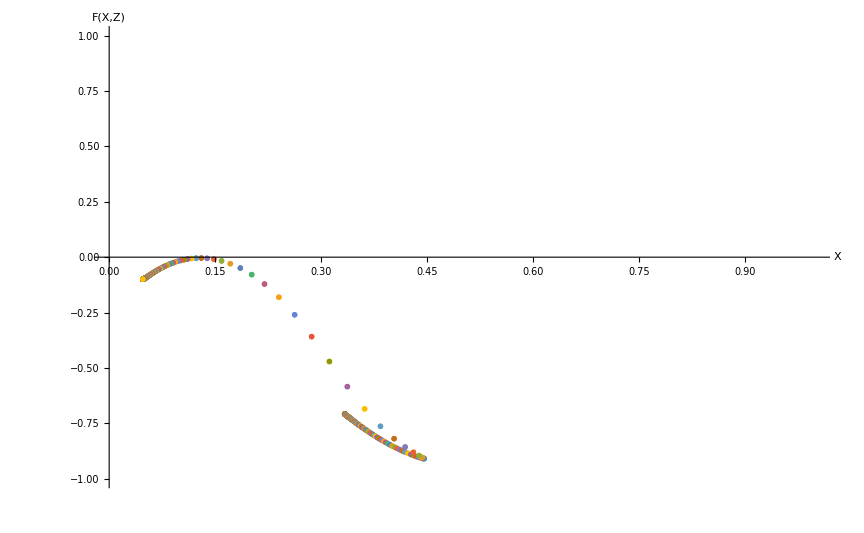

```mathematica
(*Plot X vs the remaining equation when Y' = 0*)
(*When F(X,Z) = 0, an Einstein point exists*)
EinsteinPlotLimitingCompactTwoFPs=ListPlot[EinsteinPointSolutionsLimitingCompactTwoFPs,PlotRange->{{0,1},{-1,1}},AxesLabel->{"X","F(X,Z)"}]
```

#### Plot the X-Y-Z Phase Space

```mathematica
(*Numerically solve the system of compact equations using the initial conditions defined for the limiting case with one Einstein fixed point*)
trajLimitingCompactTwoFPs[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0LimitingTwoFPs,Z1[0]==Z0LimitingTwoFPs},{X1,Y1,Z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition (√(0.0716667-1. K))/(√(1.07167-1. K)) is not a number or a rectangular array of numbers.

NDSolve[{X1'[t]==-(3 (0.5 (1-X1[t])-X1[t]) (-0.05 (1-X1[t])+X1[t]) Y1[t])/(√(1-Y1[t]^2))-(7 (1-X1[t]) X1[t] Y1[t] Z1[t])/(√(1-Y1[t]^2) (1-Z1[t])),Y1'[t]==-Y1[t]^2 √(1-Y1[t]^2)-1/6 (1-Y1[t]^2)^(3/2) (-0.075-(0.35 X1[t])/(1-X1[t])-(3 X1[t]^2)/(1-X1[t])^2+Z1[t]/(1-Z1[t])),Z1'[t]==-(3 Y1[t] (1-Z1[t]) Z1[t])/(√(1-Y1[t]^2))+(7 X1[t] Y1[t] (1-Z1[t]) Z1[t])/((1-X1[t]) √(1-Y1[t]^2)),X1[0]==0.0909091,Y1[0]==(√(0.0716667-K))/(√(1.07167-K)),Z1[0]==0.103139},{X1,Y1,Z1},{t,-100,100}]

```mathematica
(*Find the maximum value of K for this combination of X0 and Z0 such that Y0 is not imaginary*)
KMaxLimitingCompactTwoFPs=K/.Solve[Y0LimitingTwoFPs==0,K][[1]]
```

0.0716667

```mathematica
(*Solve trajLimitingCompact[K] for different values of K*)
```

```mathematica
solLimitingCompactTwoFPs[1]=trajLimitingCompactTwoFPs[0.03]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solLimitingCompactTwoFPs[2]=trajLimitingCompactTwoFPs[KDensityParametersClosed]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solLimitingCompactTwoFPs[3]=trajLimitingCompactTwoFPs[-.05]
```

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate,0.,Indeterminate} is not a list of numbers with dimensions {3} at {t,X1[t],Y1[t],Z1[t]} = {-3.33465,0.333334,1.,5.99195×10^-7}.

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solLimitingCompactTwoFPs[4]=trajLimitingCompactTwoFPs[KMaxLimitingCompactTwoFPs]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solLimitingCompactTwoFPs[5]=trajLimitingCompactTwoFPs[-0.01]
```

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate,0.,Indeterminate} is not a list of numbers with dimensions {3} at {t,X1[t],Y1[t],Z1[t]} = {-4.98287,0.333334,1.,6.16269×10^-7}.

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solLimitingCompactTwoFPs[6]=trajLimitingCompactTwoFPs[0.06]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the trajectories for the different values of K given above.*)
```

```mathematica
trajLimitingCompactXYZTwoFPs[1]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactTwoFPs[1],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCompactXYZTwoFPs[2]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactTwoFPs[2],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCompactXYZTwoFPs[3]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactTwoFPs[3],{t,-3.32,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCompactXYZTwoFPs[4]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactTwoFPs[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCompactXYZTwoFPs[5]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactTwoFPs[5],{t,-4.97,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCompactXYZTwoFPs[6]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompactTwoFPs[6],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajLimitingCaseCompactTwoFPs=Table[trajLimitingCompactXYZTwoFPs[i],{i,1,6}];
```

```mathematica
(*Plot the Einstein fixed point*)
EinsteinFixedPointsLimitingCompactTwoFPs=ListPointPlot3D[{EinsteinPointLimitingCompactTwoFPs},PlotStyle->Black];
```

```mathematica
(*Solve theX-Y-Z system around the Einstein fixed point to plot the Closed Friedmann Separatrix (CFS)*)
CFSLimitingSolCompactTwoFPs=NDSolve[{deXt,deYt,deZt,X1[0]==EinsteinPointLimitingCompactTwoFPs[[1]],Y1[0]==0,Z1[0]==EinsteinPointLimitingCompactTwoFPs[[3]]},{X1,Y1,Z1},{t,-100,100}]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the CFS*)
CFSLimitingCompactTwoFPs=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.CFSLimitingSolCompactTwoFPs,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
(*Show the X-Y-Z phase space*)
Show[trajLimitingCaseCompactTwoFPs,EinsteinFixedPointsLimitingCompactTwoFPs,CFSLimitingCompactTwoFPs,AccnXYZTwoFPs,FPsXYZTwoFPs,CompactFPShowXYZTwoFPs,XYZCompactFormat]
```

-Graphics3D-

#### Plot the X-Z Projection

```mathematica
(*Plot one solution on the X-Z plane*)
trajLimitingCompactXZTwoFPs=ParametricPlot[Evaluate[{{Z1[t],X1[t]}}/.solLimitingCompactTwoFPs[3],{t,-3.32,100},PlotStyle -> {{Black, Thick,Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.03,.03,0},1]]],Arrow[x]};
```

```mathematica
(*Plot the Einstein fixed point on the X-Z plane*)
EinsteinFixedPointsLimitingCompactXZTwoFPs=ListPlot[{{EinsteinPointLimitingCompactTwoFPs[[3]],EinsteinPointLimitingCompactTwoFPs[[1]]}},PlotStyle->Black];
```

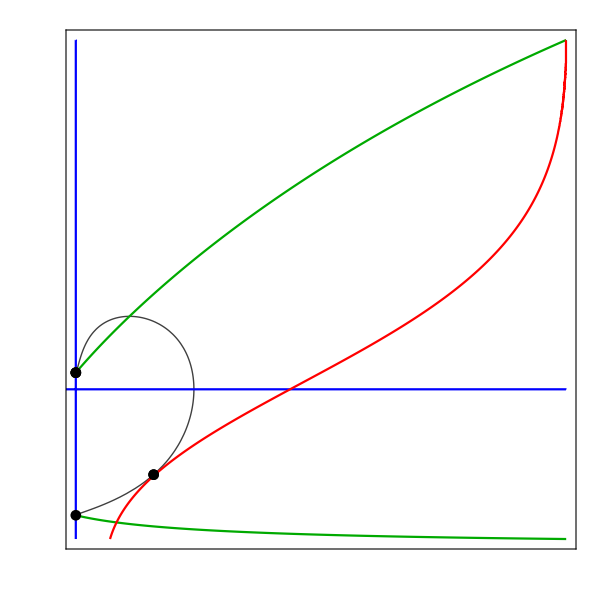

```mathematica
(*Show the X-Z phase space with the a'' = 0 (red), X' = 0 (green) and Z' = 0 (purple) curves*)
Show[trajLimitingCompactXZTwoFPs,XLineTwoFPs,ZLineTwoFPs,AccnXZTwoFPs,EinsteinFixedPointsLimitingCompactXZTwoFPs,FPsXZTwoFPs,CompactFPShowXZTwoFPs,XZCompactFormat]
```

### Two Einstein Fixed Points

#### Find the Einstein Fixed Points

```mathematica
(*Fix z0 using the density parameters*)
z0TwoEinsteinPointsTwoFPs=0.3;
```

```mathematica
(*Compactify z0*)
Z0TwoEinsteinPointsTwoFPs=z0TwoEinsteinPointsTwoFPs/(1+z0TwoEinsteinPointsTwoFPs)
```

0.230769

```mathematica
(*Substitute Z0TwoEinsteinPoints into Y0 for this case*)
Y0TwoEinsteinPointsTwoFPs=Y0/.Z0->Z0TwoEinsteinPointsTwoFPs
```

(√(0.133333-K))/(√(1.13333-K))

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajTwoEinsteinPointsCompactTwoFPsEinsteinPointPlot[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0TwoEinsteinPointsTwoFPs,Z1[0]==Z0TwoEinsteinPointsTwoFPs},{X1,Y1,Z1},{t,-20.3,100}]
```

NDSolve::ndinnt: Initial condition (√(0.133333-1. K))/(√(1.13333-1. K)) is not a number or a rectangular array of numbers.

NDSolve[{X1'[t]==-(3 (0.5 (1-X1[t])-X1[t]) (-0.05 (1-X1[t])+X1[t]) Y1[t])/(√(1-Y1[t]^2))-(7 (1-X1[t]) X1[t] Y1[t] Z1[t])/(√(1-Y1[t]^2) (1-Z1[t])),Y1'[t]==-Y1[t]^2 √(1-Y1[t]^2)-1/6 (1-Y1[t]^2)^(3/2) (-0.075-(0.35 X1[t])/(1-X1[t])-(3 X1[t]^2)/(1-X1[t])^2+Z1[t]/(1-Z1[t])),Z1'[t]==-(3 Y1[t] (1-Z1[t]) Z1[t])/(√(1-Y1[t]^2))+(7 X1[t] Y1[t] (1-Z1[t]) Z1[t])/((1-X1[t]) √(1-Y1[t]^2)),X1[0]==0.0909091,Y1[0]==(√(0.133333-K))/(√(1.13333-K)),Z1[0]==0.230769},{X1,Y1,Z1},{t,-20.3,100}]

```mathematica
(*Set-up tables of X1 and Z1 values to be used to find the X and Z value of the first Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
XTableSol1TwoEinsteinPointsCompactTwoFPs=Table[X1[i]/.trajTwoEinsteinPointsCompactTwoFPsEinsteinPointPlot[0],{i,1,100,.01}];
ZTableSol1TwoEinsteinPointsCompactTwoFPs=Table[Z1[i]/.trajTwoEinsteinPointsCompactTwoFPsEinsteinPointPlot[0],{i,1,100,.01}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol1TwoEinsteinPointsCompactTwoFPs=(ZTableSol1TwoEinsteinPointsCompactTwoFPs/(1-ZTableSol1TwoEinsteinPointsCompactTwoFPs))+(XTableSol1TwoEinsteinPointsCompactTwoFPs/(1-XTableSol1TwoEinsteinPointsCompactTwoFPs))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSol1TwoEinsteinPointsCompactTwoFPs/(1-XTableSol1TwoEinsteinPointsCompactTwoFPs))^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol1TwoEinsteinPointsCompact that is closest to zero. When EinsteinPlotValuesSol1TwoEinsteinPointsCompact = 0 (Y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints1CompactTwoFPs=Flatten[Nearest[EinsteinPlotValuesSol1TwoEinsteinPointsCompactTwoFPs,0]]
```

{0.000109305}

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints1Compact in the EinsteinPlotValuesSol1TwoEinsteinPointsCompact*)
PositionNearestToZeroTwoEinsteinPoints1CompactTwoFPs=Flatten[Position[EinsteinPlotValuesSol1TwoEinsteinPointsCompactTwoFPs,NearestToZeroTwoEinsteinPoints1CompactTwoFPs]]
```

{55}

```mathematica
(*Find the Einstein point by finding the X and Z values in XTableSol1TwoEinsteinPointsCompact and ZTableSol1TwoEinsteinPointsCompact at PositionNearestToZeroTwoEinsteinPoints1Compact*)
EinsteinPoint1TwoEinsteinPointsCompactTwoFPs=Flatten[{XTableSol1TwoEinsteinPointsCompactTwoFPs[[PositionNearestToZeroTwoEinsteinPoints1CompactTwoFPs]],0,ZTableSol1TwoEinsteinPointsCompactTwoFPs[[PositionNearestToZeroTwoEinsteinPoints1CompactTwoFPs]]}]
```

{0.0479786,0,0.0912128}

```mathematica
(*Set-up tables of X1 and Z1 values to be used to find the X and Z value of the second Einstein fixed point*)
(*The value of K here does not matter, so K is set to 0 to find the Einstein fixed point*)
XTableSol2TwoEinsteinPointsCompactTwoFPs=Table[X1[i]/.trajTwoEinsteinPointsCompactTwoFPsEinsteinPointPlot[0],{i,-5.6,0,.001}];
ZTableSol2TwoEinsteinPointsCompactTwoFPs=Table[Z1[i]/.trajTwoEinsteinPointsCompactTwoFPsEinsteinPointPlot[0],{i,-5.6,0,.001}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0 to find the Einstein fixed point*)
EinsteinPlotValuesSol2TwoEinsteinPointsCompactTwoFPs=(ZTableSol2TwoEinsteinPointsCompactTwoFPs/(1-ZTableSol2TwoEinsteinPointsCompactTwoFPs))+(XTableSol2TwoEinsteinPointsCompactTwoFPs/(1-XTableSol2TwoEinsteinPointsCompactTwoFPs))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSol2TwoEinsteinPointsCompactTwoFPs/(1-XTableSol2TwoEinsteinPointsCompactTwoFPs))^2;
```

```mathematica
(*Find the value in EinsteinPlotValuesSol2TwoEinsteinPointsCompact that is closest to zero. When EinsteinPlotValuesSol2TwoEinsteinPointsCompact = 0 (Y = 0), there is an Einstein point*)
NearestToZeroTwoEinsteinPoints2CompactTwoFPs=Flatten[Nearest[EinsteinPlotValuesSol2TwoEinsteinPointsCompactTwoFPs,0]]
```

{-0.000015305}

```mathematica
(*Find the position of NearestToZeroTwoEinsteinPoints2Compact in the EinsteinPlotValuesSol2TwoEinsteinPointsCompact array*)
PositionNearestToZeroTwoEinsteinPoints2CompactTwoFPs=Flatten[Position[EinsteinPlotValuesSol2TwoEinsteinPointsCompactTwoFPs,NearestToZeroTwoEinsteinPoints2CompactTwoFPs]]
```

{4840}

```mathematica
(*Find the Einstein point by finding the X and Z values in XTableSol2TwoEinsteinPointsCompact and ZTableSol2TwoEinsteinPointsCompact at PositionNearestToZeroTwoEinsteinPoints2Compact*)
EinsteinPoint2TwoEinsteinPointsCompactTwoFPs=Flatten[{XTableSol2TwoEinsteinPointsCompactTwoFPs[[PositionNearestToZeroTwoEinsteinPoints2CompactTwoFPs]],0,ZTableSol2TwoEinsteinPointsCompactTwoFPs[[PositionNearestToZeroTwoEinsteinPoints2CompactTwoFPs]]}]
```

{0.251285,0,0.346567}

```mathematica
(*Put the Einstein fixed points into a common variable name*)
EinsteinPointTwoEPtsCompactTwoFPs[1]=EinsteinPoint1TwoEinsteinPointsCompactTwoFPs;
EinsteinPointTwoEPtsCompactTwoFPs[2]=EinsteinPoint2TwoEinsteinPointsCompactTwoFPs;
```

```mathematica
(*Put the Einstein fixed points into a table*)
EinsteinPointsTwoEPtsCompactTwoFPs=Table[EinsteinPointTwoEPtsCompactTwoFPs[i],{i,1,2}];
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each Einstein fixed point*)
EinsteinPointTableTwoEinsteinPointsCompactTwoFPs=Table[{EinsteinPointsTwoEPtsCompactTwoFPs[[i]]//MatrixForm,Simplify[JCompactXYZTwoFPs/.{X->EinsteinPointsTwoEPtsCompactTwoFPs[[i,1]],Y->EinsteinPointsTwoEPtsCompactTwoFPs[[i,2]],Z->EinsteinPointsTwoEPtsCompactTwoFPs[[i,3]]}]//MatrixForm,Eigenvalues[JCompactXYZTwoFPs/.{X->EinsteinPointsTwoEPtsCompactTwoFPs[[i,1]],Y->EinsteinPointsTwoEPtsCompactTwoFPs[[i,2]],Z->EinsteinPointsTwoEPtsCompactTwoFPs[[i,3]]}]//MatrixForm,Eigenvectors[JCompactXYZTwoFPs/.{X->EinsteinPointsTwoEPtsCompactTwoFPs[[i,1]],Y->EinsteinPointsTwoEPtsCompactTwoFPs[[i,2]],Z->EinsteinPointsTwoEPtsCompactTwoFPs[[i,3]]}]//MatrixForm},{i,1,2}];
```

```mathematica
(*Use TableForm to display the Einstein fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTableTwoEinsteinPointsCompactTwoFPs=TableForm[EinsteinPointTableTwoEinsteinPointsCompactTwoFPs,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.0479786
0
0.0912128) | (0. | -0.0325761 | 0.
0.119965 | 0. | -0.201801
0. | -0.219436 | 0.) | (0.200934
-0.200934
1.81357×10^-17) | (0.108836 | -0.671319 | 0.733134
-0.108836 | -0.671319 | -0.733134
0.859582 | -1.29905×10^-16 | 0.510998)
(0.251285
0
0.346567) | (0. | -0.77746 | 0.
0.702773 | 0. | -0.390344
0. | -0.147344 | 0.) | (1.48782×10^-17+0.699188 ⅈ
1.48782×10^-17-0.699188 ⅈ
-1.06637×10^-17+0. ⅈ) | (-0.73627+0. ⅈ | 9.80177×10^-17+0.662145 ⅈ | -0.139537+6.68278×10^-17 ⅈ
-0.73627+0. ⅈ | 9.80177×10^-17-0.662145 ⅈ | -0.139537-6.68278×10^-17 ⅈ
0.485562+0. ⅈ | 2.18381×10^-16+0. ⅈ | 0.874202+0. ⅈ)

```mathematica
(*Set-up tables of all X1 and Z1 values*)

XTableSolTwoEinsteinPointsFullCompactTwoFPs=Table[X1[i]/.trajTwoEinsteinPointsCompactTwoFPsEinsteinPointPlot[0],{i,-20.3,100,.1}];
ZTableSolTwoEinsteinPointsFullCompactTwoFPs=Table[Z1[i]/.trajTwoEinsteinPointsCompactTwoFPsEinsteinPointPlot[0],{i,-20.3,100,.1}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0*)
EinsteinPlotValuesSolTwoEinsteinPointsFullXZTwoFPs=(ZTableSolTwoEinsteinPointsFullCompactTwoFPs/(1-ZTableSolTwoEinsteinPointsFullCompactTwoFPs))+(XTableSolTwoEinsteinPointsFullCompactTwoFPs/(1-XTableSolTwoEinsteinPointsFullCompactTwoFPs))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSolTwoEinsteinPointsFullCompactTwoFPs/(1-XTableSolTwoEinsteinPointsFullCompactTwoFPs))^2;
```

```mathematica
(*Compactify EinsteinPlotValuesSolTwoEinsteinPointsFullXZ*)
EinsteinPlotValuesSolTwoEinsteinPointsFullCompactTwoFPs=EinsteinPlotValuesSolTwoEinsteinPointsFullXZTwoFPs/Sqrt[1+EinsteinPlotValuesSolTwoEinsteinPointsFullXZTwoFPs^2];
```

```mathematica
(*Merge the XTableSolTwoEinsteinPointsFullCompact values and the EinsteinPlotValuesSolTwoEinsteinPointsFullCompact values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsTwoEinsteinPointsCompactTwoFPs=MapThread[h,{XTableSolTwoEinsteinPointsFullCompactTwoFPs,EinsteinPlotValuesSolTwoEinsteinPointsFullCompactTwoFPs}];
```

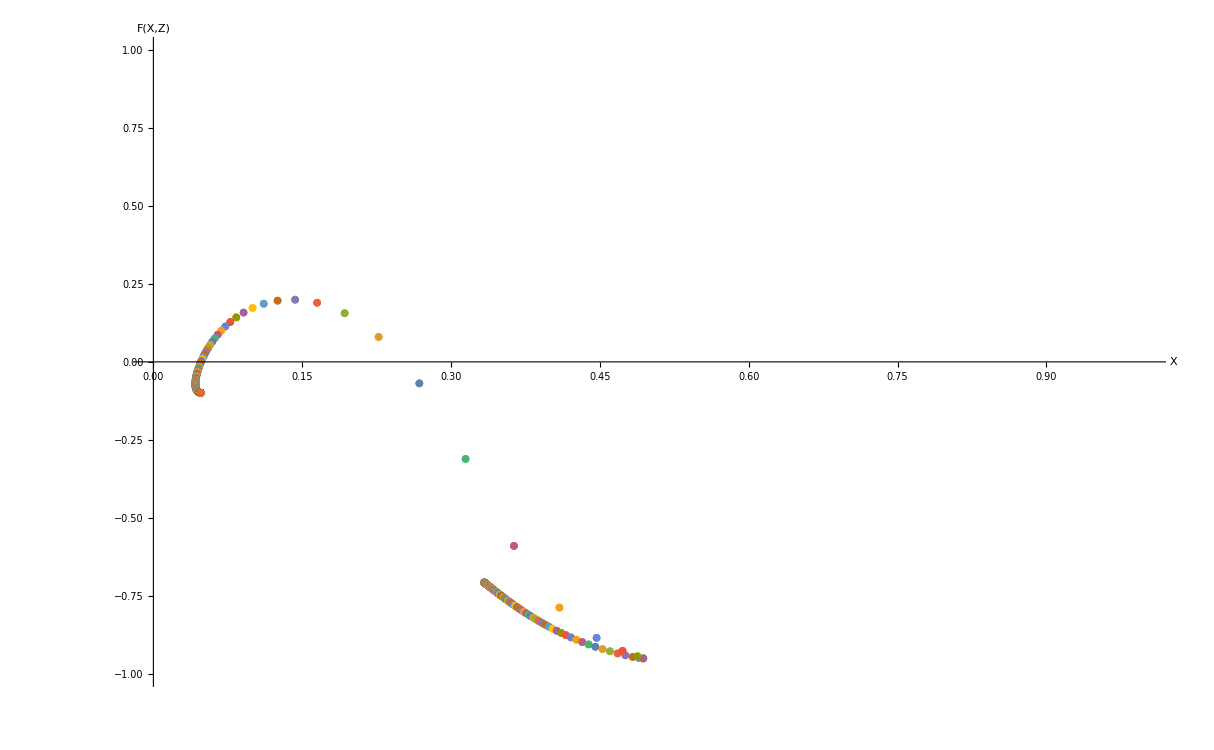

```mathematica
(*Plot X vs the remaining equation when Y' = 0*)
(*When F(X,Z) = 0, an Einstein point exists*)
EinsteinPlotTwoEinsteinPointsCompactTwoFPs=ListPlot[EinsteinPointSolutionsTwoEinsteinPointsCompactTwoFPs,PlotRange->{{0,1},{-1,1}},AxesLabel->{"X","F(X,Z)"}]
```

#### Plot the X-Y-Z Phase Space

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajTwoEinsteinPointsCompactTwoFPs[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0TwoEinsteinPointsTwoFPs,Z1[0]==Z0TwoEinsteinPointsTwoFPs},{X1,Y1,Z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition (√(0.133333-1. K))/(√(1.13333-1. K)) is not a number or a rectangular array of numbers.

NDSolve[{X1'[t]==-(3 (0.5 (1-X1[t])-X1[t]) (-0.05 (1-X1[t])+X1[t]) Y1[t])/(√(1-Y1[t]^2))-(7 (1-X1[t]) X1[t] Y1[t] Z1[t])/(√(1-Y1[t]^2) (1-Z1[t])),Y1'[t]==-Y1[t]^2 √(1-Y1[t]^2)-1/6 (1-Y1[t]^2)^(3/2) (-0.075-(0.35 X1[t])/(1-X1[t])-(3 X1[t]^2)/(1-X1[t])^2+Z1[t]/(1-Z1[t])),Z1'[t]==-(3 Y1[t] (1-Z1[t]) Z1[t])/(√(1-Y1[t]^2))+(7 X1[t] Y1[t] (1-Z1[t]) Z1[t])/((1-X1[t]) √(1-Y1[t]^2)),X1[0]==0.0909091,Y1[0]==(√(0.133333-K))/(√(1.13333-K)),Z1[0]==0.230769},{X1,Y1,Z1},{t,-100,100}]

```mathematica
(*Find the maximum value of K for this combination of X0 and Z0 so that Y0 is not imaginary*)
KMaxTwoEinsteinPointsCompactTwoFPs=K/.Flatten[Solve[Y0TwoEinsteinPointsTwoFPs==0,K]]
```

0.133333

```mathematica
(*Solve trajTwoEinsteinPointsCompact[K] for different values of K*)
```

```mathematica
solTwoEinsteinPointsCompactTwoFPs[1]=trajTwoEinsteinPointsCompactTwoFPs[-0.04]
```

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate,0.,Indeterminate} is not a list of numbers with dimensions {3} at {t,X1[t],Y1[t],Z1[t]} = {-3.21772,0.333334,1.,5.58877×10^-7}.

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsCompactTwoFPs[2]=trajTwoEinsteinPointsCompactTwoFPs[0.005]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsCompactTwoFPs[3]=trajTwoEinsteinPointsCompactTwoFPs[-0.1]
```

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate,0.,Indeterminate} is not a list of numbers with dimensions {3} at {t,X1[t],Y1[t],Z1[t]} = {-2.44494,0.333335,1.,8.755×10^-7}.

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsCompactTwoFPs[4]=trajTwoEinsteinPointsCompactTwoFPs[KMaxTwoEinsteinPointsCompactTwoFPs]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsCompactTwoFPs[5]=trajTwoEinsteinPointsCompactTwoFPs[0.06]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the trajectories for the different values of K given above*)
```

```mathematica
trajTwoEinsteinPointsCompactXYZTwoFPs[1]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactTwoFPs[1],{t,-3.21,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsCompactXYZTwoFPs[2]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactTwoFPs[2],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsCompactXYZTwoFPs[3]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactTwoFPs[3],{t,-2.43,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsCompactXYZTwoFPs[4]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactTwoFPs[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
trajTwoEinsteinPointsCompactXYZTwoFPs[5]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompactTwoFPs[5],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajTwoEinsteinPointsCaseCompactTwoFPs=Table[trajTwoEinsteinPointsCompactXYZTwoFPs[i],{i,1,5}];
```

```mathematica
(*Plot the Einstein fixed points*)
EinsteinFixedPointsTwoEinsteinPointsCompactTwoFPs=ListPointPlot3D[{EinsteinPoint1TwoEinsteinPointsCompactTwoFPs,EinsteinPoint2TwoEinsteinPointsCompactTwoFPs},PlotStyle->Black];
```

```mathematica
(*Solve the X-Y-Z system around the Einstein fixed point to plot the Closed Friedmann Separatrix (CFS)*)
CFSTwoEinsteinPointsSolCompactTwoFPs=NDSolve[{deXt,deYt,deZt,X1[0]==EinsteinPoint1TwoEinsteinPointsCompactTwoFPs[[1]],Y1[0]==-0.0005,Z1[0]==EinsteinPoint1TwoEinsteinPointsCompactTwoFPs[[3]]},{X1,Y1,Z1},{t,-100,100}]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the CFS*)
CFSTwoEinsteinPointsCompactTwoFPs=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.CFSTwoEinsteinPointsSolCompactTwoFPs,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->All];
```

```mathematica
(*Show the X-Y-Z phase space*)
Show[trajTwoEinsteinPointsCaseCompactTwoFPs,CFSTwoEinsteinPointsCompactTwoFPs,EinsteinFixedPointsTwoEinsteinPointsCompactTwoFPs,AccnXYZTwoFPs,FPsXYZTwoFPs,CompactFPShowXYZTwoFPs,XYZCompactFormat]
```

-Graphics3D-

#### Plot the X-Z Projection

```mathematica
(*Plot one solution on the X-Z plane*)
trajTwoEinsteinPointsCompactXZTwoFPs=ParametricPlot[Evaluate[{{Z1[t],X1[t]}}/.solTwoEinsteinPointsCompactTwoFPs[1],{t,-3.21,100},PlotStyle -> {{Black,Thick, Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.03,.03,0},1]]],Arrow[x]};
```

```mathematica
(*Plot the Einstein fixed points on the X-Z plane*)
EinsteinFixedPointsTwoEinsteinPointsCompactXZTwoFPs=ListPlot[{{EinsteinPoint1TwoEinsteinPointsCompactTwoFPs[[3]],EinsteinPoint1TwoEinsteinPointsCompactTwoFPs[[1]]},{EinsteinPoint2TwoEinsteinPointsCompactTwoFPs[[3]],EinsteinPoint2TwoEinsteinPointsCompactTwoFPs[[1]]}},PlotStyle->Black];
```

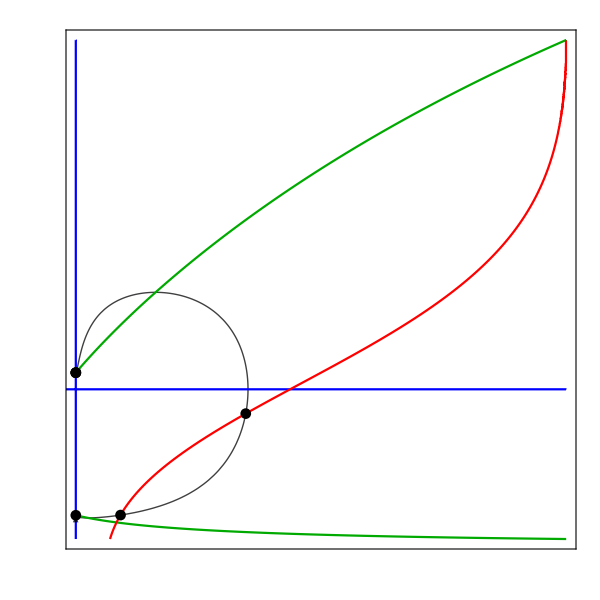

```mathematica
(*Show the X-Z phase space with the a'' = 0 (red), X' = 0 (green) and Z' = 0 (purple) curves*)
Show[trajTwoEinsteinPointsCompactXZTwoFPs,XLineTwoFPs,ZLineTwoFPs,AccnXZTwoFPs,EinsteinFixedPointsTwoEinsteinPointsCompactXZTwoFPs,FPsXZTwoFPs,CompactFPShowXZTwoFPs,XZCompactFormat]
```

### No Einstein Fixed Points

#### Plot to show there are no Einstein fixed points

```mathematica
(*Fix z0 such that there are no Einstein fixed points on the surface*)
z0NoEinsteinPointsTwoFPs=Ωm0*ℛ/(Ωx0*α);
```

```mathematica
(*Compactify z0*)
Z0NoEinsteinPointsTwoFPs=z0NoEinsteinPointsTwoFPs/(1+z0NoEinsteinPointsTwoFPs)
```

0.0432077

```mathematica
(*Substitute Z0NoEinsteinPoints into Y0 for this case*)
Y0NoEinsteinPointsTwoFPs=Y0/.Z0->Z0NoEinsteinPointsTwoFPs
```

(√(0.0483863-K))/(√(1.04839-K))

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajNoEinsteinPointsCompactTwoFPsEinsteinPointPlot[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0NoEinsteinPointsTwoFPs,Z1[0]==Z0NoEinsteinPointsTwoFPs},{X1,Y1,Z1},{t,-22.7,100}]
```

NDSolve::ndinnt: Initial condition (√(0.0483863-1. K))/(√(1.04839-1. K)) is not a number or a rectangular array of numbers.

NDSolve[{X1'[t]==-(3 (0.5 (1-X1[t])-X1[t]) (-0.05 (1-X1[t])+X1[t]) Y1[t])/(√(1-Y1[t]^2))-(7 (1-X1[t]) X1[t] Y1[t] Z1[t])/(√(1-Y1[t]^2) (1-Z1[t])),Y1'[t]==-Y1[t]^2 √(1-Y1[t]^2)-1/6 (1-Y1[t]^2)^(3/2) (-0.075-(0.35 X1[t])/(1-X1[t])-(3 X1[t]^2)/(1-X1[t])^2+Z1[t]/(1-Z1[t])),Z1'[t]==-(3 Y1[t] (1-Z1[t]) Z1[t])/(√(1-Y1[t]^2))+(7 X1[t] Y1[t] (1-Z1[t]) Z1[t])/((1-X1[t]) √(1-Y1[t]^2)),X1[0]==0.0909091,Y1[0]==(√(0.0483863-K))/(√(1.04839-K)),Z1[0]==0.0432077},{X1,Y1,Z1},{t,-22.7,100}]

```mathematica
(*Set-up tables of all X1 and Z1 values*)
XTableSolNoEinsteinPointsFullCompactTwoFPs=Table[X1[i]/.trajNoEinsteinPointsCompactTwoFPsEinsteinPointPlot[0],{i,-22.7,100,.1}];
ZTableSolNoEinsteinPointsFullCompactTwoFPs=Table[Z1[i]/.trajNoEinsteinPointsCompactTwoFPsEinsteinPointPlot[0],{i,-22.7,100,.1}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0*)
EinsteinPlotValuesSolNoEinsteinPointsFullCompactTwoFPs=(ZTableSolNoEinsteinPointsFullCompactTwoFPs/(1-ZTableSolNoEinsteinPointsFullCompactTwoFPs))+(XTableSolNoEinsteinPointsFullCompactTwoFPs/(1-XTableSolNoEinsteinPointsFullCompactTwoFPs))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSolNoEinsteinPointsFullCompactTwoFPs/(1-XTableSolNoEinsteinPointsFullCompactTwoFPs))^2;
```

```mathematica
(*Compactify EinsteinPlotValuesSolNoEinsteinPointsFullCompact*)
EinsteinPlotValuesSolNoEinsteinPointsFullXZTwoFPs=EinsteinPlotValuesSolNoEinsteinPointsFullCompactTwoFPs/Sqrt[1+EinsteinPlotValuesSolNoEinsteinPointsFullCompactTwoFPs^2];
```

```mathematica
(*Merge the XTableSolNoEinsteinPointsFullCompact values and the EinsteinPlotValuesSolNoEinsteinPointsFullXZ values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsNoEinsteinPointsCompactTwoFPs=MapThread[h,{XTableSolNoEinsteinPointsFullCompactTwoFPs,EinsteinPlotValuesSolNoEinsteinPointsFullXZTwoFPs}];
```

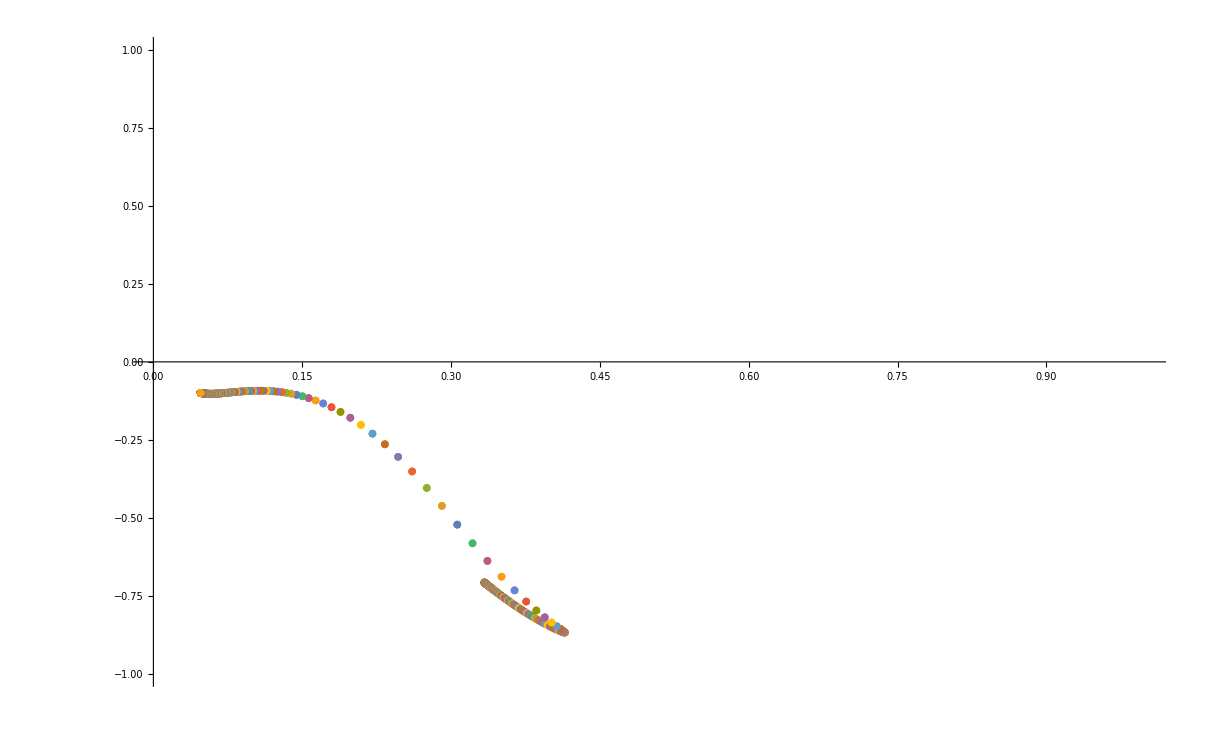

```mathematica
(*Plot X vs the remaining equation when Y' = 0*)
(*Here, F(X,Z) is never zero, so there are no Einstein fixed points*)
EinsteinPlotNoEinsteinPointsCompactTwoFPs=ListPlot[EinsteinPointSolutionsNoEinsteinPointsCompactTwoFPs,PlotRange->{{0,1},{-1,1}}]
```

#### Plot the X-Y-Z Phase Space

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajNoEinsteinPointsCompactTwoFPs[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0NoEinsteinPointsTwoFPs,Z1[0]==Z0NoEinsteinPointsTwoFPs},{X1,Y1,Z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition (√(0.0483863-1. K))/(√(1.04839-1. K)) is not a number or a rectangular array of numbers.

NDSolve[{X1'[t]==-(3 (0.5 (1-X1[t])-X1[t]) (-0.05 (1-X1[t])+X1[t]) Y1[t])/(√(1-Y1[t]^2))-(7 (1-X1[t]) X1[t] Y1[t] Z1[t])/(√(1-Y1[t]^2) (1-Z1[t])),Y1'[t]==-Y1[t]^2 √(1-Y1[t]^2)-1/6 (1-Y1[t]^2)^(3/2) (-0.075-(0.35 X1[t])/(1-X1[t])-(3 X1[t]^2)/(1-X1[t])^2+Z1[t]/(1-Z1[t])),Z1'[t]==-(3 Y1[t] (1-Z1[t]) Z1[t])/(√(1-Y1[t]^2))+(7 X1[t] Y1[t] (1-Z1[t]) Z1[t])/((1-X1[t]) √(1-Y1[t]^2)),X1[0]==0.0909091,Y1[0]==(√(0.0483863-K))/(√(1.04839-K)),Z1[0]==0.0432077},{X1,Y1,Z1},{t,-100,100}]

```mathematica
(*Find the maximum value of K for this combination of X0 and Z0 such that Y0 is not imaginary*)
KMaxNoEinsteinPointsCompactTwoFPs=K/.Solve[Y0NoEinsteinPointsTwoFPs==0,K][[1]]
```

0.0483863

```mathematica
(*Solve trajNoEinsteinPointsCompact[K] for different values of K*)
```

```mathematica
solNoEinsteinPointsCompactTwoFPs[1]=trajNoEinsteinPointsCompactTwoFPs[-.01]
```

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate,0.,Indeterminate} is not a list of numbers with dimensions {3} at {t,X1[t],Y1[t],Z1[t]} = {-5.58576,0.333334,1.,4.55912×10^-7}.

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solNoEinsteinPointsCompactTwoFPs[2]=trajNoEinsteinPointsCompactTwoFPs[0.005]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solNoEinsteinPointsCompactTwoFPs[3]=trajNoEinsteinPointsCompactTwoFPs[-.1]
```

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate,0.,Indeterminate} is not a list of numbers with dimensions {3} at {t,X1[t],Y1[t],Z1[t]} = {-2.79794,0.333335,1.,1.03383×10^-6}.

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solNoEinsteinPointsCompactTwoFPs[4]=trajNoEinsteinPointsCompactTwoFPs[0.02]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solNoEinsteinPointsCompactTwoFPs[5]=trajNoEinsteinPointsCompactTwoFPs[0.032]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solNoEinsteinPointsCompactTwoFPs[6]=trajNoEinsteinPointsCompactTwoFPs[KMaxNoEinsteinPointsCompactTwoFPs]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
(*Plot the trajectories for the different values of K given above.*)
```

```mathematica
trajNoEinsteinPointsCompactXYZTwoFPs[1]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactTwoFPs[1],{t,-5.58,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsCompactXYZTwoFPs[2]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactTwoFPs[2],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsCompactXYZTwoFPs[3]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactTwoFPs[3],{t,-2.7,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsCompactXYZTwoFPs[4]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactTwoFPs[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsCompactXYZTwoFPs[5]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactTwoFPs[5],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsCompactXYZTwoFPs[6]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompactTwoFPs[6],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
(*Put the plots of the trajectories into a table*)
trajNoEinsteinPointsPlotsCompactTwoFPs=Table[trajNoEinsteinPointsCompactXYZTwoFPs[i],{i,1,6}];
```

```mathematica
(*Show the X-Y-Z phase space*)
Show[trajNoEinsteinPointsPlotsCompactTwoFPs,AccnXYZTwoFPs,FPsXYZTwoFPs,CompactFPShowXYZTwoFPs,XYZCompactFormat]
```

-Graphics3D-

#### Plot the X-Z Projection

```mathematica
(*Plot one solution on the X-Z plane*)
trajNoEinsteinPointsCompactXZTwoFPs=ParametricPlot[Evaluate[{{Z1[t],X1[t]}}/.solNoEinsteinPointsCompactTwoFPs[1],{t,-5.58,100},PlotStyle -> {{Black,Thick, Opacity[0.75]}}],PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,0,.03,0,.03,0},1]]],Arrow[x]};
```

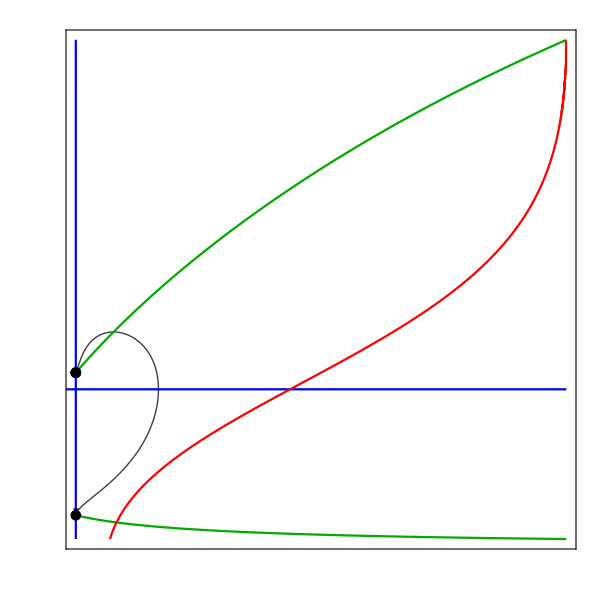

```mathematica
(*Show the X-Z phase space with the a'' = 0 (red), X' = 0 (green) and Z' = 0 (purple) curves*)
Show[trajNoEinsteinPointsCompactXZTwoFPs,XLineTwoFPs,ZLineTwoFPs,AccnXZTwoFPs,FPsXZTwoFPs,CompactFPShowXZTwoFPs,XZCompactFormat]
```

## Investigate system when ℛ = 10^(-120)

### Set-up

```mathematica
(*Clear variables*)
Clear[q,ϵ,ℛ,wx]
```

```mathematica
(*Set parameter values*)
q=1.5;
ϵ=-1;
ℛ=10^(-120);
wx=-1+2*ℛ;
```

```mathematica
(*Define Ωx0 and Ωm0 using data from Planck 2018*)
Ωx0=0.6889;
Ωm0=0.3111;
```

```mathematica
(*Set a value for α, which sets the value of the low energy cosmological constant*)
α=0.5;
```

```mathematica
(*Define the initial conditions, where a0 = 1 and K is defined as k/ρ* *)

x0=ℛ/α;
y0=Sqrt[x0/3+Z0/(3*(1-Z0))-K];
```

```mathematica
(*Compactify the initial conditions*)

X0=x0/(1+x0);
Y0=y0/Sqrt[1+y0^2];
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y in terms of time, t*)
deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*(X1[t]-ℛ*(1-X1[t]))*((1+wx)*(1-X1[t])+ϵ*X1[t])-q*X1[t]*(1-X1[t])*(Z1[t]/(1-Z1[t]))*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((Z1[t]/(1-Z1[t]))+(X1[t]/(1-X1[t]))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X1[t]^2/((1-X1[t])^2))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2))) + q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
```

### Find the value of z0 to give the limiting case

```mathematica
(*Fix z0 using the density parameters*)
z0RealisticℛTwoFPs=Ωm0*ℛ/(Ωx0*α)
```

9.03179×10^-121

```mathematica
(*Compactify z0*)
Z0RealisticℛTwoFPs=z0RealisticℛTwoFPs/(1+z0RealisticℛTwoFPs)
```

9.03179×10^-121

```mathematica
(*Substitute Z0Realisticℛ into Y0 for this case*)
Y0RealisticℛTwoFPs=Y0/.Z0->Z0RealisticℛTwoFPs
```

(√(9.67726×10^-121-K))/(√(1.-K))

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajRealisticℛTwoFPs[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0RealisticℛTwoFPs,Z1[0]==Z0RealisticℛTwoFPs},{X1,Y1,Z1},{t,-100,100}];
```

NDSolve::ndinnt: Initial condition (√(9.67726×10^-121-1. K))/(√(1.-1. K)) is not a number or a rectangular array of numbers.

```mathematica
(*Set-up tables of all X1 and Z1 values*)
XTableRealisticℛTwoFPs=Table[X1[i]/.trajRealisticℛTwoFPs[0],{i,-100,100,.1}];
ZTableRealisticℛTwoFPs=Table[Z1[i]/.trajRealisticℛTwoFPs[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of X and Z found numerically, solve the remaining equation when Y' = 0*)
EinsteinPlotValuesRealisticℛTwoFPs=(ZTableRealisticℛTwoFPs/(1-ZTableRealisticℛTwoFPs))+(XTableRealisticℛTwoFPs/(1-XTableRealisticℛTwoFPs))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableRealisticℛTwoFPs/(1-XTableRealisticℛTwoFPs))^2;
```

```mathematica
(*Compactify EinsteinPlotValuesRealisticℛ*)
EinsteinPlotRealisticℛCompactTwoFPs=EinsteinPlotValuesRealisticℛTwoFPs/Sqrt[1+EinsteinPlotValuesRealisticℛTwoFPs^2];
```

```mathematica
(*Find the maximum value of EinsteinPlotRealisticℛCompact*)
(*As EinsteinPlotRealisticℛCompact is always less than zero there are no Einstein points when z0 is defined using the density parameters*)
Max[EinsteinPlotRealisticℛCompactTwoFPs]
```

-3.09682×10^-120